```mathematica
β[ω_,δ_,t_,ϵ_]:={{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ+ω,-t},{0,0,0,0,0,-t,ⅈ δ-ϵ+ω}}
```

```mathematica
T2[t_]:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}
```

```mathematica
T1[t_]:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}}
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,t,ϵ]],A:=Inverse[β[ω,δ,t,ϵ]],B:=Inverse[β[ω,δ,t,ϵ]],T1:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}},T2:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}},Do[J=Inverse[IdentityMatrix[7]-A.T1.Inverse[IdentityMatrix[7]-B.T2.J.T2].B.T1].A,4000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]
```

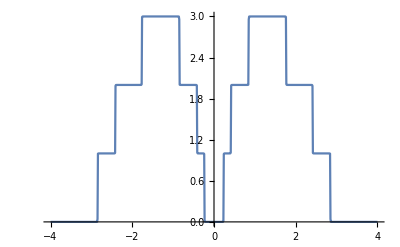

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m1=Table[{ω,ψ[ω,0.001,1,0,0.5]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000279995},{0.01,0.0000280805},{0.02,0.000028326},{0.03,0.0000287434},{0.04,0.0000293458},{0.05,0.000030153},{0.06,0.0000311929},{0.07,0.0000325038},{0.08,0.0000341383},{0.09,0.0000361684},{0.1,0.0000386941},{0.11,0.0000418562},{0.12,0.0000458577},{0.13,0.0000509996},{0.14,0.0000577436},{0.15,0.0000668293},{0.16,0.000079504},{0.17,0.0000980155},{0.18,0.000126774},{0.19,0.000175487},{0.2,0.000269296},{0.21,0.000492136},{0.22,0.00128997},{0.23,0.0116162},{0.24,0.991847},{0.25,0.999059},{0.26,0.999686},{0.27,0.999857},{0.28,0.999928},{0.29,0.999963},{0.3,0.999985},{0.31,1.},{0.32,1.00001},{0.33,1.00003},{0.34,1.00004},{0.35,1.00006},{0.36,1.00008},{0.37,1.00013},{0.38,1.00022},{0.39,1.00043},{0.4,1.00124},{0.41,1.01355},{0.42,1.99273},{0.43,1.99901},{0.44,1.99963},{0.45,1.99981},{0.46,1.99988},{0.47,1.99992},{0.48,1.99995},{0.49,1.99996},{0.5,1.99997},{0.51,1.99998},{0.52,1.99998},{0.53,1.99998},{0.54,1.99999},{0.55,1.99999},{0.56,1.99999},{0.57,1.99999},{0.58,1.99999},{0.59,2.},{0.6,2.},{0.61,2.},{0.62,2.},{0.63,2.},{0.64,2.},{0.65,2.},{0.66,2.},{0.67,2.},{0.68,2.00001},{0.69,2.00001},{0.7,2.00001},{0.71,2.00001},{0.72,2.00001},{0.73,2.00001},{0.74,2.00002},{0.75,2.00002},{0.76,2.00003},{0.77,2.00004},{0.78,2.00005},{0.79,2.00007},{0.8,2.00011},{0.81,2.00017},{0.82,2.00032},{0.83,2.00078},{0.84,2.00409},{0.85,2.95656},{0.86,2.99833},{0.87,2.99949},{0.88,2.99976},{0.89,2.99986},{0.9,2.9999},{0.91,2.99993},{0.92,2.99995},{0.93,2.99996},{0.94,2.99997},{0.95,2.99997},{0.96,2.99998},{0.97,2.99998},{0.98,2.99998},{0.99,2.99999},{1.,2.99999},{1.01,2.99999},{1.02,2.99999},{1.03,2.99999},{1.04,2.99999},{1.05,2.99999},{1.06,2.99999},{1.07,2.99999},{1.08,2.99999},{1.09,2.99999},{1.1,2.99999},{1.11,2.99999},{1.12,2.99999},{1.13,2.99999},{1.14,3.},{1.15,3.},{1.16,3.},{1.17,3.},{1.18,3.},{1.19,3.},{1.2,3.},{1.21,3.},{1.22,3.},{1.23,3.},{1.24,3.},{1.25,3.},{1.26,3.},{1.27,3.},{1.28,3.},{1.29,3.},{1.3,3.},{1.31,3.},{1.32,3.},{1.33,3.},{1.34,3.},{1.35,3.},{1.36,3.},{1.37,3.},{1.38,3.},{1.39,3.},{1.4,3.},{1.41,3.},{1.42,3.},{1.43,3.},{1.44,3.},{1.45,3.},{1.46,3.},{1.47,3.},{1.48,2.99999},{1.49,2.99999},{1.5,2.99999},{1.51,2.99999},{1.52,2.99999},{1.53,2.99999},{1.54,2.99999},{1.55,2.99999},{1.56,2.99999},{1.57,2.99999},{1.58,2.99999},{1.59,2.99999},{1.6,2.99999},{1.61,2.99999},{1.62,2.99999},{1.63,2.99998},{1.64,2.99998},{1.65,2.99998},{1.66,2.99998},{1.67,2.99997},{1.68,2.99996},{1.69,2.99995},{1.7,2.99994},{1.71,2.99992},{1.72,2.99988},{1.73,2.9998},{1.74,2.99961},{1.75,2.99894},{1.76,2.99153},{1.77,2.01124},{1.78,2.00116},{1.79,2.00041},{1.8,2.0002},{1.81,2.00012},{1.82,2.00008},{1.83,2.00006},{1.84,2.00004},{1.85,2.00003},{1.86,2.00003},{1.87,2.00002},{1.88,2.00002},{1.89,2.00001},{1.9,2.00001},{1.91,2.00001},{1.92,2.00001},{1.93,2.00001},{1.94,2.00001},{1.95,2.},{1.96,2.},{1.97,2.},{1.98,2.},{1.99,2.},{2.,2.},{2.01,2.},{2.02,2.},{2.03,2.},{2.04,2.},{2.05,2.},{2.06,2.},{2.07,2.},{2.08,2.},{2.09,2.},{2.1,2.},{2.11,2.},{2.12,2.},{2.13,2.},{2.14,2.},{2.15,2.},{2.16,2.},{2.17,2.},{2.18,1.99999},{2.19,1.99999},{2.2,1.99999},{2.21,1.99999},{2.22,1.99999},{2.23,1.99999},{2.24,1.99999},{2.25,1.99999},{2.26,1.99999},{2.27,1.99999},{2.28,1.99998},{2.29,1.99998},{2.3,1.99998},{2.31,1.99997},{2.32,1.99997},{2.33,1.99996},{2.34,1.99995},{2.35,1.99994},{2.36,1.99991},{2.37,1.99987},{2.38,1.99978},{2.39,1.99957},{2.4,1.99875},{2.41,1.98644},{2.42,1.00727},{2.43,1.00099},{2.44,1.00037},{2.45,1.00019},{2.46,1.00011},{2.47,1.00008},{2.48,1.00005},{2.49,1.00004},{2.5,1.00003},{2.51,1.00002},{2.52,1.00002},{2.53,1.00001},{2.54,1.00001},{2.55,1.00001},{2.56,1.00001},{2.57,1.00001},{2.58,1.},{2.59,1.},{2.6,1.},{2.61,1.},{2.62,1.},{2.63,0.999999},{2.64,0.999998},{2.65,0.999996},{2.66,0.999995},{2.67,0.999994},{2.68,0.999993},{2.69,0.999991},{2.7,0.99999},{2.71,0.999988},{2.72,0.999985},{2.73,0.999982},{2.74,0.999979},{2.75,0.999974},{2.76,0.999967},{2.77,0.999958},{2.78,0.999944},{2.79,0.999923},{2.8,0.999888},{2.81,0.999821},{2.82,0.99967},{2.83,0.999199},{2.84,0.995874},{2.85,0.0433182},{2.86,0.00164489},{2.87,0.000496725},{2.88,0.000235194},{2.89,0.000136355},{2.9,0.0000887579},{2.91,0.0000622831},{2.92,0.0000460724},{2.93,0.0000354399},{2.94,0.0000280956},{2.95,0.0000228136},{2.96,0.0000188896},{2.97,0.0000158959},{2.98,0.0000135605},{2.99,0.000011704},{3.,0.000010204},{3.01,8.97489×10^-6},{3.02,7.95521×10^-6},{3.03,7.09997×10^-6},{3.04,6.37564×10^-6},{3.05,5.75681×10^-6},{3.06,5.22393×10^-6},{3.07,4.7618×10^-6},{3.08,4.3584×10^-6},{3.09,4.00418×10^-6},{3.1,3.69145×10^-6},{3.11,3.41396×10^-6},{3.12,3.1666×10^-6},{3.13,2.94516×10^-6},{3.14,2.74612×10^-6},{3.15,2.56655×10^-6},{3.16,2.40399×10^-6},{3.17,2.25635×10^-6},{3.18,2.12186×10^-6},{3.19,1.99898×10^-6},{3.2,1.88643×10^-6},{3.21,1.78306×10^-6},{3.22,1.68791×10^-6},{3.23,1.60011×10^-6},{3.24,1.51894×10^-6},{3.25,1.44374×10^-6},{3.26,1.37393×10^-6},{3.27,1.30901×10^-6},{3.28,1.24853×10^-6},{3.29,1.19209×10^-6},{3.3,1.13935×10^-6},{3.31,1.08998×10^-6},{3.32,1.0437×10^-6},{3.33,1.00026×10^-6},{3.34,9.59429×10^-7},{3.35,9.21004×10^-7},{3.36,8.84799×10^-7},{3.37,8.50644×10^-7},{3.38,8.18388×10^-7},{3.39,7.87893×10^-7},{3.4,7.59032×10^-7},{3.41,7.31691×10^-7},{3.42,7.05764×10^-7},{3.43,6.81156×10^-7},{3.44,6.57779×10^-7},{3.45,6.35552×10^-7},{3.46,6.144×10^-7},{3.47,5.94256×10^-7},{3.48,5.75057×10^-7},{3.49,5.56744×10^-7},{3.5,5.39264×10^-7},{3.51,5.22568×10^-7},{3.52,5.06608×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24144×10^-7},{3.59,4.12305×10^-7},{3.6,4.00934×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000133833},{0.01,0.0000148362},{0.02,0.0000128643},{0.03,7.52629×10^-6},{0.04,1.17566×10^-6},{0.05,0.0000132972},{0.06,0.0000289554},{0.07,0.000048336},{0.08,0.0000717048},{0.09,0.0000994242},{0.1,0.000131978},{0.11,0.000170006},{0.12,0.00021436},{0.13,0.000266177},{0.14,0.000327009},{0.15,0.000399009},{0.16,0.000485248},{0.17,0.000590265},{0.18,0.000721045},{0.19,0.000888916},{0.2,0.00111349},{0.21,0.00143147},{0.22,0.00191572},{0.23,0.00255162},{0.24,0.0733736},{0.25,0.23703},{0.26,0.425494},{0.27,0.610404},{0.28,0.759789},{0.29,0.856912},{0.3,0.904986},{0.31,0.91801},{0.32,0.910694},{0.33,0.893958},{0.34,0.874586},{0.35,0.856315},{0.36,0.840973},{0.37,0.829256},{0.38,0.821161},{0.39,0.816067},{0.4,0.812072},{0.41,0.799679},{0.42,1.02976},{0.43,1.29545},{0.44,1.44114},{0.45,1.53609},{0.46,1.60523},{0.47,1.65935},{0.48,1.70368},{0.49,1.74099},{0.5,1.77276},{0.51,1.79984},{0.52,1.82272},{0.53,1.84177},{0.54,1.85725},{0.55,1.86947},{0.56,1.87872},{0.57,1.88535},{0.58,1.88974},{0.59,1.89229},{0.6,1.89339},{0.61,1.89341},{0.62,1.8927},{0.63,1.89155},{0.64,1.89021},{0.65,1.88889},{0.66,1.8877},{0.67,1.88672},{0.68,1.88597},{0.69,1.88539},{0.7,1.88489},{0.71,1.8843},{0.72,1.88344},{0.73,1.88202},{0.74,1.87974},{0.75,1.87621},{0.76,1.87097},{0.77,1.86341},{0.78,1.85272},{0.79,1.83763},{0.8,1.81607},{0.81,1.78422},{0.82,1.73403},{0.83,1.64519},{0.84,1.44434},{0.85,0.756175},{0.86,0.896038},{0.87,1.05399},{0.88,1.20536},{0.89,1.35131},{0.9,1.49248},{0.91,1.62929},{0.92,1.76227},{0.93,1.89212},{0.94,2.01972},{0.95,2.14614},{0.96,2.27241},{0.97,2.39936},{0.98,2.52689},{0.99,2.65259},{1.,2.76848},{1.01,2.85397},{1.02,2.86196},{1.03,2.6982},{1.04,2.21876},{1.05,1.41853},{1.06,0.553622},{1.07,0.752745},{1.08,1.13036},{1.09,1.40181},{1.1,1.63297},{1.11,1.83449},{1.12,2.00861},{1.13,2.15531},{1.14,2.27391},{1.15,2.36424},{1.16,2.42744},{1.17,2.46634},{1.18,2.48512},{1.19,2.48869},{1.2,2.48192},{1.21,2.46916},{1.22,2.4539},{1.23,2.43876},{1.24,2.42564},{1.25,2.41579},{1.26,2.41007},{1.27,2.40902},{1.28,2.41301},{1.29,2.42226},{1.3,2.43692},{1.31,2.45702},{1.32,2.48248},{1.33,2.51301},{1.34,2.54804},{1.35,2.58657},{1.36,2.62708},{1.37,2.66741},{1.38,2.70482},{1.39,2.73623},{1.4,2.75858},{1.41,2.76949},{1.42,2.7678},{1.43,2.75385},{1.44,2.7294},{1.45,2.69722},{1.46,2.66042},{1.47,2.62196},{1.48,2.58427},{1.49,2.54919},{1.5,2.51794},{1.51,2.4913},{1.52,2.46974},{1.53,2.45352},{1.54,2.44279},{1.55,2.43757},{1.56,2.43767},{1.57,2.44248},{1.58,2.45064},{1.59,2.45967},{1.6,2.46596},{1.61,2.46521},{1.62,2.45378},{1.63,2.42992},{1.64,2.3942},{1.65,2.34864},{1.66,2.29529},{1.67,2.23514},{1.68,2.16737},{1.69,2.08881},{1.7,1.99309},{1.71,1.8688},{1.72,1.69651},{1.73,1.445},{1.74,1.0702},{1.75,0.510573},{1.76,0.455823},{1.77,3},{1.78,3},{1.79,3},{1.8,2.16462},{1.81,0.888136},{1.82,0.247866},{1.83,0.392963},{1.84,0.781068},{1.85,1.01699},{1.86,1.16817},{1.87,1.26983},{1.88,1.34089},{1.89,1.39212},{1.9,1.43},{1.91,1.45862},{1.92,1.48067},{1.93,1.498},{1.94,1.51189},{1.95,1.52326},{1.96,1.53281},{1.97,1.54103},{1.98,1.54829},{1.99,1.55488},{2.,1.56102},{2.01,1.56685},{2.02,1.57251},{2.03,1.57808},{2.04,1.58362},{2.05,1.58917},{2.06,1.59477},{2.07,1.60043},{2.08,1.60616},{2.09,1.61198},{2.1,1.61788},{2.11,1.62387},{2.12,1.62993},{2.13,1.63608},{2.14,1.6423},{2.15,1.64857},{2.16,1.65489},{2.17,1.66121},{2.18,1.66751},{2.19,1.67373},{2.2,1.67981},{2.21,1.68565},{2.22,1.69116},{2.23,1.69621},{2.24,1.70067},{2.25,1.7044},{2.26,1.70724},{2.27,1.70906},{2.28,1.70971},{2.29,1.70906},{2.3,1.70697},{2.31,1.7033},{2.32,1.69785},{2.33,1.69027},{2.34,1.67998},{2.35,1.66585},{2.36,1.64578},{2.37,1.61577},{2.38,1.5679},{2.39,1.48577},{2.4,1.3322},{2.41,1.01207},{2.42,0.847114},{2.43,0.872884},{2.44,0.893177},{2.45,0.864045},{2.46,0.233314},{2.47,0.154977},{2.48,0.510151},{2.49,0.648405},{2.5,0.722229},{2.51,0.772103},{2.52,0.810652},{2.53,0.842485},{2.54,0.869274},{2.55,0.891437},{2.56,0.908834},{2.57,0.921137},{2.58,0.928071},{2.59,0.92958},{2.6,0.925923},{2.61,0.917709},{2.62,0.905868},{2.63,0.891573},{2.64,0.876143},{2.65,0.860937},{2.66,0.847277},{2.67,0.836387},{2.68,0.829351},{2.69,0.827083},{2.7,0.830252},{2.71,0.83916},{2.72,0.853465},{2.73,0.871714},{2.74,0.890628},{2.75,0.90429},{2.76,0.903831},{2.77,0.878825},{2.78,0.821327},{2.79,0.730996},{2.8,0.616656},{2.81,0.491459},{2.82,0.365039},{2.83,0.237145},{2.84,0.0887302},{2.85,0.156086},{2.86,1.21029},{2.87,3},{2.88,0.341781},{2.89,0.0888089},{2.9,0.000429227},{2.91,0.146213},{2.92,0.0534444},{2.93,0.0325059},{2.94,0.0225679},{2.95,0.0167243},{2.96,0.0129095},{2.97,0.0102547},{2.98,0.00832348},{2.99,0.00687175},{3.,0.00575208},{3.01,0.00487046},{3.02,0.00416431},{3.03,0.00359047},{3.04,0.00311838},{3.05,0.0027258},{3.06,0.00239626},{3.07,0.00211735},{3.08,0.00187952},{3.09,0.00167538},{3.1,0.00149911},{3.11,0.00134605},{3.12,0.00121251},{3.13,0.00109545},{3.14,0.000992411},{3.15,0.000901363},{3.16,0.000820621},{3.17,0.000748778},{3.18,0.000684654},{3.19,0.000627255},{3.2,0.000575733},{3.21,0.000529369},{3.22,0.000487545},{3.23,0.000449731},{3.24,0.00041547},{3.25,0.000384363},{3.26,0.000356066},{3.27,0.000330277},{3.28,0.000306735},{3.29,0.000285206},{3.3,0.000265487},{3.31,0.000247399},{3.32,0.000230784},{3.33,0.000215499},{3.34,0.000201419},{3.35,0.000188434},{3.36,0.000176443},{3.37,0.000165356},{3.38,0.000155095},{3.39,0.000145587},{3.4,0.000136768},{3.41,0.000128579},{3.42,0.000120969},{3.43,0.000113888},{3.44,0.000107295},{3.45,0.000101151},{3.46,0.0000954194},{3.47,0.0000900687},{3.48,0.0000850695},{3.49,0.0000803949},{3.5,0.0000760207},{3.51,0.0000719245},{3.52,0.0000680858},{3.53,0.000064486},{3.54,0.000061108},{3.55,0.0000579359},{3.56,0.0000549553},{3.57,0.0000521529},{3.58,0.0000495164},{3.59,0.0000470346},{3.6,0.0000446969},{3.61,0.0000424939},{3.62,0.0000404166},{3.63,0.0000384567},{3.64,0.0000366067},{3.65,0.0000348595},{3.66,0.0000332085},{3.67,0.0000316478},{3.68,0.0000301716},{3.69,0.0000287747},{3.7,0.0000274523},{3.71,0.0000261999},{3.72,0.0000250131},{3.73,0.0000238881},{3.74,0.0000228212},{3.75,0.000021809},{3.76,0.0000208483},{3.77,0.0000199361},{3.78,0.0000190696},{3.79,0.0000182463},{3.8,0.0000174637},{3.81,0.0000167194},{3.82,0.0000160114},{3.83,0.0000153377},{3.84,0.0000146963},{3.85,0.0000140856},{3.86,0.0000135038},{3.87,0.0000129494},{3.88,0.0000124209},{3.89,0.000011917},{3.9,0.0000114364},{3.91,0.0000109778},{3.92,0.0000105402},{3.93,0.0000101224},{3.94,9.72336×10^-6},{3.95,9.34222×10^-6},{3.96,8.97804×10^-6},{3.97,8.62996×10^-6},{3.98,8.29719×10^-6},{3.99,7.97897×10^-6},{4.,7.67457×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000135278},{0.01,0.0000482187},{0.02,0.0000944998},{0.03,0.000153005},{0.04,0.000224859},{0.05,0.00031173},{0.06,0.000415936},{0.07,0.00054059},{0.08,0.000689828},{0.09,0.000869136},{0.1,0.00108583},{0.11,0.00134975},{0.12,0.00167435},{0.13,0.00207835},{0.14,0.00258833},{0.15,0.00324311},{0.16,0.00410127},{0.17,0.00525473},{0.18,0.00685533},{0.19,0.00917096},{0.2,0.0127193},{0.21,0.0186443},{0.22,0.030115},{0.23,0.0616675},{0.24,0.0126482},{0.25,0.175058},{0.26,0.317558},{0.27,0.427575},{0.28,0.514038},{0.29,0.582945},{0.3,0.638446},{0.31,0.683488},{0.32,0.720196},{0.33,0.750101},{0.34,0.774279},{0.35,0.793411},{0.36,0.807773},{0.37,0.817108},{0.38,0.820209},{0.39,0.813625},{0.4,0.786343},{0.41,0.677724},{0.42,0.834578},{0.43,1.25687},{0.44,1.48144},{0.45,1.61989},{0.46,1.71284},{0.47,1.77852},{0.48,1.82642},{0.49,1.86198},{0.5,1.88856},{0.51,1.90837},{0.52,1.92292},{0.53,1.93331},{0.54,1.94032},{0.55,1.94458},{0.56,1.94656},{0.57,1.94664},{0.58,1.94516},{0.59,1.94238},{0.6,1.93853},{0.61,1.93382},{0.62,1.92845},{0.63,1.92257},{0.64,1.91634},{0.65,1.90989},{0.66,1.90336},{0.67,1.89685},{0.68,1.89048},{0.69,1.88433},{0.7,1.87849},{0.71,1.87302},{0.72,1.868},{0.73,1.86347},{0.74,1.85947},{0.75,1.85603},{0.76,1.85316},{0.77,1.85086},{0.78,1.8491},{0.79,1.8478},{0.8,1.84681},{0.81,1.84585},{0.82,1.84428},{0.83,1.84053},{0.84,1.829},{0.85,1.78488},{0.86,1.84524},{0.87,1.91944},{0.88,1.99719},{0.89,2.07332},{0.9,2.14361},{0.91,2.20525},{0.92,2.25711},{0.93,2.29945},{0.94,2.33353},{0.95,2.3611},{0.96,2.38409},{0.97,2.40442},{0.98,2.42395},{0.99,2.44457},{1.,2.46811},{1.01,2.49586},{1.02,2.52514},{1.03,2.5322},{1.04,2.40481},{1.05,1.91166},{1.06,1.25592},{1.07,1.09798},{1.08,1.55299},{1.09,1.69911},{1.1,1.67354},{1.11,1.58946},{1.12,1.50336},{1.13,1.4751},{1.14,1.54205},{1.15,1.68312},{1.16,1.84673},{1.17,1.99717},{1.18,2.123},{1.19,2.22549},{1.2,2.30943},{1.21,2.37944},{1.22,2.43902},{1.23,2.49052},{1.24,2.53545},{1.25,2.57466},{1.26,2.60858},{1.27,2.63736},{1.28,2.66103},{1.29,2.67953},{1.3,2.69288},{1.31,2.70117},{1.32,2.7046},{1.33,2.70354},{1.34,2.69847},{1.35,2.68999},{1.36,2.67876},{1.37,2.66547},{1.38,2.65081},{1.39,2.6354},{1.4,2.61981},{1.41,2.60453},{1.42,2.58993},{1.43,2.57626},{1.44,2.56367},{1.45,2.55216},{1.46,2.5416},{1.47,2.53171},{1.48,2.52204},{1.49,2.512},{1.5,2.50084},{1.51,2.48768},{1.52,2.47161},{1.53,2.45175},{1.54,2.42737},{1.55,2.39805},{1.56,2.36376},{1.57,2.32486},{1.58,2.28214},{1.59,2.23662},{1.6,2.18942},{1.61,2.14159},{1.62,2.09396},{1.63,2.04708},{1.64,2.00111},{1.65,1.95588},{1.66,1.91082},{1.67,1.86492},{1.68,1.81665},{1.69,1.76375},{1.7,1.70291},{1.71,1.62911},{1.72,1.53441},{1.73,1.4051},{1.74,1.21401},{1.75,0.891389},{1.76,0.137581},{1.77,2.08144},{1.78,1.15609},{1.79,1.5609},{1.8,1.18858},{1.81,0.468298},{1.82,0.400088},{1.83,1.05748},{1.84,1.44031},{1.85,1.61882},{1.86,1.70962},{1.87,1.76061},{1.88,1.79144},{1.89,1.81101},{1.9,1.82378},{1.91,1.83219},{1.92,1.83767},{1.93,1.84114},{1.94,1.84323},{1.95,1.84438},{1.96,1.84493},{1.97,1.84514},{1.98,1.84521},{1.99,1.8453},{2.,1.84553},{2.01,1.84596},{2.02,1.84662},{2.03,1.84751},{2.04,1.84856},{2.05,1.84969},{2.06,1.85079},{2.07,1.85169},{2.08,1.85226},{2.09,1.85234},{2.1,1.85176},{2.11,1.85041},{2.12,1.84819},{2.13,1.84503},{2.14,1.84089},{2.15,1.83574},{2.16,1.82956},{2.17,1.8223},{2.18,1.81385},{2.19,1.804},{2.2,1.79245},{2.21,1.77876},{2.22,1.76234},{2.23,1.74254},{2.24,1.71867},{2.25,1.69009},{2.26,1.65639},{2.27,1.61747},{2.28,1.57366},{2.29,1.52575},{2.3,1.47494},{2.31,1.42273},{2.32,1.37071},{2.33,1.32037},{2.34,1.27286},{2.35,1.22883},{2.36,1.18809},{2.37,1.1491},{2.38,1.10736},{2.39,1.05007},{2.4,0.929561},{2.41,0.361937},{2.42,0.641963},{2.43,0.723732},{2.44,2.31277},{2.45,0.637422},{2.46,0.772947},{2.47,0.809947},{2.48,0.819807},{2.49,0.817356},{2.5,0.807815},{2.51,0.793641},{2.52,0.77628},{2.53,0.756762},{2.54,0.735918},{2.55,0.714478},{2.56,0.693094},{2.57,0.672362},{2.58,0.652816},{2.59,0.63494},{2.6,0.619169},{2.61,0.605904},{2.62,0.595529},{2.63,0.588424},{2.64,0.584994},{2.65,0.58569},{2.66,0.591034},{2.67,0.601651},{2.68,0.618282},{2.69,0.641785},{2.7,0.673089},{2.71,0.713032},{2.72,0.761979},{2.73,0.819011},{2.74,0.880438},{2.75,0.93764},{2.76,0.9753},{2.77,0.97333},{2.78,0.916124},{2.79,0.80523},{2.8,0.661477},{2.81,0.511398},{2.82,0.372259},{2.83,0.24708},{2.84,0.124483},{2.85,0.00243508},{2.86,0.00624677},{2.87,0.115023},{2.88,0.0232514},{2.89,0.00058668},{2.9,0.00423772},{2.91,0.0442853},{2.92,0.0059918},{2.93,0.0027474},{2.94,0.00162924},{2.95,0.00108295},{2.96,0.000768697},{2.97,0.000569758},{2.98,0.000435573},{2.99,0.000340867},{3.,0.000271699},{3.01,0.000219814},{3.02,0.000180043},{3.03,0.000149011},{3.04,0.000124433},{3.05,0.000104715},{3.06,0.000088722},{3.07,0.0000756237},{3.08,0.0000648047},{3.09,0.0000558004},{3.1,0.0000482555},{3.11,0.0000418947},{3.12,0.0000365023},{3.13,0.0000319078},{3.14,0.0000279749},{3.15,0.0000245941},{3.16,0.0000216764},{3.17,0.0000191493},{3.18,0.0000169531},{3.19,0.0000150384},{3.2,0.0000133644},{3.21,0.0000118967},{3.22,0.0000106066},{3.23,9.46998×10^-6},{3.24,8.46621×10^-6},{3.25,7.5779×10^-6},{3.26,6.79021×10^-6},{3.27,6.09041×10^-6},{3.28,5.46758×10^-6},{3.29,4.91232×10^-6},{3.3,4.4165×10^-6},{3.31,3.9731×10^-6},{3.32,3.576×10^-6},{3.33,3.21989×10^-6},{3.34,2.90012×10^-6},{3.35,2.61264×10^-6},{3.36,2.35388×10^-6},{3.37,2.12073×10^-6},{3.38,1.91043×10^-6},{3.39,1.72056×10^-6},{3.4,1.54898×10^-6},{3.41,1.39378×10^-6},{3.42,1.2533×10^-6},{3.43,1.12604×10^-6},{3.44,1.01068×10^-6},{3.45,9.06026×10^-7},{3.46,8.11033×10^-7},{3.47,7.2476×10^-7},{3.48,6.46365×10^-7},{3.49,5.75095×10^-7},{3.5,5.10275×10^-7},{3.51,4.513×10^-7},{3.52,3.97624×10^-7},{3.53,3.48759×10^-7},{3.54,3.04262×10^-7},{3.55,2.63737×10^-7},{3.56,2.26823×10^-7},{3.57,1.93198×10^-7},{3.58,1.62568×10^-7},{3.59,1.34667×10^-7},{3.6,1.09255×10^-7},{3.61,8.61155×10^-8},{3.62,6.50494×10^-8},{3.63,4.58777×10^-8},{3.64,2.84371×10^-8},{3.65,1.25795×10^-8},{3.66,1.83038×10^-9},{3.67,1.49154×10^-8},{3.68,2.67876×10^-8},{3.69,3.75492×10^-8},{3.7,4.72936×10^-8},{3.71,5.61059×10^-8},{3.72,6.40639×10^-8},{3.73,7.12388×10^-8},{3.74,7.76956×10^-8},{3.75,8.3494×10^-8},{3.76,8.86884×10^-8},{3.77,9.33289×10^-8},{3.78,9.74613×10^-8},{3.79,1.01128×10^-7},{3.8,1.04366×10^-7},{3.81,1.07213×10^-7},{3.82,1.09699×10^-7},{3.83,1.11856×10^-7},{3.84,1.1371×10^-7},{3.85,1.15287×10^-7},{3.86,1.16609×10^-7},{3.87,1.17699×10^-7},{3.88,1.18575×10^-7},{3.89,1.19257×10^-7},{3.9,1.19759×10^-7},{3.91,1.20099×10^-7},{3.92,1.20289×10^-7},{3.93,1.20342×10^-7},{3.94,1.20272×10^-7},{3.95,1.20088×10^-7},{3.96,1.19801×10^-7},{3.97,1.1942×10^-7},{3.98,1.18954×10^-7},{3.99,1.18411×10^-7},{4.,1.17798×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000101478},{0.01,0.0000731835},{0.02,0.0000499414},{0.03,0.0000313549},{0.04,0.0000171727},{0.05,7.28156×10^-6},{0.06,1.70621×10^-6},{0.07,6.19317×10^-7},{0.08,4.36156×10^-6},{0.09,0.0000134756},{0.1,0.0000287591},{0.11,0.0000513447},{0.12,0.0000828224},{0.13,0.000125427},{0.14,0.000182336},{0.15,0.000258146},{0.16,0.000359692},{0.17,0.000497485},{0.18,0.000688438},{0.19,0.000961418},{0.2,0.00136981},{0.21,0.00202429},{0.22,0.00319728},{0.23,0.00565614},{0.24,0.111487},{0.25,0.277817},{0.26,0.399043},{0.27,0.491073},{0.28,0.562933},{0.29,0.620288},{0.3,0.666904},{0.31,0.705382},{0.32,0.737571},{0.33,0.764811},{0.34,0.788079},{0.35,0.808083},{0.36,0.825311},{0.37,0.840031},{0.38,0.852234},{0.39,0.86137},{0.4,0.865286},{0.41,0.852403},{0.42,0.956332},{0.43,1.17465},{0.44,1.33778},{0.45,1.46351},{0.46,1.56305},{0.47,1.64332},{0.48,1.70886},{0.49,1.76275},{0.5,1.80717},{0.51,1.84374},{0.52,1.87369},{0.53,1.89797},{0.54,1.91737},{0.55,1.93251},{0.56,1.94395},{0.57,1.95215},{0.58,1.95751},{0.59,1.9604},{0.6,1.96114},{0.61,1.96003},{0.62,1.95734},{0.63,1.95331},{0.64,1.94817},{0.65,1.94212},{0.66,1.93536},{0.67,1.92805},{0.68,1.92036},{0.69,1.91241},{0.7,1.90432},{0.71,1.89621},{0.72,1.88816},{0.73,1.88023},{0.74,1.87247},{0.75,1.86489},{0.76,1.85748},{0.77,1.85017},{0.78,1.84283},{0.79,1.83522},{0.8,1.82693},{0.81,1.81716},{0.82,1.80432},{0.83,1.78457},{0.84,1.74509},{0.85,1.66519},{0.86,1.77948},{0.87,1.87835},{0.88,1.97007},{0.89,2.05677},{0.9,2.13868},{0.91,2.21549},{0.92,2.28688},{0.93,2.35265},{0.94,2.41284},{0.95,2.46766},{0.96,2.51741},{0.97,2.56237},{0.98,2.60255},{0.99,2.63728},{1.,2.66425},{1.01,2.67711},{1.02,2.65905},{1.03,2.56687},{1.04,2.3093},{1.05,1.83194},{1.06,1.32537},{1.07,1.27125},{1.08,2.02177},{1.09,1.78141},{1.1,1.41225},{1.11,1.54903},{1.12,1.83094},{1.13,2.03879},{1.14,2.17747},{1.15,2.27297},{1.16,2.34206},{1.17,2.3943},{1.18,2.43528},{1.19,2.46839},{1.2,2.49579},{1.21,2.51891},{1.22,2.53873},{1.23,2.55597},{1.24,2.57113},{1.25,2.5846},{1.26,2.59667},{1.27,2.60757},{1.28,2.61749},{1.29,2.62657},{1.3,2.63494},{1.31,2.64269},{1.32,2.6499},{1.33,2.65666},{1.34,2.663},{1.35,2.66899},{1.36,2.67464},{1.37,2.67997},{1.38,2.685},{1.39,2.6897},{1.4,2.69405},{1.41,2.69799},{1.42,2.70144},{1.43,2.70428},{1.44,2.70637},{1.45,2.70753},{1.46,2.70753},{1.47,2.70611},{1.48,2.70298},{1.49,2.69782},{1.5,2.6903},{1.51,2.68008},{1.52,2.66684},{1.53,2.65031},{1.54,2.63027},{1.55,2.60658},{1.56,2.57915},{1.57,2.54797},{1.58,2.51306},{1.59,2.47444},{1.6,2.43208},{1.61,2.38586},{1.62,2.3355},{1.63,2.28047},{1.64,2.21999},{1.65,2.15292},{1.66,2.0777},{1.67,1.99226},{1.68,1.89387},{1.69,1.779},{1.7,1.64291},{1.71,1.47889},{1.72,1.27655},{1.73,1.01742},{1.74,0.662224},{1.75,0.104824},{1.76,1.11654},{1.77,3},{1.78,1.59656},{1.79,0.377943},{1.8,0.955145},{1.81,1.10174},{1.82,1.00754},{1.83,0.784571},{1.84,0.978531},{1.85,1.48078},{1.86,1.75089},{1.87,1.8666},{1.88,1.91962},{1.89,1.94567},{1.9,1.95848},{1.91,1.96389},{1.92,1.96467},{1.93,1.96228},{1.94,1.95752},{1.95,1.95089},{1.96,1.94271},{1.97,1.93319},{1.98,1.92251},{1.99,1.91077},{2.,1.8981},{2.01,1.8846},{2.02,1.87036},{2.03,1.8555},{2.04,1.84015},{2.05,1.82444},{2.06,1.80852},{2.07,1.79258},{2.08,1.77679},{2.09,1.76136},{2.1,1.74649},{2.11,1.7324},{2.12,1.71929},{2.13,1.7074},{2.14,1.69691},{2.15,1.68805},{2.16,1.68099},{2.17,1.67592},{2.18,1.67302},{2.19,1.67242},{2.2,1.67427},{2.21,1.67862},{2.22,1.68547},{2.23,1.69466},{2.24,1.70579},{2.25,1.71804},{2.26,1.72999},{2.27,1.73933},{2.28,1.74258},{2.29,1.73514},{2.3,1.71176},{2.31,1.66792},{2.32,1.60181},{2.33,1.5159},{2.34,1.41658},{2.35,1.31161},{2.36,1.20675},{2.37,1.10316},{2.38,0.995302},{2.39,0.86594},{2.4,0.663596},{2.41,0.120043},{2.42,3},{2.43,2.07142},{2.44,0.362208},{2.45,0.345522},{2.46,0.51266},{2.47,0.625222},{2.48,0.686538},{2.49,0.716799},{2.5,0.728382},{2.51,0.728098},{2.52,0.720043},{2.53,0.706904},{2.54,0.690588},{2.55,0.672519},{2.56,0.653801},{2.57,0.635312},{2.58,0.617753},{2.59,0.601699},{2.6,0.587623},{2.61,0.575928},{2.62,0.566975},{2.63,0.561103},{2.64,0.558657},{2.65,0.560005},{2.66,0.565557},{2.67,0.575781},{2.68,0.591207},{2.69,0.612407},{2.7,0.639946},{2.71,0.674245},{2.72,0.715329},{2.73,0.762362},{2.74,0.812921},{2.75,0.862074},{2.76,0.901695},{2.77,0.921044},{2.78,0.90975},{2.79,0.862779},{2.8,0.783944},{2.81,0.68417},{2.82,0.574945},{2.83,0.459845},{2.84,0.313176},{2.85,0.227352},{2.86,0.00167175},{2.87,0.00239565},{2.88,0.0187451},{2.89,0.0710211},{2.9,0.676701},{2.91,0.762912},{2.92,0.0853696},{2.93,0.0299345},{2.94,0.0146846},{2.95,0.00846812},{2.96,0.00537202},{2.97,0.0036299},{2.98,0.00256561},{2.99,0.00187573},{3.,0.00140806},{3.01,0.00107971},{3.02,0.000842581},{3.03,0.000667294},{3.04,0.000535168},{3.05,0.000433905},{3.06,0.000355172},{3.07,0.000293186},{3.08,0.000243841},{3.09,0.000204171},{3.1,0.000171998},{3.11,0.000145698},{3.12,0.000124042},{3.13,0.000106095},{3.14,0.0000911298},{3.15,0.0000785834},{3.16,0.0000680107},{3.17,0.0000590591},{3.18,0.0000514467},{3.19,0.0000449466},{3.2,0.0000393751},{3.21,0.0000345824},{3.22,0.0000304457},{3.23,0.000026864},{3.24,0.0000237535},{3.25,0.0000210447},{3.26,0.0000186793},{3.27,0.0000166087},{3.28,0.0000147918},{3.29,0.0000131939},{3.3,0.0000117855},{3.31,0.0000105416},{3.32,9.44087×10^-6},{3.33,8.46502×10^-6},{3.34,7.59835×10^-6},{3.35,6.82732×10^-6},{3.36,6.14028×10^-6},{3.37,5.52713×10^-6},{3.38,4.97912×10^-6},{3.39,4.48863×10^-6},{3.4,4.04903×10^-6},{3.41,3.65454×10^-6},{3.42,3.30009×10^-6},{3.43,2.98124×10^-6},{3.44,2.6941×10^-6},{3.45,2.43522×10^-6},{3.46,2.20159×10^-6},{3.47,1.99054×10^-6},{3.48,1.7997×10^-6},{3.49,1.62699×10^-6},{3.5,1.47056×10^-6},{3.51,1.32874×10^-6},{3.52,1.20009×10^-6},{3.53,1.08329×10^-6},{3.54,9.77177×10^-7},{3.55,8.80712×10^-7},{3.56,7.92964×10^-7},{3.57,7.13101×10^-7},{3.58,6.40374×10^-7},{3.59,5.74114×10^-7},{3.6,5.13718×10^-7},{3.61,4.58645×10^-7},{3.62,4.08407×10^-7},{3.63,3.62563×10^-7},{3.64,3.20718×10^-7},{3.65,2.82513×10^-7},{3.66,2.47624×10^-7},{3.67,2.15758×10^-7},{3.68,1.8665×10^-7},{3.69,1.60059×10^-7},{3.7,1.35768×10^-7},{3.71,1.13577×10^-7},{3.72,9.33075×10^-8},{3.73,7.47955×10^-8},{3.74,5.78922×10^-8},{3.75,4.24621×10^-8},{3.76,2.83815×10^-8},{3.77,1.55379×10^-8},{3.78,3.82843×10^-9},{3.79,6.84065×10^-9},{3.8,1.65551×10^-8},{3.81,2.53933×10^-8},{3.82,3.34269×10^-8},{3.83,4.07216×10^-8},{3.84,4.73374×10^-8},{3.85,5.33294×10^-8},{3.86,5.87481×10^-8},{3.87,6.36396×10^-8},{3.88,6.80466×10^-8},{3.89,7.2008×10^-8},{3.9,7.55596×10^-8},{3.91,7.87344×10^-8},{3.92,8.15625×10^-8},{3.93,8.40718×10^-8},{3.94,8.6288×10^-8},{3.95,8.82346×10^-8},{3.96,8.99332×10^-8},{3.97,9.14038×10^-8},{3.98,9.2665×10^-8},{3.99,9.37336×10^-8},{4.,9.46252×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,1.83489×10^-6},{0.01,0.0000197219},{0.02,0.0000263061},{0.03,0.0000220369},{0.04,6.94964×10^-6},{0.05,0.000019335},{0.06,0.0000576397},{0.07,0.000109294},{0.08,0.000176239},{0.09,0.00026119},{0.1,0.000367879},{0.11,0.000501418},{0.12,0.000668861},{0.13,0.000880052},{0.14,0.001149},{0.15,0.00149615},{0.16,0.00195224},{0.17,0.00256544},{0.18,0.00341513},{0.19,0.00464135},{0.2,0.00651555},{0.21,0.00964317},{0.22,0.0157349},{0.23,0.0328301},{0.24,0.24422},{0.25,0.532572},{0.26,0.66453},{0.27,0.738951},{0.28,0.786196},{0.29,0.81842},{0.3,0.84137},{0.31,0.858063},{0.32,0.870173},{0.33,0.878628},{0.34,0.883866},{0.35,0.885934},{0.36,0.884452},{0.37,0.878415},{0.38,0.865642},{0.39,0.841173},{0.4,0.791328},{0.41,0.653546},{0.42,0.51321},{0.43,0.699906},{0.44,0.86603},{0.45,1.01441},{0.46,1.14669},{0.47,1.26373},{0.48,1.36634},{0.49,1.45544},{0.5,1.53212},{0.51,1.59755},{0.52,1.65297},{0.53,1.69962},{0.54,1.73864},{0.55,1.77112},{0.56,1.79805},{0.57,1.82028},{0.58,1.83859},{0.59,1.85362},{0.6,1.86596},{0.61,1.87607},{0.62,1.88439},{0.63,1.89124},{0.64,1.89692},{0.65,1.90167},{0.66,1.90569},{0.67,1.90914},{0.68,1.91216},{0.69,1.91485},{0.7,1.9173},{0.71,1.91955},{0.72,1.92167},{0.73,1.92366},{0.74,1.92552},{0.75,1.92724},{0.76,1.92877},{0.77,1.93002},{0.78,1.93087},{0.79,1.93107},{0.8,1.93025},{0.81,1.92771},{0.82,1.92201},{0.83,1.90966},{0.84,1.87876},{0.85,1.79529},{0.86,1.87333},{0.87,1.96079},{0.88,2.05887},{0.89,2.16455},{0.9,2.27139},{0.91,2.37195},{0.92,2.46024},{0.93,2.53318},{0.94,2.59065},{0.95,2.63458},{0.96,2.66773},{0.97,2.69287},{0.98,2.71206},{0.99,2.72629},{1.,2.73486},{1.01,2.73416},{1.02,2.71527},{1.03,2.65967},{1.04,2.52863},{1.05,2.14882},{1.06,1.83403},{1.07,1.74071},{1.08,1.70436},{1.09,2.0139},{1.1,2.22182},{1.11,2.34698},{1.12,2.43578},{1.13,2.50529},{1.14,2.56293},{1.15,2.61246},{1.16,2.65594},{1.17,2.69456},{1.18,2.72898},{1.19,2.75954},{1.2,2.78641},{1.21,2.80967},{1.22,2.82936},{1.23,2.84554},{1.24,2.85828},{1.25,2.86774},{1.26,2.87409},{1.27,2.8776},{1.28,2.87856},{1.29,2.87731},{1.3,2.8742},{1.31,2.86959},{1.32,2.86382},{1.33,2.85721},{1.34,2.85004},{1.35,2.84254},{1.36,2.83488},{1.37,2.8272},{1.38,2.81953},{1.39,2.81189},{1.4,2.8042},{1.41,2.79635},{1.42,2.78818},{1.43,2.77945},{1.44,2.76992},{1.45,2.75929},{1.46,2.74727},{1.47,2.73355},{1.48,2.71782},{1.49,2.6998},{1.5,2.67925},{1.51,2.65598},{1.52,2.62984},{1.53,2.60077},{1.54,2.56873},{1.55,2.53378},{1.56,2.49598},{1.57,2.45545},{1.58,2.41235},{1.59,2.36681},{1.6,2.31899},{1.61,2.26902},{1.62,2.21703},{1.63,2.16312},{1.64,2.10738},{1.65,2.04983},{1.66,1.99049},{1.67,1.92925},{1.68,1.86589},{1.69,1.79986},{1.7,1.73001},{1.71,1.65396},{1.72,1.56654},{1.73,1.45598},{1.74,1.29198},{1.75,0.978076},{1.76,0.034611},{1.77,0.283508},{1.78,0.600282},{1.79,1.0556},{1.8,1.3737},{1.81,1.41296},{1.82,1.43257},{1.83,1.44652},{1.84,1.45797},{1.85,1.46816},{1.86,1.47779},{1.87,1.48725},{1.88,1.49678},{1.89,1.50659},{1.9,1.51678},{1.91,1.52745},{1.92,1.53867},{1.93,1.55048},{1.94,1.56292},{1.95,1.57601},{1.96,1.58973},{1.97,1.60408},{1.98,1.61904},{1.99,1.63454},{2.,1.65055},{2.01,1.66697},{2.02,1.68372},{2.03,1.70068},{2.04,1.71772},{2.05,1.73472},{2.06,1.75151},{2.07,1.76794},{2.08,1.78386},{2.09,1.7991},{2.1,1.81352},{2.11,1.82697},{2.12,1.83934},{2.13,1.85051},{2.14,1.86041},{2.15,1.86898},{2.16,1.87615},{2.17,1.88191},{2.18,1.88622},{2.19,1.88906},{2.2,1.89039},{2.21,1.89015},{2.22,1.88828},{2.23,1.88464},{2.24,1.87909},{2.25,1.87144},{2.26,1.86146},{2.27,1.84892},{2.28,1.83359},{2.29,1.81526},{2.3,1.79379},{2.31,1.76917},{2.32,1.74149},{2.33,1.71102},{2.34,1.67814},{2.35,1.64332},{2.36,1.60695},{2.37,1.56901},{2.38,1.52825},{2.39,1.47941},{2.4,1.39974},{2.41,1.08459},{2.42,0.109715},{2.43,0.846695},{2.44,0.912703},{2.45,0.928578},{2.46,0.900314},{2.47,0.564713},{2.48,0.0286567},{2.49,0.626418},{2.5,0.790894},{2.51,0.852577},{2.52,0.883966},{2.53,0.902558},{2.54,0.914279},{2.55,0.921654},{2.56,0.925982},{2.57,0.928071},{2.58,0.928526},{2.59,0.927868},{2.6,0.926583},{2.61,0.925145},{2.62,0.924009},{2.63,0.923605},{2.64,0.924319},{2.65,0.92647},{2.66,0.930277},{2.67,0.935818},{2.68,0.94297},{2.69,0.951333},{2.7,0.960136},{2.71,0.968129},{2.72,0.97349},{2.73,0.973797},{2.74,0.966141},{2.75,0.947471},{2.76,0.91518},{2.77,0.867849},{2.78,0.805819},{2.79,0.731242},{2.8,0.647349},{2.81,0.557004},{2.82,0.460517},{2.83,0.35145},{2.84,0.201993},{2.85,0.0617756},{2.86,2.71819},{2.87,0.138688},{2.88,0.0245164},{2.89,0.00713348},{2.9,0.000535049},{2.91,0.00723567},{2.92,0.0121525},{2.93,0.00464601},{2.94,0.00270323},{2.95,0.00179597},{2.96,0.00127581},{2.97,0.000944927},{2.98,0.000720628},{2.99,0.000561805},{3.,0.000445667},{3.01,0.000358592},{3.02,0.000291979},{3.03,0.000240163},{3.04,0.000199284},{3.05,0.000166641},{3.06,0.000140298},{3.07,0.000118841},{3.08,0.000101217},{3.09,0.000086635},{3.1,0.0000744883},{3.11,0.0000643085},{3.12,0.0000557298},{3.13,0.0000484634},{3.14,0.0000422796},{3.15,0.0000369944},{3.16,0.0000324589},{3.17,0.0000285523},{3.18,0.0000251755},{3.19,0.0000222472},{3.2,0.0000197001},{3.21,0.0000174781},{3.22,0.0000155345},{3.23,0.0000138301},{3.24,0.0000123319},{3.25,0.0000110119},{3.26,9.84643×10^-6},{3.27,8.81527×10^-6},{3.28,7.90119×10^-6},{3.29,7.08941×10^-6},{3.3,6.36722×10^-6},{3.31,5.72367×10^-6},{3.32,5.14928×10^-6},{3.33,4.63586×10^-6},{3.34,4.17627×10^-6},{3.35,3.76432×10^-6},{3.36,3.39457×10^-6},{3.37,3.06231×10^-6},{3.38,2.76338×10^-6},{3.39,2.49413×10^-6},{3.4,2.25135×10^-6},{3.41,2.03223×10^-6},{3.42,1.83427×10^-6},{3.43,1.65526×10^-6},{3.44,1.49325×10^-6},{3.45,1.3465×10^-6},{3.46,1.21348×10^-6},{3.47,1.0928×10^-6},{3.48,9.83256×10^-7},{3.49,8.83751×10^-7},{3.5,7.93312×10^-7},{3.51,7.11067×10^-7},{3.52,6.36234×10^-7},{3.53,5.68115×10^-7},{3.54,5.0608×10^-7},{3.55,4.49565×10^-7},{3.56,3.9806×10^-7},{3.57,3.51108×10^-7},{3.58,3.08295×10^-7},{3.59,2.69249×10^-7},{3.6,2.33632×10^-7},{3.61,2.01141×10^-7},{3.62,1.71499×10^-7},{3.63,1.44457×10^-7},{3.64,1.19788×10^-7},{3.65,9.72859×10^-8},{3.66,7.67648×10^-8},{3.67,5.80547×10^-8},{3.68,4.10014×10^-8},{3.69,2.54642×10^-8},{3.7,1.13153×10^-8},{3.71,1.56199×10^-9},{3.72,1.32741×10^-8},{3.73,2.39182×10^-8},{3.74,3.35829×10^-8},{3.75,4.23494×10^-8},{3.76,5.02916×10^-8},{3.77,5.74775×10^-8},{3.78,6.39692×10^-8},{3.79,6.98234×10^-8},{3.8,7.50923×10^-8},{3.81,7.98237×10^-8},{3.82,8.40614×10^-8},{3.83,8.78456×10^-8},{3.84,9.12132×10^-8},{3.85,9.41981×10^-8},{3.86,9.68316×10^-8},{3.87,9.91422×10^-8},{3.88,1.01156×10^-7},{3.89,1.02898×10^-7},{3.9,1.0439×10^-7},{3.91,1.05652×10^-7},{3.92,1.06704×10^-7},{3.93,1.07563×10^-7},{3.94,1.08245×10^-7},{3.95,1.08764×10^-7},{3.96,1.09135×10^-7},{3.97,1.0937×10^-7},{3.98,1.0948×10^-7},{3.99,1.09476×10^-7},{4.,1.09369×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,7.05509×10^-6},{0.01,0.0000188533},{0.02,0.0000239492},{0.03,0.0000226472},{0.04,0.0000150288},{0.05,9.57585×10^-7},{0.06,0.0000199301},{0.07,0.0000482511},{0.08,0.0000849204},{0.09,0.000131222},{0.1,0.000188917},{0.11,0.000260403},{0.12,0.000348956},{0.13,0.000459103},{0.14,0.000597217},{0.15,0.000772474},{0.16,0.000998511},{0.17,0.0012964},{0.18,0.00170039},{0.19,0.00226995},{0.2,0.00311829},{0.21,0.00449169},{0.22,0.00705694},{0.23,0.0135396},{0.24,0.182765},{0.25,0.437481},{0.26,0.588408},{0.27,0.685967},{0.28,0.752804},{0.29,0.800382},{0.3,0.835107},{0.31,0.860836},{0.32,0.88003},{0.33,0.894334},{0.34,0.904882},{0.35,0.912471},{0.36,0.917656},{0.37,0.920784},{0.38,0.921973},{0.39,0.920947},{0.4,0.916312},{0.41,0.900425},{0.42,0.929614},{0.43,1.03662},{0.44,1.1363},{0.45,1.22706},{0.46,1.30764},{0.47,1.3772},{0.48,1.43558},{0.49,1.48322},{0.5,1.52105},{0.51,1.55031},{0.52,1.57238},{0.53,1.58863},{0.54,1.60035},{0.55,1.60866},{0.56,1.61453},{0.57,1.61877},{0.58,1.622},{0.59,1.62473},{0.6,1.62736},{0.61,1.63016},{0.62,1.63335},{0.63,1.63709},{0.64,1.64145},{0.65,1.6465},{0.66,1.65226},{0.67,1.65871},{0.68,1.66584},{0.69,1.67359},{0.7,1.6819},{0.71,1.69071},{0.72,1.69993},{0.73,1.70945},{0.74,1.71918},{0.75,1.72898},{0.76,1.7387},{0.77,1.74816},{0.78,1.75711},{0.79,1.76519},{0.8,1.77187},{0.81,1.77616},{0.82,1.77614},{0.83,1.76704},{0.84,1.73201},{0.85,1.63506},{0.86,1.80439},{0.87,1.9614},{0.88,2.11401},{0.89,2.26023},{0.9,2.39495},{0.91,2.51321},{0.92,2.61187},{0.93,2.69018},{0.94,2.74938},{0.95,2.79188},{0.96,2.82037},{0.97,2.83712},{0.98,2.84355},{0.99,2.83981},{1.,2.82439},{1.01,2.79337},{1.02,2.73931},{1.03,2.6502},{1.04,2.51276},{1.05,2.21093},{1.06,1.28954},{1.07,1.11103},{1.08,1.34035},{1.09,1.70636},{1.1,2.02688},{1.11,2.25747},{1.12,2.4132},{1.13,2.51699},{1.14,2.58603},{1.15,2.63157},{1.16,2.6608},{1.17,2.67839},{1.18,2.68753},{1.19,2.69043},{1.2,2.68873},{1.21,2.68368},{1.22,2.67625},{1.23,2.6672},{1.24,2.65716},{1.25,2.64663},{1.26,2.63602},{1.27,2.62564},{1.28,2.61574},{1.29,2.60649},{1.3,2.59803},{1.31,2.59042},{1.32,2.58369},{1.33,2.57783},{1.34,2.57279},{1.35,2.5685},{1.36,2.56487},{1.37,2.56177},{1.38,2.55909},{1.39,2.55667},{1.4,2.55438},{1.41,2.55206},{1.42,2.54957},{1.43,2.54678},{1.44,2.54354},{1.45,2.53974},{1.46,2.53528},{1.47,2.53008},{1.48,2.52408},{1.49,2.51723},{1.5,2.50954},{1.51,2.50104},{1.52,2.49181},{1.53,2.48195},{1.54,2.47164},{1.55,2.4611},{1.56,2.4506},{1.57,2.44051},{1.58,2.43124},{1.59,2.42327},{1.6,2.41719},{1.61,2.41365},{1.62,2.41337},{1.63,2.41716},{1.64,2.42584},{1.65,2.4402},{1.66,2.4608},{1.67,2.4876},{1.68,2.51932},{1.69,2.55216},{1.7,2.57794},{1.71,2.58145},{1.72,2.53799},{1.73,2.41139},{1.74,2.14822},{1.75,1.63652},{1.76,0.400697},{1.77,0.832716},{1.78,1.18914},{1.79,1.0788},{1.8,0.83882},{1.81,0.663961},{1.82,0.741847},{1.83,0.993914},{1.84,1.24478},{1.85,1.4316},{1.86,1.55954},{1.87,1.64585},{1.88,1.70435},{1.89,1.74426},{1.9,1.77155},{1.91,1.79014},{1.92,1.80271},{1.93,1.81114},{1.94,1.81678},{1.95,1.82067},{1.96,1.8236},{1.97,1.82618},{1.98,1.82889},{1.99,1.83209},{2.,1.83604},{2.01,1.84089},{2.02,1.84668},{2.03,1.85336},{2.04,1.86071},{2.05,1.86837},{2.06,1.87582},{2.07,1.88238},{2.08,1.88717},{2.09,1.88923},{2.1,1.88749},{2.11,1.88095},{2.12,1.86876},{2.13,1.85036},{2.14,1.8256},{2.15,1.7948},{2.16,1.75873},{2.17,1.71854},{2.18,1.67562},{2.19,1.63146},{2.2,1.58746},{2.21,1.54491},{2.22,1.50486},{2.23,1.46816},{2.24,1.43544},{2.25,1.4072},{2.26,1.38386},{2.27,1.36579},{2.28,1.35339},{2.29,1.34715},{2.3,1.34765},{2.31,1.35565},{2.32,1.372},{2.33,1.39747},{2.34,1.4324},{2.35,1.47571},{2.36,1.5233},{2.37,1.56528},{2.38,1.58262},{2.39,1.54214},{2.4,1.37333},{2.41,0.709441},{2.42,3},{2.43,0.0576282},{2.44,0.642591},{2.45,0.81096},{2.46,0.837777},{2.47,0.728818},{2.48,0.393348},{2.49,0.00899445},{2.5,0.0899127},{2.51,0.355899},{2.52,0.555197},{2.53,0.683878},{2.54,0.768071},{2.55,0.824754},{2.56,0.863447},{2.57,0.889652},{2.58,0.906803},{2.59,0.917251},{2.6,0.922765},{2.61,0.924784},{2.62,0.924535},{2.63,0.923093},{2.64,0.921406},{2.65,0.920298},{2.66,0.920463},{2.67,0.922453},{2.68,0.926647},{2.69,0.933218},{2.7,0.942058},{2.71,0.9527},{2.72,0.964201},{2.73,0.975027},{2.74,0.98298},{2.75,0.985246},{2.76,0.978669},{2.77,0.960317},{2.78,0.928274},{2.79,0.882352},{2.8,0.824283},{2.81,0.756964},{2.82,0.682372},{2.83,0.596042},{2.84,0.458703},{2.85,0.241346},{2.86,0.0312968},{2.87,0.00055636},{2.88,0.00230427},{2.89,0.244885},{2.9,0.0338052},{2.91,0.0098578},{2.92,0.00497555},{2.93,0.00303043},{2.94,0.00203007},{2.95,0.0014413},{2.96,0.00106458},{2.97,0.000809412},{2.98,0.000629237},{2.99,0.000497917},{3.,0.000399768},{3.01,0.000324897},{3.02,0.000266802},{3.03,0.000221069},{3.04,0.00018462},{3.05,0.000155255},{3.06,0.000131371},{3.07,0.000111781},{3.08,0.0000955905},{3.09,0.0000821191},{3.1,0.0000708407},{3.11,0.000061345},{3.12,0.000053309},{3.13,0.000046476},{3.14,0.0000406405},{3.15,0.0000356365},{3.16,0.0000313295},{3.17,0.0000276093},{3.18,0.0000243854},{3.19,0.0000215829},{3.2,0.0000191397},{3.21,0.000017004},{3.22,0.0000151322},{3.23,0.0000134878},{3.24,0.0000120399},{3.25,0.0000107622},{3.26,9.63232×10^-6},{3.27,8.63129×10^-6},{3.28,7.74275×10^-6},{3.29,6.95268×10^-6},{3.3,6.24898×10^-6},{3.31,5.62122×10^-6},{3.32,5.06034×10^-6},{3.33,4.55851×10^-6},{3.34,4.10889×10^-6},{3.35,3.70551×10^-6},{3.36,3.34317×10^-6},{3.37,3.01731×10^-6},{3.38,2.72392×10^-6},{3.39,2.45947×10^-6},{3.4,2.22088×10^-6},{3.41,2.0054×10^-6},{3.42,1.81061×10^-6},{3.43,1.63437×10^-6},{3.44,1.47478×10^-6},{3.45,1.33015×10^-6},{3.46,1.19898×10^-6},{3.47,1.07994×10^-6},{3.48,9.7183×10^-7},{3.49,8.7359×10^-7},{3.5,7.84265×10^-7},{3.51,7.03003×10^-7},{3.52,6.2904×10^-7},{3.53,5.6169×10^-7},{3.54,5.00336×10^-7},{3.55,4.44424×10^-7},{3.56,3.93456×10^-7},{3.57,3.4698×10^-7},{3.58,3.04591×10^-7},{3.59,2.65922×10^-7},{3.6,2.30642×10^-7},{3.61,1.98451×10^-7},{3.62,1.69077×10^-7},{3.63,1.42274×10^-7},{3.64,1.17819×10^-7},{3.65,9.55087×10^-8},{3.66,7.51595×10^-8},{3.67,5.66037×10^-8},{3.68,3.96888×10^-8},{3.69,2.4276×10^-8},{3.7,1.02389×10^-8},{3.71,2.53777×10^-9},{3.72,1.41593×10^-8},{3.73,2.47217×10^-8},{3.74,3.43128×10^-8},{3.75,4.30127×10^-8},{3.76,5.0895×10^-8},{3.77,5.80266×10^-8},{3.78,6.44692×10^-8},{3.79,7.0279×10^-8},{3.8,7.55077×10^-8},{3.81,8.02026×10^-8},{3.82,8.44072×10^-8},{3.83,8.81614×10^-8},{3.84,9.15018×10^-8},{3.85,9.4462×10^-8},{3.86,9.7073×10^-8},{3.87,9.93631×10^-8},{3.88,1.01359×10^-7},{3.89,1.03084×10^-7},{3.9,1.0456×10^-7},{3.91,1.05808×10^-7},{3.92,1.06847×10^-7},{3.93,1.07694×10^-7},{3.94,1.08365×10^-7},{3.95,1.08875×10^-7},{3.96,1.09237×10^-7},{3.97,1.09463×10^-7},{3.98,1.09566×10^-7},{3.99,1.09556×10^-7},{4.,1.09442×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000034735},{0.01,3.47886×10^-6},{0.02,0.0000158238},{0.03,0.0000240607},{0.04,0.0000216763},{0.05,8.70072×10^-6},{0.06,0.0000152524},{0.07,0.0000510182},{0.08,0.0000999495},{0.09,0.00016403},{0.1,0.000246052},{0.11,0.000349884},{0.12,0.000480883},{0.13,0.000646523},{0.14,0.000857401},{0.15,0.00112888},{0.16,0.00148389},{0.17,0.00195799},{0.18,0.00260909},{0.19,0.00353786},{0.2,0.00493591},{0.21,0.00722078},{0.22,0.0115335},{0.23,0.022906},{0.24,0.170985},{0.25,0.407732},{0.26,0.533585},{0.27,0.611207},{0.28,0.663875},{0.29,0.701976},{0.3,0.730794},{0.31,0.753264},{0.32,0.771106},{0.33,0.785342},{0.34,0.796535},{0.35,0.804891},{0.36,0.810245},{0.37,0.811909},{0.38,0.808189},{0.39,0.794891},{0.4,0.759225},{0.41,0.630852},{0.42,0.662719},{0.43,1.10363},{0.44,1.352},{0.45,1.50622},{0.46,1.6092},{0.47,1.68169},{0.48,1.73483},{0.49,1.77508},{0.5,1.80645},{0.51,1.8315},{0.52,1.85194},{0.53,1.86896},{0.54,1.88337},{0.55,1.89575},{0.56,1.90653},{0.57,1.916},{0.58,1.92438},{0.59,1.93184},{0.6,1.93849},{0.61,1.94443},{0.62,1.9497},{0.63,1.95437},{0.64,1.95845},{0.65,1.96198},{0.66,1.96497},{0.67,1.96742},{0.68,1.96936},{0.69,1.97076},{0.7,1.97165},{0.71,1.97199},{0.72,1.97178},{0.73,1.97099},{0.74,1.96956},{0.75,1.96745},{0.76,1.96454},{0.77,1.9607},{0.78,1.95568},{0.79,1.94912},{0.8,1.94041},{0.81,1.92845},{0.82,1.91102},{0.83,1.88292},{0.84,1.82677},{0.85,1.68233},{0.86,1.75027},{0.87,1.8301},{0.88,1.92427},{0.89,2.03396},{0.9,2.15618},{0.91,2.28416},{0.92,2.40871},{0.93,2.52081},{0.94,2.61399},{0.95,2.6857},{0.96,2.73692},{0.97,2.77094},{0.98,2.79182},{0.99,2.80336},{1.,2.80817},{1.01,2.80662},{1.02,2.79416},{1.03,2.75355},{1.04,2.63301},{1.05,2.28381},{1.06,1.58646},{1.07,1.70806},{1.08,1.82834},{1.09,1.89376},{1.1,1.91001},{1.11,1.88521},{1.12,1.83465},{1.13,1.78996},{1.14,1.79959},{1.15,1.8932},{1.16,2.04438},{1.17,2.20089},{1.18,2.332},{1.19,2.43235},{1.2,2.50713},{1.21,2.56304},{1.22,2.60537},{1.23,2.63781},{1.24,2.66277},{1.25,2.68185},{1.26,2.69605},{1.27,2.70606},{1.28,2.71233},{1.29,2.71515},{1.3,2.71477},{1.31,2.71136},{1.32,2.70509},{1.33,2.69612},{1.34,2.68461},{1.35,2.67074},{1.36,2.65469},{1.37,2.63666},{1.38,2.61689},{1.39,2.59559},{1.4,2.573},{1.41,2.54938},{1.42,2.52496},{1.43,2.50001},{1.44,2.47477},{1.45,2.4495},{1.46,2.42442},{1.47,2.39979},{1.48,2.37582},{1.49,2.35275},{1.5,2.33078},{1.51,2.31012},{1.52,2.29097},{1.53,2.27355},{1.54,2.25806},{1.55,2.2447},{1.56,2.2337},{1.57,2.22528},{1.58,2.2197},{1.59,2.21722},{1.6,2.21812},{1.61,2.22273},{1.62,2.23137},{1.63,2.24437},{1.64,2.26205},{1.65,2.28464},{1.66,2.31224},{1.67,2.34468},{1.68,2.38134},{1.69,2.42093},{1.7,2.46118},{1.71,2.49854},{1.72,2.5276},{1.73,2.53989},{1.74,2.51939},{1.75,2.421},{1.76,2.00221},{1.77,1.5345},{1.78,1.59747},{1.79,1.54778},{1.8,1.28985},{1.81,0.281163},{1.82,1.58712},{1.83,1.72039},{1.84,1.74095},{1.85,1.74523},{1.86,1.74564},{1.87,1.74487},{1.88,1.74364},{1.89,1.74219},{1.9,1.74059},{1.91,1.73882},{1.92,1.73688},{1.93,1.73472},{1.94,1.73231},{1.95,1.72959},{1.96,1.72651},{1.97,1.72303},{1.98,1.7191},{1.99,1.71468},{2.,1.70974},{2.01,1.70425},{2.02,1.69822},{2.03,1.69166},{2.04,1.68461},{2.05,1.67712},{2.06,1.66929},{2.07,1.66122},{2.08,1.65303},{2.09,1.6449},{2.1,1.63697},{2.11,1.62945},{2.12,1.62252},{2.13,1.61638},{2.14,1.61124},{2.15,1.60728},{2.16,1.6047},{2.17,1.60367},{2.18,1.60435},{2.19,1.60689},{2.2,1.6114},{2.21,1.61796},{2.22,1.62663},{2.23,1.63741},{2.24,1.65024},{2.25,1.66496},{2.26,1.68131},{2.27,1.69889},{2.28,1.7171},{2.29,1.73511},{2.3,1.75186},{2.31,1.76607},{2.32,1.77629},{2.33,1.78109},{2.34,1.77929},{2.35,1.77024},{2.36,1.75397},{2.37,1.73113},{2.38,1.70239},{2.39,1.66584},{2.4,1.60404},{2.41,1.32255},{2.42,0.472119},{2.43,0.43615},{2.44,1.28417},{2.45,0.559909},{2.46,0.809921},{2.47,0.887061},{2.48,0.919371},{2.49,0.933081},{2.5,0.936437},{2.51,0.932822},{2.52,0.923968},{2.53,0.910977},{2.54,0.894703},{2.55,0.875901},{2.56,0.855286},{2.57,0.833546},{2.58,0.811337},{2.59,0.789275},{2.6,0.767924},{2.61,0.747792},{2.62,0.729327},{2.63,0.712925},{2.64,0.698933},{2.65,0.687657},{2.66,0.679379},{2.67,0.674356},{2.68,0.672838},{2.69,0.675061},{2.7,0.68124},{2.71,0.691548},{2.72,0.706065},{2.73,0.724686},{2.74,0.746972},{2.75,0.771907},{2.76,0.797561},{2.77,0.820659},{2.78,0.836183},{2.79,0.837242},{2.8,0.815554},{2.81,0.762601},{2.82,0.670447},{2.83,0.528999},{2.84,0.31023},{2.85,0.00465773},{2.86,0.104261},{2.87,0.164129},{2.88,0.0190174},{2.89,0.00608836},{2.9,0.00215756},{2.91,0.000217326},{2.92,0.00103621},{2.93,0.20955},{2.94,0.00647692},{2.95,0.0027035},{2.96,0.00161764},{2.97,0.00110072},{2.98,0.000799803},{2.99,0.000605024},{3.,0.000470492},{3.01,0.000373406},{3.02,0.000301084},{3.03,0.000245891},{3.04,0.000202955},{3.05,0.000169029},{3.06,0.00014187},{3.07,0.000119883},{3.08,0.000101913},{3.09,0.0000871011},{3.1,0.0000748004},{3.11,0.0000645168},{3.12,0.0000558677},{3.13,0.0000485534},{3.14,0.000042337},{3.15,0.0000370296},{3.16,0.0000324791},{3.17,0.0000285623},{3.18,0.0000251789},{3.19,0.0000222462},{3.2,0.0000196963},{3.21,0.0000174727},{3.22,0.0000155283},{3.23,0.0000138235},{3.24,0.0000123253},{3.25,0.0000110054},{3.26,9.84027×10^-6},{3.27,8.8095×10^-6},{3.28,7.89585×10^-6},{3.29,7.0845×10^-6},{3.3,6.36274×10^-6},{3.31,5.7196×10^-6},{3.32,5.1456×10^-6},{3.33,4.63254×10^-6},{3.34,4.17328×10^-6},{3.35,3.76163×10^-6},{3.36,3.39216×10^-6},{3.37,3.06015×10^-6},{3.38,2.76144×10^-6},{3.39,2.49239×10^-6},{3.4,2.2498×10^-6},{3.41,2.03085×10^-6},{3.42,1.83303×10^-6},{3.43,1.65415×10^-6},{3.44,1.49226×10^-6},{3.45,1.34561×10^-6},{3.46,1.21268×10^-6},{3.47,1.09209×10^-6},{3.48,9.82617×10^-7},{3.49,8.83179×10^-7},{3.5,7.92798×10^-7},{3.51,7.10605×10^-7},{3.52,6.3582×10^-7},{3.53,5.67743×10^-7},{3.54,5.05746×10^-7},{3.55,4.49264×10^-7},{3.56,3.97789×10^-7},{3.57,3.50864×10^-7},{3.58,3.08075×10^-7},{3.59,2.6905×10^-7},{3.6,2.33453×10^-7},{3.61,2.00979×10^-7},{3.62,1.71353×10^-7},{3.63,1.44325×10^-7},{3.64,1.19668×10^-7},{3.65,9.71776×10^-8},{3.66,7.66666×10^-8},{3.67,5.79657×10^-8},{3.68,4.09206×10^-8},{3.69,2.53909×10^-8},{3.7,1.12488×10^-8},{3.71,1.62248×10^-9},{3.72,1.33291×10^-8},{3.73,2.39683×10^-8},{3.74,3.36285×10^-8},{3.75,4.23909×10^-8},{3.76,5.03295×10^-8},{3.77,5.75121×10^-8},{3.78,6.40007×10^-8},{3.79,6.98522×10^-8},{3.8,7.51187×10^-8},{3.81,7.98478×10^-8},{3.82,8.40834×10^-8},{3.83,8.78657×10^-8},{3.84,9.12316×10^-8},{3.85,9.42151×10^-8},{3.86,9.68471×10^-8},{3.87,9.91564×10^-8},{3.88,1.01169×10^-7},{3.89,1.0291×10^-7},{3.9,1.04401×10^-7},{3.91,1.05663×10^-7},{3.92,1.06714×10^-7},{3.93,1.07572×10^-7},{3.94,1.08253×10^-7},{3.95,1.08772×10^-7},{3.96,1.09142×10^-7},{3.97,1.09376×10^-7},{3.98,1.09486×10^-7},{3.99,1.09482×10^-7},{4.,1.09374×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000262684},{0.01,0.0000240147},{0.02,0.000018094},{0.03,8.58273×10^-6},{0.04,4.50656×10^-6},{0.05,0.0000212242},{0.06,0.0000416849},{0.07,0.0000660725},{0.08,0.0000946485},{0.09,0.000127764},{0.1,0.000165881},{0.11,0.000209595},{0.12,0.000259676},{0.13,0.000317126},{0.14,0.000383254},{0.15,0.000459807},{0.16,0.00054915},{0.17,0.000654572},{0.18,0.000780778},{0.19,0.00093473},{0.2,0.00112709},{0.21,0.00137448},{0.22,0.00169842},{0.23,0.00197622},{0.24,0.0341175},{0.25,0.113793},{0.26,0.222453},{0.27,0.362505},{0.28,0.524659},{0.29,0.685314},{0.3,0.814981},{0.31,0.895035},{0.32,0.92621},{0.33,0.922121},{0.34,0.898435},{0.35,0.866945},{0.36,0.834705},{0.37,0.805154},{0.38,0.779266},{0.39,0.755788},{0.4,0.728427},{0.41,0.651933},{0.42,1.02728},{0.43,1.34723},{0.44,1.46103},{0.45,1.52287},{0.46,1.56496},{0.47,1.59796},{0.48,1.62623},{0.49,1.65171},{0.5,1.67526},{0.51,1.6972},{0.52,1.71754},{0.53,1.73615},{0.54,1.75284},{0.55,1.76744},{0.56,1.77981},{0.57,1.78989},{0.58,1.79773},{0.59,1.80347},{0.6,1.80733},{0.61,1.80959},{0.62,1.81061},{0.63,1.81072},{0.64,1.8103},{0.65,1.80966},{0.66,1.80912},{0.67,1.80894},{0.68,1.80933},{0.69,1.81044},{0.7,1.81239},{0.71,1.81522},{0.72,1.81894},{0.73,1.82348},{0.74,1.82873},{0.75,1.83449},{0.76,1.8405},{0.77,1.84643},{0.78,1.85179},{0.79,1.85595},{0.8,1.85799},{0.81,1.85645},{0.82,1.84863},{0.83,1.82831},{0.84,1.77443},{0.85,1.56697},{0.86,1.59836},{0.87,1.65946},{0.88,1.73041},{0.89,1.808},{0.9,1.89021},{0.91,1.97536},{0.92,2.06202},{0.93,2.14899},{0.94,2.2354},{0.95,2.32064},{0.96,2.40442},{0.97,2.48671},{0.98,2.56763},{0.99,2.64705},{1.,2.72345},{1.01,2.78974},{1.02,2.81862},{1.03,2.71742},{1.04,2.30698},{1.05,1.70879},{1.06,1.19701},{1.07,1.05988},{1.08,1.76502},{1.09,2.04118},{1.1,2.13342},{1.11,2.20123},{1.12,2.25208},{1.13,2.28994},{1.14,2.31846},{1.15,2.34053},{1.16,2.35837},{1.17,2.37368},{1.18,2.38778},{1.19,2.40167},{1.2,2.4161},{1.21,2.43163},{1.22,2.44862},{1.23,2.4673},{1.24,2.48776},{1.25,2.50995},{1.26,2.53373},{1.27,2.5588},{1.28,2.58471},{1.29,2.61086},{1.3,2.63641},{1.31,2.66029},{1.32,2.68119},{1.33,2.69754},{1.34,2.70762},{1.35,2.70972},{1.36,2.70235},{1.37,2.68454},{1.38,2.6561},{1.39,2.61774},{1.4,2.57109},{1.41,2.51844},{1.42,2.46243},{1.43,2.40569},{1.44,2.35051},{1.45,2.29873},{1.46,2.25168},{1.47,2.21019},{1.48,2.17474},{1.49,2.14553},{1.5,2.12258},{1.51,2.10579},{1.52,2.09498},{1.53,2.08993},{1.54,2.09031},{1.55,2.09571},{1.56,2.10553},{1.57,2.11891},{1.58,2.13467},{1.59,2.15116},{1.6,2.16626},{1.61,2.17738},{1.62,2.18166},{1.63,2.17619},{1.64,2.15842},{1.65,2.12646},{1.66,2.0791},{1.67,2.01548},{1.68,1.93435},{1.69,1.83313},{1.7,1.70726},{1.71,1.55111},{1.72,1.36399},{1.73,1.16541},{1.74,1.00888},{1.75,0.948017},{1.76,0.958979},{1.77,0.822178},{1.78,2.14285},{1.79,3},{1.8,3},{1.81,0.0783357},{1.82,0.959087},{1.83,1.25037},{1.84,1.11655},{1.85,0.918238},{1.86,1.03851},{1.87,1.24179},{1.88,1.39672},{1.89,1.50281},{1.9,1.57568},{1.91,1.6268},{1.92,1.66337},{1.93,1.68994},{1.94,1.70948},{1.95,1.724},{1.96,1.73494},{1.97,1.74332},{1.98,1.74991},{1.99,1.75529},{2.,1.75992},{2.01,1.76416},{2.02,1.76827},{2.03,1.7725},{2.04,1.777},{2.05,1.78191},{2.06,1.78733},{2.07,1.79333},{2.08,1.79992},{2.09,1.80712},{2.1,1.81488},{2.11,1.82315},{2.12,1.8318},{2.13,1.8407},{2.14,1.84967},{2.15,1.8585},{2.16,1.86694},{2.17,1.87472},{2.18,1.88155},{2.19,1.88716},{2.2,1.89128},{2.21,1.89367},{2.22,1.89416},{2.23,1.89265},{2.24,1.8891},{2.25,1.88359},{2.26,1.87629},{2.27,1.86746},{2.28,1.85744},{2.29,1.84662},{2.3,1.83544},{2.31,1.82431},{2.32,1.81358},{2.33,1.80347},{2.34,1.7939},{2.35,1.78424},{2.36,1.77283},{2.37,1.75588},{2.38,1.72507},{2.39,1.6613},{2.4,1.51613},{2.41,1.14111},{2.42,0.76237},{2.43,0.381069},{2.44,0.730277},{2.45,0.809827},{2.46,0.820556},{2.47,0.830325},{2.48,0.842567},{2.49,0.85744},{2.5,0.874554},{2.51,0.893276},{2.52,0.912752},{2.53,0.931903},{2.54,0.949443},{2.55,0.963936},{2.56,0.973918},{2.57,0.978064},{2.58,0.975387},{2.59,0.965415},{2.6,0.948307},{2.61,0.924852},{2.62,0.896365},{2.63,0.864498},{2.64,0.83103},{2.65,0.797674},{2.66,0.765955},{2.67,0.737152},{2.68,0.71229},{2.69,0.69218},{2.7,0.677465},{2.71,0.668665},{2.72,0.666186},{2.73,0.670283},{2.74,0.680907},{2.75,0.697383},{2.76,0.717828},{2.77,0.738258},{2.78,0.75161},{2.79,0.747484},{2.8,0.713993},{2.81,0.641998},{2.82,0.527862},{2.83,0.365862},{2.84,0.106979},{2.85,1.059},{2.86,3},{2.87,0.498567},{2.88,0.160154},{2.89,0.0700137},{2.9,0.0224279},{2.91,0.20548},{2.92,0.045777},{2.93,0.0282226},{2.94,0.0201103},{2.95,0.0152286},{2.96,0.0119549},{2.97,0.009622},{2.98,0.00789123},{2.99,0.00656889},{3.,0.00553533},{3.01,0.00471248},{3.02,0.00404733},{3.03,0.00350265},{3.04,0.00305162},{3.05,0.00267449},{3.06,0.00235644},{3.07,0.00208616},{3.08,0.0018549},{3.09,0.00165579},{3.1,0.00148341},{3.11,0.0013334},{3.12,0.00120225},{3.13,0.00108708},{3.14,0.000985554},{3.15,0.000895715},{3.16,0.000815948},{3.17,0.000744896},{3.18,0.000681417},{3.19,0.000624544},{3.2,0.000573455},{3.21,0.000527448},{3.22,0.000485921},{3.23,0.000448353},{3.24,0.000414297},{3.25,0.000383362},{3.26,0.00035521},{3.27,0.000329543},{3.28,0.000306103},{3.29,0.000284662},{3.3,0.000265017},{3.31,0.000246993},{3.32,0.000230431},{3.33,0.000215192},{3.34,0.000201152},{3.35,0.000188201},{3.36,0.000176239},{3.37,0.000165178},{3.38,0.000154939},{3.39,0.00014545},{3.4,0.000136647},{3.41,0.000128473},{3.42,0.000120875},{3.43,0.000113805},{3.44,0.000107222},{3.45,0.000101086},{3.46,0.0000953617},{3.47,0.0000900174},{3.48,0.0000850239},{3.49,0.0000803544},{3.5,0.0000759845},{3.51,0.0000718922},{3.52,0.000068057},{3.53,0.0000644602},{3.54,0.0000610849},{3.55,0.0000579152},{3.56,0.0000549367},{3.57,0.0000521362},{3.58,0.0000495014},{3.59,0.0000470211},{3.6,0.0000446848},{3.61,0.0000424829},{3.62,0.0000404067},{3.63,0.0000384478},{3.64,0.0000365986},{3.65,0.0000348522},{3.66,0.0000332019},{3.67,0.0000316418},{3.68,0.0000301662},{3.69,0.0000287698},{3.7,0.0000274479},{3.71,0.0000261958},{3.72,0.0000250094},{3.73,0.0000238847},{3.74,0.0000228181},{3.75,0.0000218062},{3.76,0.0000208457},{3.77,0.0000199338},{3.78,0.0000190675},{3.79,0.0000182444},{3.8,0.0000174619},{3.81,0.0000167178},{3.82,0.0000160099},{3.83,0.0000153363},{3.84,0.0000146951},{3.85,0.0000140844},{3.86,0.0000135027},{3.87,0.0000129484},{3.88,0.00001242},{3.89,0.0000119162},{3.9,0.0000114357},{3.91,0.0000109772},{3.92,0.0000105396},{3.93,0.0000101218},{3.94,9.72283×10^-6},{3.95,9.34173×10^-6},{3.96,8.97759×10^-6},{3.97,8.62955×10^-6},{3.98,8.29681×10^-6},{3.99,7.97861×10^-6},{4.,7.67424×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000297351},{0.01,0.0000140129},{0.02,0.0000308355},{0.03,0.000104112},{0.04,0.000206081},{0.05,0.000337954},{0.06,0.00050193},{0.07,0.0007013},{0.08,0.000940628},{0.09,0.00122602},{0.1,0.00156555},{0.11,0.00196979},{0.12,0.00245269},{0.13,0.00303284},{0.14,0.00373529},{0.15,0.00459451},{0.16,0.00565912},{0.17,0.0069998},{0.18,0.00872359},{0.19,0.0110016},{0.2,0.0141288},{0.21,0.0186744},{0.22,0.0259708},{0.23,0.040779},{0.24,0.023214},{0.25,0.162078},{0.26,0.273804},{0.27,0.365815},{0.28,0.44304},{0.29,0.508538},{0.3,0.564218},{0.31,0.611261},{0.32,0.650373},{0.33,0.681925},{0.34,0.706009},{0.35,0.722422},{0.36,0.730535},{0.37,0.728981},{0.38,0.714861},{0.39,0.681589},{0.4,0.611079},{0.41,0.422894},{0.42,0.380869},{0.43,0.670755},{0.44,0.881932},{0.45,1.05389},{0.46,1.2009},{0.47,1.32917},{0.48,1.44149},{0.49,1.53909},{0.5,1.62255},{0.51,1.69234},{0.52,1.74908},{0.53,1.79369},{0.54,1.82738},{0.55,1.85157},{0.56,1.8678},{0.57,1.87762},{0.58,1.88247},{0.59,1.88364},{0.6,1.88225},{0.61,1.8792},{0.62,1.87522},{0.63,1.87086},{0.64,1.86656},{0.65,1.86258},{0.66,1.85914},{0.67,1.85633},{0.68,1.85422},{0.69,1.85281},{0.7,1.85205},{0.71,1.8519},{0.72,1.85224},{0.73,1.85297},{0.74,1.85395},{0.75,1.855},{0.76,1.85591},{0.77,1.85641},{0.78,1.8561},{0.79,1.85441},{0.8,1.85034},{0.81,1.84212},{0.82,1.82594},{0.83,1.79205},{0.84,1.7032},{0.85,1.38572},{0.86,1.65023},{0.87,1.85782},{0.88,2.02005},{0.89,2.15112},{0.9,2.25942},{0.91,2.35038},{0.92,2.42773},{0.93,2.49419},{0.94,2.55175},{0.95,2.60196},{0.96,2.64596},{0.97,2.68459},{0.98,2.71826},{0.99,2.74682},{1.,2.76885},{1.01,2.77993},{1.02,2.76739},{1.03,2.6939},{1.04,2.44744},{1.05,1.75673},{1.06,1.06789},{1.07,1.31699},{1.08,1.68233},{1.09,2.13785},{1.1,2.32803},{1.11,2.40847},{1.12,2.45206},{1.13,2.47802},{1.14,2.49354},{1.15,2.50214},{1.16,2.50582},{1.17,2.50588},{1.18,2.50317},{1.19,2.4983},{1.2,2.4917},{1.21,2.48372},{1.22,2.47463},{1.23,2.46464},{1.24,2.45395},{1.25,2.44274},{1.26,2.43115},{1.27,2.41936},{1.28,2.40753},{1.29,2.39583},{1.3,2.38443},{1.31,2.37352},{1.32,2.36327},{1.33,2.35386},{1.34,2.34546},{1.35,2.33821},{1.36,2.33225},{1.37,2.32767},{1.38,2.32456},{1.39,2.32294},{1.4,2.32281},{1.41,2.32414},{1.42,2.32685},{1.43,2.33083},{1.44,2.33595},{1.45,2.34202},{1.46,2.34883},{1.47,2.35615},{1.48,2.3637},{1.49,2.37116},{1.5,2.37817},{1.51,2.38434},{1.52,2.38921},{1.53,2.39233},{1.54,2.3932},{1.55,2.39135},{1.56,2.38636},{1.57,2.37788},{1.58,2.36564},{1.59,2.34951},{1.6,2.32937},{1.61,2.30513},{1.62,2.27658},{1.63,2.24334},{1.64,2.20469},{1.65,2.1595},{1.66,2.10611},{1.67,2.04215},{1.68,1.96437},{1.69,1.86828},{1.7,1.74765},{1.71,1.59351},{1.72,1.39203},{1.73,1.11914},{1.74,0.723807},{1.75,0.0605423},{1.76,1.5934},{1.77,3},{1.78,2.26167},{1.79,0.809593},{1.8,1.3026},{1.81,1.22603},{1.82,0.00980006},{1.83,0.0543718},{1.84,0.828258},{1.85,1.15507},{1.86,1.31792},{1.87,1.41494},{1.88,1.47983},{1.89,1.5265},{1.9,1.56162},{1.91,1.58874},{1.92,1.60994},{1.93,1.6265},{1.94,1.63926},{1.95,1.64882},{1.96,1.65557},{1.97,1.65982},{1.98,1.66179},{1.99,1.66164},{2.,1.6595},{2.01,1.65548},{2.02,1.64968},{2.03,1.64219},{2.04,1.6331},{2.05,1.62254},{2.06,1.61065},{2.07,1.59759},{2.08,1.58357},{2.09,1.56881},{2.1,1.55358},{2.11,1.53818},{2.12,1.52293},{2.13,1.50816},{2.14,1.49422},{2.15,1.48145},{2.16,1.47019},{2.17,1.46075},{2.18,1.45342},{2.19,1.44846},{2.2,1.44607},{2.21,1.4464},{2.22,1.44953},{2.23,1.45543},{2.24,1.46398},{2.25,1.47485},{2.26,1.48753},{2.27,1.50116},{2.28,1.51452},{2.29,1.52589},{2.3,1.53303},{2.31,1.53331},{2.32,1.52403},{2.33,1.50299},{2.34,1.46932},{2.35,1.42395},{2.36,1.36955},{2.37,1.30954},{2.38,1.2464},{2.39,1.1793},{2.4,1.09823},{2.41,0.947078},{2.42,3},{2.43,0.540324},{2.44,0.770843},{2.45,0.814565},{2.46,0.735641},{2.47,1.73591},{2.48,0.349682},{2.49,0.652816},{2.5,0.788954},{2.51,0.836723},{2.52,0.859868},{2.53,0.872706},{2.54,0.880081},{2.55,0.884077},{2.56,0.885756},{2.57,0.885743},{2.58,0.884451},{2.59,0.882189},{2.6,0.879207},{2.61,0.875719},{2.62,0.871919},{2.63,0.867982},{2.64,0.864068},{2.65,0.860319},{2.66,0.856858},{2.67,0.853784},{2.68,0.851169},{2.69,0.849052},{2.7,0.847437},{2.71,0.846288},{2.72,0.845526},{2.73,0.845033},{2.74,0.844653},{2.75,0.844209},{2.76,0.84352},{2.77,0.842435},{2.78,0.840874},{2.79,0.838866},{2.8,0.836569},{2.81,0.834171},{2.82,0.831299},{2.83,0.823712},{2.84,0.771207},{2.85,0.198598},{2.86,0.0113187},{2.87,0.00153098},{2.88,0.010736},{2.89,0.243308},{2.9,0.846018},{2.91,0.0990192},{2.92,0.0409608},{2.93,0.0233181},{2.94,0.0153152},{2.95,0.0109021},{2.96,0.00817123},{2.97,0.00634826},{2.98,0.00506446},{2.99,0.00412368},{3.,0.00341276},{3.01,0.00286224},{3.02,0.00242735},{3.03,0.00207805},{3.04,0.00179354},{3.05,0.00155899},{3.06,0.00136361},{3.07,0.00119935},{3.08,0.00106014},{3.09,0.000941304},{3.1,0.0008392},{3.11,0.000750958},{3.12,0.00067429},{3.13,0.000607353},{3.14,0.000548653},{3.15,0.000496963},{3.16,0.000451274},{3.17,0.000410748},{3.18,0.000374683},{3.19,0.000342491},{3.2,0.000313672},{3.21,0.000287806},{3.22,0.000264529},{3.23,0.000243535},{3.24,0.000224556},{3.25,0.000207362},{3.26,0.000191755},{3.27,0.00017756},{3.28,0.000164627},{3.29,0.000152824},{3.3,0.000142033},{3.31,0.000132152},{3.32,0.000123092},{3.33,0.000114771},{3.34,0.00010712},{3.35,0.000100074},{3.36,0.0000935783},{3.37,0.000087582},{3.38,0.0000820403},{3.39,0.000076913},{3.4,0.0000721639},{3.41,0.0000677604},{3.42,0.0000636734},{3.43,0.0000598763},{3.44,0.0000563452},{3.45,0.0000530585},{3.46,0.0000499966},{3.47,0.0000471416},{3.48,0.0000444773},{3.49,0.0000419891},{3.5,0.0000396633},{3.51,0.0000374879},{3.52,0.0000354515},{3.53,0.0000335439},{3.54,0.0000317558},{3.55,0.0000300784},{3.56,0.0000285039},{3.57,0.0000270251},{3.58,0.0000256352},{3.59,0.0000243281},{3.6,0.0000230981},{3.61,0.0000219401},{3.62,0.0000208491},{3.63,0.0000198208},{3.64,0.000018851},{3.65,0.000017936},{3.66,0.000017072},{3.67,0.000016256},{3.68,0.0000154849},{3.69,0.0000147558},{3.7,0.0000140662},{3.71,0.0000134135},{3.72,0.0000127956},{3.73,0.0000122103},{3.74,0.0000116557},{3.75,0.0000111299},{3.76,0.0000106312},{3.77,0.0000101581},{3.78,9.70906×10^-6},{3.79,9.28266×10^-6},{3.8,8.87763×10^-6},{3.81,8.49275×10^-6},{3.82,8.12688×10^-6},{3.83,7.77896×10^-6},{3.84,7.44798×10^-6},{3.85,7.13302×10^-6},{3.86,6.8332×10^-6},{3.87,6.54769×10^-6},{3.88,6.27572×10^-6},{3.89,6.01657×10^-6},{3.9,5.76955×10^-6},{3.91,5.53401×10^-6},{3.92,5.30937×10^-6},{3.93,5.09504×10^-6},{3.94,4.89049×10^-6},{3.95,4.69523×10^-6},{3.96,4.50877×10^-6},{3.97,4.33067×10^-6},{3.98,4.1605×10^-6},{3.99,3.99787×10^-6},{4.,3.8424×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000281851},{0.01,0.0000263873},{0.02,0.000021071},{0.03,0.0000122133},{0.04,3.06296×10^-7},{0.05,0.000016711},{0.06,0.0000373375},{0.07,0.0000626554},{0.08,0.0000932949},{0.09,0.000130088},{0.1,0.000174128},{0.11,0.000226856},{0.12,0.000290187},{0.13,0.000366707},{0.14,0.000459962},{0.15,0.000574948},{0.16,0.000718903},{0.17,0.000902719},{0.18,0.00114358},{0.19,0.00147034},{0.2,0.00193555},{0.21,0.00264711},{0.22,0.00386963},{0.23,0.00636255},{0.24,0.121641},{0.25,0.286647},{0.26,0.393159},{0.27,0.467852},{0.28,0.523424},{0.29,0.566645},{0.3,0.601432},{0.31,0.630198},{0.32,0.654491},{0.33,0.675324},{0.34,0.693359},{0.35,0.708987},{0.36,0.722363},{0.37,0.733351},{0.38,0.741334},{0.39,0.7446},{0.4,0.737899},{0.41,0.69462},{0.42,0.758944},{0.43,1.01448},{0.44,1.1995},{0.45,1.33591},{0.46,1.43867},{0.47,1.51751},{0.48,1.57898},{0.49,1.62759},{0.5,1.66652},{0.51,1.69806},{0.52,1.72388},{0.53,1.74523},{0.54,1.76305},{0.55,1.77804},{0.56,1.79075},{0.57,1.80161},{0.58,1.81095},{0.59,1.81904},{0.6,1.82609},{0.61,1.83229},{0.62,1.83777},{0.63,1.84266},{0.64,1.84707},{0.65,1.85107},{0.66,1.85476},{0.67,1.8582},{0.68,1.86144},{0.69,1.86455},{0.7,1.86756},{0.71,1.87051},{0.72,1.87343},{0.73,1.87635},{0.74,1.87926},{0.75,1.88219},{0.76,1.88509},{0.77,1.88794},{0.78,1.89065},{0.79,1.89306},{0.8,1.89487},{0.81,1.89549},{0.82,1.89356},{0.83,1.88544},{0.84,1.85664},{0.85,1.74933},{0.86,1.90801},{0.87,2.05795},{0.88,2.18877},{0.89,2.29775},{0.9,2.38535},{0.91,2.45423},{0.92,2.50791},{0.93,2.54981},{0.94,2.58281},{0.95,2.60912},{0.96,2.63022},{0.97,2.64687},{0.98,2.65905},{0.99,2.66553},{1.,2.66296},{1.01,2.64329},{1.02,2.58615},{1.03,2.43411},{1.04,2.0363},{1.05,1.38709},{1.06,1.10611},{1.07,1.29712},{1.08,1.56026},{1.09,2.00379},{1.1,2.14287},{1.11,2.23254},{1.12,2.29865},{1.13,2.34761},{1.14,2.38368},{1.15,2.40995},{1.16,2.42865},{1.17,2.44132},{1.18,2.44913},{1.19,2.45292},{1.2,2.45334},{1.21,2.45094},{1.22,2.44616},{1.23,2.4394},{1.24,2.43101},{1.25,2.42132},{1.26,2.41063},{1.27,2.39925},{1.28,2.38744},{1.29,2.37546},{1.3,2.36356},{1.31,2.35196},{1.32,2.34087},{1.33,2.33049},{1.34,2.32097},{1.35,2.31248},{1.36,2.30514},{1.37,2.29906},{1.38,2.29434},{1.39,2.29105},{1.4,2.28923},{1.41,2.28891},{1.42,2.2901},{1.43,2.29277},{1.44,2.29689},{1.45,2.30239},{1.46,2.30916},{1.47,2.31707},{1.48,2.32596},{1.49,2.33564},{1.5,2.34587},{1.51,2.35637},{1.52,2.36686},{1.53,2.377},{1.54,2.38647},{1.55,2.3949},{1.56,2.40197},{1.57,2.40735},{1.58,2.41079},{1.59,2.41205},{1.6,2.411},{1.61,2.40755},{1.62,2.40169},{1.63,2.39348},{1.64,2.38299},{1.65,2.37031},{1.66,2.35547},{1.67,2.33837},{1.68,2.31868},{1.69,2.2957},{1.7,2.268},{1.71,2.23292},{1.72,2.18532},{1.73,2.11458},{1.74,1.99563},{1.75,1.75206},{1.76,0.963186},{1.77,0.459844},{1.78,1.42685},{1.79,1.63934},{1.8,1.7023},{1.81,1.68616},{1.82,1.55368},{1.83,1.14616},{1.84,0.644859},{1.85,0.898978},{1.86,1.22073},{1.87,1.38655},{1.88,1.46953},{1.89,1.5127},{1.9,1.53521},{1.91,1.54611},{1.92,1.55012},{1.93,1.54991},{1.94,1.54712},{1.95,1.54281},{1.96,1.53774},{1.97,1.53245},{1.98,1.52735},{1.99,1.52277},{2.,1.51898},{2.01,1.5162},{2.02,1.51464},{2.03,1.51446},{2.04,1.51581},{2.05,1.51883},{2.06,1.52364},{2.07,1.53035},{2.08,1.53905},{2.09,1.5498},{2.1,1.56265},{2.11,1.57763},{2.12,1.59472},{2.13,1.61385},{2.14,1.63489},{2.15,1.65764},{2.16,1.68183},{2.17,1.70705},{2.18,1.73278},{2.19,1.75836},{2.2,1.78298},{2.21,1.80569},{2.22,1.82539},{2.23,1.84089},{2.24,1.85094},{2.25,1.85434},{2.26,1.85001},{2.27,1.83713},{2.28,1.81519},{2.29,1.78412},{2.3,1.74427},{2.31,1.69638},{2.32,1.64146},{2.33,1.58066},{2.34,1.51497},{2.35,1.44494},{2.36,1.37016},{2.37,1.28822},{2.38,1.19222},{2.39,1.06253},{2.4,0.829374},{2.41,0.019636},{2.42,2.58422},{2.43,0.121251},{2.44,0.350025},{2.45,0.334662},{2.46,0.0413332},{2.47,0.583881},{2.48,0.813952},{2.49,0.892801},{2.5,0.926024},{2.51,0.938873},{2.52,0.939786},{2.53,0.932637},{2.54,0.919751},{2.55,0.90283},{2.56,0.883268},{2.57,0.86227},{2.58,0.840892},{2.59,0.820048},{2.6,0.800528},{2.61,0.783005},{2.62,0.76805},{2.63,0.756155},{2.64,0.747748},{2.65,0.743218},{2.66,0.742922},{2.67,0.747199},{2.68,0.756362},{2.69,0.77067},{2.7,0.790276},{2.71,0.815116},{2.72,0.844738},{2.73,0.878046},{2.74,0.912967},{2.75,0.946121},{2.76,0.972682},{2.77,0.986756},{2.78,0.982552},{2.79,0.956222},{2.8,0.907456},{2.81,0.839468},{2.82,0.756294},{2.83,0.655336},{2.84,0.493201},{2.85,0.663128},{2.86,0.068968},{2.87,0.00802622},{2.88,0.00183888},{2.89,0.0309675},{2.9,0.037198},{2.91,0.00995125},{2.92,0.00503806},{2.93,0.00309001},{2.94,0.00208052},{2.95,0.00148179},{2.96,0.00109641},{2.97,0.000834276},{2.98,0.000648666},{2.99,0.000513149},{3.,0.000411766},{3.01,0.000334398},{3.02,0.000274368},{3.03,0.000227128},{3.04,0.000189498},{3.05,0.000159202},{3.06,0.000134581},{3.07,0.000114403},{3.08,0.000097743},{3.09,0.0000838933},{3.1,0.0000723089},{3.11,0.0000625646},{3.12,0.0000543258},{3.13,0.0000473267},{3.14,0.0000413546},{3.15,0.0000362379},{3.16,0.0000318374},{3.17,0.0000280395},{3.18,0.0000247507},{3.19,0.000021894},{3.2,0.0000194053},{3.21,0.0000172313},{3.22,0.0000153272},{3.23,0.0000136555},{3.24,0.0000121844},{3.25,0.0000108869},{3.26,9.74023×10^-6},{3.27,8.72483×10^-6},{3.28,7.82399×10^-6},{3.29,7.02335×10^-6},{3.3,6.31058×10^-6},{3.31,5.67499×10^-6},{3.32,5.10737×10^-6},{3.33,4.5997×10^-6},{3.34,4.14502×10^-6},{3.35,3.73726×10^-6},{3.36,3.3711×10^-6},{3.37,3.04192×10^-6},{3.38,2.74563×10^-6},{3.39,2.47866×10^-6},{3.4,2.23785×10^-6},{3.41,2.02043×10^-6},{3.42,1.82394×10^-6},{3.43,1.64621×10^-6},{3.44,1.4853×10^-6},{3.45,1.33952×10^-6},{3.46,1.20733×10^-6},{3.47,1.08739×10^-6},{3.48,9.78483×10^-7},{3.49,8.79537×10^-7},{3.5,7.89587×10^-7},{3.51,7.07771×10^-7},{3.52,6.33315×10^-7},{3.53,5.65527×10^-7},{3.54,5.03784×10^-7},{3.55,4.47525×10^-7},{3.56,3.96247×10^-7},{3.57,3.49494×10^-7},{3.58,3.06858×10^-7},{3.59,2.67968×10^-7},{3.6,2.3249×10^-7},{3.61,2.00121×10^-7},{3.62,1.70588×10^-7},{3.63,1.43643×10^-7},{3.64,1.19059×10^-7},{3.65,9.66336×10^-8},{3.66,7.61805×10^-8},{3.67,5.75309×10^-8},{3.68,4.05316×10^-8},{3.69,2.50426×10^-8},{3.7,1.09367×10^-8},{3.71,1.90214×10^-9},{3.72,1.35799×10^-8},{3.73,2.41932×10^-8},{3.74,3.38304×10^-8},{3.75,4.25722×10^-8},{3.76,5.04923×10^-8},{3.77,5.76584×10^-8},{3.78,6.41322×10^-8},{3.79,6.99704×10^-8},{3.8,7.5225×10^-8},{3.81,7.99434×10^-8},{3.82,8.41695×10^-8},{3.83,8.79432×10^-8},{3.84,9.13013×10^-8},{3.85,9.42778×10^-8},{3.86,9.69036×10^-8},{3.87,9.92073×10^-8},{3.88,1.01215×10^-7},{3.89,1.02951×10^-7},{3.9,1.04438×10^-7},{3.91,1.05696×10^-7},{3.92,1.06744×10^-7},{3.93,1.07599×10^-7},{3.94,1.08277×10^-7},{3.95,1.08794×10^-7},{3.96,1.09162×10^-7},{3.97,1.09394×10^-7},{3.98,1.09502×10^-7},{3.99,1.09496×10^-7},{4.,1.09387×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000270563},{0.01,0.0000260653},{0.02,0.0000113534},{0.03,0.0000169137},{0.04,0.0000588784},{0.05,0.000114997},{0.06,0.000186059},{0.07,0.000273224},{0.08,0.00037807},{0.09,0.000502679},{0.1,0.00064974},{0.11,0.000822708},{0.12,0.00102601},{0.13,0.00126538},{0.14,0.00154826},{0.15,0.00188453},{0.16,0.0022875},{0.17,0.00277562},{0.18,0.00337533},{0.19,0.00412633},{0.2,0.00509193},{0.21,0.0063821},{0.22,0.00820664},{0.23,0.0106743},{0.24,0.196351},{0.25,0.500217},{0.26,0.701895},{0.27,0.826756},{0.28,0.899525},{0.29,0.93886},{0.3,0.957395},{0.31,0.963214},{0.32,0.961296},{0.33,0.954575},{0.34,0.944615},{0.35,0.932001},{0.36,0.916486},{0.37,0.896874},{0.38,0.87045},{0.39,0.831144},{0.4,0.762591},{0.41,0.590661},{0.42,0.495552},{0.43,0.746711},{0.44,0.925582},{0.45,1.06504},{0.46,1.18028},{0.47,1.2793},{0.48,1.36669},{0.49,1.44516},{0.5,1.51631},{0.51,1.58101},{0.52,1.63968},{0.53,1.69241},{0.54,1.73917},{0.55,1.77983},{0.56,1.81431},{0.57,1.8426},{0.58,1.86484},{0.59,1.88132},{0.6,1.89249},{0.61,1.8989},{0.62,1.90122},{0.63,1.90017},{0.64,1.89646},{0.65,1.89081},{0.66,1.88386},{0.67,1.87619},{0.68,1.8683},{0.69,1.86059},{0.7,1.85339},{0.71,1.84694},{0.72,1.84142},{0.73,1.83694},{0.74,1.83353},{0.75,1.8312},{0.76,1.82987},{0.77,1.82943},{0.78,1.82972},{0.79,1.83046},{0.8,1.83132},{0.81,1.83171},{0.82,1.83067},{0.83,1.82602},{0.84,1.81065},{0.85,1.78107},{0.86,1.93485},{0.87,2.08176},{0.88,2.21823},{0.89,2.34294},{0.9,2.45453},{0.91,2.55188},{0.92,2.63422},{0.93,2.7012},{0.94,2.7528},{0.95,2.78926},{0.96,2.81095},{0.97,2.81819},{0.98,2.81103},{0.99,2.78885},{1.,2.7497},{1.01,2.68906},{1.02,2.59694},{1.03,2.45104},{1.04,2.19846},{1.05,1.71922},{1.06,1.12581},{1.07,1.45448},{1.08,1.93777},{1.09,2.23378},{1.1,2.35751},{1.11,2.3398},{1.12,2.14117},{1.13,1.8598},{1.14,1.96007},{1.15,2.16142},{1.16,2.27742},{1.17,2.33845},{1.18,2.37238},{1.19,2.39269},{1.2,2.40584},{1.21,2.4151},{1.22,2.42219},{1.23,2.42803},{1.24,2.43307},{1.25,2.43753},{1.26,2.44141},{1.27,2.44465},{1.28,2.44712},{1.29,2.44866},{1.3,2.44908},{1.31,2.44823},{1.32,2.44598},{1.33,2.44225},{1.34,2.43701},{1.35,2.43029},{1.36,2.42222},{1.37,2.41295},{1.38,2.40272},{1.39,2.3918},{1.4,2.38053},{1.41,2.36925},{1.42,2.35832},{1.43,2.34813},{1.44,2.33904},{1.45,2.33141},{1.46,2.32563},{1.47,2.32203},{1.48,2.32097},{1.49,2.32276},{1.5,2.32769},{1.51,2.33597},{1.52,2.34764},{1.53,2.36255},{1.54,2.38018},{1.55,2.39954},{1.56,2.41905},{1.57,2.43657},{1.58,2.44956},{1.59,2.45547},{1.6,2.45227},{1.61,2.43894},{1.62,2.41563},{1.63,2.38351},{1.64,2.34438},{1.65,2.30011},{1.66,2.25228},{1.67,2.20197},{1.68,2.14967},{1.69,2.09525},{1.7,2.03794},{1.71,1.97605},{1.72,1.90594},{1.73,1.81883},{1.74,1.68945},{1.75,1.42535},{1.76,0.376079},{1.77,3},{1.78,0.18845},{1.79,0.603464},{1.8,0.679827},{1.81,1.31226},{1.82,1.53555},{1.83,1.60898},{1.84,1.63983},{1.85,1.6544},{1.86,1.66132},{1.87,1.66417},{1.88,1.66469},{1.89,1.66384},{1.9,1.66213},{1.91,1.65989},{1.92,1.6573},{1.93,1.65447},{1.94,1.65148},{1.95,1.64838},{1.96,1.64525},{1.97,1.64216},{1.98,1.63923},{1.99,1.63658},{2.,1.63437},{2.01,1.6328},{2.02,1.63208},{2.03,1.6324},{2.04,1.63397},{2.05,1.63694},{2.06,1.64141},{2.07,1.64735},{2.08,1.65459},{2.09,1.66278},{2.1,1.67131},{2.11,1.67934},{2.12,1.68578},{2.13,1.68936},{2.14,1.68877},{2.15,1.68283},{2.16,1.67069},{2.17,1.65207},{2.18,1.62732},{2.19,1.59746},{2.2,1.56401},{2.21,1.52886},{2.22,1.49399},{2.23,1.46135},{2.24,1.4327},{2.25,1.40962},{2.26,1.39351},{2.27,1.38558},{2.28,1.38686},{2.29,1.398},{2.3,1.41878},{2.31,1.44694},{2.32,1.47607},{2.33,1.49242},{2.34,1.47315},{2.35,1.39238},{2.36,1.23965},{2.37,1.03477},{2.38,0.813978},{2.39,0.599266},{2.4,0.380536},{2.41,0.0863039},{2.42,1.87898},{2.43,3},{2.44,3},{2.45,3},{2.46,3},{2.47,3},{2.48,3},{2.49,0.000864148},{2.5,0.647432},{2.51,0.814152},{2.52,0.876912},{2.53,0.908611},{2.54,0.928161},{2.55,0.941376},{2.56,0.950217},{2.57,0.955398},{2.58,0.957259},{2.59,0.956086},{2.6,0.952228},{2.61,0.946136},{2.62,0.938356},{2.63,0.929503},{2.64,0.920232},{2.65,0.911202},{2.66,0.903045},{2.67,0.896344},{2.68,0.891605},{2.69,0.889235},{2.7,0.889504},{2.71,0.892501},{2.72,0.898059},{2.73,0.905653},{2.74,0.914271},{2.75,0.922277},{2.76,0.927309},{2.77,0.926322},{2.78,0.915876},{2.79,0.89272},{2.8,0.854495},{2.81,0.799975},{2.82,0.727667},{2.83,0.629224},{2.84,0.45232},{2.85,1.02521},{2.86,0.183668},{2.87,0.0245612},{2.88,0.000296688},{2.89,0.022944},{2.9,1.05772},{2.91,0.0761109},{2.92,0.0324539},{2.93,0.0192399},{2.94,0.0130516},{2.95,0.00952436},{2.96,0.00727791},{2.97,0.00574164},{2.98,0.00463769},{2.99,0.00381491},{3.,0.00318423},{3.01,0.00268986},{3.02,0.00229522},{3.03,0.00197538},{3.04,0.00171279},{3.05,0.00149482},{3.06,0.00131213},{3.07,0.00115771},{3.08,0.00102621},{3.09,0.00091346},{3.1,0.000816211},{3.11,0.000731869},{3.12,0.000658356},{3.13,0.000593989},{3.14,0.000537392},{3.15,0.000487436},{3.16,0.000443182},{3.17,0.00040385},{3.18,0.000368782},{3.19,0.000337426},{3.2,0.000309313},{3.21,0.000284042},{3.22,0.000261271},{3.23,0.000240707},{3.24,0.000222095},{3.25,0.000205216},{3.26,0.000189879},{3.27,0.000175917},{3.28,0.000163185},{3.29,0.000151555},{3.3,0.000140915},{3.31,0.000131165},{3.32,0.000122219},{3.33,0.000113998},{3.34,0.000106433},{3.35,0.0000994643},{3.36,0.0000930355},{3.37,0.0000870982},{3.38,0.0000816085},{3.39,0.000076527},{3.4,0.0000718184},{3.41,0.0000674508},{3.42,0.0000633956},{3.43,0.0000596267},{3.44,0.0000561208},{3.45,0.0000528564},{3.46,0.0000498144},{3.47,0.0000469772},{3.48,0.0000443289},{3.49,0.0000418548},{3.5,0.0000395418},{3.51,0.0000373778},{3.52,0.0000353517},{3.53,0.0000334533},{3.54,0.0000316734},{3.55,0.0000300035},{3.56,0.0000284358},{3.57,0.000026963},{3.58,0.0000255786},{3.59,0.0000242765},{3.6,0.000023051},{3.61,0.000021897},{3.62,0.0000208098},{3.63,0.0000197848},{3.64,0.0000188181},{3.65,0.0000179057},{3.66,0.0000170443},{3.67,0.0000162306},{3.68,0.0000154616},{3.69,0.0000147344},{3.7,0.0000140464},{3.71,0.0000133954},{3.72,0.0000127789},{3.73,0.0000121949},{3.74,0.0000116415},{3.75,0.0000111168},{3.76,0.0000106192},{3.77,0.000010147},{3.78,9.69878×10^-6},{3.79,9.27317×10^-6},{3.8,8.86885×10^-6},{3.81,8.48463×10^-6},{3.82,8.11936×10^-6},{3.83,7.77199×10^-6},{3.84,7.44153×10^-6},{3.85,7.12705×10^-6},{3.86,6.82766×10^-6},{3.87,6.54255×10^-6},{3.88,6.27095×10^-6},{3.89,6.01214×10^-6},{3.9,5.76543×10^-6},{3.91,5.53018×10^-6},{3.92,5.30581×10^-6},{3.93,5.09173×10^-6},{3.94,4.88741×10^-6},{3.95,4.69236×10^-6},{3.96,4.5061×10^-6},{3.97,4.32818×10^-6},{3.98,4.15818×10^-6},{3.99,3.99571×10^-6},{4.,3.84038×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000319269},{0.01,0.000178962},{0.02,0.0000787239},{0.03,0.0000145567},{0.04,0.0000158707},{0.05,0.0000133677},{0.06,0.0000227491},{0.07,0.0000947461},{0.08,0.000206694},{0.09,0.000364858},{0.1,0.000578316},{0.11,0.000859909},{0.12,0.0012277},{0.13,0.00170726},{0.14,0.00233523},{0.15,0.00316532},{0.16,0.00427834},{0.17,0.00580041},{0.18,0.0079377},{0.19,0.0110487},{0.2,0.0158123},{0.21,0.0236904},{0.22,0.0385891},{0.23,0.0775071},{0.24,0.0387278},{0.25,0.164047},{0.26,0.326331},{0.27,0.454016},{0.28,0.553528},{0.29,0.630168},{0.3,0.688207},{0.31,0.731039},{0.32,0.761304},{0.33,0.780977},{0.34,0.791403},{0.35,0.793272},{0.36,0.786474},{0.37,0.769721},{0.38,0.73959},{0.39,0.687841},{0.4,0.591714},{0.41,0.350734},{0.42,0.147404},{0.43,0.384083},{0.44,0.558881},{0.45,0.698352},{0.46,0.814843},{0.47,0.915115},{0.48,1.00334},{0.49,1.08229},{0.5,1.1539},{0.51,1.21958},{0.52,1.28036},{0.53,1.33702},{0.54,1.39013},{0.55,1.44012},{0.56,1.48729},{0.57,1.53186},{0.58,1.57396},{0.59,1.61365},{0.6,1.65094},{0.61,1.68582},{0.62,1.71824},{0.63,1.74812},{0.64,1.77541},{0.65,1.80004},{0.66,1.82198},{0.67,1.8412},{0.68,1.85773},{0.69,1.87162},{0.7,1.88297},{0.71,1.89193},{0.72,1.89866},{0.73,1.90337},{0.74,1.90628},{0.75,1.90765},{0.76,1.90772},{0.77,1.90673},{0.78,1.90487},{0.79,1.90233},{0.8,1.89914},{0.81,1.89517},{0.82,1.88986},{0.83,1.8814},{0.84,1.86305},{0.85,1.81888},{0.86,1.89019},{0.87,1.96079},{0.88,2.03084},{0.89,2.10016},{0.9,2.16806},{0.91,2.23392},{0.92,2.29726},{0.93,2.35777},{0.94,2.41532},{0.95,2.46981},{0.96,2.52112},{0.97,2.56902},{0.98,2.61304},{0.99,2.65234},{1.,2.6854},{1.01,2.70938},{1.02,2.71854},{1.03,2.69985},{1.04,2.62016},{1.05,2.39735},{1.06,2.00035},{1.07,2.01121},{1.08,2.3411},{1.09,2.53699},{1.1,2.62693},{1.11,2.66464},{1.12,2.67517},{1.13,2.67016},{1.14,2.65569},{1.15,2.63532},{1.16,2.61141},{1.17,2.5856},{1.18,2.55908},{1.19,2.53274},{1.2,2.50727},{1.21,2.48314},{1.22,2.46072},{1.23,2.44027},{1.24,2.42195},{1.25,2.40589},{1.26,2.39215},{1.27,2.38079},{1.28,2.3718},{1.29,2.36521},{1.3,2.36099},{1.31,2.35915},{1.32,2.35967},{1.33,2.36253},{1.34,2.36771},{1.35,2.37522},{1.36,2.38502},{1.37,2.3971},{1.38,2.41144},{1.39,2.428},{1.4,2.44675},{1.41,2.46761},{1.42,2.4905},{1.43,2.51527},{1.44,2.54173},{1.45,2.5696},{1.46,2.5985},{1.47,2.62793},{1.48,2.65721},{1.49,2.6855},{1.5,2.71176},{1.51,2.73479},{1.52,2.75325},{1.53,2.76578},{1.54,2.77106},{1.55,2.76802},{1.56,2.7559},{1.57,2.73438},{1.58,2.70361},{1.59,2.66418},{1.6,2.61701},{1.61,2.56324},{1.62,2.50402},{1.63,2.44046},{1.64,2.37345},{1.65,2.30368},{1.66,2.23151},{1.67,2.15704},{1.68,2.08001},{1.69,1.99977},{1.7,1.915},{1.71,1.8231},{1.72,1.71878},{1.73,1.59044},{1.74,1.40995},{1.75,1.09297},{1.76,0.198823},{1.77,3},{1.78,1.37617},{1.79,0.692904},{1.8,1.42414},{1.81,1.05871},{1.82,0.391882},{1.83,0.844593},{1.84,1.02778},{1.85,1.12927},{1.86,1.19806},{1.87,1.25109},{1.88,1.29555},{1.89,1.33487},{1.9,1.37077},{1.91,1.40405},{1.92,1.43497},{1.93,1.46344},{1.94,1.4891},{1.95,1.51147},{1.96,1.52998},{1.97,1.54409},{1.98,1.55337},{1.99,1.55755},{2.,1.55662},{2.01,1.55083},{2.02,1.54067},{2.03,1.52687},{2.04,1.51033},{2.05,1.49201},{2.06,1.4729},{2.07,1.45392},{2.08,1.43589},{2.09,1.4195},{2.1,1.4053},{2.11,1.3937},{2.12,1.385},{2.13,1.37937},{2.14,1.37694},{2.15,1.37776},{2.16,1.38183},{2.17,1.38916},{2.18,1.39978},{2.19,1.41372},{2.2,1.43109},{2.21,1.45207},{2.22,1.47691},{2.23,1.50601},{2.24,1.53981},{2.25,1.57885},{2.26,1.62351},{2.27,1.67381},{2.28,1.72875},{2.29,1.78537},{2.3,1.83736},{2.31,1.87398},{2.32,1.88086},{2.33,1.8448},{2.34,1.76184},{2.35,1.64199},{2.36,1.50444},{2.37,1.36732},{2.38,1.24064},{2.39,1.12528},{2.4,1.01353},{2.41,0.883537},{2.42,0.380561},{2.43,2.14715},{2.44,0.0895202},{2.45,0.481619},{2.46,0.574972},{2.47,0.531179},{2.48,0.0777245},{2.49,3},{2.5,0.812529},{2.51,0.952781},{2.52,0.97123},{2.53,0.976348},{2.54,0.978281},{2.55,0.97855},{2.56,0.977361},{2.57,0.974719},{2.58,0.970659},{2.59,0.96529},{2.6,0.958805},{2.61,0.951468},{2.62,0.94359},{2.63,0.935514},{2.64,0.927578},{2.65,0.920097},{2.66,0.913327},{2.67,0.907436},{2.68,0.902465},{2.69,0.898293},{2.7,0.894586},{2.71,0.890753},{2.72,0.885903},{2.73,0.878824},{2.74,0.868012},{2.75,0.851781},{2.76,0.82848},{2.77,0.796792},{2.78,0.756057},{2.79,0.706444},{2.8,0.648789},{2.81,0.583872},{2.82,0.510667},{2.83,0.421569},{2.84,0.281691},{2.85,0.0326124},{2.86,0.253901},{2.87,0.00603284},{2.88,0.00186874},{2.89,0.00162332},{2.9,1.20766},{2.91,0.0209496},{2.92,0.00701355},{2.93,0.00363273},{2.94,0.00222985},{2.95,0.00149877},{2.96,0.00106642},{2.97,0.000789289},{2.98,0.000601403},{2.99,0.000468645},{3.,0.000371803},{3.01,0.000299343},{3.02,0.000243991},{3.03,0.000200971},{3.04,0.00016704},{3.05,0.000139939},{3.06,0.000118054},{3.07,0.00010021},{3.08,0.0000855361},{3.09,0.000073376},{3.1,0.0000632297},{3.11,0.000054711},{3.12,0.000047518},{3.13,0.0000414131},{3.14,0.0000362069},{3.15,0.0000317477},{3.16,0.0000279128},{3.17,0.0000246024},{3.18,0.0000217348},{3.19,0.0000192427},{3.2,0.0000170703},{3.21,0.0000151711},{3.22,0.0000135064},{3.23,0.0000120435},{3.24,0.000010755},{3.25,9.61744×10^-6},{3.26,8.61107×10^-6},{3.27,7.71898×10^-6},{3.28,6.92669×10^-6},{3.29,6.22177×10^-6},{3.3,5.59353×10^-6},{3.31,5.03272×10^-6},{3.32,4.53134×10^-6},{3.33,4.08243×10^-6},{3.34,3.67996×10^-6},{3.35,3.31864×10^-6},{3.36,2.99385×10^-6},{3.37,2.70157×10^-6},{3.38,2.43824×10^-6},{3.39,2.20074×10^-6},{3.4,1.98632×10^-6},{3.41,1.79255×10^-6},{3.42,1.61728×10^-6},{3.43,1.45861×10^-6},{3.44,1.31486×10^-6},{3.45,1.18451×10^-6},{3.46,1.06623×10^-6},{3.47,9.5884×10^-7},{3.48,8.61269×10^-7},{3.49,7.72568×10^-7},{3.5,6.91887×10^-7},{3.51,6.18464×10^-7},{3.52,5.51617×10^-7},{3.53,4.90732×10^-7},{3.54,4.35256×10^-7},{3.55,3.84693×10^-7},{3.56,3.38595×10^-7},{3.57,2.96558×10^-7},{3.58,2.58217×10^-7},{3.59,2.23244×10^-7},{3.6,1.91339×10^-7},{3.61,1.62233×10^-7},{3.62,1.35682×10^-7},{3.63,1.11462×10^-7},{3.64,8.93733×10^-8},{3.65,6.92321×10^-8},{3.66,5.08722×10^-8},{3.67,3.4142×10^-8},{3.68,1.89038×10^-8},{3.69,5.03175×10^-9},{3.7,7.58859×10^-9},{3.71,1.90618×10^-8},{3.72,2.94833×10^-8},{3.73,3.89404×10^-8},{3.74,4.75127×10^-8},{3.75,5.52731×10^-8},{3.76,6.22884×10^-8},{3.77,6.86197×10^-8},{3.78,7.4323×10^-8},{3.79,7.94495×10^-8},{3.8,8.40464×10^-8},{3.81,8.81568×10^-8},{3.82,9.18203×10^-8},{3.83,9.50734×10^-8},{3.84,9.79495×10^-8},{3.85,1.00479×10^-7},{3.86,1.02691×10^-7},{3.87,1.04611×10^-7},{3.88,1.06262×10^-7},{3.89,1.07668×10^-7},{3.9,1.08847×10^-7},{3.91,1.0982×10^-7},{3.92,1.10602×10^-7},{3.93,1.1121×10^-7},{3.94,1.11659×10^-7},{3.95,1.11962×10^-7},{3.96,1.12131×10^-7},{3.97,1.12178×10^-7},{3.98,1.12113×10^-7},{3.99,1.11946×10^-7},{4.,1.11686×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000151098},{0.01,0.0000104213},{0.02,1.74347×10^-6},{0.03,0.0000110335},{0.04,0.0000281296},{0.05,0.000049887},{0.06,0.0000767882},{0.07,0.000109485},{0.08,0.000148838},{0.09,0.000195976},{0.1,0.000252382},{0.11,0.000320012},{0.12,0.000401483},{0.13,0.000500347},{0.14,0.000621531},{0.15,0.000772053},{0.16,0.000962241},{0.17,0.00120793},{0.18,0.0015347},{0.19,0.00198683},{0.2,0.00264842},{0.21,0.00370241},{0.22,0.00564179},{0.23,0.0102768},{0.24,0.271562},{0.25,0.547351},{0.26,0.681303},{0.27,0.759736},{0.28,0.811078},{0.29,0.847221},{0.3,0.873983},{0.31,0.894533},{0.32,0.910731},{0.33,0.923729},{0.34,0.934263},{0.35,0.942801},{0.36,0.949611},{0.37,0.954772},{0.38,0.95811},{0.39,0.958933},{0.4,0.954983},{0.41,0.935088},{0.42,0.954311},{0.43,1.06942},{0.44,1.16982},{0.45,1.2548},{0.46,1.32557},{0.47,1.38371},{0.48,1.43095},{0.49,1.46896},{0.5,1.49928},{0.51,1.52332},{0.52,1.54229},{0.53,1.5572},{0.54,1.56894},{0.55,1.5782},{0.56,1.58559},{0.57,1.59158},{0.58,1.59655},{0.59,1.60082},{0.6,1.60463},{0.61,1.60817},{0.62,1.61158},{0.63,1.61499},{0.64,1.61847},{0.65,1.62208},{0.66,1.62585},{0.67,1.6298},{0.68,1.63391},{0.69,1.63818},{0.7,1.64257},{0.71,1.64702},{0.72,1.65146},{0.73,1.65581},{0.74,1.65994},{0.75,1.66371},{0.76,1.66692},{0.77,1.66928},{0.78,1.6704},{0.79,1.66968},{0.8,1.66611},{0.81,1.65793},{0.82,1.64152},{0.83,1.60806},{0.84,1.52676},{0.85,1.32652},{0.86,1.56987},{0.87,1.7844},{0.88,1.98157},{0.89,2.15786},{0.9,2.30773},{0.91,2.42835},{0.92,2.52051},{0.93,2.58757},{0.94,2.63402},{0.95,2.66429},{0.96,2.68196},{0.97,2.68947},{0.98,2.68798},{0.99,2.6772},{1.,2.65518},{1.01,2.61777},{1.02,2.55756},{1.03,2.46223},{1.04,2.31248},{1.05,2.08703},{1.06,1.82774},{1.07,1.91022},{1.08,2.51161},{1.09,2.69234},{1.1,2.47508},{1.11,2.16328},{1.12,1.9104},{1.13,1.78488},{1.14,1.78611},{1.15,1.87272},{1.16,1.99885},{1.17,2.13221},{1.18,2.2551},{1.19,2.35969},{1.2,2.44374},{1.21,2.50774},{1.22,2.55351},{1.23,2.58338},{1.24,2.59984},{1.25,2.60531},{1.26,2.60201},{1.27,2.59196},{1.28,2.57689},{1.29,2.55826},{1.3,2.53728},{1.31,2.51492},{1.32,2.49192},{1.33,2.46887},{1.34,2.4462},{1.35,2.42421},{1.36,2.40309},{1.37,2.38299},{1.38,2.36396},{1.39,2.34604},{1.4,2.3292},{1.41,2.31342},{1.42,2.29864},{1.43,2.28479},{1.44,2.2718},{1.45,2.25958},{1.46,2.24805},{1.47,2.23712},{1.48,2.22668},{1.49,2.21663},{1.5,2.20686},{1.51,2.19726},{1.52,2.1877},{1.53,2.17808},{1.54,2.16825},{1.55,2.1581},{1.56,2.14749},{1.57,2.13633},{1.58,2.1245},{1.59,2.11193},{1.6,2.09855},{1.61,2.08434},{1.62,2.06931},{1.63,2.05351},{1.64,2.03704},{1.65,2.02003},{1.66,2.00265},{1.67,1.98511},{1.68,1.96758},{1.69,1.95017},{1.7,1.93277},{1.71,1.91469},{1.72,1.89398},{1.73,1.86538},{1.74,1.81416},{1.75,1.69066},{1.76,1.23506},{1.77,0.999743},{1.78,0.92615},{1.79,0.545888},{1.8,1.45359},{1.81,1.65434},{1.82,1.71205},{1.83,1.7359},{1.84,1.74713},{1.85,1.75211},{1.86,1.7535},{1.87,1.7527},{1.88,1.75057},{1.89,1.74775},{1.9,1.7447},{1.91,1.74179},{1.92,1.73932},{1.93,1.73751},{1.94,1.73656},{1.95,1.7366},{1.96,1.73772},{1.97,1.73999},{1.98,1.74342},{1.99,1.74799},{2.,1.75364},{2.01,1.76025},{2.02,1.76765},{2.03,1.77563},{2.04,1.7839},{2.05,1.79212},{2.06,1.79986},{2.07,1.80666},{2.08,1.812},{2.09,1.81533},{2.1,1.81613},{2.11,1.81388},{2.12,1.80819},{2.13,1.79876},{2.14,1.78544},{2.15,1.76826},{2.16,1.74741},{2.17,1.72323},{2.18,1.69617},{2.19,1.66676},{2.2,1.63558},{2.21,1.60317},{2.22,1.57007},{2.23,1.53674},{2.24,1.5036},{2.25,1.47101},{2.26,1.43926},{2.27,1.40865},{2.28,1.37943},{2.29,1.3519},{2.3,1.32636},{2.31,1.30322},{2.32,1.28295},{2.33,1.26619},{2.34,1.25373},{2.35,1.24658},{2.36,1.24601},{2.37,1.25353},{2.38,1.27082},{2.39,1.29925},{2.4,1.33714},{2.41,1.34741},{2.42,0.416741},{2.43,0.768241},{2.44,0.83598},{2.45,0.854424},{2.46,0.844666},{2.47,0.804691},{2.48,0.708181},{2.49,0.438452},{2.5,0.354402},{2.51,0.950396},{2.52,0.962971},{2.53,0.92695},{2.54,0.889665},{2.55,0.855172},{2.56,0.823784},{2.57,0.795522},{2.58,0.770467},{2.59,0.748762},{2.6,0.730583},{2.61,0.716125},{2.62,0.7056},{2.63,0.699245},{2.64,0.697322},{2.65,0.700128},{2.66,0.707998},{2.67,0.721285},{2.68,0.740327},{2.69,0.765368},{2.7,0.796409},{2.71,0.832946},{2.72,0.873567},{2.73,0.915389},{2.74,0.953475},{2.75,0.980591},{2.76,0.987992},{2.77,0.967805},{2.78,0.916488},{2.79,0.837191},{2.8,0.738702},{2.81,0.631167},{2.82,0.520866},{2.83,0.404091},{2.84,0.245428},{2.85,0.269309},{2.86,0.628352},{2.87,0.0587373},{2.88,0.0185538},{2.89,0.00734484},{2.9,0.000997452},{2.91,0.0208007},{2.92,0.0049462},{2.93,0.0028734},{2.94,0.00193538},{2.95,0.00139005},{2.96,0.00103754},{2.97,0.000795494},{2.98,0.000622433},{2.99,0.000494972},{3.,0.000398901},{3.01,0.000325119},{3.02,0.000267563},{3.03,0.000222064},{3.04,0.000185679},{3.05,0.000156289},{3.06,0.000132334},{3.07,0.000112655},{3.08,0.0000963698},{3.09,0.0000828064},{3.1,0.0000714423},{3.11,0.0000618691},{3.12,0.0000537642},{3.13,0.0000468706},{3.14,0.0000409821},{3.15,0.0000359322},{3.16,0.0000315854},{3.17,0.0000278309},{3.18,0.0000245773},{3.19,0.0000217493},{3.2,0.0000192841},{3.21,0.0000171295},{3.22,0.0000152414},{3.23,0.0000135829},{3.24,0.0000121228},{3.25,0.0000108345},{3.26,9.69558×10^-6},{3.27,8.68666×10^-6},{3.28,7.79129×10^-6},{3.29,6.99527×10^-6},{3.3,6.28641×10^-6},{3.31,5.65415×10^-6},{3.32,5.08936×10^-6},{3.33,4.58411×10^-6},{3.34,4.1315×10^-6},{3.35,3.7255×10^-6},{3.36,3.36087×10^-6},{3.37,3.033×10^-6},{3.38,2.73784×10^-6},{3.39,2.47185×10^-6},{3.4,2.23188×10^-6},{3.41,2.0152×10^-6},{3.42,1.81934×10^-6},{3.43,1.64216×10^-6},{3.44,1.48174×10^-6},{3.45,1.33638×10^-6},{3.46,1.20456×10^-6},{3.47,1.08494×10^-6},{3.48,9.76312×10^-7},{3.49,8.77614×10^-7},{3.5,7.87881×10^-7},{3.51,7.06256×10^-7},{3.52,6.31969×10^-7},{3.53,5.6433×10^-7},{3.54,5.02717×10^-7},{3.55,4.46574×10^-7},{3.56,3.95398×10^-7},{3.57,3.48737×10^-7},{3.58,3.06181×10^-7},{3.59,2.67362×10^-7},{3.6,2.31948×10^-7},{3.61,1.99636×10^-7},{3.62,1.70153×10^-7},{3.63,1.43252×10^-7},{3.64,1.18708×10^-7},{3.65,9.63182×10^-8},{3.66,7.58968×10^-8},{3.67,5.72756×10^-8},{3.68,4.03017×10^-8},{3.69,2.48355×10^-8},{3.7,1.07499×10^-8},{3.71,2.07068×10^-9},{3.72,1.37321×10^-8},{3.73,2.43307×10^-8},{3.74,3.39546×10^-8},{3.75,4.26845×10^-8},{3.76,5.0594×10^-8},{3.77,5.77504×10^-8},{3.78,6.42156×10^-8},{3.79,7.0046×10^-8},{3.8,7.52935×10^-8},{3.81,8.00055×10^-8},{3.82,8.42258×10^-8},{3.83,8.79944×10^-8},{3.84,9.13478×10^-8},{3.85,9.43201×10^-8},{3.86,9.6942×10^-8},{3.87,9.92422×10^-8},{3.88,1.01247×10^-7},{3.89,1.0298×10^-7},{3.9,1.04465×10^-7},{3.91,1.0572×10^-7},{3.92,1.06766×10^-7},{3.93,1.07619×10^-7},{3.94,1.08295×10^-7},{3.95,1.0881×10^-7},{3.96,1.09177×10^-7},{3.97,1.09408×10^-7},{3.98,1.09514×10^-7},{3.99,1.09508×10^-7},{4.,1.09397×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,6.68813×10^-6},{0.01,0.0000163389},{0.02,0.0000231936},{0.03,0.0000270958},{0.04,0.0000279362},{0.05,0.0000256403},{0.06,0.0000201607},{0.07,0.0000114741},{0.08,4.16993×10^-7},{0.09,0.0000154774},{0.1,0.0000336257},{0.11,0.000054712},{0.12,0.0000784834},{0.13,0.00010453},{0.14,0.000132201},{0.15,0.000160474},{0.16,0.000187743},{0.17,0.000211461},{0.18,0.000227505},{0.19,0.000228945},{0.2,0.000203316},{0.21,0.000125065},{0.22,0.0000758601},{0.23,0.000861157},{0.24,0.0504759},{0.25,0.140128},{0.26,0.23838},{0.27,0.342282},{0.28,0.446273},{0.29,0.544091},{0.3,0.630348},{0.31,0.701606},{0.32,0.756636},{0.33,0.795963},{0.34,0.821061},{0.35,0.833542},{0.36,0.834466},{0.37,0.823682},{0.38,0.798809},{0.39,0.752692},{0.4,0.664098},{0.41,0.434465},{0.42,0.380961},{0.43,0.736045},{0.44,0.961412},{0.45,1.1235},{0.46,1.24891},{0.47,1.35051},{0.48,1.43524},{0.49,1.50704},{0.5,1.56819},{0.51,1.62002},{0.52,1.66334},{0.53,1.69866},{0.54,1.72635},{0.55,1.74681},{0.56,1.76048},{0.57,1.76792},{0.58,1.76977},{0.59,1.76679},{0.6,1.75977},{0.61,1.74953},{0.62,1.73688},{0.63,1.72256},{0.64,1.70724},{0.65,1.69151},{0.66,1.67587},{0.67,1.66069},{0.68,1.6463},{0.69,1.63292},{0.7,1.62069},{0.71,1.6097},{0.72,1.59997},{0.73,1.59145},{0.74,1.58403},{0.75,1.57752},{0.76,1.57162},{0.77,1.56587},{0.78,1.55959},{0.79,1.55168},{0.8,1.54031},{0.81,1.5222},{0.82,1.4907},{0.83,1.42953},{0.84,1.28133},{0.85,0.944108},{0.86,1.39569},{0.87,1.6893},{0.88,1.91515},{0.89,2.10077},{0.9,2.25734},{0.91,2.39016},{0.92,2.50215},{0.93,2.59528},{0.94,2.67121},{0.95,2.7316},{0.96,2.77809},{0.97,2.81212},{0.98,2.83452},{0.99,2.84494},{1.,2.84067},{1.01,2.81435},{1.02,2.74851},{1.03,2.60009},{1.04,2.26289},{1.05,1.70807},{1.06,1.46343},{1.07,1.42783},{1.08,1.48531},{1.09,1.59267},{1.1,1.71826},{1.11,1.83818},{1.12,1.94306},{1.13,2.0317},{1.14,2.10588},{1.15,2.16797},{1.16,2.22009},{1.17,2.26389},{1.18,2.30062},{1.19,2.33122},{1.2,2.35638},{1.21,2.37664},{1.22,2.39247},{1.23,2.40431},{1.24,2.41257},{1.25,2.4177},{1.26,2.42014},{1.27,2.42038},{1.28,2.41888},{1.29,2.4161},{1.3,2.41248},{1.31,2.40841},{1.32,2.40426},{1.33,2.4003},{1.34,2.39676},{1.35,2.39378},{1.36,2.39146},{1.37,2.38979},{1.38,2.38872},{1.39,2.38817},{1.4,2.38797},{1.41,2.38798},{1.42,2.38802},{1.43,2.38791},{1.44,2.38752},{1.45,2.38673},{1.46,2.38545},{1.47,2.38362},{1.48,2.38119},{1.49,2.37812},{1.5,2.37437},{1.51,2.36985},{1.52,2.36444},{1.53,2.35797},{1.54,2.35018},{1.55,2.34077},{1.56,2.32939},{1.57,2.31566},{1.58,2.29924},{1.59,2.2799},{1.6,2.25762},{1.61,2.23262},{1.62,2.2054},{1.63,2.17664},{1.64,2.14707},{1.65,2.11726},{1.66,2.08749},{1.67,2.05759},{1.68,2.02691},{1.69,1.99433},{1.7,1.95823},{1.71,1.91655},{1.72,1.86681},{1.73,1.80659},{1.74,1.73432},{1.75,1.64735},{1.76,1.50962},{1.77,1.4145},{1.78,3},{1.79,1.7506},{1.8,0.518421},{1.81,0.745543},{1.82,0.379141},{1.83,0.671956},{1.84,0.613007},{1.85,1.58777},{1.86,1.80425},{1.87,1.86328},{1.88,1.88101},{1.89,1.88458},{1.9,1.88232},{1.91,1.8774},{1.92,1.87125},{1.93,1.86464},{1.94,1.85804},{1.95,1.85175},{1.96,1.84595},{1.97,1.8408},{1.98,1.83637},{1.99,1.83271},{2.,1.8298},{2.01,1.8276},{2.02,1.82605},{2.03,1.82504},{2.04,1.82442},{2.05,1.82402},{2.06,1.82367},{2.07,1.82314},{2.08,1.82222},{2.09,1.8207},{2.1,1.81835},{2.11,1.81501},{2.12,1.81053},{2.13,1.80478},{2.14,1.79773},{2.15,1.78937},{2.16,1.77975},{2.17,1.76897},{2.18,1.75716},{2.19,1.74447},{2.2,1.73105},{2.21,1.71703},{2.22,1.70252},{2.23,1.68757},{2.24,1.67217},{2.25,1.65625},{2.26,1.63968},{2.27,1.62224},{2.28,1.60372},{2.29,1.58383},{2.3,1.56232},{2.31,1.53897},{2.32,1.51368},{2.33,1.48643},{2.34,1.45737},{2.35,1.42671},{2.36,1.39458},{2.37,1.36055},{2.38,1.32254},{2.39,1.27344},{2.4,1.18666},{2.41,0.88285},{2.42,3},{2.43,0.269389},{2.44,0.554429},{2.45,0.585109},{2.46,0.765994},{2.47,0.435453},{2.48,0.807159},{2.49,0.870987},{2.5,0.90242},{2.51,0.922168},{2.52,0.934243},{2.53,0.939697},{2.54,0.938901},{2.55,0.932157},{2.56,0.91992},{2.57,0.90286},{2.58,0.881862},{2.59,0.857974},{2.6,0.832331},{2.61,0.806085},{2.62,0.780344},{2.63,0.756129},{2.64,0.73436},{2.65,0.715855},{2.66,0.701348},{2.67,0.691511},{2.68,0.686974},{2.69,0.688337},{2.7,0.696146},{2.71,0.710819},{2.72,0.732482},{2.73,0.760662},{2.74,0.793798},{2.75,0.828605},{2.76,0.859533},{2.77,0.878903},{2.78,0.878417},{2.79,0.85206},{2.8,0.798684},{2.81,0.721592},{2.82,0.623239},{2.83,0.490365},{2.84,0.205817},{2.85,3},{2.86,0.244826},{2.87,0.00567936},{2.88,0.552953},{2.89,0.0928362},{2.9,0.0468504},{2.91,0.0293752},{2.92,0.020301},{2.93,0.0148594},{2.94,0.0113067},{2.95,0.00885087},{2.96,0.00708147},{2.97,0.00576553},{2.98,0.00476188},{2.99,0.00398051},{3.,0.00336166},{3.01,0.00286434},{3.02,0.00245964},{3.03,0.0021267},{3.04,0.00185013},{3.05,0.00161842},{3.06,0.00142281},{3.07,0.00125653},{3.08,0.00111429},{3.09,0.000991927},{3.1,0.000886109},{3.11,0.000794161},{3.12,0.000713909},{3.13,0.000643579},{3.14,0.000581707},{3.15,0.000527084},{3.16,0.0004787},{3.17,0.000435708},{3.18,0.000397395},{3.19,0.000363159},{3.2,0.000332485},{3.21,0.000304936},{3.22,0.000280135},{3.23,0.00025776},{3.24,0.00023753},{3.25,0.000219204},{3.26,0.00020257},{3.27,0.000187446},{3.28,0.000173669},{3.29,0.0001611},{3.3,0.000149615},{3.31,0.000139104},{3.32,0.000129469},{3.33,0.000120627},{3.34,0.000112501},{3.35,0.000105023},{3.36,0.0000981323},{3.37,0.0000917761},{3.38,0.0000859057},{3.39,0.0000804781},{3.4,0.0000754543},{3.41,0.0000707995},{3.42,0.0000664823},{3.43,0.0000624742},{3.44,0.0000587496},{3.45,0.0000552853},{3.46,0.0000520602},{3.47,0.0000490552},{3.48,0.000046253},{3.49,0.0000436377},{3.5,0.000041195},{3.51,0.0000389117},{3.52,0.0000367758},{3.53,0.0000347764},{3.54,0.0000329035},{3.55,0.0000311477},{3.56,0.0000295008},{3.57,0.0000279549},{3.58,0.0000265029},{3.59,0.0000251383},{3.6,0.000023855},{3.61,0.0000226475},{3.62,0.0000215107},{3.63,0.0000204397},{3.64,0.0000194304},{3.65,0.0000184785},{3.66,0.0000175803},{3.67,0.0000167325},{3.68,0.0000159317},{3.69,0.000015175},{3.7,0.0000144596},{3.71,0.0000137829},{3.72,0.0000131426},{3.73,0.0000125364},{3.74,0.0000119622},{3.75,0.0000114182},{3.76,0.0000109025},{3.77,0.0000104135},{3.78,9.94952×10^-6},{3.79,9.50918×10^-6},{3.8,9.09108×10^-6},{3.81,8.69397×10^-6},{3.82,8.31663×10^-6},{3.83,7.95796×10^-6},{3.84,7.61691×10^-6},{3.85,7.2925×10^-6},{3.86,6.9838×10^-6},{3.87,6.68996×10^-6},{3.88,6.41017×10^-6},{3.89,6.14366×10^-6},{3.9,5.88972×10^-6},{3.91,5.64769×10^-6},{3.92,5.41693×10^-6},{3.93,5.19685×10^-6},{3.94,4.98688×10^-6},{3.95,4.78652×10^-6},{3.96,4.59526×10^-6},{3.97,4.41263×10^-6},{3.98,4.23819×10^-6},{3.99,4.07154×10^-6},{4.,3.91228×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,3.81559×10^-6},{0.01,2.57979×10^-6},{0.02,5.08951×10^-6},{0.03,3.90006×10^-6},{0.04,8.70977×10^-7},{0.05,9.16938×10^-6},{0.06,0.0000210018},{0.07,0.0000364365},{0.08,0.0000556068},{0.09,0.0000787189},{0.1,0.000106064},{0.11,0.000138036},{0.12,0.000175164},{0.13,0.00021815},{0.14,0.000267942},{0.15,0.00032584},{0.16,0.000393681},{0.17,0.000474155},{0.18,0.000571401},{0.19,0.00069219},{0.2,0.000848421},{0.21,0.00106255},{0.22,0.00137292},{0.23,0.00139307},{0.24,0.265268},{0.25,0.567546},{0.26,0.733237},{0.27,0.832556},{0.28,0.895121},{0.29,0.93536},{0.3,0.96114},{0.31,0.977126},{0.32,0.986263},{0.33,0.990508},{0.34,0.991202},{0.35,0.989281},{0.36,0.985393},{0.37,0.979954},{0.38,0.973137},{0.39,0.964759},{0.4,0.953764},{0.41,0.935046},{0.42,1.0624},{0.43,1.26323},{0.44,1.40804},{0.45,1.51501},{0.46,1.59545},{0.47,1.65673},{0.48,1.70387},{0.49,1.7404},{0.5,1.76887},{0.51,1.79115},{0.52,1.80864},{0.53,1.82242},{0.54,1.8333},{0.55,1.84193},{0.56,1.8488},{0.57,1.85429},{0.58,1.85872},{0.59,1.86233},{0.6,1.86531},{0.61,1.8678},{0.62,1.86993},{0.63,1.87178},{0.64,1.87341},{0.65,1.87489},{0.66,1.87623},{0.67,1.87745},{0.68,1.87857},{0.69,1.87955},{0.7,1.8804},{0.71,1.88106},{0.72,1.88147},{0.73,1.88158},{0.74,1.88125},{0.75,1.88037},{0.76,1.87871},{0.77,1.87601},{0.78,1.87185},{0.79,1.86561},{0.8,1.85629},{0.81,1.84216},{0.82,1.81989},{0.83,1.78186},{0.84,1.70352},{0.85,1.5008},{0.86,1.57971},{0.87,1.65843},{0.88,1.73843},{0.89,1.82181},{0.9,1.90846},{0.91,1.99674},{0.92,2.08388},{0.93,2.16651},{0.94,2.24122},{0.95,2.30519},{0.96,2.35667},{0.97,2.39515},{0.98,2.42127},{0.99,2.43647},{1.,2.44254},{1.01,2.44103},{1.02,2.43138},{1.03,2.40273},{1.04,2.29702},{1.05,2.01877},{1.06,1.80047},{1.07,1.70564},{1.08,2.07356},{1.09,1.9563},{1.1,1.74943},{1.11,1.85122},{1.12,2.07736},{1.13,2.24398},{1.14,2.3399},{1.15,2.39464},{1.16,2.42833},{1.17,2.45152},{1.18,2.46951},{1.19,2.48505},{1.2,2.49956},{1.21,2.51383},{1.22,2.52823},{1.23,2.54293},{1.24,2.55795},{1.25,2.57324},{1.26,2.58865},{1.27,2.60401},{1.28,2.61913},{1.29,2.63377},{1.3,2.64773},{1.31,2.66079},{1.32,2.6728},{1.33,2.68361},{1.34,2.69315},{1.35,2.7014},{1.36,2.70842},{1.37,2.71432},{1.38,2.71927},{1.39,2.72347},{1.4,2.72716},{1.41,2.73059},{1.42,2.73399},{1.43,2.73756},{1.44,2.74145},{1.45,2.74572},{1.46,2.75035},{1.47,2.75515},{1.48,2.75982},{1.49,2.76385},{1.5,2.76654},{1.51,2.76699},{1.52,2.76412},{1.53,2.75667},{1.54,2.74335},{1.55,2.72289},{1.56,2.69416},{1.57,2.65633},{1.58,2.60892},{1.59,2.55186},{1.6,2.48539},{1.61,2.41005},{1.62,2.32648},{1.63,2.23539},{1.64,2.13744},{1.65,2.03324},{1.66,1.92343},{1.67,1.80868},{1.68,1.68976},{1.69,1.56741},{1.7,1.44192},{1.71,1.31232},{1.72,1.17444},{1.73,1.01699},{1.74,0.810594},{1.75,0.466159},{1.76,0.486475},{1.77,3},{1.78,2.43151},{1.79,3},{1.8,3},{1.81,0.021069},{1.82,1.07982},{1.83,1.41651},{1.84,1.56726},{1.85,1.64667},{1.86,1.69196},{1.87,1.71864},{1.88,1.73427},{1.89,1.74299},{1.9,1.74727},{1.91,1.74869},{1.92,1.74828},{1.93,1.74678},{1.94,1.74469},{1.95,1.74241},{1.96,1.7402},{1.97,1.73827},{1.98,1.73679},{1.99,1.73585},{2.,1.73553},{2.01,1.73588},{2.02,1.73692},{2.03,1.73865},{2.04,1.74103},{2.05,1.74401},{2.06,1.74751},{2.07,1.75143},{2.08,1.75563},{2.09,1.75997},{2.1,1.76424},{2.11,1.76824},{2.12,1.77171},{2.13,1.77441},{2.14,1.77605},{2.15,1.77634},{2.16,1.77501},{2.17,1.7718},{2.18,1.76646},{2.19,1.75883},{2.2,1.74879},{2.21,1.73627},{2.22,1.72131},{2.23,1.70402},{2.24,1.68458},{2.25,1.66322},{2.26,1.64025},{2.27,1.61596},{2.28,1.59069},{2.29,1.56473},{2.3,1.53837},{2.31,1.5118},{2.32,1.48513},{2.33,1.45836},{2.34,1.43129},{2.35,1.40347},{2.36,1.37398},{2.37,1.34104},{2.38,1.30114},{2.39,1.24637},{2.4,1.1544},{2.41,0.919167},{2.42,0.574034},{2.43,0.547411},{2.44,0.3992},{2.45,0.0127659},{2.46,0.285245},{2.47,0.134039},{2.48,0.0554008},{2.49,0.191898},{2.5,0.291247},{2.51,0.369916},{2.52,0.437537},{2.53,0.499479},{2.54,0.558703},{2.55,0.616708},{2.56,0.673983},{2.57,0.730219},{2.58,0.784443},{2.59,0.835151},{2.6,0.880503},{2.61,0.918604},{2.62,0.947844},{2.63,0.967221},{2.64,0.976572},{2.65,0.976623},{2.66,0.968873},{2.67,0.955331},{2.68,0.938227},{2.69,0.919751},{2.7,0.901873},{2.71,0.886249},{2.72,0.87419},{2.73,0.866657},{2.74,0.86424},{2.75,0.867081},{2.76,0.874687},{2.77,0.885578},{2.78,0.89672},{2.79,0.90275},{2.8,0.895157},{2.81,0.861719},{2.82,0.786018},{2.83,0.643437},{2.84,0.372133},{2.85,0.331151},{2.86,3},{2.87,0.502124},{2.88,0.140312},{2.89,0.0613211},{2.9,0.029562},{2.91,0.0107949},{2.92,0.000855863},{2.93,0.139727},{2.94,0.035213},{2.95,0.020774},{2.96,0.0146357},{2.97,0.0111064},{2.98,0.00878451},{2.99,0.00713808},{3.,0.00591367},{3.01,0.00497236},{3.02,0.00423063},{3.03,0.00363478},{3.04,0.00314865},{3.05,0.00274688},{3.06,0.0024112},{3.07,0.00212809},{3.08,0.00188735},{3.09,0.00168115},{3.1,0.00150341},{3.11,0.00134929},{3.12,0.00121497},{3.13,0.00109733},{3.14,0.000993864},{3.15,0.000902492},{3.16,0.000821504},{3.17,0.000749473},{3.18,0.000685205},{3.19,0.000627692},{3.2,0.000576083},{3.21,0.00052965},{3.22,0.000487772},{3.23,0.000449916},{3.24,0.000415619},{3.25,0.000384485},{3.26,0.000356166},{3.27,0.00033036},{3.28,0.000306803},{3.29,0.000285262},{3.3,0.000265534},{3.31,0.000247439},{3.32,0.000230816},{3.33,0.000215526},{3.34,0.000201442},{3.35,0.000188453},{3.36,0.000176459},{3.37,0.00016537},{3.38,0.000155107},{3.39,0.000145597},{3.4,0.000136777},{3.41,0.000128587},{3.42,0.000120975},{3.43,0.000113894},{3.44,0.0001073},{3.45,0.000101155},{3.46,0.0000954227},{3.47,0.0000900716},{3.48,0.0000850719},{3.49,0.0000803971},{3.5,0.0000760226},{3.51,0.0000719261},{3.52,0.0000680872},{3.53,0.0000644873},{3.54,0.000061109},{3.55,0.0000579368},{3.56,0.0000549561},{3.57,0.0000521536},{3.58,0.000049517},{3.59,0.0000470351},{3.6,0.0000446974},{3.61,0.0000424943},{3.62,0.0000404169},{3.63,0.000038457},{3.64,0.000036607},{3.65,0.0000348597},{3.66,0.0000332088},{3.67,0.000031648},{3.68,0.0000301718},{3.69,0.0000287749},{3.7,0.0000274525},{3.71,0.0000262},{3.72,0.0000250132},{3.73,0.0000238882},{3.74,0.0000228213},{3.75,0.0000218091},{3.76,0.0000208484},{3.77,0.0000199362},{3.78,0.0000190697},{3.79,0.0000182464},{3.8,0.0000174637},{3.81,0.0000167194},{3.82,0.0000160114},{3.83,0.0000153377},{3.84,0.0000146963},{3.85,0.0000140856},{3.86,0.0000135038},{3.87,0.0000129494},{3.88,0.0000124209},{3.89,0.000011917},{3.9,0.0000114364},{3.91,0.0000109778},{3.92,0.0000105402},{3.93,0.0000101224},{3.94,9.72337×10^-6},{3.95,9.34223×10^-6},{3.96,8.97805×10^-6},{3.97,8.62997×10^-6},{3.98,8.2972×10^-6},{3.99,7.97897×10^-6},{4.,7.67457×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000122551},{0.01,8.09293×10^-6},{0.02,0.0000385544},{0.03,0.0000793495},{0.04,0.000130978},{0.05,0.000194242},{0.06,0.000270284},{0.07,0.00036065},{0.08,0.00046738},{0.09,0.000593142},{0.1,0.000741421},{0.11,0.000916796},{0.12,0.00112535},{0.13,0.00137528},{0.14,0.00167789},{0.15,0.00204912},{0.16,0.00251219},{0.17,0.00310231},{0.18,0.00387567},{0.19,0.00492809},{0.2,0.00643894},{0.21,0.00879318},{0.22,0.013027},{0.23,0.0235293},{0.24,0.237893},{0.25,0.5418},{0.26,0.699827},{0.27,0.793854},{0.28,0.85455},{0.29,0.895729},{0.3,0.92451},{0.31,0.944943},{0.32,0.959504},{0.33,0.969799},{0.34,0.976916},{0.35,0.981615},{0.36,0.984436},{0.37,0.985756},{0.38,0.985804},{0.39,0.984619},{0.4,0.981814},{0.41,0.974922},{0.42,1.04098},{0.43,1.16701},{0.44,1.27717},{0.45,1.37329},{0.46,1.45711},{0.47,1.53},{0.48,1.59309},{0.49,1.64729},{0.5,1.6934},{0.51,1.73216},{0.52,1.76422},{0.53,1.79023},{0.54,1.8108},{0.55,1.82652},{0.56,1.83798},{0.57,1.84572},{0.58,1.85027},{0.59,1.85212},{0.6,1.85175},{0.61,1.84958},{0.62,1.846},{0.63,1.84136},{0.64,1.83597},{0.65,1.8301},{0.66,1.82399},{0.67,1.81781},{0.68,1.81174},{0.69,1.80589},{0.7,1.80035},{0.71,1.79516},{0.72,1.79033},{0.73,1.78585},{0.74,1.78163},{0.75,1.77753},{0.76,1.77335},{0.77,1.76877},{0.78,1.76329},{0.79,1.75615},{0.8,1.74609},{0.81,1.73089},{0.82,1.70609},{0.83,1.66111},{0.84,1.56001},{0.85,1.2855},{0.86,1.4399},{0.87,1.55995},{0.88,1.66138},{0.89,1.75155},{0.9,1.83368},{0.91,1.90932},{0.92,1.97928},{0.93,2.04392},{0.94,2.10332},{0.95,2.1574},{0.96,2.2059},{0.97,2.24841},{0.98,2.28431},{0.99,2.31265},{1.,2.33189},{1.01,2.33939},{1.02,2.33021},{1.03,2.29446},{1.04,2.21197},{1.05,2.04984},{1.06,1.83383},{1.07,1.81872},{1.08,1.96061},{1.09,1.93853},{1.1,1.79711},{1.11,2.15362},{1.12,2.43129},{1.13,2.51984},{1.14,2.54968},{1.15,2.56011},{1.16,2.56292},{1.17,2.56239},{1.18,2.5604},{1.19,2.55785},{1.2,2.55527},{1.21,2.55294},{1.22,2.55104},{1.23,2.54964},{1.24,2.5488},{1.25,2.54849},{1.26,2.54867},{1.27,2.54926},{1.28,2.55014},{1.29,2.55119},{1.3,2.55225},{1.31,2.55316},{1.32,2.55372},{1.33,2.55378},{1.34,2.55314},{1.35,2.55165},{1.36,2.54916},{1.37,2.54556},{1.38,2.54078},{1.39,2.53475},{1.4,2.52746},{1.41,2.51894},{1.42,2.50925},{1.43,2.49844},{1.44,2.48663},{1.45,2.47392},{1.46,2.46042},{1.47,2.44624},{1.48,2.43148},{1.49,2.41623},{1.5,2.40058},{1.51,2.3846},{1.52,2.36837},{1.53,2.35195},{1.54,2.33542},{1.55,2.31891},{1.56,2.30253},{1.57,2.28646},{1.58,2.27092},{1.59,2.25617},{1.6,2.24255},{1.61,2.23042},{1.62,2.22017},{1.63,2.21223},{1.64,2.20703},{1.65,2.20491},{1.66,2.2061},{1.67,2.21048},{1.68,2.2174},{1.69,2.22522},{1.7,2.23083},{1.71,2.22897},{1.72,2.21159},{1.73,2.16646},{1.74,2.07283},{1.75,1.88073},{1.76,1.35245},{1.77,0.0461005},{1.78,1.73675},{1.79,0.417387},{1.8,0.70524},{1.81,1.17956},{1.82,1.42528},{1.83,1.57132},{1.84,1.66479},{1.85,1.72644},{1.86,1.76687},{1.87,1.79217},{1.88,1.80625},{1.89,1.81185},{1.9,1.81105},{1.91,1.80553},{1.92,1.79666},{1.93,1.78562},{1.94,1.77339},{1.95,1.7608},{1.96,1.74853},{1.97,1.73717},{1.98,1.72718},{1.99,1.71893},{2.,1.71273},{2.01,1.70883},{2.02,1.70741},{2.03,1.70862},{2.04,1.71255},{2.05,1.71926},{2.06,1.72874},{2.07,1.74093},{2.08,1.75568},{2.09,1.77275},{2.1,1.79175},{2.11,1.81216},{2.12,1.83327},{2.13,1.85419},{2.14,1.87387},{2.15,1.89115},{2.16,1.90483},{2.17,1.91382},{2.18,1.91728},{2.19,1.91474},{2.2,1.90619},{2.21,1.89213},{2.22,1.87345},{2.23,1.85135},{2.24,1.82717},{2.25,1.80223},{2.26,1.77773},{2.27,1.75462},{2.28,1.73359},{2.29,1.715},{2.3,1.69884},{2.31,1.68461},{2.32,1.67115},{2.33,1.65636},{2.34,1.63671},{2.35,1.60684},{2.36,1.55906},{2.37,1.48342},{2.38,1.36765},{2.39,1.19393},{2.4,0.916675},{2.41,0.27483},{2.42,1.43896},{2.43,0.594565},{2.44,0.0170008},{2.45,0.070504},{2.46,3},{2.47,2.69075},{2.48,0.973572},{2.49,0.328724},{2.5,0.000333298},{2.51,0.20585},{2.52,0.352812},{2.53,0.466134},{2.54,0.557778},{2.55,0.633798},{2.56,0.69736},{2.57,0.750135},{2.58,0.793026},{2.59,0.826603},{2.6,0.85137},{2.61,0.867931},{2.62,0.877068},{2.63,0.879762},{2.64,0.877157},{2.65,0.870507},{2.66,0.861101},{2.67,0.850201},{2.68,0.838994},{2.69,0.828557},{2.7,0.81984},{2.71,0.813662},{2.72,0.810703},{2.73,0.811488},{2.74,0.816344},{2.75,0.825328},{2.76,0.838077},{2.77,0.853597},{2.78,0.869953},{2.79,0.883885},{2.8,0.890395},{2.81,0.88219},{2.82,0.848022},{2.83,0.76402},{2.84,0.524491},{2.85,3},{2.86,0.407954},{2.87,0.123784},{2.88,0.0595999},{2.89,0.0336949},{2.9,0.019691},{2.91,0.00915273},{2.92,0.00526128},{2.93,0.0246477},{2.94,0.013521},{2.95,0.00960649},{2.96,0.00737101},{2.97,0.00587487},{2.98,0.00479511},{2.99,0.00398063},{3.,0.00334781},{3.01,0.00284538},{3.02,0.00243972},{3.03,0.00210769},{3.04,0.00183283},{3.05,0.00160307},{3.06,0.00140937},{3.07,0.00124487},{3.08,0.00110422},{3.09,0.000983256},{3.1,0.00087865},{3.11,0.000787745},{3.12,0.000708387},{3.13,0.000638822},{3.14,0.000577605},{3.15,0.000523541},{3.16,0.000475635},{3.17,0.000433052},{3.18,0.00039509},{3.19,0.000361154},{3.2,0.000330739},{3.21,0.000303412},{3.22,0.000278804},{3.23,0.000256594},{3.24,0.000236508},{3.25,0.000218306},{3.26,0.00020178},{3.27,0.000186749},{3.28,0.000173055},{3.29,0.000160557},{3.3,0.000149134},{3.31,0.000138677},{3.32,0.000129091},{3.33,0.000120291},{3.34,0.000112201},{3.35,0.000104756},{3.36,0.0000978942},{3.37,0.0000915634},{3.38,0.0000857155},{3.39,0.0000803077},{3.4,0.0000753016},{3.41,0.0000706624},{3.42,0.0000663591},{3.43,0.0000623634},{3.44,0.0000586498},{3.45,0.0000551954},{3.46,0.000051979},{3.47,0.0000489819},{3.48,0.0000461867},{3.49,0.0000435778},{3.5,0.0000411407},{3.51,0.0000388625},{3.52,0.0000367312},{3.53,0.0000347359},{3.54,0.0000328667},{3.55,0.0000311143},{3.56,0.0000294703},{3.57,0.0000279271},{3.58,0.0000264776},{3.59,0.0000251152},{3.6,0.0000238339},{3.61,0.0000226283},{3.62,0.0000214931},{3.63,0.0000204236},{3.64,0.0000194156},{3.65,0.000018465},{3.66,0.0000175679},{3.67,0.0000167211},{3.68,0.0000159212},{3.69,0.0000151654},{3.7,0.0000144508},{3.71,0.0000137748},{3.72,0.0000131351},{3.73,0.0000125295},{3.74,0.0000119559},{3.75,0.0000114124},{3.76,0.0000108972},{3.77,0.0000104085},{3.78,9.94495×10^-6},{3.79,9.50495×10^-6},{3.8,9.08718×10^-6},{3.81,8.69035×10^-6},{3.82,8.31329×10^-6},{3.83,7.95487×10^-6},{3.84,7.61405×10^-6},{3.85,7.28984×10^-6},{3.86,6.98134×10^-6},{3.87,6.68768×10^-6},{3.88,6.40805×10^-6},{3.89,6.14169×10^-6},{3.9,5.8879×10^-6},{3.91,5.64599×10^-6},{3.92,5.41535×10^-6},{3.93,5.19538×10^-6},{3.94,4.98552×10^-6},{3.95,4.78525×10^-6},{3.96,4.59407×10^-6},{3.97,4.41152×10^-6},{3.98,4.23717×10^-6},{3.99,4.07058×10^-6},{4.,3.91138×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000174684},{0.01,0.0000240549},{0.02,0.0000265391},{0.03,0.0000248136},{0.04,0.0000187359},{0.05,8.11788×10^-6},{0.06,7.28287×10^-6},{0.07,0.0000277736},{0.08,0.000053737},{0.09,0.0000856446},{0.1,0.00012407},{0.11,0.000169709},{0.12,0.000223392},{0.13,0.000286111},{0.14,0.000359035},{0.15,0.000443516},{0.16,0.000541074},{0.17,0.000653301},{0.18,0.000781581},{0.19,0.000926261},{0.2,0.00108414},{0.21,0.00123942},{0.22,0.00131702},{0.23,0.000532838},{0.24,0.171858},{0.25,0.38208},{0.26,0.511801},{0.27,0.599643},{0.28,0.66306},{0.29,0.710889},{0.3,0.748033},{0.31,0.777398},{0.32,0.800773},{0.33,0.819274},{0.34,0.833555},{0.35,0.843909},{0.36,0.850267},{0.37,0.852071},{0.38,0.847905},{0.39,0.834395},{0.4,0.80215},{0.41,0.708504},{0.42,0.67842},{0.43,0.88174},{0.44,1.04515},{0.45,1.18013},{0.46,1.29338},{0.47,1.38922},{0.48,1.47071},{0.49,1.54016},{0.5,1.59938},{0.51,1.64981},{0.52,1.69267},{0.53,1.72894},{0.54,1.75947},{0.55,1.78498},{0.56,1.80611},{0.57,1.82342},{0.58,1.83739},{0.59,1.84846},{0.6,1.85702},{0.61,1.86343},{0.62,1.86799},{0.63,1.871},{0.64,1.87269},{0.65,1.8733},{0.66,1.87302},{0.67,1.872},{0.68,1.87038},{0.69,1.86826},{0.7,1.8657},{0.71,1.86273},{0.72,1.85933},{0.73,1.85541},{0.74,1.85085},{0.75,1.84538},{0.76,1.83865},{0.77,1.83007},{0.78,1.8188},{0.79,1.80347},{0.8,1.78187},{0.81,1.75007},{0.82,1.70042},{0.83,1.61504},{0.84,1.43538},{0.85,0.994289},{0.86,1.22236},{0.87,1.39837},{0.88,1.5487},{0.89,1.68307},{0.9,1.80504},{0.91,1.9163},{0.92,2.01796},{0.93,2.11102},{0.94,2.19655},{0.95,2.27566},{0.96,2.34955},{0.97,2.41945},{0.98,2.48663},{0.99,2.55243},{1.,2.61825},{1.01,2.68545},{1.02,2.75466},{1.03,2.82067},{1.04,2.82447},{1.05,2.28022},{1.06,1.46365},{1.07,1.37277},{1.08,1.55517},{1.09,1.80923},{1.1,2.01366},{1.11,2.16032},{1.12,2.26557},{1.13,2.34308},{1.14,2.40165},{1.15,2.4468},{1.16,2.48206},{1.17,2.5098},{1.18,2.53166},{1.19,2.54886},{1.2,2.56231},{1.21,2.57271},{1.22,2.58065},{1.23,2.58658},{1.24,2.59086},{1.25,2.59378},{1.26,2.59556},{1.27,2.59636},{1.28,2.59627},{1.29,2.59535},{1.3,2.59362},{1.31,2.59105},{1.32,2.58761},{1.33,2.58323},{1.34,2.57786},{1.35,2.57142},{1.36,2.56387},{1.37,2.55518},{1.38,2.54535},{1.39,2.53439},{1.4,2.52238},{1.41,2.50941},{1.42,2.49561},{1.43,2.48115},{1.44,2.46624},{1.45,2.45111},{1.46,2.436},{1.47,2.42118},{1.48,2.40693},{1.49,2.39355},{1.5,2.38133},{1.51,2.37057},{1.52,2.36155},{1.53,2.35458},{1.54,2.34992},{1.55,2.34784},{1.56,2.34858},{1.57,2.35237},{1.58,2.35936},{1.59,2.36968},{1.6,2.38338},{1.61,2.40042},{1.62,2.42063},{1.63,2.44367},{1.64,2.469},{1.65,2.49578},{1.66,2.52281},{1.67,2.54836},{1.68,2.57009},{1.69,2.58481},{1.7,2.5883},{1.71,2.57488},{1.72,2.53647},{1.73,2.45944},{1.74,2.31301},{1.75,1.99339},{1.76,0.79451},{1.77,1.64087},{1.78,1.04071},{1.79,3},{1.8,3},{1.81,0.756922},{1.82,1.44174},{1.83,1.60312},{1.84,1.66417},{1.85,1.69589},{1.86,1.71634},{1.87,1.73142},{1.88,1.74336},{1.89,1.75311},{1.9,1.7611},{1.91,1.7675},{1.92,1.77241},{1.93,1.77586},{1.94,1.77787},{1.95,1.77844},{1.96,1.77759},{1.97,1.77536},{1.98,1.77177},{1.99,1.76688},{2.,1.76074},{2.01,1.7534},{2.02,1.74493},{2.03,1.73541},{2.04,1.72491},{2.05,1.7135},{2.06,1.70126},{2.07,1.68827},{2.08,1.67463},{2.09,1.66044},{2.1,1.64581},{2.11,1.63086},{2.12,1.61573},{2.13,1.60057},{2.14,1.58557},{2.15,1.5709},{2.16,1.55678},{2.17,1.54342},{2.18,1.53104},{2.19,1.51988},{2.2,1.51016},{2.21,1.50211},{2.22,1.49595},{2.23,1.49188},{2.24,1.49008},{2.25,1.49074},{2.26,1.49396},{2.27,1.49983},{2.28,1.50834},{2.29,1.51933},{2.3,1.53244},{2.31,1.54699},{2.32,1.56181},{2.33,1.57504},{2.34,1.58408},{2.35,1.58551},{2.36,1.57553},{2.37,1.55078},{2.38,1.50944},{2.39,1.4516},{2.4,1.3765},{2.41,1.23857},{2.42,0.0461514},{2.43,0.347786},{2.44,0.399912},{2.45,0.352245},{2.46,0.171713},{2.47,0.286814},{2.48,0.987932},{2.49,0.752208},{2.5,0.0972945},{2.51,0.258262},{2.52,0.434584},{2.53,0.531383},{2.54,0.590163},{2.55,0.628608},{2.56,0.654973},{2.57,0.673481},{2.58,0.686484},{2.59,0.695415},{2.6,0.701244},{2.61,0.704703},{2.62,0.706409},{2.63,0.706924},{2.64,0.706793},{2.65,0.706553},{2.66,0.706742},{2.67,0.707896},{2.68,0.710539},{2.69,0.715176},{2.7,0.722273},{2.71,0.732221},{2.72,0.745289},{2.73,0.761531},{2.74,0.780656},{2.75,0.801838},{2.76,0.823475},{2.77,0.842947},{2.78,0.856473},{2.79,0.859244},{2.8,0.845912},{2.81,0.811181},{2.82,0.74925},{2.83,0.647946},{2.84,0.452479},{2.85,0.697289},{2.86,0.3537},{2.87,0.0559852},{2.88,0.0144818},{2.89,0.00151726},{2.9,0.0016365},{2.91,0.079259},{2.92,1.60818},{2.93,0.0995648},{2.94,0.0393734},{2.95,0.022393},{2.96,0.0147962},{2.97,0.0105993},{2.98,0.0079857},{2.99,0.00622848},{3.,0.00498271},{3.01,0.00406453},{3.02,0.00336741},{3.03,0.00282555},{3.04,0.00239626},{3.05,0.00205071},{3.06,0.00176884},{3.07,0.00153623},{3.08,0.00134237},{3.09,0.00117936},{3.1,0.00104123},{3.11,0.000923364},{3.12,0.000822152},{3.13,0.000734748},{3.14,0.000658876},{3.15,0.0005927},{3.16,0.000534728},{3.17,0.000483739},{3.18,0.000438723},{3.19,0.000398841},{3.2,0.000363393},{3.21,0.000331791},{3.22,0.000303536},{3.23,0.000278207},{3.24,0.000255442},{3.25,0.000234934},{3.26,0.000216417},{3.27,0.000199661},{3.28,0.000184469},{3.29,0.000170668},{3.3,0.000158107},{3.31,0.000146655},{3.32,0.000136197},{3.33,0.000126631},{3.34,0.000117867},{3.35,0.000109827},{3.36,0.00010244},{3.37,0.0000956444},{3.38,0.0000893844},{3.39,0.0000836106},{3.4,0.0000782789},{3.41,0.0000733497},{3.42,0.0000687876},{3.43,0.0000645606},{3.44,0.0000606402},{3.45,0.0000570003},{3.46,0.0000536176},{3.47,0.0000504711},{3.48,0.0000475415},{3.49,0.0000448115},{3.5,0.0000422653},{3.51,0.0000398886},{3.52,0.0000376684},{3.53,0.0000355926},{3.54,0.0000336504},{3.55,0.0000318319},{3.56,0.000030128},{3.57,0.0000285303},{3.58,0.0000270313},{3.59,0.0000256239},{3.6,0.0000243016},{3.61,0.0000230585},{3.62,0.0000218892},{3.63,0.0000207886},{3.64,0.0000197521},{3.65,0.0000187754},{3.66,0.0000178546},{3.67,0.0000169859},{3.68,0.000016166},{3.69,0.0000153918},{3.7,0.0000146603},{3.71,0.0000139689},{3.72,0.000013315},{3.73,0.0000126963},{3.74,0.0000121106},{3.75,0.000011556},{3.76,0.0000110305},{3.77,0.0000105325},{3.78,0.0000100602},{3.79,9.61213×10^-6},{3.8,9.18693×10^-6},{3.81,8.78324×10^-6},{3.82,8.39982×10^-6},{3.83,8.03552×10^-6},{3.84,7.68925×10^-6},{3.85,7.36001×10^-6},{3.86,7.04683×10^-6},{3.87,6.74883×10^-6},{3.88,6.46517×10^-6},{3.89,6.19508×10^-6},{3.9,5.93781×10^-6},{3.91,5.69268×10^-6},{3.92,5.45904×10^-6},{3.93,5.23628×10^-6},{3.94,5.02383×10^-6},{3.95,4.82114×10^-6},{3.96,4.62771×10^-6},{3.97,4.44306×10^-6},{3.98,4.26675×10^-6},{3.99,4.09834×10^-6},{4.,3.93744×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000188277},{0.01,0.000173885},{0.02,0.00016699},{0.03,0.000167146},{0.04,0.000174133},{0.05,0.00018795},{0.06,0.000208811},{0.07,0.00023716},{0.08,0.000273702},{0.09,0.00031945},{0.1,0.000375807},{0.11,0.000444675},{0.12,0.00052863},{0.13,0.000631176},{0.14,0.000757151},{0.15,0.000913362},{0.16,0.00110964},{0.17,0.00136066},{0.18,0.00168932},{0.19,0.0021334},{0.2,0.00276026},{0.21,0.00370392},{0.22,0.00528093},{0.23,0.00843495},{0.24,0.0759391},{0.25,0.241981},{0.26,0.405189},{0.27,0.554143},{0.28,0.679889},{0.29,0.778353},{0.3,0.850158},{0.31,0.898985},{0.32,0.929755},{0.33,0.947324},{0.34,0.955822},{0.35,0.958453},{0.36,0.957539},{0.37,0.95464},{0.38,0.950654},{0.39,0.945781},{0.4,0.938901},{0.41,0.922323},{0.42,1.07787},{0.43,1.29769},{0.44,1.42863},{0.45,1.51574},{0.46,1.57844},{0.47,1.62618},{0.48,1.66399},{0.49,1.69477},{0.5,1.72025},{0.51,1.74153},{0.52,1.75931},{0.53,1.77408},{0.54,1.78616},{0.55,1.79583},{0.56,1.80331},{0.57,1.8088},{0.58,1.81251},{0.59,1.81465},{0.6,1.81544},{0.61,1.8151},{0.62,1.81385},{0.63,1.81192},{0.64,1.80952},{0.65,1.80686},{0.66,1.8041},{0.67,1.80142},{0.68,1.79893},{0.69,1.79676},{0.7,1.79495},{0.71,1.79355},{0.72,1.79254},{0.73,1.79183},{0.74,1.79129},{0.75,1.79069},{0.76,1.78966},{0.77,1.78765},{0.78,1.78383},{0.79,1.7769},{0.8,1.76472},{0.81,1.74354},{0.82,1.70598},{0.83,1.63467},{0.84,1.47181},{0.85,1.06595},{0.86,1.32806},{0.87,1.52793},{0.88,1.70525},{0.89,1.8735},{0.9,2.03747},{0.91,2.19815},{0.92,2.35406},{0.93,2.50186},{0.94,2.63685},{0.95,2.75359},{0.96,2.84681},{0.97,2.91212},{0.98,2.9466},{0.99,2.94864},{1.,2.91709},{1.01,2.84959},{1.02,2.7398},{1.03,2.57273},{1.04,2.31434},{1.05,1.87156},{1.06,1.28019},{1.07,1.56045},{1.08,1.84995},{1.09,2.06203},{1.1,2.15198},{1.11,2.06705},{1.12,1.78379},{1.13,1.5485},{1.14,1.65991},{1.15,1.8965},{1.16,2.08494},{1.17,2.21496},{1.18,2.30603},{1.19,2.3731},{1.2,2.42509},{1.21,2.46706},{1.22,2.5018},{1.23,2.53078},{1.24,2.5546},{1.25,2.57341},{1.26,2.58707},{1.27,2.59535},{1.28,2.59807},{1.29,2.5952},{1.3,2.58695},{1.31,2.57376},{1.32,2.55629},{1.33,2.5354},{1.34,2.512},{1.35,2.48705},{1.36,2.46144},{1.37,2.43596},{1.38,2.41128},{1.39,2.38793},{1.4,2.36634},{1.41,2.34681},{1.42,2.32955},{1.43,2.31472},{1.44,2.3024},{1.45,2.29264},{1.46,2.28545},{1.47,2.28075},{1.48,2.27842},{1.49,2.27824},{1.5,2.27984},{1.51,2.28272},{1.52,2.28621},{1.53,2.28953},{1.54,2.29186},{1.55,2.29247},{1.56,2.29088},{1.57,2.2869},{1.58,2.28074},{1.59,2.27284},{1.6,2.26382},{1.61,2.25433},{1.62,2.24491},{1.63,2.23592},{1.64,2.22744},{1.65,2.21919},{1.66,2.21028},{1.67,2.19877},{1.68,2.18078},{1.69,2.14872},{1.7,2.08799},{1.71,1.97192},{1.72,1.75728},{1.73,1.39099},{1.74,0.836884},{1.75,0.0636837},{1.76,1.26384},{1.77,3},{1.78,3},{1.79,0.554884},{1.8,0.888432},{1.81,0.0637249},{1.82,0.0367138},{1.83,0.551308},{1.84,0.948878},{1.85,1.18402},{1.86,1.33099},{1.87,1.42929},{1.88,1.49904},{1.89,1.55107},{1.9,1.59156},{1.91,1.62425},{1.92,1.6515},{1.93,1.67484},{1.94,1.69531},{1.95,1.71359},{1.96,1.73016},{1.97,1.74533},{1.98,1.7593},{1.99,1.77218},{2.,1.78402},{2.01,1.7948},{2.02,1.80447},{2.03,1.81294},{2.04,1.8201},{2.05,1.82582},{2.06,1.82994},{2.07,1.83234},{2.08,1.83287},{2.09,1.83143},{2.1,1.82793},{2.11,1.82231},{2.12,1.81457},{2.13,1.80474},{2.14,1.79291},{2.15,1.77921},{2.16,1.76383},{2.17,1.74696},{2.18,1.72885},{2.19,1.70976},{2.2,1.68993},{2.21,1.66965},{2.22,1.64913},{2.23,1.62861},{2.24,1.60828},{2.25,1.58827},{2.26,1.56871},{2.27,1.54962},{2.28,1.53101},{2.29,1.51276},{2.3,1.49468},{2.31,1.47643},{2.32,1.45745},{2.33,1.43692},{2.34,1.41353},{2.35,1.38515},{2.36,1.34826},{2.37,1.29647},{2.38,1.21718},{2.39,1.08163},{2.4,0.806639},{2.41,0.00212776},{2.42,0.265761},{2.43,0.598556},{2.44,0.710431},{2.45,0.749576},{2.46,0.653514},{2.47,0.903096},{2.48,0.935388},{2.49,0.525215},{2.5,0.772287},{2.51,0.867259},{2.52,0.917109},{2.53,0.945466},{2.54,0.959994},{2.55,0.963994},{2.56,0.959423},{2.57,0.947871},{2.58,0.930883},{2.59,0.910022},{2.6,0.88684},{2.61,0.862808},{2.62,0.839258},{2.63,0.817353},{2.64,0.79807},{2.65,0.782216},{2.66,0.770446},{2.67,0.763287},{2.68,0.761146},{2.69,0.7643},{2.7,0.772842},{2.71,0.786562},{2.72,0.804739},{2.73,0.825827},{2.74,0.847047},{2.75,0.86403},{2.76,0.870846},{2.77,0.860911},{2.78,0.82905},{2.79,0.773986},{2.8,0.699492},{2.81,0.612702},{2.82,0.519981},{2.83,0.420729},{2.84,0.288609},{2.85,0.0118696},{2.86,0.00934298},{2.87,0.00223434},{2.88,0.0011996},{2.89,0.0964915},{2.9,0.0360978},{2.91,0.00849644},{2.92,0.0040118},{2.93,0.00237062},{2.94,0.00156394},{2.95,0.00110172},{2.96,0.000810816},{2.97,0.000615767},{2.98,0.000478889},{2.99,0.000379465},{3.,0.000305272},{3.01,0.00024869},{3.02,0.000204757},{3.03,0.000170128},{3.04,0.000142479},{3.05,0.000120156},{3.06,0.000101957},{3.07,0.000086993},{3.08,0.0000745939},{3.09,0.0000642494},{3.1,0.0000555655},{3.11,0.0000482345},{3.12,0.0000420137},{3.13,0.0000367102},{3.14,0.000032169},{3.15,0.0000282649},{3.16,0.0000248961},{3.17,0.0000219791},{3.18,0.0000194451},{3.19,0.0000172373},{3.2,0.0000153081},{3.21,0.000013618},{3.22,0.0000121336},{3.23,0.0000108268},{3.24,9.67388×10^-6},{3.25,8.65448×10^-6},{3.26,7.75138×10^-6},{3.27,6.94982×10^-6},{3.28,6.23711×10^-6},{3.29,5.60233×10^-6},{3.3,5.03605×10^-6},{3.31,4.53011×10^-6},{3.32,4.07743×10^-6},{3.33,3.67185×10^-6},{3.34,3.30798×10^-6},{3.35,2.98114×10^-6},{3.36,2.68721×10^-6},{3.37,2.42257×10^-6},{3.38,2.18407×10^-6},{3.39,1.96889×10^-6},{3.4,1.77458×10^-6},{3.41,1.59895×10^-6},{3.42,1.44007×10^-6},{3.43,1.29623×10^-6},{3.44,1.1659×10^-6},{3.45,1.04773×10^-6},{3.46,9.4052×10^-7},{3.47,8.43187×10^-7},{3.48,7.54773×10^-7},{3.49,6.74418×10^-7},{3.5,6.01352×10^-7},{3.51,5.34884×10^-7},{3.52,4.74395×10^-7},{3.53,4.19328×10^-7},{3.54,3.69182×10^-7},{3.55,3.23506×10^-7},{3.56,2.81892×10^-7},{3.57,2.43975×10^-7},{3.58,2.09421×10^-7},{3.59,1.77931×10^-7},{3.6,1.49235×10^-7},{3.61,1.23085×10^-7},{3.62,9.9259×10^-8},{3.63,7.75553×10^-8},{3.64,5.77899×10^-8},{3.65,3.97959×10^-8},{3.66,2.34218×10^-8},{3.67,8.52939×10^-9},{3.68,5.00706×10^-9},{3.69,1.73021×10^-8},{3.7,2.84603×10^-8},{3.71,3.8577×10^-8},{3.72,4.77392×10^-8},{3.73,5.60266×10^-8},{3.74,6.35118×10^-8},{3.75,7.02613×10^-8},{3.76,7.6336×10^-8},{3.77,8.17918×10^-8},{3.78,8.66795×10^-8},{3.79,9.10461×10^-8},{3.8,9.49344×10^-8},{3.81,9.83838×10^-8},{3.82,1.01431×10^-7},{3.83,1.04108×10^-7},{3.84,1.06446×10^-7},{3.85,1.08473×10^-7},{3.86,1.10214×10^-7},{3.87,1.11694×10^-7},{3.88,1.12934×10^-7},{3.89,1.13955×10^-7},{3.9,1.14773×10^-7},{3.91,1.15408×10^-7},{3.92,1.15873×10^-7},{3.93,1.16184×10^-7},{3.94,1.16354×10^-7},{3.95,1.16395×10^-7},{3.96,1.16318×10^-7},{3.97,1.16135×10^-7},{3.98,1.15853×10^-7},{3.99,1.15482×10^-7},{4.,1.15031×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000229156},{0.01,0.000027519},{0.02,0.000013305},{0.03,0.0000192725},{0.04,0.0000704499},{0.05,0.000141156},{0.06,0.000233062},{0.07,0.000348685},{0.08,0.00049156},{0.09,0.000666494},{0.1,0.000879951},{0.11,0.00114061},{0.12,0.00146023},{0.13,0.00185487},{0.14,0.00234696},{0.15,0.00296851},{0.16,0.00376655},{0.17,0.00481286},{0.18,0.00622232},{0.19,0.00819098},{0.2,0.0110842},{0.21,0.0156789},{0.22,0.0240373},{0.23,0.045097},{0.24,0.0550909},{0.25,0.260404},{0.26,0.404381},{0.27,0.510906},{0.28,0.593005},{0.29,0.658069},{0.3,0.710563},{0.31,0.753328},{0.32,0.788245},{0.33,0.816594},{0.34,0.839247},{0.35,0.856755},{0.36,0.869369},{0.37,0.876946},{0.38,0.878682},{0.39,0.872287},{0.4,0.850924},{0.41,0.782282},{0.42,0.699009},{0.43,0.825972},{0.44,0.952893},{0.45,1.07399},{0.46,1.18803},{0.47,1.29445},{0.48,1.39287},{0.49,1.48304},{0.5,1.56474},{0.51,1.63787},{0.52,1.70238},{0.53,1.75831},{0.54,1.8058},{0.55,1.84508},{0.56,1.8765},{0.57,1.90049},{0.58,1.91758},{0.59,1.92838},{0.6,1.93353},{0.61,1.93372},{0.62,1.92967},{0.63,1.92206},{0.64,1.91157},{0.65,1.89884},{0.66,1.88446},{0.67,1.86897},{0.68,1.85283},{0.69,1.83648},{0.7,1.82029},{0.71,1.80456},{0.72,1.78957},{0.73,1.77554},{0.74,1.76267},{0.75,1.75111},{0.76,1.74098},{0.77,1.73238},{0.78,1.72537},{0.79,1.71996},{0.8,1.71607},{0.81,1.71343},{0.82,1.71131},{0.83,1.70736},{0.84,1.69038},{0.85,1.63604},{0.86,1.9398},{0.87,2.12786},{0.88,2.24851},{0.89,2.32904},{0.9,2.38395},{0.91,2.42168},{0.92,2.44742},{0.93,2.46455},{0.94,2.47532},{0.95,2.48123},{0.96,2.48335},{0.97,2.48241},{0.98,2.47893},{0.99,2.47333},{1.,2.46597},{1.01,2.45722},{1.02,2.44736},{1.03,2.43544},{1.04,2.41062},{1.05,2.28217},{1.06,1.71526},{1.07,1.53181},{1.08,1.59299},{1.09,1.55738},{1.1,1.44992},{1.11,1.30089},{1.12,1.14746},{1.13,1.04222},{1.14,1.03433},{1.15,1.13365},{1.16,1.30396},{1.17,1.49584},{1.18,1.67582},{1.19,1.83043},{1.2,1.95833},{1.21,2.06299},{1.22,2.14881},{1.23,2.21965},{1.24,2.27838},{1.25,2.32694},{1.26,2.36649},{1.27,2.39761},{1.28,2.42047},{1.29,2.43506},{1.3,2.44133},{1.31,2.43941},{1.32,2.42965},{1.33,2.41275},{1.34,2.38968},{1.35,2.36168},{1.36,2.3301},{1.37,2.29632},{1.38,2.26162},{1.39,2.22711},{1.4,2.19371},{1.41,2.16215},{1.42,2.13297},{1.43,2.10658},{1.44,2.08326},{1.45,2.06324},{1.46,2.0467},{1.47,2.03382},{1.48,2.02481},{1.49,2.01989},{1.5,2.01933},{1.51,2.02346},{1.52,2.03259},{1.53,2.04705},{1.54,2.06706},{1.55,2.09264},{1.56,2.12349},{1.57,2.15879},{1.58,2.19712},{1.59,2.23639},{1.6,2.27404},{1.61,2.3074},{1.62,2.3342},{1.63,2.35305},{1.64,2.36365},{1.65,2.36669},{1.66,2.36347},{1.67,2.35546},{1.68,2.34382},{1.69,2.32886},{1.7,2.30943},{1.71,2.28169},{1.72,2.23649},{1.73,2.15381},{1.74,1.99049},{1.75,1.65043},{1.76,0.831008},{1.77,3},{1.78,3},{1.79,0.080366},{1.8,0.980605},{1.81,0.719507},{1.82,0.56428},{1.83,1.11708},{1.84,1.37212},{1.85,1.48323},{1.86,1.53736},{1.87,1.56537},{1.88,1.57997},{1.89,1.58726},{1.9,1.59053},{1.91,1.5917},{1.92,1.59199},{1.93,1.59222},{1.94,1.59296},{1.95,1.59462},{1.96,1.59752},{1.97,1.60188},{1.98,1.60791},{1.99,1.61574},{2.,1.62548},{2.01,1.6372},{2.02,1.65092},{2.03,1.66663},{2.04,1.68425},{2.05,1.70361},{2.06,1.72446},{2.07,1.74643},{2.08,1.769},{2.09,1.79153},{2.1,1.81322},{2.11,1.83316},{2.12,1.85035},{2.13,1.86383},{2.14,1.87274},{2.15,1.87645},{2.16,1.87466},{2.17,1.86749},{2.18,1.85544},{2.19,1.83939},{2.2,1.82045},{2.21,1.7999},{2.22,1.77903},{2.23,1.75908},{2.24,1.74118},{2.25,1.72629},{2.26,1.71527},{2.27,1.70885},{2.28,1.70768},{2.29,1.7123},{2.3,1.7231},{2.31,1.74019},{2.32,1.76311},{2.33,1.79027},{2.34,1.81816},{2.35,1.84018},{2.36,1.84601},{2.37,1.82227},{2.38,1.75567},{2.39,1.6357},{2.4,1.44361},{2.41,1.04342},{2.42,3},{2.43,0.684793},{2.44,0.730913},{2.45,0.656244},{2.46,0.509334},{2.47,0.287567},{2.48,0.0322349},{2.49,0.108108},{2.5,0.00912571},{2.51,0.229889},{2.52,0.459807},{2.53,0.630972},{2.54,0.749071},{2.55,0.829527},{2.56,0.88466},{2.57,0.922695},{2.58,0.948934},{2.59,0.966842},{2.6,0.978756},{2.61,0.986313},{2.62,0.990713},{2.63,0.992863},{2.64,0.993476},{2.65,0.993117},{2.66,0.992239},{2.67,0.991197},{2.68,0.99026},{2.69,0.989608},{2.7,0.989336},{2.71,0.989448},{2.72,0.989852},{2.73,0.990358},{2.74,0.990676},{2.75,0.990417},{2.76,0.989105},{2.77,0.986181},{2.78,0.980997},{2.79,0.972733},{2.8,0.960128},{2.81,0.940596},{2.82,0.907373},{2.83,0.838427},{2.84,0.634476},{2.85,0.00674444},{2.86,0.00307665},{2.87,0.00130215},{2.88,0.000295411},{2.89,0.00342101},{2.9,0.000460075},{2.91,0.000516621},{2.92,0.000374195},{2.93,0.000278157},{2.94,0.000212529},{2.95,0.000165922},{2.96,0.000131759},{2.97,0.000106084},{2.98,0.0000863963},{2.99,0.0000710475},{3.,0.0000589136},{3.01,0.0000492062},{3.02,0.0000413593},{3.03,0.0000349585},{3.04,0.0000296951},{3.05,0.0000253358},{3.06,0.0000217019},{3.07,0.0000186549},{3.08,0.0000160865},{3.09,0.0000139109},{3.1,0.0000120599},{3.11,0.0000104786},{3.12,9.12251×10^-6},{3.13,7.95563×10^-6},{3.14,6.94826×10^-6},{3.15,6.07601×10^-6},{3.16,5.31866×10^-6},{3.17,4.65937×10^-6},{3.18,4.08408×10^-6},{3.19,3.58096×10^-6},{3.2,3.14004×10^-6},{3.21,2.75289×10^-6},{3.22,2.41235×10^-6},{3.23,2.11231×10^-6},{3.24,1.84754×10^-6},{3.25,1.61358×10^-6},{3.26,1.40657×10^-6},{3.27,1.22318×10^-6},{3.28,1.06056×10^-6},{3.29,9.16199×10^-7},{3.3,7.87947×10^-7},{3.31,6.73918×10^-7},{3.32,5.72468×10^-7},{3.33,4.82162×10^-7},{3.34,4.01739×10^-7},{3.35,3.30096×10^-7},{3.36,2.6626×10^-7},{3.37,2.09376×10^-7},{3.38,1.58689×10^-7},{3.39,1.1353×10^-7},{3.4,7.33112×10^-8},{3.41,3.75076×10^-8},{3.42,5.65491×10^-9},{3.43,2.26595×10^-8},{3.44,4.78029×10^-8},{3.45,7.01025×10^-8},{3.46,8.98502×10^-8},{3.47,1.07307×10^-7},{3.48,1.22705×10^-7},{3.49,1.36253×10^-7},{3.5,1.48137×10^-7},{3.51,1.58526×10^-7},{3.52,1.6757×10^-7},{3.53,1.75402×10^-7},{3.54,1.82145×10^-7},{3.55,1.87907×10^-7},{3.56,1.92787×10^-7},{3.57,1.96873×10^-7},{3.58,2.00245×10^-7},{3.59,2.02974×10^-7},{3.6,2.05126×10^-7},{3.61,2.06759×10^-7},{3.62,2.07926×10^-7},{3.63,2.08675×10^-7},{3.64,2.09049×10^-7},{3.65,2.09087×10^-7},{3.66,2.08825×10^-7},{3.67,2.08294×10^-7},{3.68,2.07524×10^-7},{3.69,2.06541×10^-7},{3.7,2.05369×10^-7},{3.71,2.04029×10^-7},{3.72,2.0254×10^-7},{3.73,2.00922×10^-7},{3.74,1.99189×10^-7},{3.75,1.97355×10^-7},{3.76,1.95436×10^-7},{3.77,1.93441×10^-7},{3.78,1.91382×10^-7},{3.79,1.89269×10^-7},{3.8,1.8711×10^-7},{3.81,1.84914×10^-7},{3.82,1.82688×10^-7},{3.83,1.80438×10^-7},{3.84,1.7817×10^-7},{3.85,1.7589×10^-7},{3.86,1.73602×10^-7},{3.87,1.71311×10^-7},{3.88,1.6902×10^-7},{3.89,1.66732×10^-7},{3.9,1.64452×10^-7},{3.91,1.62182×10^-7},{3.92,1.59924×10^-7},{3.93,1.57681×10^-7},{3.94,1.55454×10^-7},{3.95,1.53246×10^-7},{3.96,1.51057×10^-7},{3.97,1.48889×10^-7},{3.98,1.46744×10^-7},{3.99,1.44622×10^-7},{4.,1.42524×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000215749},{0.01,0.000114498},{0.02,0.0000422732},{0.03,3.65845×10^-6},{0.04,0.0000250151},{0.05,0.000022605},{0.06,3.63056×10^-6},{0.07,0.0000546315},{0.08,0.000132295},{0.09,0.00023962},{0.1,0.000380948},{0.11,0.000562325},{0.12,0.000792046},{0.13,0.00108148},{0.14,0.00144635},{0.15,0.00190869},{0.16,0.00250018},{0.17,0.00326769},{0.18,0.00428355},{0.19,0.00566577},{0.2,0.00762248},{0.21,0.0105669},{0.22,0.0155007},{0.23,0.0261507},{0.24,0.0485107},{0.25,0.188295},{0.26,0.294627},{0.27,0.378606},{0.28,0.447171},{0.29,0.504672},{0.3,0.553923},{0.31,0.59678},{0.32,0.634463},{0.33,0.667729},{0.34,0.696968},{0.35,0.722212},{0.36,0.74306},{0.37,0.758429},{0.38,0.765859},{0.39,0.759402},{0.4,0.721039},{0.41,0.552918},{0.42,0.157373},{0.43,0.379556},{0.44,0.564536},{0.45,0.713329},{0.46,0.835693},{0.47,0.938609},{0.48,1.02683},{0.49,1.10365},{0.5,1.17139},{0.51,1.23174},{0.52,1.28595},{0.53,1.33496},{0.54,1.37947},{0.55,1.42003},{0.56,1.45709},{0.57,1.49099},{0.58,1.52203},{0.59,1.55044},{0.6,1.57646},{0.61,1.60026},{0.62,1.62204},{0.63,1.64195},{0.64,1.66017},{0.65,1.67684},{0.66,1.69212},{0.67,1.70615},{0.68,1.71906},{0.69,1.73099},{0.7,1.74205},{0.71,1.75234},{0.72,1.76194},{0.73,1.77093},{0.74,1.77935},{0.75,1.78721},{0.76,1.79447},{0.77,1.80105},{0.78,1.80676},{0.79,1.81126},{0.8,1.81392},{0.81,1.81341},{0.82,1.8067},{0.83,1.7849},{0.84,1.70713},{0.85,1.41288},{0.86,1.99379},{0.87,2.23736},{0.88,2.37249},{0.89,2.45974},{0.9,2.5215},{0.91,2.56808},{0.92,2.60498},{0.93,2.6354},{0.94,2.66131},{0.95,2.68396},{0.96,2.70406},{0.97,2.72186},{0.98,2.73702},{0.99,2.74831},{1.,2.7529},{1.01,2.74484},{1.02,2.71185},{1.03,2.62906},{1.04,2.44758},{1.05,2.01132},{1.06,1.33988},{1.07,1.23172},{1.08,1.40067},{1.09,1.77123},{1.1,2.08915},{1.11,2.25768},{1.12,2.09844},{1.13,1.74089},{1.14,1.81854},{1.15,2.01677},{1.16,2.17062},{1.17,2.28039},{1.18,2.35962},{1.19,2.4173},{1.2,2.45879},{1.21,2.48738},{1.22,2.50534},{1.23,2.5144},{1.24,2.51606},{1.25,2.51172},{1.26,2.50273},{1.27,2.49034},{1.28,2.47573},{1.29,2.45993},{1.3,2.44383},{1.31,2.42812},{1.32,2.41335},{1.33,2.3999},{1.34,2.38802},{1.35,2.37785},{1.36,2.36939},{1.37,2.36261},{1.38,2.35737},{1.39,2.35348},{1.4,2.35067},{1.41,2.34864},{1.42,2.34699},{1.43,2.34525},{1.44,2.34291},{1.45,2.33933},{1.46,2.33383},{1.47,2.32568},{1.48,2.31415},{1.49,2.29854},{1.5,2.27833},{1.51,2.25322},{1.52,2.22327},{1.53,2.18893},{1.54,2.15109},{1.55,2.11099},{1.56,2.07008},{1.57,2.02987},{1.58,1.99173},{1.59,1.95676},{1.6,1.9257},{1.61,1.89898},{1.62,1.87669},{1.63,1.85872},{1.64,1.84476},{1.65,1.83445},{1.66,1.82736},{1.67,1.82303},{1.68,1.821},{1.69,1.82068},{1.7,1.82123},{1.71,1.82104},{1.72,1.8167},{1.73,1.8005},{1.74,1.75452},{1.75,1.63532},{1.76,1.30147},{1.77,0.654124},{1.78,3},{1.79,3},{1.8,0.305981},{1.81,0.695284},{1.82,0.857064},{1.83,0.115108},{1.84,0.69085},{1.85,1.55122},{1.86,1.69594},{1.87,1.73892},{1.88,1.755},{1.89,1.76087},{1.9,1.76215},{1.91,1.76128},{1.92,1.75953},{1.93,1.7576},{1.94,1.75597},{1.95,1.75491},{1.96,1.75462},{1.97,1.75524},{1.98,1.75685},{1.99,1.75949},{2.,1.76319},{2.01,1.76796},{2.02,1.77376},{2.03,1.78054},{2.04,1.78826},{2.05,1.79682},{2.06,1.80611},{2.07,1.81602},{2.08,1.8264},{2.09,1.83709},{2.1,1.84792},{2.11,1.85871},{2.12,1.86929},{2.13,1.8795},{2.14,1.88917},{2.15,1.89819},{2.16,1.90648},{2.17,1.91399},{2.18,1.92073},{2.19,1.92672},{2.2,1.93207},{2.21,1.93685},{2.22,1.9412},{2.23,1.94518},{2.24,1.94884},{2.25,1.95214},{2.26,1.95489},{2.27,1.95676},{2.28,1.9572},{2.29,1.95542},{2.3,1.95036},{2.31,1.94073},{2.32,1.92512},{2.33,1.90206},{2.34,1.87028},{2.35,1.8288},{2.36,1.77694},{2.37,1.71383},{2.38,1.63701},{2.39,1.53761},{2.4,1.37971},{2.41,0.891172},{2.42,0.763077},{2.43,0.871654},{2.44,0.703485},{2.45,0.261326},{2.46,1.94986},{2.47,0.35288},{2.48,0.390185},{2.49,0.65495},{2.5,0.774418},{2.51,0.838268},{2.52,0.876387},{2.53,0.900873},{2.54,0.917372},{2.55,0.928813},{2.56,0.936843},{2.57,0.942449},{2.58,0.946259},{2.59,0.948688},{2.6,0.950021},{2.61,0.950465},{2.62,0.950171},{2.63,0.94925},{2.64,0.947789},{2.65,0.945852},{2.66,0.943487},{2.67,0.940725},{2.68,0.937584},{2.69,0.93407},{2.7,0.930173},{2.71,0.925868},{2.72,0.921115},{2.73,0.915846},{2.74,0.909963},{2.75,0.90331},{2.76,0.895637},{2.77,0.886525},{2.78,0.875236},{2.79,0.860412},{2.8,0.839442},{2.81,0.80701},{2.82,0.751493},{2.83,0.644878},{2.84,0.409813},{2.85,0.0041729},{2.86,0.00101971},{2.87,0.00254368},{2.88,0.0535666},{2.89,0.000331751},{2.9,0.000393478},{2.91,0.000335115},{2.92,0.000260755},{2.93,0.000203439},{2.94,0.000160858},{2.95,0.000128925},{2.96,0.00010458},{2.97,0.0000857169},{2.98,0.0000708865},{2.99,0.0000590774},{3.,0.0000495692},{3.01,0.0000418386},{3.02,0.000035499},{3.03,0.0000302605},{3.04,0.0000259021},{3.05,0.0000222536},{3.06,0.0000191826},{3.07,0.0000165845},{3.08,0.0000143764},{3.09,0.0000124918},{3.1,0.0000108771},{3.11,9.48865×10^-6},{3.12,8.29089×10^-6},{3.13,7.25444×10^-6},{3.14,6.35503×10^-6},{3.15,5.57248×10^-6},{3.16,4.88995×10^-6},{3.17,4.2933×10^-6},{3.18,3.77061×10^-6},{3.19,3.31182×10^-6},{3.2,2.90838×10^-6},{3.21,2.553×10^-6},{3.22,2.23947×10^-6},{3.23,1.96245×10^-6},{3.24,1.71736×10^-6},{3.25,1.50026×10^-6},{3.26,1.30772×10^-6},{3.27,1.1368×10^-6},{3.28,9.84918×10^-7},{3.29,8.49852×10^-7},{3.3,7.29648×10^-7},{3.31,6.22604×10^-7},{3.32,5.27228×10^-7},{3.33,4.42213×10^-7},{3.34,3.66409×10^-7},{3.35,2.98803×10^-7},{3.36,2.38503×10^-7},{3.37,1.8472×10^-7},{3.38,1.36757×10^-7},{3.39,9.39959×10^-8},{3.4,5.5889×10^-8},{3.41,2.19494×10^-8},{3.42,8.25603×10^-9},{3.43,3.51127×10^-8},{3.44,5.89644×10^-8},{3.45,8.01179×10^-8},{3.46,9.88474×10^-8},{3.47,1.15398×10^-7},{3.48,1.29989×10^-7},{3.49,1.42818×10^-7},{3.5,1.54061×10^-7},{3.51,1.63876×10^-7},{3.52,1.72406×10^-7},{3.53,1.79778×10^-7},{3.54,1.86109×10^-7},{3.55,1.91501×10^-7},{3.56,1.96049×10^-7},{3.57,1.99836×10^-7},{3.58,2.02938×10^-7},{3.59,2.05425×10^-7},{3.6,2.07358×10^-7},{3.61,2.08793×10^-7},{3.62,2.09782×10^-7},{3.63,2.10369×10^-7},{3.64,2.10597×10^-7},{3.65,2.10502×10^-7},{3.66,2.1012×10^-7},{3.67,2.0948×10^-7},{3.68,2.08611×10^-7},{3.69,2.07538×10^-7},{3.7,2.06284×10^-7},{3.71,2.04869×10^-7},{3.72,2.03313×10^-7},{3.73,2.01633×10^-7},{3.74,1.99843×10^-7},{3.75,1.97958×10^-7},{3.76,1.95991×10^-7},{3.77,1.93953×10^-7},{3.78,1.91855×10^-7},{3.79,1.89706×10^-7},{3.8,1.87514×10^-7},{3.81,1.85288×10^-7},{3.82,1.83034×10^-7},{3.83,1.80758×10^-7},{3.84,1.78467×10^-7},{3.85,1.76165×10^-7},{3.86,1.73857×10^-7},{3.87,1.71547×10^-7},{3.88,1.69239×10^-7},{3.89,1.66936×10^-7},{3.9,1.64642×10^-7},{3.91,1.62359×10^-7},{3.92,1.60089×10^-7},{3.93,1.57834×10^-7},{3.94,1.55597×10^-7},{3.95,1.53378×10^-7},{3.96,1.51181×10^-7},{3.97,1.49005×10^-7},{3.98,1.46852×10^-7},{3.99,1.44723×10^-7},{4.,1.42618×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000291307},{0.01,0.0000267607},{0.02,0.0000209966},{0.03,0.0000118742},{0.04,6.16291×10^-7},{0.05,0.0000165311},{0.06,0.0000359739},{0.07,0.0000590988},{0.08,0.0000861152},{0.09,0.000117295},{0.1,0.000152982},{0.11,0.000193605},{0.12,0.000239697},{0.13,0.00029192},{0.14,0.000351102},{0.15,0.000418285},{0.16,0.000494796},{0.17,0.000582359},{0.18,0.000683233},{0.19,0.00080039},{0.2,0.000937518},{0.21,0.00109734},{0.22,0.00126388},{0.23,0.00100076},{0.24,0.137091},{0.25,0.325644},{0.26,0.456375},{0.27,0.5534},{0.28,0.629152},{0.29,0.690477},{0.3,0.741404},{0.31,0.784429},{0.32,0.821158},{0.33,0.852656},{0.34,0.879637},{0.35,0.902574},{0.36,0.921752},{0.37,0.937269},{0.38,0.948954},{0.39,0.956082},{0.4,0.956247},{0.41,0.937703},{0.42,0.978439},{0.43,1.11685},{0.44,1.23188},{0.45,1.32815},{0.46,1.40938},{0.47,1.47825},{0.48,1.53676},{0.49,1.58643},{0.5,1.62847},{0.51,1.66391},{0.52,1.6936},{0.53,1.71829},{0.54,1.73864},{0.55,1.75526},{0.56,1.76868},{0.57,1.77941},{0.58,1.78789},{0.59,1.79454},{0.6,1.79973},{0.61,1.80378},{0.62,1.80701},{0.63,1.80966},{0.64,1.81197},{0.65,1.81413},{0.66,1.81629},{0.67,1.81859},{0.68,1.82112},{0.69,1.82394},{0.7,1.82711},{0.71,1.83062},{0.72,1.83446},{0.73,1.83856},{0.74,1.84285},{0.75,1.84717},{0.76,1.85135},{0.77,1.85513},{0.78,1.85813},{0.79,1.85982},{0.8,1.85934},{0.81,1.85524},{0.82,1.8446},{0.83,1.82026},{0.84,1.75558},{0.85,1.5039},{0.86,1.73056},{0.87,1.93387},{0.88,2.09296},{0.89,2.21685},{0.9,2.31457},{0.91,2.39334},{0.92,2.45854},{0.93,2.51405},{0.94,2.56257},{0.95,2.60588},{0.96,2.64499},{0.97,2.68014},{0.98,2.71055},{0.99,2.73364},{1.,2.74316},{1.01,2.72416},{1.02,2.63969},{1.03,2.4003},{1.04,1.85203},{1.05,1.06426},{1.06,0.519717},{1.07,1.06817},{1.08,0.760927},{1.09,1.08742},{1.1,1.43954},{1.11,1.68668},{1.12,1.85288},{1.13,1.9671},{1.14,2.04808},{1.15,2.10725},{1.16,2.15174},{1.17,2.18614},{1.18,2.21358},{1.19,2.2362},{1.2,2.25557},{1.21,2.27284},{1.22,2.28886},{1.23,2.30427},{1.24,2.31958},{1.25,2.33513},{1.26,2.3512},{1.27,2.36795},{1.28,2.38549},{1.29,2.40385},{1.3,2.42301},{1.31,2.4429},{1.32,2.46339},{1.33,2.48433},{1.34,2.50553},{1.35,2.52677},{1.36,2.54785},{1.37,2.56855},{1.38,2.58867},{1.39,2.60805},{1.4,2.62654},{1.41,2.64403},{1.42,2.66047},{1.43,2.67578},{1.44,2.68992},{1.45,2.70282},{1.46,2.71438},{1.47,2.72441},{1.48,2.73264},{1.49,2.73868},{1.5,2.74202},{1.51,2.742},{1.52,2.7379},{1.53,2.7289},{1.54,2.71423},{1.55,2.69319},{1.56,2.66528},{1.57,2.6303},{1.58,2.58834},{1.59,2.53981},{1.6,2.48539},{1.61,2.4259},{1.62,2.36222},{1.63,2.29512},{1.64,2.22524},{1.65,2.15298},{1.66,2.0785},{1.67,2.00174},{1.68,1.92232},{1.69,1.83953},{1.7,1.75208},{1.71,1.65768},{1.72,1.55211},{1.73,1.42705},{1.74,1.26421},{1.75,1.01488},{1.76,0.473117},{1.77,2.24003},{1.78,2.77191},{1.79,1.45812},{1.8,1.13104},{1.81,3},{1.82,0.835856},{1.83,0.303374},{1.84,0.766076},{1.85,1.03233},{1.86,1.21059},{1.87,1.34013},{1.88,1.43912},{1.89,1.51722},{1.9,1.58005},{1.91,1.63111},{1.92,1.67266},{1.93,1.70623},{1.94,1.7329},{1.95,1.75348},{1.96,1.76856},{1.97,1.77865},{1.98,1.78416},{1.99,1.78547},{2.,1.78291},{2.01,1.7768},{2.02,1.76743},{2.03,1.75509},{2.04,1.74008},{2.05,1.72268},{2.06,1.70317},{2.07,1.68185},{2.08,1.65903},{2.09,1.63502},{2.1,1.61016},{2.11,1.58478},{2.12,1.55923},{2.13,1.53388},{2.14,1.50909},{2.15,1.48518},{2.16,1.46252},{2.17,1.44141},{2.18,1.42215},{2.19,1.405},{2.2,1.39019},{2.21,1.37792},{2.22,1.36834},{2.23,1.36157},{2.24,1.35769},{2.25,1.35671},{2.26,1.35859},{2.27,1.36319},{2.28,1.37025},{2.29,1.37933},{2.3,1.38969},{2.31,1.4002},{2.32,1.40914},{2.33,1.41404},{2.34,1.41146},{2.35,1.39696},{2.36,1.36518},{2.37,1.31016},{2.38,1.22495},{2.39,1.09852},{2.4,0.901152},{2.41,0.488876},{2.42,3},{2.43,3},{2.44,1.73437},{2.45,0.465703},{2.46,0.17588},{2.47,1.74784},{2.48,0.613086},{2.49,0.886365},{2.5,0.910835},{2.51,0.920753},{2.52,0.923247},{2.53,0.919201},{2.54,0.909369},{2.55,0.894651},{2.56,0.876042},{2.57,0.85457},{2.58,0.831251},{2.59,0.807051},{2.6,0.782859},{2.61,0.759471},{2.62,0.737585},{2.63,0.71781},{2.64,0.700675},{2.65,0.686652},{2.66,0.67617},{2.67,0.66964},{2.68,0.667466},{2.69,0.670053},{2.7,0.677803},{2.71,0.691079},{2.72,0.71014},{2.73,0.735009},{2.74,0.765257},{2.75,0.799694},{2.76,0.836001},{2.77,0.870425},{2.78,0.897826},{2.79,0.912388},{2.8,0.909017},{2.81,0.884676},{2.82,0.83776},{2.83,0.76042},{2.84,0.580049},{2.85,3},{2.86,0.123313},{2.87,0.0180941},{2.88,0.00623503},{2.89,0.484209},{2.9,0.0723628},{2.91,0.035569},{2.92,0.0223743},{2.93,0.0156385},{2.94,0.0115983},{2.95,0.0089409},{2.96,0.00708491},{2.97,0.00573254},{2.98,0.00471534},{2.99,0.00393105},{3.,0.00331411},{3.01,0.00282075},{3.02,0.00242066},{3.03,0.00209233},{3.04,0.00182008},{3.05,0.00159227},{3.06,0.00140009},{3.07,0.00123682},{3.08,0.00109719},{3.09,0.000977077},{3.1,0.000873203},{3.11,0.000782929},{3.12,0.00070412},{3.13,0.000635034},{3.14,0.000574236},{3.15,0.00052054},{3.16,0.000472958},{3.17,0.000430661},{3.18,0.000392952},{3.19,0.000359241},{3.2,0.000329024},{3.21,0.000301874},{3.22,0.000277422},{3.23,0.000255352},{3.24,0.00023539},{3.25,0.000217299},{3.26,0.000200872},{3.27,0.00018593},{3.28,0.000172314},{3.29,0.000159888},{3.3,0.000148528},{3.31,0.000138128},{3.32,0.000128593},{3.33,0.000119839},{3.34,0.000111791},{3.35,0.000104383},{3.36,0.0000975549},{3.37,0.0000912544},{3.38,0.000085434},{3.39,0.000080051},{3.4,0.0000750673},{3.41,0.0000704485},{3.42,0.0000661635},{3.43,0.0000621845},{3.44,0.0000584861},{3.45,0.0000550454},{3.46,0.0000518416},{3.47,0.0000488558},{3.48,0.000046071},{3.49,0.0000434715},{3.5,0.000041043},{3.51,0.0000387726},{3.52,0.0000366485},{3.53,0.0000346598},{3.54,0.0000327965},{3.55,0.0000310496},{3.56,0.0000294106},{3.57,0.000027872},{3.58,0.0000264267},{3.59,0.0000250682},{3.6,0.0000237904},{3.61,0.000022588},{3.62,0.0000214558},{3.63,0.0000203891},{3.64,0.0000193837},{3.65,0.0000184353},{3.66,0.0000175405},{3.67,0.0000166956},{3.68,0.0000158976},{3.69,0.0000151434},{3.7,0.0000144303},{3.71,0.0000137558},{3.72,0.0000131174},{3.73,0.000012513},{3.74,0.0000119406},{3.75,0.0000113981},{3.76,0.0000108838},{3.77,0.0000103961},{3.78,9.93334×10^-6},{3.79,9.49412×10^-6},{3.8,9.07706×10^-6},{3.81,8.6809×10^-6},{3.82,8.30446×10^-6},{3.83,7.94661×10^-6},{3.84,7.60632×10^-6},{3.85,7.28261×10^-6},{3.86,6.97457×10^-6},{3.87,6.68133×10^-6},{3.88,6.4021×10^-6},{3.89,6.13612×10^-6},{3.9,5.88267×10^-6},{3.91,5.64109×10^-6},{3.92,5.41075×10^-6},{3.93,5.19106×10^-6},{3.94,4.98146×10^-6},{3.95,4.78143×10^-6},{3.96,4.59049×10^-6},{3.97,4.40815×10^-6},{3.98,4.23399×10^-6},{3.99,4.06759×10^-6},{4.,3.90857×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000417403},{0.01,9.45404×10^-6},{0.02,9.6161×10^-6},{0.03,0.0000164272},{0.04,0.0000114022},{0.05,5.54164×10^-6},{0.06,0.0000350026},{0.07,0.0000781467},{0.08,0.000136808},{0.09,0.000213651},{0.1,0.000312428},{0.11,0.000438364},{0.12,0.000598745},{0.13,0.000803843},{0.14,0.00106839},{0.15,0.00141399},{0.16,0.00187334},{0.17,0.00249776},{0.18,0.00337188},{0.19,0.00464444},{0.2,0.00660091},{0.21,0.00986528},{0.22,0.0161329},{0.23,0.0328202},{0.24,0.0410129},{0.25,0.210677},{0.26,0.345279},{0.27,0.454378},{0.28,0.544215},{0.29,0.618933},{0.3,0.681395},{0.31,0.733652},{0.32,0.777219},{0.33,0.813242},{0.34,0.8426},{0.35,0.865966},{0.36,0.883811},{0.37,0.896375},{0.38,0.903508},{0.39,0.904209},{0.4,0.894811},{0.41,0.856159},{0.42,1.06833},{0.43,1.38852},{0.44,1.56973},{0.45,1.68194},{0.46,1.75536},{0.47,1.80495},{0.48,1.83897},{0.49,1.86238},{0.5,1.87835},{0.51,1.88901},{0.52,1.89583},{0.53,1.89986},{0.54,1.90188},{0.55,1.90247},{0.56,1.90205},{0.57,1.90098},{0.58,1.89948},{0.59,1.89776},{0.6,1.89595},{0.61,1.89417},{0.62,1.89249},{0.63,1.89095},{0.64,1.88959},{0.65,1.88842},{0.66,1.88744},{0.67,1.88662},{0.68,1.88595},{0.69,1.88537},{0.7,1.88482},{0.71,1.88425},{0.72,1.88357},{0.73,1.88267},{0.74,1.88144},{0.75,1.87972},{0.76,1.87731},{0.77,1.87396},{0.78,1.86929},{0.79,1.86277},{0.8,1.85354},{0.81,1.84011},{0.82,1.81954},{0.83,1.78486},{0.84,1.71228},{0.85,1.52689},{0.86,1.66435},{0.87,1.79661},{0.88,1.92683},{0.89,2.05499},{0.9,2.17812},{0.91,2.29221},{0.92,2.3933},{0.93,2.47838},{0.94,2.54582},{0.95,2.5955},{0.96,2.62849},{0.97,2.64662},{0.98,2.65195},{0.99,2.64624},{1.,2.6305},{1.01,2.6044},{1.02,2.56517},{1.03,2.50488},{1.04,2.40187},{1.05,2.19241},{1.06,1.77484},{1.07,1.69152},{1.08,1.85628},{1.09,1.79208},{1.1,1.6019},{1.11,1.37635},{1.12,1.20081},{1.13,1.13553},{1.14,1.18107},{1.15,1.29537},{1.16,1.43478},{1.17,1.57294},{1.18,1.69876},{1.19,1.80963},{1.2,1.90651},{1.21,1.99149},{1.22,2.06672},{1.23,2.13402},{1.24,2.19483},{1.25,2.25017},{1.26,2.30072},{1.27,2.34686},{1.28,2.38874},{1.29,2.42628},{1.3,2.45929},{1.31,2.48748},{1.32,2.51055},{1.33,2.52826},{1.34,2.54047},{1.35,2.54719},{1.36,2.54865},{1.37,2.54524},{1.38,2.53752},{1.39,2.52619},{1.4,2.51198},{1.41,2.49564},{1.42,2.47788},{1.43,2.45931},{1.44,2.44044},{1.45,2.42164},{1.46,2.40318},{1.47,2.38518},{1.48,2.36766},{1.49,2.35054},{1.5,2.33361},{1.51,2.3166},{1.52,2.29911},{1.53,2.28065},{1.54,2.26063},{1.55,2.23836},{1.56,2.21307},{1.57,2.18386},{1.58,2.14984},{1.59,2.11009},{1.6,2.06374},{1.61,2.0101},{1.62,1.94868},{1.63,1.87929},{1.64,1.80207},{1.65,1.71745},{1.66,1.62606},{1.67,1.52863},{1.68,1.42572},{1.69,1.31759},{1.7,1.20386},{1.71,1.08311},{1.72,0.952177},{1.73,0.804494},{1.74,0.626284},{1.75,0.385426},{1.76,0.0107565},{1.77,0.665313},{1.78,3},{1.79,0.561417},{1.8,1.5113},{1.81,1.77161},{1.82,1.65434},{1.83,0.734447},{1.84,1.70865},{1.85,1.79008},{1.86,1.81394},{1.87,1.82454},{1.88,1.83055},{1.89,1.83469},{1.9,1.838},{1.91,1.84098},{1.92,1.84385},{1.93,1.84673},{1.94,1.84967},{1.95,1.85267},{1.96,1.85571},{1.97,1.85876},{1.98,1.86176},{1.99,1.86466},{2.,1.86738},{2.01,1.86984},{2.02,1.87196},{2.03,1.87365},{2.04,1.87482},{2.05,1.87537},{2.06,1.87523},{2.07,1.87431},{2.08,1.87256},{2.09,1.86992},{2.1,1.86635},{2.11,1.86184},{2.12,1.8564},{2.13,1.85004},{2.14,1.84282},{2.15,1.83481},{2.16,1.82611},{2.17,1.81682},{2.18,1.80709},{2.19,1.79705},{2.2,1.78687},{2.21,1.77669},{2.22,1.76669},{2.23,1.75702},{2.24,1.74785},{2.25,1.73934},{2.26,1.73161},{2.27,1.72482},{2.28,1.71906},{2.29,1.71444},{2.3,1.71103},{2.31,1.70886},{2.32,1.70791},{2.33,1.70808},{2.34,1.70907},{2.35,1.71033},{2.36,1.71066},{2.37,1.7076},{2.38,1.69558},{2.39,1.66063},{2.4,1.56056},{2.41,1.20948},{2.42,0.611478},{2.43,0.205684},{2.44,0.944995},{2.45,1.3249},{2.46,0.469836},{2.47,0.0387559},{2.48,0.300789},{2.49,0.456035},{2.5,0.561317},{2.51,0.640344},{2.52,0.703831},{2.53,0.756812},{2.54,0.801559},{2.55,0.838911},{2.56,0.868968},{2.57,0.891538},{2.58,0.906435},{2.59,0.913703},{2.6,0.913745},{2.61,0.907363},{2.62,0.895715},{2.63,0.880209},{2.64,0.862376},{2.65,0.843748},{2.66,0.825757},{2.67,0.80969},{2.68,0.796666},{2.69,0.787649},{2.7,0.78347},{2.71,0.784854},{2.72,0.792416},{2.73,0.806631},{2.74,0.82771},{2.75,0.855358},{2.76,0.888325},{2.77,0.923711},{2.78,0.95607},{2.79,0.976689},{2.8,0.973876},{2.81,0.935109},{2.82,0.849974},{2.83,0.707651},{2.84,0.466095},{2.85,0.0429157},{2.86,0.435221},{2.87,0.033207},{2.88,0.00981467},{2.89,0.0029702},{2.9,0.00127831},{2.91,0.115056},{2.92,0.00686611},{2.93,0.00329823},{2.94,0.00207225},{2.95,0.00143894},{2.96,0.00105425},{2.97,0.000799472},{2.98,0.000621341},{2.99,0.000492021},{3.,0.000395473},{3.01,0.000321799},{3.02,0.000264576},{3.03,0.000219472},{3.04,0.000183475},{3.05,0.000154433},{3.06,0.000130782},{3.07,0.00011136},{3.08,0.0000952911},{3.09,0.0000819075},{3.1,0.0000706926},{3.11,0.0000612429},{3.12,0.0000532402},{3.13,0.0000464313},{3.14,0.000040613},{3.15,0.0000356215},{3.16,0.0000313232},{3.17,0.000027609},{3.18,0.0000243892},{3.19,0.0000215895},{3.2,0.0000191481},{3.21,0.0000170133},{3.22,0.0000151421},{3.23,0.0000134978},{3.24,0.0000120497},{3.25,0.0000107716},{3.26,9.64134×10^-6},{3.27,8.63982×10^-6},{3.28,7.75075×10^-6},{3.29,6.96013×10^-6},{3.3,6.25589×10^-6},{3.31,5.6276×10^-6},{3.32,5.06623×10^-6},{3.33,4.56392×10^-6},{3.34,4.11384×10^-6},{3.35,3.71005×10^-6},{3.36,3.34732×10^-6},{3.37,3.0211×10^-6},{3.38,2.72738×10^-6},{3.39,2.46263×10^-6},{3.4,2.22376×10^-6},{3.41,2.00803×10^-6},{3.42,1.813×10^-6},{3.43,1.63655×10^-6},{3.44,1.47677×10^-6},{3.45,1.33196×10^-6},{3.46,1.20064×10^-6},{3.47,1.08145×10^-6},{3.48,9.73208×10^-7},{3.49,8.74846×10^-7},{3.5,7.85412×10^-7},{3.51,7.0405×10^-7},{3.52,6.29997×10^-7},{3.53,5.62564×10^-7},{3.54,5.01136×10^-7},{3.55,4.45156×10^-7},{3.56,3.94125×10^-7},{3.57,3.47592×10^-7},{3.58,3.05152×10^-7},{3.59,2.66436×10^-7},{3.6,2.31113×10^-7},{3.61,1.98883×10^-7},{3.62,1.69473×10^-7},{3.63,1.42638×10^-7},{3.64,1.18153×10^-7},{3.65,9.58162×10^-8},{3.66,7.54423×10^-8},{3.67,5.68638×10^-8},{3.68,3.99282×10^-8},{3.69,2.44965×10^-8},{3.7,1.04421×10^-8},{3.71,2.35051×10^-9},{3.72,1.39866×10^-8},{3.73,2.45623×10^-8},{3.74,3.41657×10^-8},{3.75,4.28769×10^-8},{3.76,5.07694×10^-8},{3.77,5.79105×10^-8},{3.78,6.43618×10^-8},{3.79,7.01796×10^-8},{3.8,7.54157×10^-8},{3.81,8.01174×10^-8},{3.82,8.43282×10^-8},{3.83,8.80882×10^-8},{3.84,9.14338×10^-8},{3.85,9.43989×10^-8},{3.86,9.70144×10^-8},{3.87,9.93087×10^-8},{3.88,1.01308×10^-7},{3.89,1.03036×10^-7},{3.9,1.04516×10^-7},{3.91,1.05768×10^-7},{3.92,1.06809×10^-7},{3.93,1.07659×10^-7},{3.94,1.08333×10^-7},{3.95,1.08844×10^-7},{3.96,1.09208×10^-7},{3.97,1.09437×10^-7},{3.98,1.09541×10^-7},{3.99,1.09532×10^-7},{4.,1.0942×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000281506},{0.01,0.0000277923},{0.02,0.0000270649},{0.03,0.000025959},{0.04,0.0000244536},{0.05,0.000022515},{0.06,0.0000200949},{0.07,0.0000171282},{0.08,0.0000135292},{0.09,9.18705×10^-6},{0.1,3.95873×10^-6},{0.11,2.33965×10^-6},{0.12,9.94519×10^-6},{0.13,0.0000191648},{0.14,0.0000303972},{0.15,0.0000441622},{0.16,0.0000611341},{0.17,0.0000821705},{0.18,0.000108285},{0.19,0.000140369},{0.2,0.000177784},{0.21,0.000211076},{0.22,0.000170759},{0.23,0.00101297},{0.24,0.224882},{0.25,0.473319},{0.26,0.615792},{0.27,0.70485},{0.28,0.763615},{0.29,0.803782},{0.3,0.831881},{0.31,0.85183},{0.32,0.866109},{0.33,0.876349},{0.34,0.883651},{0.35,0.888759},{0.36,0.892156},{0.37,0.894095},{0.38,0.894559},{0.39,0.89304},{0.4,0.887582},{0.41,0.867885},{0.42,0.985678},{0.43,1.18923},{0.44,1.32648},{0.45,1.42536},{0.46,1.50025},{0.47,1.55916},{0.48,1.6069},{0.49,1.64651},{0.5,1.68004},{0.51,1.70888},{0.52,1.73401},{0.53,1.75615},{0.54,1.77582},{0.55,1.79343},{0.56,1.80927},{0.57,1.82357},{0.58,1.83651},{0.59,1.84822},{0.6,1.85881},{0.61,1.86836},{0.62,1.87694},{0.63,1.88461},{0.64,1.89141},{0.65,1.89739},{0.66,1.90257},{0.67,1.907},{0.68,1.9107},{0.69,1.91371},{0.7,1.91605},{0.71,1.91776},{0.72,1.91887},{0.73,1.91939},{0.74,1.91934},{0.75,1.91874},{0.76,1.91756},{0.77,1.91572},{0.78,1.9131},{0.79,1.90938},{0.8,1.90394},{0.81,1.89544},{0.82,1.88064},{0.83,1.85033},{0.84,1.76554},{0.85,1.40228},{0.86,1.64164},{0.87,1.82704},{0.88,1.97124},{0.89,2.08804},{0.9,2.18531},{0.91,2.26807},{0.92,2.33974},{0.93,2.40278},{0.94,2.45901},{0.95,2.50977},{0.96,2.556},{0.97,2.59828},{0.98,2.63668},{0.99,2.6705},{1.,2.69755},{1.01,2.71244},{1.02,2.70217},{1.03,2.63415},{1.04,2.4239},{1.05,1.87094},{1.06,0.84837},{1.07,0.835927},{1.08,1.09519},{1.09,1.37448},{1.1,1.54698},{1.11,1.58887},{1.12,1.52115},{1.13,1.46825},{1.14,1.59078},{1.15,1.81926},{1.16,2.02217},{1.17,2.1696},{1.18,2.27387},{1.19,2.34942},{1.2,2.40605},{1.21,2.44987},{1.22,2.48467},{1.23,2.51291},{1.24,2.53623},{1.25,2.55577},{1.26,2.57234},{1.27,2.58656},{1.28,2.59887},{1.29,2.60964},{1.3,2.61913},{1.31,2.62758},{1.32,2.63515},{1.33,2.64196},{1.34,2.64813},{1.35,2.65372},{1.36,2.65877},{1.37,2.66331},{1.38,2.66733},{1.39,2.67081},{1.4,2.67372},{1.41,2.67601},{1.42,2.67763},{1.43,2.67849},{1.44,2.67852},{1.45,2.67766},{1.46,2.67583},{1.47,2.67296},{1.48,2.66899},{1.49,2.66389},{1.5,2.65762},{1.51,2.65018},{1.52,2.64159},{1.53,2.63188},{1.54,2.6211},{1.55,2.60933},{1.56,2.59666},{1.57,2.58319},{1.58,2.56905},{1.59,2.55438},{1.6,2.53931},{1.61,2.52402},{1.62,2.50867},{1.63,2.49344},{1.64,2.47851},{1.65,2.46407},{1.66,2.4503},{1.67,2.43734},{1.68,2.42524},{1.69,2.41387},{1.7,2.40273},{1.71,2.39055},{1.72,2.37448},{1.73,2.34781},{1.74,2.29293},{1.75,2.15045},{1.76,1.56421},{1.77,1.14591},{1.78,1.44245},{1.79,1.38842},{1.8,1.18588},{1.81,1.151},{1.82,1.62775},{1.83,1.86725},{1.84,1.93451},{1.85,1.95288},{1.86,1.95677},{1.87,1.95586},{1.88,1.95323},{1.89,1.94998},{1.9,1.94651},{1.91,1.94296},{1.92,1.93938},{1.93,1.93575},{1.94,1.93205},{1.95,1.92824},{1.96,1.92426},{1.97,1.92007},{1.98,1.91559},{1.99,1.91077},{2.,1.90553},{2.01,1.8998},{2.02,1.89351},{2.03,1.88658},{2.04,1.87894},{2.05,1.87052},{2.06,1.86125},{2.07,1.85107},{2.08,1.83991},{2.09,1.82773},{2.1,1.81447},{2.11,1.80007},{2.12,1.7845},{2.13,1.7677},{2.14,1.74962},{2.15,1.73021},{2.16,1.7094},{2.17,1.68713},{2.18,1.66334},{2.19,1.63795},{2.2,1.61089},{2.21,1.58209},{2.22,1.5515},{2.23,1.51907},{2.24,1.48478},{2.25,1.44865},{2.26,1.4107},{2.27,1.371},{2.28,1.32963},{2.29,1.28669},{2.3,1.24226},{2.31,1.19634},{2.32,1.14883},{2.33,1.09935},{2.34,1.04713},{2.35,0.990658},{2.36,0.927032},{2.37,0.850678},{2.38,0.750042},{2.39,0.597801},{2.4,0.310828},{2.41,0.582844},{2.42,3},{2.43,0.798484},{2.44,0.141027},{2.45,0.5015},{2.46,0.62415},{2.47,0.430715},{2.48,0.752548},{2.49,0.928961},{2.5,0.953219},{2.51,0.95846},{2.52,0.957052},{2.53,0.952309},{2.54,0.94587},{2.55,0.938803},{2.56,0.931887},{2.57,0.925724},{2.58,0.920778},{2.59,0.917413},{2.6,0.9159},{2.61,0.916424},{2.62,0.919082},{2.63,0.923874},{2.64,0.930681},{2.65,0.939242},{2.66,0.949113},{2.67,0.959637},{2.68,0.9699},{2.69,0.978718},{2.7,0.984647},{2.71,0.986064},{2.72,0.981316},{2.73,0.968955},{2.74,0.94802},{2.75,0.918304},{2.76,0.880499},{2.77,0.836165},{2.78,0.787492},{2.79,0.736912},{2.8,0.686644},{2.81,0.638129},{2.82,0.590959},{2.83,0.539081},{2.84,0.446588},{2.85,0.0607617},{2.86,0.00233641},{2.87,0.000942129},{2.88,0.00200102},{2.89,0.00636436},{2.9,0.00246499},{2.91,0.00083396},{2.92,0.000421975},{2.93,0.000247403},{2.94,0.000156832},{2.95,0.000104366},{2.96,0.0000717664},{2.97,0.000050499},{2.98,0.0000361163},{2.99,0.0000261171},{3.,0.0000190125},{3.01,0.0000138756},{3.02,0.0000101085},{3.03,7.31383×10^-6},{3.04,5.22126×10^-6},{3.05,3.64277×10^-6},{3.06,2.4453×10^-6},{3.07,1.53323×10^-6},{3.08,8.3689×10^-7},{3.09,3.04882×10^-7},{3.1,1.01087×10^-7},{3.11,4.0983×10^-7},{3.12,6.43211×10^-7},{3.13,8.17943×10^-7},{3.14,9.46893×10^-7},{3.15,1.04002×10^-6},{3.16,1.10508×10^-6},{3.17,1.14815×10^-6},{3.18,1.17398×10^-6},{3.19,1.18634×10^-6},{3.2,1.1882×10^-6},{3.21,1.18191×10^-6},{3.22,1.16935×10^-6},{3.23,1.15201×10^-6},{3.24,1.13108×10^-6},{3.25,1.10751×10^-6},{3.26,1.08204×10^-6},{3.27,1.05528×10^-6},{3.28,1.02771×10^-6},{3.29,9.99701×10^-7},{3.3,9.71558×10^-7},{3.31,9.43514×10^-7},{3.32,9.15751×10^-7},{3.33,8.8841×10^-7},{3.34,8.61596×10^-7},{3.35,8.35391×10^-7},{3.36,8.09852×10^-7},{3.37,7.85019×10^-7},{3.38,7.60919×10^-7},{3.39,7.37566×10^-7},{3.4,7.14966×10^-7},{3.41,6.93118×10^-7},{3.42,6.72014×10^-7},{3.43,6.51645×10^-7},{3.44,6.31994×10^-7},{3.45,6.13046×10^-7},{3.46,5.94781×10^-7},{3.47,5.7718×10^-7},{3.48,5.6022×10^-7},{3.49,5.43882×10^-7},{3.5,5.28142×10^-7},{3.51,5.12979×10^-7},{3.52,4.98373×10^-7},{3.53,4.843×10^-7},{3.54,4.70742×10^-7},{3.55,4.57676×10^-7},{3.56,4.45085×10^-7},{3.57,4.32948×10^-7},{3.58,4.21247×10^-7},{3.59,4.09964×10^-7},{3.6,3.99082×10^-7},{3.61,3.88584×10^-7},{3.62,3.78455×10^-7},{3.63,3.68679×10^-7},{3.64,3.59242×10^-7},{3.65,3.50129×10^-7},{3.66,3.41328×10^-7},{3.67,3.32826×10^-7},{3.68,3.24609×10^-7},{3.69,3.16667×10^-7},{3.7,3.08989×10^-7},{3.71,3.01564×10^-7},{3.72,2.9438×10^-7},{3.73,2.8743×10^-7},{3.74,2.80703×10^-7},{3.75,2.74191×10^-7},{3.76,2.67885×10^-7},{3.77,2.61777×10^-7},{3.78,2.55859×10^-7},{3.79,2.50124×10^-7},{3.8,2.44565×10^-7},{3.81,2.39175×10^-7},{3.82,2.33947×10^-7},{3.83,2.28876×10^-7},{3.84,2.23956×10^-7},{3.85,2.1918×10^-7},{3.86,2.14544×10^-7},{3.87,2.10043×10^-7},{3.88,2.05671×10^-7},{3.89,2.01423×10^-7},{3.9,1.97296×10^-7},{3.91,1.93286×10^-7},{3.92,1.89386×10^-7},{3.93,1.85595×10^-7},{3.94,1.81908×10^-7},{3.95,1.78321×10^-7},{3.96,1.74831×10^-7},{3.97,1.71435×10^-7},{3.98,1.6813×10^-7},{3.99,1.64912×10^-7},{4.,1.61778×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000279529},{0.01,0.000159933},{0.02,0.0000773192},{0.03,0.0000288994},{0.04,0.0000131206},{0.05,0.0000295874},{0.06,0.0000790615},{0.07,0.000163542},{0.08,0.000286442},{0.09,0.000452882},{0.1,0.000670146},{0.11,0.000948387},{0.12,0.00130169},{0.13,0.0017497},{0.14,0.00232027},{0.15,0.0030537},{0.16,0.00401004},{0.17,0.00528225},{0.18,0.00702146},{0.19,0.00949009},{0.2,0.013187},{0.21,0.0191975},{0.22,0.0304835},{0.23,0.0604013},{0.24,0.0553353},{0.25,0.340003},{0.26,0.541549},{0.27,0.680387},{0.28,0.774896},{0.29,0.838749},{0.3,0.881632},{0.31,0.910271},{0.32,0.929289},{0.33,0.941856},{0.34,0.950135},{0.35,0.955598},{0.36,0.959238},{0.37,0.961711},{0.38,0.963428},{0.39,0.964615},{0.4,0.965318},{0.41,0.965349},{0.42,1.0401},{0.43,1.1543},{0.44,1.25208},{0.45,1.33465},{0.46,1.40284},{0.47,1.45778},{0.48,1.50088},{0.49,1.53376},{0.5,1.55809},{0.51,1.57551},{0.52,1.58748},{0.53,1.59532},{0.54,1.60013},{0.55,1.60285},{0.56,1.60423},{0.57,1.60487},{0.58,1.60525},{0.59,1.60574},{0.6,1.60663},{0.61,1.60812},{0.62,1.61037},{0.63,1.61346},{0.64,1.61746},{0.65,1.62237},{0.66,1.62819},{0.67,1.63486},{0.68,1.64231},{0.69,1.65044},{0.7,1.65911},{0.71,1.66817},{0.72,1.67741},{0.73,1.68663},{0.74,1.69554},{0.75,1.70382},{0.76,1.71108},{0.77,1.71681},{0.78,1.72036},{0.79,1.7208},{0.8,1.71671},{0.81,1.70568},{0.82,1.68301},{0.83,1.63735},{0.84,1.52841},{0.85,1.14984},{0.86,1.35849},{0.87,1.57832},{0.88,1.772},{0.89,1.93451},{0.9,2.06638},{0.91,2.171},{0.92,2.25285},{0.93,2.31633},{0.94,2.36521},{0.95,2.40236},{0.96,2.4298},{0.97,2.4487},{0.98,2.45947},{0.99,2.46173},{1.,2.45406},{1.01,2.43337},{1.02,2.39324},{1.03,2.31907},{1.04,2.17398},{1.05,1.8659},{1.06,1.34825},{1.07,1.23582},{1.08,1.47274},{1.09,1.56919},{1.1,1.55061},{1.11,1.49238},{1.12,1.45337},{1.13,1.47819},{1.14,1.58297},{1.15,1.74811},{1.16,1.9358},{1.17,2.11401},{1.18,2.26625},{1.19,2.38829},{1.2,2.48203},{1.21,2.55135},{1.22,2.60018},{1.23,2.63195},{1.24,2.6495},{1.25,2.6553},{1.26,2.6516},{1.27,2.64048},{1.28,2.62392},{1.29,2.60376},{1.3,2.58168},{1.31,2.55916},{1.32,2.53742},{1.33,2.51743},{1.34,2.49995},{1.35,2.48549},{1.36,2.47439},{1.37,2.46685},{1.38,2.46291},{1.39,2.46254},{1.4,2.46562},{1.41,2.47195},{1.42,2.48126},{1.43,2.49317},{1.44,2.50722},{1.45,2.52274},{1.46,2.53884},{1.47,2.55435},{1.48,2.56769},{1.49,2.57691},{1.5,2.57971},{1.51,2.57367},{1.52,2.55656},{1.53,2.52679},{1.54,2.4838},{1.55,2.42822},{1.56,2.36176},{1.57,2.28673},{1.58,2.20565},{1.59,2.12076},{1.6,2.0338},{1.61,1.94599},{1.62,1.85806},{1.63,1.77041},{1.64,1.68324},{1.65,1.59674},{1.66,1.51121},{1.67,1.42728},{1.68,1.34614},{1.69,1.26975},{1.7,1.20108},{1.71,1.14393},{1.72,1.10165},{1.73,1.07324},{1.74,1.04339},{1.75,0.953902},{1.76,0.549134},{1.77,3},{1.78,3},{1.79,0.879253},{1.8,0.615811},{1.81,0.889076},{1.82,1.35209},{1.83,1.52815},{1.84,1.62143},{1.85,1.67795},{1.86,1.71436},{1.87,1.73834},{1.88,1.75404},{1.89,1.76399},{1.9,1.76992},{1.91,1.77304},{1.92,1.77431},{1.93,1.77446},{1.94,1.77407},{1.95,1.77361},{1.96,1.77343},{1.97,1.77377},{1.98,1.77478},{1.99,1.77649},{2.,1.77879},{2.01,1.78145},{2.02,1.78409},{2.03,1.78618},{2.04,1.78702},{2.05,1.78579},{2.06,1.78155},{2.07,1.77333},{2.08,1.76023},{2.09,1.74149},{2.1,1.71663},{2.11,1.68554},{2.12,1.64854},{2.13,1.60631},{2.14,1.55989},{2.15,1.51049},{2.16,1.45941},{2.17,1.40785},{2.18,1.35689},{2.19,1.30736},{2.2,1.25988},{2.21,1.21481},{2.22,1.17235},{2.23,1.13254},{2.24,1.09528},{2.25,1.06042},{2.26,1.02774},{2.27,0.997002},{2.28,0.967963},{2.29,0.940397},{2.3,0.914116},{2.31,0.888994},{2.32,0.865001},{2.33,0.842257},{2.34,0.8211},{2.35,0.802184},{2.36,0.786577},{2.37,0.775787},{2.38,0.771429},{2.39,0.773732},{2.4,0.77613},{2.41,0.74186},{2.42,0.711658},{2.43,1.54718},{2.44,0.239422},{2.45,0.525283},{2.46,0.596835},{2.47,0.380613},{2.48,3},{2.49,2.71704},{2.5,0.170533},{2.51,0.583746},{2.52,0.724086},{2.53,0.788511},{2.54,0.820739},{2.55,0.835579},{2.56,0.839601},{2.57,0.836385},{2.58,0.828229},{2.59,0.816798},{2.6,0.803399},{2.61,0.789108},{2.62,0.774836},{2.63,0.761364},{2.64,0.749371},{2.65,0.73945},{2.66,0.73213},{2.67,0.727881},{2.68,0.727123},{2.69,0.730211},{2.7,0.737413},{2.71,0.748845},{2.72,0.764373},{2.73,0.783455},{2.74,0.804929},{2.75,0.826775},{2.76,0.845958},{2.77,0.858506},{2.78,0.86005},{2.79,0.84683},{2.8,0.81678},{2.81,0.769799},{2.82,0.705954},{2.83,0.618402},{2.84,0.454956},{2.85,1.66162},{2.86,0.18247},{2.87,0.0255635},{2.88,0.00226236},{2.89,0.784581},{2.9,0.135174},{2.91,0.0456735},{2.92,0.0256007},{2.93,0.0169616},{2.94,0.0122103},{2.95,0.0092412},{2.96,0.00723486},{2.97,0.00580546},{2.98,0.00474737},{2.99,0.00394101},{3.,0.00331222},{3.01,0.00281268},{3.02,0.00240964},{3.03,0.00208018},{3.04,0.00180783},{3.05,0.00158048},{3.06,0.00138906},{3.07,0.00122667},{3.08,0.00108795},{3.09,0.000968736},{3.1,0.000865706},{3.11,0.000776212},{3.12,0.000698115},{3.13,0.000629671},{3.14,0.00056945},{3.15,0.00051627},{3.16,0.000469147},{3.17,0.000427259},{3.18,0.000389913},{3.19,0.000356524},{3.2,0.000326594},{3.21,0.000299698},{3.22,0.000275471},{3.23,0.000253602},{3.24,0.000233818},{3.25,0.000215885},{3.26,0.0001996},{3.27,0.000184784},{3.28,0.000171281},{3.29,0.000158955},{3.3,0.000147685},{3.31,0.000137365},{3.32,0.000127902},{3.33,0.000119213},{3.34,0.000111223},{3.35,0.000103867},{3.36,0.0000970855},{3.37,0.0000908272},{3.38,0.0000850448},{3.39,0.0000796962},{3.4,0.0000747435},{3.41,0.0000701528},{3.42,0.0000658933},{3.43,0.0000619373},{3.44,0.0000582597},{3.45,0.0000548379},{3.46,0.0000516513},{3.47,0.0000486812},{3.48,0.0000459106},{3.49,0.0000433241},{3.5,0.0000409074},{3.51,0.0000386479},{3.52,0.0000365336},{3.53,0.0000345538},{3.54,0.0000326988},{3.55,0.0000309594},{3.56,0.0000293273},{3.57,0.0000277951},{3.58,0.0000263555},{3.59,0.0000250023},{3.6,0.0000237295},{3.61,0.0000225316},{3.62,0.0000214035},{3.63,0.0000203406},{3.64,0.0000193386},{3.65,0.0000183935},{3.66,0.0000175016},{3.67,0.0000166595},{3.68,0.000015864},{3.69,0.0000151121},{3.7,0.0000144012},{3.71,0.0000137287},{3.72,0.0000130922},{3.73,0.0000124895},{3.74,0.0000119187},{3.75,0.0000113776},{3.76,0.0000108647},{3.77,0.0000103783},{3.78,9.91669×10^-6},{3.79,9.47855×10^-6},{3.8,9.06251×10^-6},{3.81,8.66729×10^-6},{3.82,8.29172×10^-6},{3.83,7.93468×10^-6},{3.84,7.59515×10^-6},{3.85,7.27215×10^-6},{3.86,6.96476×10^-6},{3.87,6.67214×10^-6},{3.88,6.39348×10^-6},{3.89,6.12803×10^-6},{3.9,5.87508×10^-6},{3.91,5.63396×10^-6},{3.92,5.40406×10^-6},{3.93,5.18477×10^-6},{3.94,4.97555×10^-6},{3.95,4.77588×10^-6},{3.96,4.58526×10^-6},{3.97,4.40324×10^-6},{3.98,4.22937×10^-6},{3.99,4.06324×10^-6},{4.,3.90447×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000400181},{0.01,0.000323645},{0.02,0.000257984},{0.03,0.000201653},{0.04,0.000153466},{0.05,0.000112537},{0.06,0.0000782457},{0.07,0.0000502163},{0.08,0.0000283201},{0.09,0.0000126937},{0.1,3.78509×10^-6},{0.11,2.43276×10^-6},{0.12,9.99749×10^-6},{0.13,0.0000285753},{0.14,0.0000613454},{0.15,0.000113153},{0.16,0.000191522},{0.17,0.000308496},{0.18,0.000484201},{0.19,0.000754335},{0.2,0.00118763},{0.21,0.00193332},{0.22,0.00338248},{0.23,0.00682136},{0.24,0.216162},{0.25,0.510987},{0.26,0.688706},{0.27,0.798416},{0.28,0.866761},{0.29,0.908945},{0.3,0.934106},{0.31,0.947959},{0.32,0.954172},{0.33,0.955125},{0.34,0.95234},{0.35,0.946706},{0.36,0.938569},{0.37,0.927658},{0.38,0.912724},{0.39,0.890322},{0.4,0.850045},{0.41,0.740084},{0.42,0.635602},{0.43,0.81669},{0.44,0.956525},{0.45,1.06799},{0.46,1.15957},{0.47,1.23653},{0.48,1.30236},{0.49,1.35946},{0.5,1.40957},{0.51,1.45398},{0.52,1.49366},{0.53,1.52937},{0.54,1.56172},{0.55,1.5912},{0.56,1.61819},{0.57,1.64302},{0.58,1.66597},{0.59,1.68724},{0.6,1.70704},{0.61,1.72552},{0.62,1.74282},{0.63,1.75905},{0.64,1.7743},{0.65,1.78865},{0.66,1.80217},{0.67,1.81492},{0.68,1.82693},{0.69,1.83824},{0.7,1.84888},{0.71,1.85885},{0.72,1.86816},{0.73,1.87681},{0.74,1.88478},{0.75,1.89205},{0.76,1.89856},{0.77,1.90426},{0.78,1.90904},{0.79,1.91276},{0.8,1.91518},{0.81,1.9159},{0.82,1.91414},{0.83,1.9082},{0.84,1.89266},{0.85,1.86647},{0.86,1.93752},{0.87,2.01065},{0.88,2.09098},{0.89,2.1795},{0.9,2.27475},{0.91,2.37327},{0.92,2.47018},{0.93,2.56019},{0.94,2.63872},{0.95,2.70288},{0.96,2.75173},{0.97,2.78594},{0.98,2.80702},{0.99,2.81638},{1.,2.81425},{1.01,2.79827},{1.02,2.76105},{1.03,2.6851},{1.04,2.52598},{1.05,2.05245},{1.06,1.04317},{1.07,1.00426},{1.08,1.13774},{1.09,1.18299},{1.1,1.10688},{1.11,1.42173},{1.12,1.714},{1.13,1.8887},{1.14,2.00369},{1.15,2.08754},{1.16,2.15339},{1.17,2.20804},{1.18,2.25535},{1.19,2.29767},{1.2,2.33649},{1.21,2.37274},{1.22,2.40704},{1.23,2.43973},{1.24,2.47099},{1.25,2.50091},{1.26,2.52945},{1.27,2.55657},{1.28,2.58216},{1.29,2.60612},{1.3,2.62837},{1.31,2.64884},{1.32,2.6675},{1.33,2.68435},{1.34,2.69943},{1.35,2.71282},{1.36,2.72463},{1.37,2.73497},{1.38,2.74397},{1.39,2.75177},{1.4,2.7585},{1.41,2.76424},{1.42,2.76909},{1.43,2.7731},{1.44,2.7763},{1.45,2.77867},{1.46,2.78016},{1.47,2.78071},{1.48,2.7802},{1.49,2.77848},{1.5,2.7754},{1.51,2.77075},{1.52,2.76433},{1.53,2.75597},{1.54,2.74548},{1.55,2.73276},{1.56,2.71777},{1.57,2.70055},{1.58,2.68128},{1.59,2.66021},{1.6,2.63772},{1.61,2.61424},{1.62,2.59028},{1.63,2.56636},{1.64,2.54303},{1.65,2.52086},{1.66,2.50041},{1.67,2.48226},{1.68,2.46694},{1.69,2.45495},{1.7,2.4465},{1.71,2.44122},{1.72,2.4373},{1.73,2.4298},{1.74,2.40604},{1.75,2.32761},{1.76,1.97612},{1.77,0.290594},{1.78,0.596158},{1.79,0.251052},{1.8,1.25761},{1.81,1.5798},{1.82,1.696},{1.83,1.75327},{1.84,1.78747},{1.85,1.81051},{1.86,1.82733},{1.87,1.84035},{1.88,1.85088},{1.89,1.85971},{1.9,1.86731},{1.91,1.87403},{1.92,1.88008},{1.93,1.88563},{1.94,1.89079},{1.95,1.89562},{1.96,1.90016},{1.97,1.90441},{1.98,1.90837},{1.99,1.91196},{2.,1.91513},{2.01,1.91775},{2.02,1.91968},{2.03,1.92076},{2.04,1.92081},{2.05,1.9196},{2.06,1.91693},{2.07,1.91258},{2.08,1.90636},{2.09,1.89811},{2.1,1.88771},{2.11,1.87511},{2.12,1.86034},{2.13,1.84351},{2.14,1.8248},{2.15,1.80447},{2.16,1.78283},{2.17,1.76022},{2.18,1.73699},{2.19,1.71348},{2.2,1.68998},{2.21,1.66668},{2.22,1.6437},{2.23,1.62103},{2.24,1.59851},{2.25,1.57581},{2.26,1.55238},{2.27,1.52747},{2.28,1.50007},{2.29,1.46891},{2.3,1.43253},{2.31,1.38935},{2.32,1.33789},{2.33,1.27704},{2.34,1.20636},{2.35,1.12634},{2.36,1.03827},{2.37,0.943449},{2.38,0.841424},{2.39,0.72582},{2.4,0.571865},{2.41,0.263887},{2.42,1.7776},{2.43,3},{2.44,0.258125},{2.45,0.688927},{2.46,0.0691766},{2.47,0.659793},{2.48,0.722712},{2.49,0.720126},{2.5,0.705854},{2.51,0.68821},{2.52,0.669904},{2.53,0.652163},{2.54,0.635666},{2.55,0.620856},{2.56,0.608061},{2.57,0.597556},{2.58,0.589593},{2.59,0.584426},{2.6,0.582326},{2.61,0.583596},{2.62,0.588585},{2.63,0.597696},{2.64,0.61139},{2.65,0.630177},{2.66,0.654581},{2.67,0.685058},{2.68,0.721824},{2.69,0.764533},{2.7,0.811739},{2.71,0.860096},{2.72,0.903459},{2.73,0.932471},{2.74,0.935823},{2.75,0.904159},{2.76,0.835396},{2.77,0.737325},{2.78,0.624339},{2.79,0.510753},{2.8,0.40591},{2.81,0.313103},{2.82,0.230598},{2.83,0.152086},{2.84,0.0629416},{2.85,0.0547363},{2.86,0.167807},{2.87,1.25748},{2.88,0.00370168},{2.89,0.0570042},{2.9,2.44561},{2.91,0.296087},{2.92,0.0600899},{2.93,0.024642},{2.94,0.0129837},{2.95,0.00778974},{2.96,0.00506331},{2.97,0.00347624},{2.98,0.00248398},{2.99,0.00183016},{3.,0.00138161},{3.01,0.00106388},{3.02,0.000832854},{3.03,0.000661192},{3.04,0.000531273},{3.05,0.000431383},{3.06,0.000353521},{3.07,0.000292094},{3.08,0.000243114},{3.09,0.000203685},{3.1,0.000171673},{3.11,0.00014548},{3.12,0.000123897},{3.13,0.000105998},{3.14,0.0000910669},{3.15,0.0000785432},{3.16,0.0000679859},{3.17,0.0000590447},{3.18,0.0000514393},{3.19,0.0000449439},{3.2,0.0000393754},{3.21,0.0000345845},{3.22,0.000030449},{3.23,0.0000268678},{3.24,0.0000237576},{3.25,0.0000210488},{3.26,0.0000186834},{3.27,0.0000166125},{3.28,0.0000147954},{3.29,0.0000131971},{3.3,0.0000117885},{3.31,0.0000105443},{3.32,9.44333×10^-6},{3.33,8.46724×10^-6},{3.34,7.60033×10^-6},{3.35,6.8291×10^-6},{3.36,6.14187×10^-6},{3.37,5.52854×10^-6},{3.38,4.98038×10^-6},{3.39,4.48975×10^-6},{3.4,4.05003×10^-6},{3.41,3.65543×10^-6},{3.42,3.30088×10^-6},{3.43,2.98194×10^-6},{3.44,2.69472×10^-6},{3.45,2.43577×10^-6},{3.46,2.20208×10^-6},{3.47,1.99097×10^-6},{3.48,1.80009×10^-6},{3.49,1.62734×10^-6},{3.5,1.47086×10^-6},{3.51,1.32902×10^-6},{3.52,1.20033×10^-6},{3.53,1.08351×10^-6},{3.54,9.77372×10^-7},{3.55,8.80886×10^-7},{3.56,7.9312×10^-7},{3.57,7.13239×10^-7},{3.58,6.40498×10^-7},{3.59,5.74225×10^-7},{3.6,5.13818×10^-7},{3.61,4.58734×10^-7},{3.62,4.08486×10^-7},{3.63,3.62635×10^-7},{3.64,3.20782×10^-7},{3.65,2.82571×10^-7},{3.66,2.47676×10^-7},{3.67,2.15805×10^-7},{3.68,1.86692×10^-7},{3.69,1.60097×10^-7},{3.7,1.35801×10^-7},{3.71,1.13607×10^-7},{3.72,9.3335×10^-8},{3.73,7.48203×10^-8},{3.74,5.79146×10^-8},{3.75,4.24823×10^-8},{3.76,2.83997×10^-8},{3.77,1.55544×10^-8},{3.78,3.84336×10^-9},{3.79,6.82714×10^-9},{3.8,1.65429×10^-8},{3.81,2.53822×10^-8},{3.82,3.34169×10^-8},{3.83,4.07125×10^-8},{3.84,4.73292×10^-8},{3.85,5.33219×10^-8},{3.86,5.87413×10^-8},{3.87,6.36335×10^-8},{3.88,6.8041×10^-8},{3.89,7.20029×10^-8},{3.9,7.5555×10^-8},{3.91,7.87301×10^-8},{3.92,8.15586×10^-8},{3.93,8.40683×10^-8},{3.94,8.62848×10^-8},{3.95,8.82316×10^-8},{3.96,8.99305×10^-8},{3.97,9.14014×10^-8},{3.98,9.26628×10^-8},{3.99,9.37315×10^-8},{4.,9.46233×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,8.86076×10^-6},{0.01,0.0000153537},{0.02,0.0000265193},{0.03,0.0000251645},{0.04,0.0000115132},{0.05,0.0000145056},{0.06,0.0000532626},{0.07,0.000105447},{0.08,0.000172105},{0.09,0.000254695},{0.1,0.000355173},{0.11,0.000476117},{0.12,0.000620902},{0.13,0.000793959},{0.14,0.00100115},{0.15,0.00125037},{0.16,0.00155245},{0.17,0.00192268},{0.18,0.00238354},{0.19,0.00296977},{0.2,0.00373907},{0.21,0.00479766},{0.22,0.00637354},{0.23,0.00896061},{0.24,0.116095},{0.25,0.325572},{0.26,0.492245},{0.27,0.619681},{0.28,0.714323},{0.29,0.783037},{0.3,0.831974},{0.31,0.866153},{0.32,0.889435},{0.33,0.904651},{0.34,0.913779},{0.35,0.918076},{0.36,0.918149},{0.37,0.913899},{0.38,0.904186},{0.39,0.885725},{0.4,0.848734},{0.41,0.746259},{0.42,0.600274},{0.43,0.724141},{0.44,0.841473},{0.45,0.950509},{0.46,1.05252},{0.47,1.14839},{0.48,1.23857},{0.49,1.32316},{0.5,1.40203},{0.51,1.47489},{0.52,1.54139},{0.53,1.60122},{0.54,1.65412},{0.55,1.7},{0.56,1.73895},{0.57,1.77123},{0.58,1.79729},{0.59,1.81771},{0.6,1.83316},{0.61,1.84438},{0.62,1.8521},{0.63,1.85701},{0.64,1.85975},{0.65,1.86087},{0.66,1.86085},{0.67,1.86004},{0.68,1.85876},{0.69,1.85719},{0.7,1.85547},{0.71,1.85366},{0.72,1.85178},{0.73,1.84977},{0.74,1.84752},{0.75,1.84489},{0.76,1.84165},{0.77,1.83749},{0.78,1.83197},{0.79,1.8244},{0.8,1.81362},{0.81,1.79745},{0.82,1.77125},{0.83,1.72283},{0.84,1.60532},{0.85,1.22907},{0.86,1.528},{0.87,1.7507},{0.88,1.92841},{0.89,2.07623},{0.9,2.20149},{0.91,2.30853},{0.92,2.4003},{0.93,2.47903},{0.94,2.54645},{0.95,2.60387},{0.96,2.6522},{0.97,2.69183},{0.98,2.7224},{0.99,2.74238},{1.,2.74819},{1.01,2.73261},{1.02,2.68163},{1.03,2.57018},{1.04,2.36395},{1.05,2.06509},{1.06,1.83261},{1.07,1.88126},{1.08,2.12415},{1.09,2.36199},{1.1,2.49016},{1.11,2.39624},{1.12,1.9686},{1.13,1.6024},{1.14,1.65091},{1.15,1.83376},{1.16,1.99288},{1.17,2.10983},{1.18,2.19384},{1.19,2.25469},{1.2,2.29936},{1.21,2.33259},{1.22,2.35761},{1.23,2.3767},{1.24,2.39149},{1.25,2.40317},{1.26,2.41263},{1.27,2.42054},{1.28,2.42736},{1.29,2.43345},{1.3,2.43902},{1.31,2.44419},{1.32,2.44899},{1.33,2.4534},{1.34,2.45729},{1.35,2.46052},{1.36,2.4629},{1.37,2.46422},{1.38,2.46429},{1.39,2.46296},{1.4,2.46009},{1.41,2.45567},{1.42,2.44973},{1.43,2.44241},{1.44,2.43393},{1.45,2.4246},{1.46,2.41481},{1.47,2.405},{1.48,2.39568},{1.49,2.3874},{1.5,2.38074},{1.51,2.37634},{1.52,2.37486},{1.53,2.37703},{1.54,2.38359},{1.55,2.39529},{1.56,2.41282},{1.57,2.43672},{1.58,2.46712},{1.59,2.50346},{1.6,2.54407},{1.61,2.58577},{1.62,2.62385},{1.63,2.6526},{1.64,2.66679},{1.65,2.66346},{1.66,2.64312},{1.67,2.60939},{1.68,2.56756},{1.69,2.52277},{1.7,2.47874},{1.71,2.4369},{1.72,2.39529},{1.73,2.34517},{1.74,2.25983},{1.75,2.04809},{1.76,1.14212},{1.77,0.536728},{1.78,1.34965},{1.79,1.58536},{1.8,1.49325},{1.81,0.307023},{1.82,0.130462},{1.83,1.07112},{1.84,1.3986},{1.85,1.54813},{1.86,1.6344},{1.87,1.69145},{1.88,1.73196},{1.89,1.76141},{1.9,1.78241},{1.91,1.79633},{1.92,1.80397},{1.93,1.80592},{1.94,1.80274},{1.95,1.79502},{1.96,1.78341},{1.97,1.76861},{1.98,1.75133},{1.99,1.73227},{2.,1.7121},{2.01,1.69137},{2.02,1.67059},{2.03,1.65011},{2.04,1.63024},{2.05,1.61113},{2.06,1.59291},{2.07,1.5756},{2.08,1.55916},{2.09,1.54355},{2.1,1.52866},{2.11,1.51441},{2.12,1.5007},{2.13,1.48748},{2.14,1.47473},{2.15,1.46247},{2.16,1.4508},{2.17,1.43987},{2.18,1.42991},{2.19,1.4212},{2.2,1.41408},{2.21,1.40893},{2.22,1.40615},{2.23,1.40617},{2.24,1.40942},{2.25,1.41639},{2.26,1.42757},{2.27,1.44355},{2.28,1.46503},{2.29,1.49285},{2.3,1.52793},{2.31,1.57115},{2.32,1.62287},{2.33,1.68162},{2.34,1.74171},{2.35,1.78934},{2.36,1.80074},{2.37,1.7503},{2.38,1.63081},{2.39,1.4617},{2.4,1.26189},{2.41,0.986927},{2.42,0.0681017},{2.43,3},{2.44,3},{2.45,1.28557},{2.46,0.22614},{2.47,0.0420253},{2.48,0.211026},{2.49,0.381511},{2.5,0.498702},{2.51,0.582506},{2.52,0.646124},{2.53,0.69652},{2.54,0.737482},{2.55,0.771157},{2.56,0.798811},{2.57,0.821237},{2.58,0.838984},{2.59,0.852502},{2.6,0.862225},{2.61,0.868622},{2.62,0.872217},{2.63,0.87359},{2.64,0.873357},{2.65,0.872149},{2.66,0.870576},{2.67,0.869191},{2.68,0.868446},{2.69,0.868645},{2.7,0.869892},{2.71,0.872031},{2.72,0.874576},{2.73,0.876659},{2.74,0.877006},{2.75,0.873984},{2.76,0.865768},{2.77,0.850632},{2.78,0.827332},{2.79,0.795422},{2.8,0.755269},{2.81,0.707448},{2.82,0.650698},{2.83,0.574171},{2.84,0.400932},{2.85,3},{2.86,0.081757},{2.87,0.00268601},{2.88,3},{2.89,0.187227},{2.9,0.0673363},{2.91,0.0370608},{2.92,0.0239228},{2.93,0.0168004},{2.94,0.0124382},{2.95,0.00955118},{2.96,0.00753496},{2.97,0.00606981},{2.98,0.00497201},{2.99,0.00412913},{3.,0.00346893},{3.01,0.00294311},{3.02,0.00251837},{3.03,0.00217106},{3.04,0.00188404},{3.05,0.00164462},{3.06,0.00144324},{3.07,0.0012726},{3.08,0.00112703},{3.09,0.0010021},{3.1,0.000894287},{3.11,0.000800774},{3.12,0.000719288},{3.13,0.000647977},{3.14,0.000585321},{3.15,0.000530067},{3.16,0.000481173},{3.17,0.000437766},{3.18,0.000399115},{3.19,0.000364601},{3.2,0.000333699},{3.21,0.000305961},{3.22,0.000281003},{3.23,0.000258497},{3.24,0.000238158},{3.25,0.00021974},{3.26,0.000203029},{3.27,0.00018784},{3.28,0.000174008},{3.29,0.000161393},{3.3,0.000149868},{3.31,0.000139322},{3.32,0.000129659},{3.33,0.000120792},{3.34,0.000112645},{3.35,0.000105148},{3.36,0.0000982419},{3.37,0.000091872},{3.38,0.0000859899},{3.39,0.000080552},{3.4,0.0000755193},{3.41,0.0000708568},{3.42,0.0000665328},{3.43,0.0000625188},{3.44,0.0000587891},{3.45,0.0000553202},{3.46,0.0000520912},{3.47,0.0000490827},{3.48,0.0000462774},{3.49,0.0000436594},{3.5,0.0000412144},{3.51,0.000038929},{3.52,0.0000367913},{3.53,0.0000347902},{3.54,0.0000329158},{3.55,0.0000311588},{3.56,0.0000295107},{3.57,0.0000279638},{3.58,0.0000265109},{3.59,0.0000251455},{3.6,0.0000238615},{3.61,0.0000226533},{3.62,0.0000215159},{3.63,0.0000204445},{3.64,0.0000194346},{3.65,0.0000184823},{3.66,0.0000175838},{3.67,0.0000167356},{3.68,0.0000159345},{3.69,0.0000151775},{3.7,0.0000144619},{3.71,0.000013785},{3.72,0.0000131445},{3.73,0.0000125381},{3.74,0.0000119638},{3.75,0.0000114197},{3.76,0.0000109039},{3.77,0.0000104147},{3.78,9.95062×10^-6},{3.79,9.51017×10^-6},{3.8,9.09199×10^-6},{3.81,8.6948×10^-6},{3.82,8.31739×10^-6},{3.83,7.95866×10^-6},{3.84,7.61755×10^-6},{3.85,7.29308×10^-6},{3.86,6.98433×10^-6},{3.87,6.69045×10^-6},{3.88,6.41061×10^-6},{3.89,6.14407×10^-6},{3.9,5.8901×10^-6},{3.91,5.64803×10^-6},{3.92,5.41724×10^-6},{3.93,5.19714×10^-6},{3.94,4.98715×10^-6},{3.95,4.78676×10^-6},{3.96,4.59548×10^-6},{3.97,4.41283×10^-6},{3.98,4.23838×10^-6},{3.99,4.07172×10^-6},{4.,3.91244×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000283076},{0.01,5.49524×10^-6},{0.02,0.0000647201},{0.03,0.000181358},{0.04,0.00034537},{0.05,0.000559648},{0.06,0.000829178},{0.07,0.00116135},{0.08,0.00156647},{0.09,0.00205855},{0.1,0.00265644},{0.11,0.00338557},{0.12,0.00428055},{0.13,0.00538908},{0.14,0.00677824},{0.15,0.00854471},{0.16,0.0108321},{0.17,0.013862},{0.18,0.0179942},{0.19,0.0238516},{0.2,0.0326156},{0.21,0.0468527},{0.22,0.0735868},{0.23,0.145427},{0.24,0.14738},{0.25,0.0919986},{0.26,0.2467},{0.27,0.353514},{0.28,0.431703},{0.29,0.491391},{0.3,0.538283},{0.31,0.575767},{0.32,0.605908},{0.33,0.629944},{0.34,0.648535},{0.35,0.661871},{0.36,0.669645},{0.37,0.67088},{0.38,0.663416},{0.39,0.642453},{0.4,0.595323},{0.41,0.467895},{0.42,0.419174},{0.43,0.654773},{0.44,0.855561},{0.45,1.03136},{0.46,1.18579},{0.47,1.32036},{0.48,1.436},{0.49,1.53366},{0.5,1.61454},{0.51,1.68011},{0.52,1.73206},{0.53,1.77214},{0.54,1.80214},{0.55,1.82374},{0.56,1.83848},{0.57,1.84772},{0.58,1.85265},{0.59,1.85426},{0.6,1.85339},{0.61,1.85071},{0.62,1.84678},{0.63,1.84202},{0.64,1.8368},{0.65,1.83137},{0.66,1.82596},{0.67,1.82071},{0.68,1.81574},{0.69,1.81114},{0.7,1.80697},{0.71,1.80326},{0.72,1.80004},{0.73,1.79731},{0.74,1.79506},{0.75,1.79328},{0.76,1.79192},{0.77,1.79094},{0.78,1.79027},{0.79,1.78979},{0.8,1.78929},{0.81,1.78842},{0.82,1.78639},{0.83,1.78121},{0.84,1.76543},{0.85,1.72206},{0.86,1.83883},{0.87,1.95353},{0.88,2.06058},{0.89,2.15655},{0.9,2.2395},{0.91,2.30936},{0.92,2.36738},{0.93,2.41557},{0.94,2.45607},{0.95,2.49085},{0.96,2.52155},{0.97,2.5493},{0.98,2.57462},{0.99,2.59711},{1.,2.61469},{1.01,2.6219},{1.02,2.60531},{1.03,2.53061},{1.04,2.30062},{1.05,1.68692},{1.06,1.21107},{1.07,1.32811},{1.08,1.47063},{1.09,1.66328},{1.1,1.7134},{1.11,1.79447},{1.12,1.92376},{1.13,2.03051},{1.14,2.11761},{1.15,2.19035},{1.16,2.25246},{1.17,2.30646},{1.18,2.35402},{1.19,2.39628},{1.2,2.43398},{1.21,2.46764},{1.22,2.49758},{1.23,2.52407},{1.24,2.54727},{1.25,2.56736},{1.26,2.5845},{1.27,2.59885},{1.28,2.61063},{1.29,2.62005},{1.3,2.62737},{1.31,2.63285},{1.32,2.6368},{1.33,2.6395},{1.34,2.64126},{1.35,2.64236},{1.36,2.64308},{1.37,2.64367},{1.38,2.64435},{1.39,2.64529},{1.4,2.64665},{1.41,2.64852},{1.42,2.65092},{1.43,2.65385},{1.44,2.65721},{1.45,2.66084},{1.46,2.66451},{1.47,2.66794},{1.48,2.67077},{1.49,2.67261},{1.5,2.67305},{1.51,2.67171},{1.52,2.66828},{1.53,2.66252},{1.54,2.65437},{1.55,2.64388},{1.56,2.6313},{1.57,2.61698},{1.58,2.60141},{1.59,2.58511},{1.6,2.56864},{1.61,2.55249},{1.62,2.53711},{1.63,2.52281},{1.64,2.50979},{1.65,2.49808},{1.66,2.48754},{1.67,2.47781},{1.68,2.46824},{1.69,2.45784},{1.7,2.44518},{1.71,2.42819},{1.72,2.40382},{1.73,2.36711},{1.74,2.30791},{1.75,2.19585},{1.76,1.85746},{1.77,3},{1.78,1.08247},{1.79,1.11263},{1.8,0.656186},{1.81,0.39173},{1.82,0.721325},{1.83,1.14363},{1.84,1.41967},{1.85,1.58359},{1.86,1.68377},{1.87,1.74799},{1.88,1.79092},{1.89,1.82044},{1.9,1.84103},{1.91,1.85531},{1.92,1.86489},{1.93,1.8708},{1.94,1.87368},{1.95,1.87399},{1.96,1.87202},{1.97,1.86797},{1.98,1.86202},{1.99,1.85427},{2.,1.84485},{2.01,1.83387},{2.02,1.82143},{2.03,1.80767},{2.04,1.79273},{2.05,1.77677},{2.06,1.75996},{2.07,1.74249},{2.08,1.72456},{2.09,1.70637},{2.1,1.68814},{2.11,1.67007},{2.12,1.65237},{2.13,1.63524},{2.14,1.61887},{2.15,1.60344},{2.16,1.58912},{2.17,1.57607},{2.18,1.56444},{2.19,1.55438},{2.2,1.54603},{2.21,1.53952},{2.22,1.53498},{2.23,1.53256},{2.24,1.53237},{2.25,1.53454},{2.26,1.53917},{2.27,1.54632},{2.28,1.55594},{2.29,1.5679},{2.3,1.58178},{2.31,1.59687},{2.32,1.61194},{2.33,1.62511},{2.34,1.63379},{2.35,1.63477},{2.36,1.62452},{2.37,1.5997},{2.38,1.55729},{2.39,1.49262},{2.4,1.38919},{2.41,1.13677},{2.42,2.3278},{2.43,0.494406},{2.44,0.519409},{2.45,0.261652},{2.46,0.47817},{2.47,1.17029},{2.48,0.549223},{2.49,0.0105732},{2.5,0.252645},{2.51,0.389403},{2.52,0.46913},{2.53,0.520699},{2.54,0.55727},{2.55,0.585483},{2.56,0.608996},{2.57,0.629972},{2.58,0.649759},{2.59,0.669225},{2.6,0.688919},{2.61,0.709152},{2.62,0.730031},{2.63,0.751456},{2.64,0.773105},{2.65,0.794396},{2.66,0.814462},{2.67,0.832134},{2.68,0.845966},{2.69,0.854322},{2.7,0.855545},{2.71,0.848215},{2.72,0.831442},{2.73,0.805127},{2.74,0.770095},{2.75,0.728026},{2.76,0.681198},{2.77,0.632116},{2.78,0.58314},{2.79,0.536185},{2.8,0.492517},{2.81,0.45251},{2.82,0.414958},{2.83,0.373953},{2.84,0.296722},{2.85,1.09997},{2.86,0.0722147},{2.87,0.0143173},{2.88,0.00478589},{2.89,0.000666723},{2.9,0.00745057},{2.91,0.00240474},{2.92,0.0013581},{2.93,0.000887722},{2.94,0.000620235},{2.95,0.000451508},{2.96,0.000338376},{2.97,0.000259284},{2.98,0.00020224},{2.99,0.000160074},{3.,0.000128275},{3.01,0.000103889},{3.02,0.0000849178},{3.03,0.000069974},{3.04,0.0000580737},{3.05,0.0000485051},{3.06,0.0000407445},{3.07,0.0000344013},{3.08,0.0000291799},{3.09,0.0000248543},{3.1,0.0000212499},{3.11,0.0000182302},{3.12,0.0000156879},{3.13,0.0000135377},{3.14,0.0000117115},{3.15,0.0000101543},{3.16,8.82161×10^-6},{3.17,7.67726×10^-6},{3.18,6.6915×10^-6},{3.19,5.83984×10^-6},{3.2,5.10201×10^-6},{3.21,4.46114×10^-6},{3.22,3.90316×10^-6},{3.23,3.41625×10^-6},{3.24,2.99046×10^-6},{3.25,2.6174×10^-6},{3.26,2.28993×10^-6},{3.27,2.00199×10^-6},{3.28,1.74842×10^-6},{3.29,1.52478×10^-6},{3.3,1.32728×10^-6},{3.31,1.15264×10^-6},{3.32,9.98038×10^-7},{3.33,8.61043×10^-7},{3.34,7.39536×10^-7},{3.35,6.31678×10^-7},{3.36,5.35868×10^-7},{3.37,4.50709×10^-7},{3.38,3.74982×10^-7},{3.39,3.07615×10^-7},{3.4,2.47671×10^-7},{3.41,1.94324×10^-7},{3.42,1.46847×10^-7},{3.43,1.04601×10^-7},{3.44,6.70188×10^-8},{3.45,3.35997×10^-8},{3.46,3.90049×10^-9},{3.47,2.24724×10^-8},{3.48,4.58683×10^-8},{3.49,6.65982×10^-8},{3.5,8.49387×10^-8},{3.51,1.01137×10^-7},{3.52,1.15412×10^-7},{3.53,1.27962×10^-7},{3.54,1.38961×10^-7},{3.55,1.48569×10^-7},{3.56,1.56925×10^-7},{3.57,1.64157×10^-7},{3.58,1.70377×10^-7},{3.59,1.75688×10^-7},{3.6,1.80182×10^-7},{3.61,1.83941×10^-7},{3.62,1.8704×10^-7},{3.63,1.89545×10^-7},{3.64,1.91517×10^-7},{3.65,1.93011×10^-7},{3.66,1.94074×10^-7},{3.67,1.94752×10^-7},{3.68,1.95085×10^-7},{3.69,1.95109×10^-7},{3.7,1.94857×10^-7},{3.71,1.94358×10^-7},{3.72,1.93639×10^-7},{3.73,1.92725×10^-7},{3.74,1.91637×10^-7},{3.75,1.90395×10^-7},{3.76,1.89017×10^-7},{3.77,1.87519×10^-7},{3.78,1.85916×10^-7},{3.79,1.84222×10^-7},{3.8,1.82449×10^-7},{3.81,1.80607×10^-7},{3.82,1.78706×10^-7},{3.83,1.76755×10^-7},{3.84,1.74763×10^-7},{3.85,1.72737×10^-7},{3.86,1.70683×10^-7},{3.87,1.68607×10^-7},{3.88,1.66515×10^-7},{3.89,1.64412×10^-7},{3.9,1.62301×10^-7},{3.91,1.60188×10^-7},{3.92,1.58074×10^-7},{3.93,1.55965×10^-7},{3.94,1.53861×10^-7},{3.95,1.51767×10^-7},{3.96,1.49684×10^-7},{3.97,1.47614×10^-7},{3.98,1.45559×10^-7},{3.99,1.43521×10^-7},{4.,1.41501×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000156062},{0.01,0.0000142868},{0.02,8.42203×10^-6},{0.03,2.00055×10^-6},{0.04,0.0000171284},{0.05,0.0000372507},{0.06,0.0000628138},{0.07,0.0000944481},{0.08,0.000133008},{0.09,0.000179631},{0.1,0.000235825},{0.11,0.000303593},{0.12,0.000385624},{0.13,0.000485578},{0.14,0.000608543},{0.15,0.000761765},{0.16,0.000955908},{0.17,0.0012073},{0.18,0.00154223},{0.19,0.002006},{0.2,0.00268402},{0.21,0.00375997},{0.22,0.00572004},{0.23,0.010317},{0.24,0.222455},{0.25,0.48635},{0.26,0.631311},{0.27,0.721859},{0.28,0.783215},{0.29,0.827074},{0.3,0.85957},{0.31,0.884214},{0.32,0.903148},{0.33,0.917735},{0.34,0.928858},{0.35,0.937067},{0.36,0.942635},{0.37,0.945524},{0.38,0.945199},{0.39,0.939997},{0.4,0.924629},{0.41,0.871893},{0.42,0.836822},{0.43,0.983909},{0.44,1.10188},{0.45,1.19629},{0.46,1.27299},{0.47,1.33622},{0.48,1.38905},{0.49,1.43375},{0.5,1.47204},{0.51,1.50524},{0.52,1.53438},{0.53,1.56026},{0.54,1.58352},{0.55,1.60468},{0.56,1.62415},{0.57,1.64224},{0.58,1.65922},{0.59,1.67528},{0.6,1.69058},{0.61,1.70524},{0.62,1.71935},{0.63,1.73296},{0.64,1.74611},{0.65,1.75882},{0.66,1.77109},{0.67,1.78292},{0.68,1.79429},{0.69,1.80517},{0.7,1.81552},{0.71,1.82533},{0.72,1.83455},{0.73,1.84316},{0.74,1.85113},{0.75,1.85844},{0.76,1.86508},{0.77,1.87104},{0.78,1.87631},{0.79,1.88091},{0.8,1.88482},{0.81,1.88798},{0.82,1.8902},{0.83,1.89072},{0.84,1.88596},{0.85,1.87896},{0.86,1.99249},{0.87,2.09218},{0.88,2.18043},{0.89,2.25742},{0.9,2.32309},{0.91,2.37787},{0.92,2.42274},{0.93,2.45907},{0.94,2.48839},{0.95,2.51213},{0.96,2.53154},{0.97,2.54755},{0.98,2.56068},{0.99,2.57084},{1.,2.57694},{1.01,2.57594},{1.02,2.56012},{1.03,2.50935},{1.04,2.36559},{1.05,1.95709},{1.06,1.22306},{1.07,1.30912},{1.08,1.71135},{1.09,1.9721},{1.1,2.0647},{1.11,1.9859},{1.12,1.71512},{1.13,1.45155},{1.14,1.5189},{1.15,1.75299},{1.16,1.95712},{1.17,2.10376},{1.18,2.20852},{1.19,2.28616},{1.2,2.34619},{1.21,2.39439},{1.22,2.43435},{1.23,2.46832},{1.24,2.49778},{1.25,2.5237},{1.26,2.54673},{1.27,2.5673},{1.28,2.58569},{1.29,2.60205},{1.3,2.61645},{1.31,2.62889},{1.32,2.63932},{1.33,2.64763},{1.34,2.6537},{1.35,2.65738},{1.36,2.6585},{1.37,2.65689},{1.38,2.6524},{1.39,2.64489},{1.4,2.63425},{1.41,2.62042},{1.42,2.60339},{1.43,2.58319},{1.44,2.55993},{1.45,2.5338},{1.46,2.50502},{1.47,2.47392},{1.48,2.44087},{1.49,2.40631},{1.5,2.37072},{1.51,2.33461},{1.52,2.29854},{1.53,2.26305},{1.54,2.22868},{1.55,2.19596},{1.56,2.16536},{1.57,2.13731},{1.58,2.11218},{1.59,2.09029},{1.6,2.07186},{1.61,2.05708},{1.62,2.04609},{1.63,2.03896},{1.64,2.03576},{1.65,2.03657},{1.66,2.04146},{1.67,2.05055},{1.68,2.06401},{1.69,2.08209},{1.7,2.10505},{1.71,2.13306},{1.72,2.16584},{1.73,2.20173},{1.74,2.2346},{1.75,2.24151},{1.76,2.09264},{1.77,1.69084},{1.78,1.75714},{1.79,1.70049},{1.8,1.12634},{1.81,1.18707},{1.82,1.57861},{1.83,1.69894},{1.84,1.74557},{1.85,1.76509},{1.86,1.77161},{1.87,1.77079},{1.88,1.76553},{1.89,1.75752},{1.9,1.74792},{1.91,1.73755},{1.92,1.72707},{1.93,1.71699},{1.94,1.70771},{1.95,1.69959},{1.96,1.6929},{1.97,1.68788},{1.98,1.68473},{1.99,1.68361},{2.,1.68469},{2.01,1.68806},{2.02,1.69381},{2.03,1.70198},{2.04,1.71256},{2.05,1.72544},{2.06,1.74043},{2.07,1.75718},{2.08,1.77514},{2.09,1.79354},{2.1,1.81136},{2.11,1.82728},{2.12,1.83976},{2.13,1.84713},{2.14,1.84775},{2.15,1.84023},{2.16,1.82371},{2.17,1.79798},{2.18,1.76362},{2.19,1.72187},{2.2,1.67448},{2.21,1.62338},{2.22,1.57047},{2.23,1.51741},{2.24,1.46548},{2.25,1.4156},{2.26,1.36834},{2.27,1.32395},{2.28,1.28252},{2.29,1.24394},{2.3,1.20807},{2.31,1.17468},{2.32,1.14361},{2.33,1.11469},{2.34,1.08786},{2.35,1.06315},{2.36,1.04064},{2.37,1.02033},{2.38,1.0016},{2.39,0.9816},{2.4,0.949179},{2.41,0.842558},{2.42,0.485425},{2.43,0.401188},{2.44,0.460575},{2.45,0.38654},{2.46,0.126412},{2.47,0.491407},{2.48,1.01023},{2.49,0.325197},{2.5,0.307267},{2.51,0.61128},{2.52,0.763932},{2.53,0.84927},{2.54,0.900204},{2.55,0.93069},{2.56,0.947369},{2.57,0.953851},{2.58,0.952447},{2.59,0.944897},{2.6,0.932693},{2.61,0.917201},{2.62,0.899695},{2.63,0.881355},{2.64,0.86325},{2.65,0.846333},{2.66,0.831434},{2.67,0.819272},{2.68,0.810462},{2.69,0.805531},{2.7,0.804931},{2.71,0.809029},{2.72,0.818093},{2.73,0.832236},{2.74,0.85132},{2.75,0.874795},{2.76,0.901484},{2.77,0.929305},{2.78,0.955048},{2.79,0.974354},{2.8,0.982126},{2.81,0.973443},{2.82,0.944367},{2.83,0.889983},{2.84,0.781355},{2.85,0.649944},{2.86,0.0192693},{2.87,0.00362069},{2.88,0.000300322},{2.89,0.00125254},{2.9,0.0339424},{2.91,0.0352743},{2.92,0.00803544},{2.93,0.0039153},{2.94,0.00238042},{2.95,0.00160562},{2.96,0.00115046},{2.97,0.000857829},{2.98,0.000658129},{2.99,0.000515935},{3.,0.000411411},{3.01,0.000332643},{3.02,0.000272083},{3.03,0.000224747},{3.04,0.000187227},{3.05,0.000157133},{3.06,0.000132742},{3.07,0.000112795},{3.08,0.0000963486},{3.09,0.0000826917},{3.1,0.0000712771},{3.11,0.0000616803},{3.12,0.0000535687},{3.13,0.0000466785},{3.14,0.0000407994},{3.15,0.000035762},{3.16,0.0000314292},{3.17,0.0000276888},{3.18,0.0000244491},{3.19,0.0000216343},{3.2,0.0000191813},{3.21,0.0000170378},{3.22,0.0000151598},{3.23,0.0000135104},{3.24,0.0000120584},{3.25,0.0000107774},{3.26,9.64494×10^-6},{3.27,8.64175×10^-6},{3.28,7.75145×10^-6},{3.29,6.95993×10^-6},{3.3,6.25505×10^-6},{3.31,5.6263×10^-6},{3.32,5.06461×10^-6},{3.33,4.56211×10^-6},{3.34,4.11192×10^-6},{3.35,3.70808×10^-6},{3.36,3.34535×10^-6},{3.37,3.01915×10^-6},{3.38,2.72549×10^-6},{3.39,2.46081×10^-6},{3.4,2.22202×10^-6},{3.41,2.00637×10^-6},{3.42,1.81144×10^-6},{3.43,1.63508×10^-6},{3.44,1.47539×10^-6},{3.45,1.33068×10^-6},{3.46,1.19944×10^-6},{3.47,1.08033×10^-6},{3.48,9.72171×10^-7},{3.49,8.73884×10^-7},{3.5,7.8452×10^-7},{3.51,7.03224×10^-7},{3.52,6.29232×10^-7},{3.53,5.61857×10^-7},{3.54,5.00482×10^-7},{3.55,4.44551×10^-7},{3.56,3.93566×10^-7},{3.57,3.47076×10^-7},{3.58,3.04675×10^-7},{3.59,2.65996×10^-7},{3.6,2.30707×10^-7},{3.61,1.98507×10^-7},{3.62,1.69126×10^-7},{3.63,1.42318×10^-7},{3.64,1.17857×10^-7},{3.65,9.55425×10^-8},{3.66,7.51893×10^-8},{3.67,5.66299×10^-8},{3.68,3.97118×10^-8},{3.69,2.42964×10^-8},{3.7,1.02569×10^-8},{3.71,2.52187×10^-9},{3.72,1.41452×10^-8},{3.73,2.47093×10^-8},{3.74,3.43018×10^-8},{3.75,4.3003×10^-8},{3.76,5.08863×10^-8},{3.77,5.8019×10^-8},{3.78,6.44624×10^-8},{3.79,7.0273×10^-8},{3.8,7.55023×10^-8},{3.81,8.01979×10^-8},{3.82,8.4403×10^-8},{3.83,8.81577×10^-8},{3.84,9.14985×10^-8},{3.85,9.4459×10^-8},{3.86,9.70703×10^-8},{3.87,9.93608×10^-8},{3.88,1.01357×10^-7},{3.89,1.03082×10^-7},{3.9,1.04558×10^-7},{3.91,1.05807×10^-7},{3.92,1.06846×10^-7},{3.93,1.07693×10^-7},{3.94,1.08364×10^-7},{3.95,1.08874×10^-7},{3.96,1.09236×10^-7},{3.97,1.09463×10^-7},{3.98,1.09566×10^-7},{3.99,1.09555×10^-7},{4.,1.09441×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000258189},{0.01,0.0000248984},{0.02,1.54085×10^-6},{0.03,0.0000440442},{0.04,0.000112673},{0.05,0.00020623},{0.06,0.000327793},{0.07,0.000481868},{0.08,0.000674746},{0.09,0.000915064},{0.1,0.00121462},{0.11,0.0015896},{0.12,0.00206251},{0.13,0.00266508},{0.14,0.00344308},{0.15,0.00446427},{0.16,0.00583233},{0.17,0.0077125},{0.18,0.0103823},{0.19,0.0143411},{0.2,0.0205769},{0.21,0.0313428},{0.22,0.0531745},{0.23,0.118922},{0.24,0.082138},{0.25,0.201635},{0.26,0.372879},{0.27,0.485941},{0.28,0.565915},{0.29,0.625185},{0.3,0.670461},{0.31,0.70565},{0.32,0.733134},{0.33,0.754398},{0.34,0.770347},{0.35,0.781456},{0.36,0.787809},{0.37,0.78902},{0.38,0.78395},{0.39,0.769864},{0.4,0.739439},{0.41,0.662113},{0.42,0.670344},{0.43,0.842975},{0.44,0.989093},{0.45,1.11865},{0.46,1.23512},{0.47,1.33965},{0.48,1.43246},{0.49,1.51353},{0.5,1.58292},{0.51,1.64096},{0.52,1.68828},{0.53,1.72583},{0.54,1.75474},{0.55,1.77626},{0.56,1.79167},{0.57,1.80218},{0.58,1.80888},{0.59,1.81275},{0.6,1.81458},{0.61,1.81504},{0.62,1.81467},{0.63,1.81388},{0.64,1.81298},{0.65,1.8122},{0.66,1.81169},{0.67,1.81155},{0.68,1.81183},{0.69,1.81253},{0.7,1.81363},{0.71,1.81509},{0.72,1.81682},{0.73,1.81871},{0.74,1.82065},{0.75,1.82247},{0.76,1.82397},{0.77,1.82492},{0.78,1.82498},{0.79,1.82369},{0.8,1.82035},{0.81,1.81375},{0.82,1.80162},{0.83,1.77866},{0.84,1.72727},{0.85,1.59587},{0.86,1.72918},{0.87,1.87077},{0.88,2.01344},{0.89,2.1508},{0.9,2.27612},{0.91,2.38439},{0.92,2.47323},{0.93,2.54268},{0.94,2.59452},{0.95,2.63141},{0.96,2.65618},{0.97,2.67146},{0.98,2.67941},{0.99,2.68159},{1.,2.67879},{1.01,2.67061},{1.02,2.65427},{1.03,2.6206},{1.04,2.53964},{1.05,2.31079},{1.06,1.84202},{1.07,1.90187},{1.08,2.18632},{1.09,2.3063},{1.1,2.31657},{1.11,2.22497},{1.12,2.00458},{1.13,1.77212},{1.14,1.79631},{1.15,1.96208},{1.16,2.10068},{1.17,2.19236},{1.18,2.25225},{1.19,2.29287},{1.2,2.32181},{1.21,2.34352},{1.22,2.36069},{1.23,2.37504},{1.24,2.38767},{1.25,2.39937},{1.26,2.41067},{1.27,2.42194},{1.28,2.43347},{1.29,2.44543},{1.3,2.45794},{1.31,2.47105},{1.32,2.48477},{1.33,2.49903},{1.34,2.51371},{1.35,2.52865},{1.36,2.5436},{1.37,2.55829},{1.38,2.57236},{1.39,2.58541},{1.4,2.59699},{1.41,2.60661},{1.42,2.61377},{1.43,2.61799},{1.44,2.61882},{1.45,2.61591},{1.46,2.60899},{1.47,2.59797},{1.48,2.58291},{1.49,2.56406},{1.5,2.54182},{1.51,2.51677},{1.52,2.48959},{1.53,2.46101},{1.54,2.43182},{1.55,2.40276},{1.56,2.37453},{1.57,2.34774},{1.58,2.32293},{1.59,2.30049},{1.6,2.28078},{1.61,2.26402},{1.62,2.25038},{1.63,2.23996},{1.64,2.23281},{1.65,2.22893},{1.66,2.22825},{1.67,2.23065},{1.68,2.23587},{1.69,2.24345},{1.7,2.25262},{1.71,2.26203},{1.72,2.26928},{1.73,2.26984},{1.74,2.25282},{1.75,2.1776},{1.76,1.7049},{1.77,0.179342},{1.78,0.55483},{1.79,0.34149},{1.8,1.25947},{1.81,0.788887},{1.82,1.30253},{1.83,1.38253},{1.84,1.3964},{1.85,1.39273},{1.86,1.38276},{1.87,1.37024},{1.88,1.35679},{1.89,1.34328},{1.9,1.33024},{1.91,1.31803},{1.92,1.30692},{1.93,1.29714},{1.94,1.28887},{1.95,1.28229},{1.96,1.27756},{1.97,1.27484},{1.98,1.2743},{1.99,1.27613},{2.,1.28049},{2.01,1.28758},{2.02,1.2976},{2.03,1.31074},{2.04,1.32717},{2.05,1.34705},{2.06,1.37045},{2.07,1.39734},{2.08,1.42751},{2.09,1.46053},{2.1,1.49566},{2.11,1.53178},{2.12,1.56735},{2.13,1.60046},{2.14,1.62897},{2.15,1.65077},{2.16,1.66408},{2.17,1.66785},{2.18,1.66197},{2.19,1.64731},{2.2,1.62554},{2.21,1.59885},{2.22,1.56953},{2.23,1.53974},{2.24,1.5113},{2.25,1.48562},{2.26,1.46374},{2.27,1.44636},{2.28,1.43398},{2.29,1.42691},{2.3,1.42536},{2.31,1.42948},{2.32,1.43929},{2.33,1.45455},{2.34,1.47452},{2.35,1.49739},{2.36,1.5194},{2.37,1.53369},{2.38,1.52929},{2.39,1.49051},{2.4,1.39319},{2.41,1.16801},{2.42,0.930243},{2.43,0.759027},{2.44,0.96604},{2.45,0.972643},{2.46,0.843801},{2.47,0.37399},{2.48,1.61486},{2.49,0.223668},{2.5,0.63829},{2.51,0.790356},{2.52,0.865214},{2.53,0.907225},{2.54,0.931381},{2.55,0.944051},{2.56,0.948501},{2.57,0.946741},{2.58,0.940239},{2.59,0.930216},{2.6,0.917764},{2.61,0.903885},{2.62,0.889499},{2.63,0.875439},{2.64,0.86244},{2.65,0.851138},{2.66,0.842063},{2.67,0.835636},{2.68,0.832161},{2.69,0.831803},{2.7,0.834559},{2.71,0.840197},{2.72,0.848182},{2.73,0.857564},{2.74,0.866882},{2.75,0.874085},{2.76,0.876584},{2.77,0.871499},{2.78,0.85617},{2.79,0.828834},{2.8,0.789169},{2.81,0.738172},{2.82,0.676658},{2.83,0.599993},{2.84,0.469932},{2.85,0.13078},{2.86,0.0274574},{2.87,0.00150305},{2.88,0.00339552},{2.89,0.041},{2.9,0.0194997},{2.91,0.00611957},{2.92,0.00324431},{2.93,0.00204394},{2.94,0.00140447},{2.95,0.00101762},{2.96,0.000764521},{2.97,0.000589835},{2.98,0.000464477},{2.99,0.000371797},{3.,0.000301635},{3.01,0.000247489},{3.02,0.000205025},{3.03,0.000171268},{3.04,0.000144115},{3.05,0.000122051},{3.06,0.000103961},{3.07,0.0000890104},{3.08,0.0000765655},{3.09,0.0000661399},{3.1,0.0000573549},{3.11,0.0000499129},{3.12,0.0000435779},{3.13,0.0000381611},{3.14,0.0000335102},{3.15,0.0000295016},{3.16,0.0000260343},{3.17,0.0000230254},{3.18,0.0000204061},{3.19,0.0000181193},{3.2,0.0000161174},{3.21,0.0000143604},{3.22,0.0000128147},{3.23,0.0000114518},{3.24,0.0000102474},{3.25,9.1809×10^-6},{3.26,8.23477×10^-6},{3.27,7.39388×10^-6},{3.28,6.6452×10^-6},{3.29,5.97755×10^-6},{3.3,5.38121×10^-6},{3.31,4.84778×10^-6},{3.32,4.36995×10^-6},{3.33,3.94134×10^-6},{3.34,3.55641×10^-6},{3.35,3.21026×10^-6},{3.36,2.89865×10^-6},{3.37,2.6178×10^-6},{3.38,2.36442×10^-6},{3.39,2.1356×10^-6},{3.4,1.92876×10^-6},{3.41,1.74161×10^-6},{3.42,1.57215×10^-6},{3.43,1.41858×10^-6},{3.44,1.27929×10^-6},{3.45,1.15288×10^-6},{3.46,1.03808×10^-6},{3.47,9.33746×10^-7},{3.48,8.38878×10^-7},{3.49,7.52568×10^-7},{3.5,6.74005×10^-7},{3.51,6.0246×10^-7},{3.52,5.37279×10^-7},{3.53,4.77874×10^-7},{3.54,4.23715×10^-7},{3.55,3.74325×10^-7},{3.56,3.29273×10^-7},{3.57,2.88169×10^-7},{3.58,2.50661×10^-7},{3.59,2.16433×10^-7},{3.6,1.85195×10^-7},{3.61,1.56687×10^-7},{3.62,1.3067×10^-7},{3.63,1.06931×10^-7},{3.64,8.52737×10^-8},{3.65,6.55202×10^-8},{3.66,4.75091×10^-8},{3.67,3.10929×10^-8},{3.68,1.61375×10^-8},{3.69,2.52051×10^-9},{3.7,9.86972×10^-9},{3.71,2.11352×10^-8},{3.72,3.1369×10^-8},{3.73,4.06563×10^-8},{3.74,4.9075×10^-8},{3.75,5.66964×10^-8},{3.76,6.35857×10^-8},{3.77,6.98028×10^-8},{3.78,7.54025×10^-8},{3.79,8.0435×10^-8},{3.8,8.49465×10^-8},{3.81,8.89793×10^-8},{3.82,9.25722×10^-8},{3.83,9.57611×10^-8},{3.84,9.85787×10^-8},{3.85,1.01055×10^-7},{3.86,1.03218×10^-7},{3.87,1.05094×10^-7},{3.88,1.06705×10^-7},{3.89,1.08074×10^-7},{3.9,1.0922×10^-7},{3.91,1.10162×10^-7},{3.92,1.10916×10^-7},{3.93,1.11499×10^-7},{3.94,1.11924×10^-7},{3.95,1.12205×10^-7},{3.96,1.12354×10^-7},{3.97,1.12383×10^-7},{3.98,1.12302×10^-7},{3.99,1.1212×10^-7},{4.,1.11846×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000288992},{0.01,0.0000253039},{0.02,0.0000168304},{0.03,3.61926×10^-6},{0.04,0.0000142946},{0.05,0.0000369769},{0.06,0.0000645951},{0.07,0.0000974233},{0.08,0.000135853},{0.09,0.00018041},{0.1,0.000231778},{0.11,0.000290836},{0.12,0.000358705},{0.13,0.000436819},{0.14,0.000527026},{0.15,0.000631734},{0.16,0.000754139},{0.17,0.000898568},{0.18,0.00107106},{0.19,0.00128031},{0.2,0.00153948},{0.21,0.00186914},{0.22,0.00229901},{0.23,0.00271602},{0.24,0.0579805},{0.25,0.184597},{0.26,0.324888},{0.27,0.468099},{0.28,0.601761},{0.29,0.715661},{0.3,0.804519},{0.31,0.868193},{0.32,0.910032},{0.33,0.934827},{0.34,0.947299},{0.35,0.951319},{0.36,0.949646},{0.37,0.94389},{0.38,0.934408},{0.39,0.919709},{0.4,0.8937},{0.41,0.825621},{0.42,0.77945},{0.43,0.922693},{0.44,1.03919},{0.45,1.13452},{0.46,1.21384},{0.47,1.28074},{0.48,1.33773},{0.49,1.38663},{0.5,1.4288},{0.51,1.46533},{0.52,1.49707},{0.53,1.52475},{0.54,1.54901},{0.55,1.5704},{0.56,1.58942},{0.57,1.60652},{0.58,1.62211},{0.59,1.63656},{0.6,1.6502},{0.61,1.66333},{0.62,1.67619},{0.63,1.68901},{0.64,1.70197},{0.65,1.7152},{0.66,1.72881},{0.67,1.74286},{0.68,1.75734},{0.69,1.77222},{0.7,1.78739},{0.71,1.80267},{0.72,1.81782},{0.73,1.8325},{0.74,1.84629},{0.75,1.85868},{0.76,1.86906},{0.77,1.87667},{0.78,1.88065},{0.79,1.8799},{0.8,1.87296},{0.81,1.85762},{0.82,1.82989},{0.83,1.78068},{0.84,1.67953},{0.85,1.46802},{0.86,1.67679},{0.87,1.81469},{0.88,1.91321},{0.89,1.98492},{0.9,2.03702},{0.91,2.07479},{0.92,2.10253},{0.93,2.12371},{0.94,2.1411},{0.95,2.15684},{0.96,2.1726},{0.97,2.18966},{0.98,2.2091},{0.99,2.23182},{1.,2.25857},{1.01,2.28965},{1.02,2.32337},{1.03,2.35039},{1.04,2.33319},{1.05,2.17648},{1.06,1.91985},{1.07,1.85896},{1.08,1.93566},{1.09,2.02904},{1.1,2.11286},{1.11,2.18749},{1.12,2.25636},{1.13,2.32207},{1.14,2.38613},{1.15,2.44911},{1.16,2.51081},{1.17,2.57035},{1.18,2.62624},{1.19,2.67658},{1.2,2.71923},{1.21,2.75216},{1.22,2.77376},{1.23,2.78316},{1.24,2.78042},{1.25,2.76651},{1.26,2.74314},{1.27,2.71248},{1.28,2.67685},{1.29,2.63848},{1.3,2.5993},{1.31,2.56089},{1.32,2.52444},{1.33,2.49083},{1.34,2.46066},{1.35,2.43431},{1.36,2.41202},{1.37,2.39392},{1.38,2.38007},{1.39,2.37048},{1.4,2.36514},{1.41,2.364},{1.42,2.36701},{1.43,2.37406},{1.44,2.38502},{1.45,2.3997},{1.46,2.41785},{1.47,2.43913},{1.48,2.46311},{1.49,2.48923},{1.5,2.51676},{1.51,2.54482},{1.52,2.57229},{1.53,2.59782},{1.54,2.61979},{1.55,2.63636},{1.56,2.64556},{1.57,2.6454},{1.58,2.63416},{1.59,2.61062},{1.6,2.57433},{1.61,2.52564},{1.62,2.46561},{1.63,2.39564},{1.64,2.31715},{1.65,2.23115},{1.66,2.13814},{1.67,2.03808},{1.68,1.93071},{1.69,1.81596},{1.7,1.6948},{1.71,1.57015},{1.72,1.44782},{1.73,1.33649},{1.74,1.24563},{1.75,1.18091},{1.76,1.13696},{1.77,3},{1.78,2.06053},{1.79,0.842288},{1.8,1.11296},{1.81,2.94186},{1.82,3},{1.83,3},{1.84,2.54326},{1.85,0.12373},{1.86,0.693919},{1.87,1.05223},{1.88,1.23986},{1.89,1.35086},{1.9,1.42258},{1.91,1.47214},{1.92,1.50832},{1.93,1.53602},{1.94,1.55815},{1.95,1.57653},{1.96,1.59235},{1.97,1.60641},{1.98,1.61924},{1.99,1.6312},{2.,1.64252},{2.01,1.6533},{2.02,1.66358},{2.03,1.67332},{2.04,1.68241},{2.05,1.69069},{2.06,1.69795},{2.07,1.70395},{2.08,1.70843},{2.09,1.71113},{2.1,1.71182},{2.11,1.71029},{2.12,1.7064},{2.13,1.70011},{2.14,1.69144},{2.15,1.68051},{2.16,1.66753},{2.17,1.65277},{2.18,1.63657},{2.19,1.61929},{2.2,1.6013},{2.21,1.58296},{2.22,1.56462},{2.23,1.54657},{2.24,1.52909},{2.25,1.51237},{2.26,1.49661},{2.27,1.48193},{2.28,1.46842},{2.29,1.45614},{2.3,1.44508},{2.31,1.43518},{2.32,1.4263},{2.33,1.41814},{2.34,1.4102},{2.35,1.40165},{2.36,1.39111},{2.37,1.37622},{2.38,1.35256},{2.39,1.31046},{2.4,1.2211},{2.41,0.926762},{2.42,0.137793},{2.43,0.399498},{2.44,0.496146},{2.45,0.43233},{2.46,0.25414},{2.47,0.0311293},{2.48,0.111067},{2.49,0.196651},{2.5,0.45853},{2.51,0.588519},{2.52,0.647354},{2.53,0.672004},{2.54,0.679223},{2.55,0.676839},{2.56,0.668853},{2.57,0.657537},{2.58,0.644327},{2.59,0.630227},{2.6,0.616007},{2.61,0.602294},{2.62,0.589631},{2.63,0.578505},{2.64,0.569376},{2.65,0.56269},{2.66,0.558908},{2.67,0.558518},{2.68,0.562064},{2.69,0.570163},{2.7,0.583521},{2.71,0.602929},{2.72,0.629219},{2.73,0.663131},{2.74,0.705012},{2.75,0.754224},{2.76,0.808131},{2.77,0.860722},{2.78,0.90153},{2.79,0.916517},{2.8,0.8926},{2.81,0.824073},{2.82,0.713913},{2.83,0.56184},{2.84,0.314852},{2.85,1.22215},{2.86,0.738164},{2.87,0.0640045},{2.88,0.00282548},{2.89,3},{2.9,0.203626},{2.91,0.0764064},{2.92,0.0433992},{2.93,0.0287154},{2.94,0.0205834},{2.95,0.0155104},{2.96,0.0120984},{2.97,0.00968092},{2.98,0.00790092},{2.99,0.00655091},{3.,0.00550256},{3.01,0.00467259},{3.02,0.00400482},{3.03,0.00346015},{3.04,0.00301062},{3.05,0.00263578},{3.06,0.00232039},{3.07,0.00205289},{3.08,0.00182437},{3.09,0.0016279},{3.1,0.00145799},{3.11,0.00131028},{3.12,0.00118123},{3.13,0.00106799},{3.14,0.000968205},{3.15,0.000879952},{3.16,0.00080162},{3.17,0.000731865},{3.18,0.000669557},{3.19,0.000613743},{3.2,0.00056361},{3.21,0.000518468},{3.22,0.000477721},{3.23,0.000440861},{3.24,0.000407444},{3.25,0.000377089},{3.26,0.000349462},{3.27,0.000324272},{3.28,0.000301265},{3.29,0.000280217},{3.3,0.000260931},{3.31,0.000243232},{3.32,0.000226967},{3.33,0.000212},{3.34,0.000198207},{3.35,0.000185482},{3.36,0.000173727},{3.37,0.000162856},{3.38,0.00015279},{3.39,0.00014346},{3.4,0.000134803},{3.41,0.000126763},{3.42,0.000119288},{3.43,0.000112332},{3.44,0.000105853},{3.45,0.0000998133},{3.46,0.0000941778},{3.47,0.0000889154},{3.48,0.0000839974},{3.49,0.0000793977},{3.5,0.0000750924},{3.51,0.0000710598},{3.52,0.0000672799},{3.53,0.0000637343},{3.54,0.0000604064},{3.55,0.0000572808},{3.56,0.0000543432},{3.57,0.0000515806},{3.58,0.0000489811},{3.59,0.0000465336},{3.6,0.0000442278},{3.61,0.0000420544},{3.62,0.0000400046},{3.63,0.0000380703},{3.64,0.0000362441},{3.65,0.0000345191},{3.66,0.0000328889},{3.67,0.0000313474},{3.68,0.0000298893},{3.69,0.0000285092},{3.7,0.0000272025},{3.71,0.0000259647},{3.72,0.0000247916},{3.73,0.0000236795},{3.74,0.0000226246},{3.75,0.0000216236},{3.76,0.0000206735},{3.77,0.0000197712},{3.78,0.000018914},{3.79,0.0000180993},{3.8,0.0000173248},{3.81,0.0000165882},{3.82,0.0000158874},{3.83,0.0000152204},{3.84,0.0000145854},{3.85,0.0000139806},{3.86,0.0000134044},{3.87,0.0000128553},{3.88,0.0000123318},{3.89,0.0000118326},{3.9,0.0000113564},{3.91,0.000010902},{3.92,0.0000104683},{3.93,0.0000100542},{3.94,9.65866×10^-6},{3.95,9.28082×10^-6},{3.96,8.91974×10^-6},{3.97,8.57461×10^-6},{3.98,8.24461×10^-6},{3.99,7.929×10^-6},{4.,7.62708×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000587767},{0.01,0.0000219603},{0.02,4.06633×10^-6},{0.03,0.0000202572},{0.04,0.0000272497},{0.05,0.0000254016},{0.06,0.0000148107},{0.07,4.68088×10^-6},{0.08,0.0000334973},{0.09,0.0000723573},{0.1,0.000122322},{0.11,0.000184874},{0.12,0.000262026},{0.13,0.000356504},{0.14,0.000472004},{0.15,0.000613619},{0.16,0.000788515},{0.17,0.0010071},{0.18,0.00128517},{0.19,0.00164807},{0.2,0.00213993},{0.21,0.00284681},{0.22,0.00396722},{0.23,0.00596735},{0.24,0.129346},{0.25,0.331857},{0.26,0.478868},{0.27,0.587276},{0.28,0.667841},{0.29,0.727645},{0.3,0.771583},{0.31,0.803183},{0.32,0.82507},{0.33,0.839244},{0.34,0.847239},{0.35,0.850216},{0.36,0.848994},{0.37,0.844016},{0.38,0.835189},{0.39,0.82134},{0.4,0.798141},{0.41,0.74346},{0.42,0.715275},{0.43,0.848231},{0.44,0.969039},{0.45,1.07655},{0.46,1.17137},{0.47,1.25405},{0.48,1.32513},{0.49,1.38519},{0.5,1.43494},{0.51,1.47515},{0.52,1.50671},{0.53,1.53055},{0.54,1.54767},{0.55,1.55904},{0.56,1.56564},{0.57,1.56836},{0.58,1.56807},{0.59,1.56554},{0.6,1.56146},{0.61,1.55643},{0.62,1.551},{0.63,1.54559},{0.64,1.54058},{0.65,1.53626},{0.66,1.5329},{0.67,1.53067},{0.68,1.52971},{0.69,1.53014},{0.7,1.53202},{0.71,1.53539},{0.72,1.54026},{0.73,1.54665},{0.74,1.5545},{0.75,1.56378},{0.76,1.57441},{0.77,1.58628},{0.78,1.59926},{0.79,1.61311},{0.8,1.62747},{0.81,1.64172},{0.82,1.65447},{0.83,1.66201},{0.84,1.64795},{0.85,1.57829},{0.86,2.00485},{0.87,2.24524},{0.88,2.39554},{0.89,2.49711},{0.9,2.56877},{0.91,2.62031},{0.92,2.65738},{0.93,2.68353},{0.94,2.70115},{0.95,2.71204},{0.96,2.71757},{0.97,2.7189},{0.98,2.71701},{0.99,2.71261},{1.,2.70591},{1.01,2.69579},{1.02,2.67711},{1.03,2.63135},{1.04,2.49572},{1.05,2.14139},{1.06,1.73792},{1.07,1.54963},{1.08,1.9459},{1.09,2.04515},{1.1,2.03279},{1.11,1.93228},{1.12,1.74623},{1.13,1.58066},{1.14,1.60975},{1.15,1.77194},{1.16,1.92918},{1.17,2.04592},{1.18,2.13041},{1.19,2.19446},{1.2,2.24622},{1.21,2.29074},{1.22,2.33104},{1.23,2.3689},{1.24,2.40531},{1.25,2.44063},{1.26,2.47479},{1.27,2.50732},{1.28,2.53741},{1.29,2.56401},{1.3,2.58591},{1.31,2.60193},{1.32,2.61109},{1.33,2.61279},{1.34,2.60699},{1.35,2.59418},{1.36,2.57538},{1.37,2.552},{1.38,2.52558},{1.39,2.49769},{1.4,2.46974},{1.41,2.44291},{1.42,2.41814},{1.43,2.39611},{1.44,2.37733},{1.45,2.36214},{1.46,2.35079},{1.47,2.34349},{1.48,2.34043},{1.49,2.34179},{1.5,2.34782},{1.51,2.35878},{1.52,2.37499},{1.53,2.39675},{1.54,2.42428},{1.55,2.45761},{1.56,2.49634},{1.57,2.53935},{1.58,2.58449},{1.59,2.62833},{1.6,2.66627},{1.61,2.69324},{1.62,2.70499},{1.63,2.69947},{1.64,2.67739},{1.65,2.64177},{1.66,2.59645},{1.67,2.54468},{1.68,2.48806},{1.69,2.42601},{1.7,2.35539},{1.71,2.27006},{1.72,2.16002},{1.73,2.00992},{1.74,1.79513},{1.75,1.46092},{1.76,0.710746},{1.77,0.0745181},{1.78,1.72998},{1.79,1.50363},{1.8,1.25649},{1.81,0.91626},{1.82,0.37809},{1.83,0.397202},{1.84,0.637059},{1.85,0.42737},{1.86,1.28372},{1.87,1.63664},{1.88,1.76516},{1.89,1.80635},{1.9,1.81212},{1.91,1.80304},{1.92,1.788},{1.93,1.77114},{1.94,1.75454},{1.95,1.73924},{1.96,1.72583},{1.97,1.71462},{1.98,1.70576},{1.99,1.69933},{2.,1.69533},{2.01,1.69374},{2.02,1.69449},{2.03,1.69746},{2.04,1.70248},{2.05,1.70932},{2.06,1.71766},{2.07,1.72707},{2.08,1.73699},{2.09,1.74674},{2.1,1.75549},{2.11,1.76229},{2.12,1.76612},{2.13,1.76597},{2.14,1.76095},{2.15,1.75038},{2.16,1.73397},{2.17,1.7118},{2.18,1.6844},{2.19,1.65266},{2.2,1.61768},{2.21,1.5807},{2.22,1.54291},{2.23,1.50536},{2.24,1.4689},{2.25,1.43416},{2.26,1.40156},{2.27,1.37133},{2.28,1.34356},{2.29,1.31822},{2.3,1.2952},{2.31,1.27433},{2.32,1.2554},{2.33,1.23813},{2.34,1.22219},{2.35,1.20711},{2.36,1.19218},{2.37,1.17616},{2.38,1.15654},{2.39,1.12713},{2.4,1.06753},{2.41,0.851203},{2.42,0.188308},{2.43,0.538027},{2.44,0.577559},{2.45,0.547415},{2.46,0.397428},{2.47,0.244432},{2.48,0.808998},{2.49,0.81669},{2.5,0.961332},{2.51,0.978993},{2.52,0.979918},{2.53,0.977861},{2.54,0.975214},{2.55,0.972379},{2.56,0.969368},{2.57,0.966145},{2.58,0.962704},{2.59,0.959084},{2.6,0.955361},{2.61,0.951649},{2.62,0.948084},{2.63,0.94482},{2.64,0.942016},{2.65,0.939832},{2.66,0.938418},{2.67,0.937904},{2.68,0.938393},{2.69,0.93995},{2.7,0.942594},{2.71,0.946286},{2.72,0.950918},{2.73,0.95631},{2.74,0.962199},{2.75,0.968242},{2.76,0.974022},{2.77,0.979055},{2.78,0.982781},{2.79,0.9845},{2.8,0.983088},{2.81,0.976064},{2.82,0.956419},{2.83,0.899932},{2.84,0.694129},{2.85,0.000865612},{2.86,0.00109759},{2.87,0.0006385},{2.88,0.0102535},{2.89,0.00134445},{2.9,0.00084797},{2.91,0.000553489},{2.92,0.000388521},{2.93,0.000285628},{2.94,0.000216771},{2.95,0.000168418},{2.96,0.000133254},{2.97,0.000106984},{2.98,0.0000869345},{2.99,0.0000713631},{3.,0.0000590908},{3.01,0.0000492973},{3.02,0.0000413971},{3.03,0.0000349637},{3.04,0.0000296809},{3.05,0.0000253107},{3.06,0.0000216713},{3.07,0.0000186222},{3.08,0.0000160536},{3.09,0.0000138792},{3.1,0.0000120301},{3.11,0.000010451},{3.12,9.09728×10^-6},{3.13,7.93274×10^-6},{3.14,6.92764×10^-6},{3.15,6.05751×10^-6},{3.16,5.30211×10^-6},{3.17,4.64461×10^-6},{3.18,4.07093×10^-6},{3.19,3.56926×10^-6},{3.2,3.12964×10^-6},{3.21,2.74365×10^-6},{3.22,2.40414×10^-6},{3.23,2.10502×10^-6},{3.24,1.84107×10^-6},{3.25,1.60783×10^-6},{3.26,1.40145×10^-6},{3.27,1.21864×10^-6},{3.28,1.05651×10^-6},{3.29,9.12596×10^-7},{3.3,7.84737×10^-7},{3.31,6.71055×10^-7},{3.32,5.69914×10^-7},{3.33,4.79881×10^-7},{3.34,3.99701×10^-7},{3.35,3.28273×10^-7},{3.36,2.64629×10^-7},{3.37,2.07914×10^-7},{3.38,1.57378×10^-7},{3.39,1.12355×10^-7},{3.4,7.22554×10^-8},{3.41,3.65586×10^-8},{3.42,4.80128×10^-9},{3.43,2.34279×10^-8},{3.44,4.84953×10^-8},{3.45,7.07268×10^-8},{3.46,9.04136×10^-8},{3.47,1.07815×10^-7},{3.48,1.23165×10^-7},{3.49,1.36669×10^-7},{3.5,1.48514×10^-7},{3.51,1.58868×10^-7},{3.52,1.67879×10^-7},{3.53,1.75683×10^-7},{3.54,1.824×10^-7},{3.55,1.88139×10^-7},{3.56,1.92998×10^-7},{3.57,1.97065×10^-7},{3.58,2.00419×10^-7},{3.59,2.03133×10^-7},{3.6,2.05271×10^-7},{3.61,2.06892×10^-7},{3.62,2.08047×10^-7},{3.63,2.08786×10^-7},{3.64,2.0915×10^-7},{3.65,2.09179×10^-7},{3.66,2.08909×10^-7},{3.67,2.08372×10^-7},{3.68,2.07595×10^-7},{3.69,2.06606×10^-7},{3.7,2.05429×10^-7},{3.71,2.04084×10^-7},{3.72,2.02591×10^-7},{3.73,2.00968×10^-7},{3.74,1.99231×10^-7},{3.75,1.97395×10^-7},{3.76,1.95472×10^-7},{3.77,1.93474×10^-7},{3.78,1.91413×10^-7},{3.79,1.89298×10^-7},{3.8,1.87137×10^-7},{3.81,1.84939×10^-7},{3.82,1.82711×10^-7},{3.83,1.80459×10^-7},{3.84,1.7819×10^-7},{3.85,1.75908×10^-7},{3.86,1.73619×10^-7},{3.87,1.71326×10^-7},{3.88,1.69034×10^-7},{3.89,1.66746×10^-7},{3.9,1.64465×10^-7},{3.91,1.62194×10^-7},{3.92,1.59935×10^-7},{3.93,1.57691×10^-7},{3.94,1.55464×10^-7},{3.95,1.53254×10^-7},{3.96,1.51065×10^-7},{3.97,1.48897×10^-7},{3.98,1.46751×10^-7},{3.99,1.44629×10^-7},{4.,1.4253×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000215262},{0.01,0.0000281127},{0.02,0.00001974},{0.03,3.13077×10^-6},{0.04,0.0000404918},{0.05,0.000092781},{0.06,0.000160902},{0.07,0.000246274},{0.08,0.000350919},{0.09,0.000477597},{0.1,0.000629998},{0.11,0.00081304},{0.12,0.00103329},{0.13,0.00129962},{0.14,0.0016242},{0.15,0.00202407},{0.16,0.0025238},{0.17,0.00316003},{0.18,0.00398995},{0.19,0.00510823},{0.2,0.00668483},{0.21,0.00906327},{0.22,0.0130869},{0.23,0.0218412},{0.24,0.0445198},{0.25,0.215782},{0.26,0.403741},{0.27,0.585706},{0.28,0.739495},{0.29,0.852672},{0.3,0.924841},{0.31,0.96348},{0.32,0.978471},{0.33,0.978651},{0.34,0.970615},{0.35,0.958779},{0.36,0.945869},{0.37,0.93341},{0.38,0.922071},{0.39,0.91177},{0.4,0.901221},{0.41,0.883711},{0.42,0.944842},{0.43,1.09073},{0.44,1.21234},{0.45,1.31498},{0.46,1.40303},{0.47,1.47945},{0.48,1.54625},{0.49,1.6048},{0.5,1.65609},{0.51,1.70083},{0.52,1.73961},{0.53,1.77292},{0.54,1.80123},{0.55,1.82498},{0.56,1.84465},{0.57,1.86069},{0.58,1.87355},{0.59,1.88368},{0.6,1.89151},{0.61,1.89743},{0.62,1.9018},{0.63,1.90493},{0.64,1.90707},{0.65,1.90846},{0.66,1.90925},{0.67,1.90957},{0.68,1.90951},{0.69,1.90912},{0.7,1.90843},{0.71,1.90741},{0.72,1.90605},{0.73,1.90428},{0.74,1.90202},{0.75,1.89915},{0.76,1.89551},{0.77,1.89088},{0.78,1.88489},{0.79,1.87699},{0.8,1.86622},{0.81,1.85079},{0.82,1.82706},{0.83,1.78611},{0.84,1.69759},{0.85,1.43829},{0.86,1.50661},{0.87,1.56082},{0.88,1.60463},{0.89,1.64334},{0.9,1.6801},{0.91,1.71699},{0.92,1.75544},{0.93,1.79638},{0.94,1.84041},{0.95,1.88791},{0.96,1.93904},{0.97,1.99385},{0.98,2.05225},{0.99,2.11389},{1.,2.17783},{1.01,2.24153},{1.02,2.29803},{1.03,2.32711},{1.04,2.26905},{1.05,1.98459},{1.06,1.50839},{1.07,1.44686},{1.08,1.70581},{1.09,1.94965},{1.1,2.12802},{1.11,2.25722},{1.12,2.35246},{1.13,2.42296},{1.14,2.4743},{1.15,2.51017},{1.16,2.53334},{1.17,2.5462},{1.18,2.55084},{1.19,2.54921},{1.2,2.54305},{1.21,2.53388},{1.22,2.52298},{1.23,2.51144},{1.24,2.50009},{1.25,2.48961},{1.26,2.48051},{1.27,2.4732},{1.28,2.46797},{1.29,2.46507},{1.3,2.46467},{1.31,2.4669},{1.32,2.47186},{1.33,2.47955},{1.34,2.48991},{1.35,2.50276},{1.36,2.51776},{1.37,2.53437},{1.38,2.55184},{1.39,2.56916},{1.4,2.58519},{1.41,2.59866},{1.42,2.60841},{1.43,2.61356},{1.44,2.61364},{1.45,2.60873},{1.46,2.59938},{1.47,2.58658},{1.48,2.57154},{1.49,2.5555},{1.5,2.53969},{1.51,2.52516},{1.52,2.51279},{1.53,2.50332},{1.54,2.49735},{1.55,2.49539},{1.56,2.4979},{1.57,2.50529},{1.58,2.51794},{1.59,2.53612},{1.6,2.55996},{1.61,2.58929},{1.62,2.62347},{1.63,2.6612},{1.64,2.70032},{1.65,2.7376},{1.66,2.76854},{1.67,2.78691},{1.68,2.7839},{1.69,2.74713},{1.7,2.66053},{1.71,2.50743},{1.72,2.27768},{1.73,1.97204},{1.74,1.58946},{1.75,1.07832},{1.76,0.11877},{1.77,3},{1.78,3},{1.79,2.11545},{1.8,2.25016},{1.81,3},{1.82,1.54465},{1.83,0.263815},{1.84,1.05672},{1.85,1.40106},{1.86,1.57097},{1.87,1.66421},{1.88,1.71888},{1.89,1.75171},{1.9,1.77082},{1.91,1.78052},{1.92,1.78327},{1.93,1.78058},{1.94,1.77349},{1.95,1.76278},{1.96,1.74907},{1.97,1.73294},{1.98,1.71491},{1.99,1.69548},{2.,1.67515},{2.01,1.65436},{2.02,1.63355},{2.03,1.61311},{2.04,1.59339},{2.05,1.57471},{2.06,1.55734},{2.07,1.54152},{2.08,1.52744},{2.09,1.51531},{2.1,1.50529},{2.11,1.49754},{2.12,1.49227},{2.13,1.48965},{2.14,1.48994},{2.15,1.49343},{2.16,1.50046},{2.17,1.51146},{2.18,1.52692},{2.19,1.5474},{2.2,1.57341},{2.21,1.60534},{2.22,1.64311},{2.23,1.68571},{2.24,1.73038},{2.25,1.77161},{2.26,1.80046},{2.27,1.80519},{2.28,1.77467},{2.29,1.70381},{2.3,1.5974},{2.31,1.4682},{2.32,1.3306},{2.33,1.19484},{2.34,1.06502},{2.35,0.939804},{2.36,0.813409},{2.37,0.675288},{2.38,0.506455},{2.39,0.266528},{2.4,0.159773},{2.41,1.40082},{2.42,3},{2.43,3},{2.44,3},{2.45,1.88276},{2.46,1.39582},{2.47,1.28476},{2.48,1.39209},{2.49,1.11873},{2.5,0.254486},{2.51,0.838992},{2.52,0.905436},{2.53,0.889189},{2.54,0.871228},{2.55,0.862089},{2.56,0.861016},{2.57,0.865852},{2.58,0.874652},{2.59,0.885848},{2.6,0.898177},{2.61,0.910619},{2.62,0.922363},{2.63,0.932796},{2.64,0.941512},{2.65,0.948314},{2.66,0.953207},{2.67,0.956381},{2.68,0.958163},{2.69,0.958964},{2.7,0.95919},{2.71,0.959151},{2.72,0.958935},{2.73,0.95827},{2.74,0.956357},{2.75,0.951711},{2.76,0.942039},{2.77,0.924271},{2.78,0.894842},{2.79,0.850283},{2.8,0.787896},{2.81,0.705869},{2.82,0.601561},{2.83,0.464897},{2.84,0.251177},{2.85,0.321999},{2.86,3},{2.87,0.355783},{2.88,0.100798},{2.89,0.0418645},{2.9,0.0143233},{2.91,0.0676691},{2.92,0.0415391},{2.93,0.020977},{2.94,0.0140503},{2.95,0.0103167},{2.96,0.00794478},{2.97,0.00630727},{2.98,0.00511758},{2.99,0.00422219},{3.,0.00353039},{3.01,0.00298476},{3.02,0.00254718},{3.03,0.00219133},{3.04,0.0018985},{3.05,0.00165505},{3.06,0.00145084},{3.07,0.00127817},{3.08,0.00113115},{3.09,0.00100515},{3.1,0.000896552},{3.11,0.000802459},{3.12,0.000720541},{3.13,0.000648906},{3.14,0.000586007},{3.15,0.000530569},{3.16,0.000481536},{3.17,0.000438024},{3.18,0.000399294},{3.19,0.00036472},{3.2,0.000333772},{3.21,0.000306},{3.22,0.000281018},{3.23,0.000258493},{3.24,0.00023814},{3.25,0.000219713},{3.26,0.000202995},{3.27,0.000187801},{3.28,0.000173968},{3.29,0.000161351},{3.3,0.000149825},{3.31,0.00013928},{3.32,0.000129618},{3.33,0.000120752},{3.34,0.000112606},{3.35,0.000105111},{3.36,0.000098207},{3.37,0.000091839},{3.38,0.0000859586},{3.39,0.0000805226},{3.4,0.0000754917},{3.41,0.0000708309},{3.42,0.0000665085},{3.43,0.0000624961},{3.44,0.0000587678},{3.45,0.0000553004},{3.46,0.0000520727},{3.47,0.0000490655},{3.48,0.0000462614},{3.49,0.0000436445},{3.5,0.0000412004},{3.51,0.000038916},{3.52,0.0000367792},{3.53,0.000034779},{3.54,0.0000329054},{3.55,0.000031149},{3.56,0.0000295016},{3.57,0.0000279553},{3.58,0.000026503},{3.59,0.0000251381},{3.6,0.0000238546},{3.61,0.000022647},{3.62,0.00002151},{3.63,0.000020439},{3.64,0.0000194295},{3.65,0.0000184775},{3.66,0.0000175793},{3.67,0.0000167315},{3.68,0.0000159306},{3.69,0.0000151739},{3.7,0.0000144585},{3.71,0.0000137819},{3.72,0.0000131416},{3.73,0.0000125354},{3.74,0.0000119613},{3.75,0.0000114173},{3.76,0.0000109016},{3.77,0.0000104126},{3.78,9.94865×10^-6},{3.79,9.50834×10^-6},{3.8,9.09027×10^-6},{3.81,8.69319×10^-6},{3.82,8.31588×10^-6},{3.83,7.95724×10^-6},{3.84,7.61622×10^-6},{3.85,7.29184×10^-6},{3.86,6.98317×10^-6},{3.87,6.68936×10^-6},{3.88,6.40959×10^-6},{3.89,6.14311×10^-6},{3.9,5.8892×10^-6},{3.91,5.64719×10^-6},{3.92,5.41645×10^-6},{3.93,5.19639×10^-6},{3.94,4.98645×10^-6},{3.95,4.78611×10^-6},{3.96,4.59486×10^-6},{3.97,4.41225×10^-6},{3.98,4.23783×10^-6},{3.99,4.0712×10^-6},{4.,3.91195×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000281384},{0.01,0.0000246345},{0.02,0.0000144066},{0.03,2.62797×10^-6},{0.04,0.000026776},{0.05,0.0000585844},{0.06,0.0000988728},{0.07,0.000148786},{0.08,0.00020987},{0.09,0.00028419},{0.1,0.000374491},{0.11,0.000484448},{0.12,0.000619024},{0.13,0.000785035},{0.14,0.000992024},{0.15,0.0012537},{0.16,0.00159039},{0.17,0.00203344},{0.18,0.00263365},{0.19,0.00347904},{0.2,0.00473636},{0.21,0.00676633},{0.22,0.0105391},{0.23,0.0201424},{0.24,0.0781603},{0.25,0.237005},{0.26,0.35135},{0.27,0.439265},{0.28,0.510016},{0.29,0.568854},{0.3,0.618938},{0.31,0.662227},{0.32,0.699936},{0.33,0.732768},{0.34,0.761032},{0.35,0.784661},{0.36,0.803113},{0.37,0.815066},{0.38,0.817584},{0.39,0.80357},{0.4,0.751419},{0.41,0.543655},{0.42,0.414271},{0.43,0.809059},{0.44,1.03499},{0.45,1.18682},{0.46,1.29906},{0.47,1.38733},{0.48,1.45973},{0.49,1.52094},{0.5,1.5738},{0.51,1.62013},{0.52,1.66114},{0.53,1.69767},{0.54,1.73027},{0.55,1.75935},{0.56,1.78518},{0.57,1.80798},{0.58,1.8279},{0.59,1.84507},{0.6,1.8596},{0.61,1.8716},{0.62,1.8812},{0.63,1.88851},{0.64,1.89367},{0.65,1.89683},{0.66,1.89817},{0.67,1.89786},{0.68,1.89609},{0.69,1.89305},{0.7,1.88894},{0.71,1.88395},{0.72,1.87827},{0.73,1.87206},{0.74,1.86547},{0.75,1.85863},{0.76,1.85161},{0.77,1.84445},{0.78,1.83708},{0.79,1.82932},{0.8,1.82073},{0.81,1.8104},{0.82,1.79631},{0.83,1.77335},{0.84,1.72327},{0.85,1.54365},{0.86,1.58522},{0.87,1.65239},{0.88,1.726},{0.89,1.80073},{0.9,1.87267},{0.91,1.93914},{0.92,1.99884},{0.93,2.0517},{0.94,2.09858},{0.95,2.14092},{0.96,2.18041},{0.97,2.21877},{0.98,2.25756},{0.99,2.29794},{1.,2.34012},{1.01,2.3821},{1.02,2.41644},{1.03,2.42337},{1.04,2.36529},{1.05,2.1356},{1.06,1.19744},{1.07,0.978986},{1.08,1.14555},{1.09,1.34854},{1.1,1.51493},{1.11,1.64861},{1.12,1.75926},{1.13,1.85417},{1.14,1.93826},{1.15,2.01481},{1.16,2.08598},{1.17,2.15316},{1.18,2.21724},{1.19,2.27871},{1.2,2.33777},{1.21,2.39443},{1.22,2.4485},{1.23,2.49969},{1.24,2.54757},{1.25,2.5917},{1.26,2.6316},{1.27,2.66681},{1.28,2.69694},{1.29,2.72169},{1.3,2.74091},{1.31,2.75461},{1.32,2.76296},{1.33,2.7663},{1.34,2.76511},{1.35,2.75999},{1.36,2.75162},{1.37,2.74074},{1.38,2.72808},{1.39,2.71437},{1.4,2.70029},{1.41,2.68646},{1.42,2.67344},{1.43,2.66171},{1.44,2.65169},{1.45,2.64373},{1.46,2.63808},{1.47,2.63495},{1.48,2.63443},{1.49,2.63651},{1.5,2.64106},{1.51,2.64778},{1.52,2.65619},{1.53,2.66555},{1.54,2.67493},{1.55,2.68314},{1.56,2.68882},{1.57,2.69056},{1.58,2.68706},{1.59,2.67732},{1.6,2.66078},{1.61,2.63743},{1.62,2.60776},{1.63,2.57262},{1.64,2.53299},{1.65,2.4897},{1.66,2.44322},{1.67,2.39341},{1.68,2.33935},{1.69,2.27908},{1.7,2.20927},{1.71,2.12469},{1.72,2.01709},{1.73,1.87252},{1.74,1.66348},{1.75,1.32041},{1.76,0.56482},{1.77,1.82127},{1.78,2.14069},{1.79,0.340136},{1.8,1.1144},{1.81,1.10563},{1.82,1.24719},{1.83,1.59565},{1.84,1.73722},{1.85,1.79146},{1.86,1.81419},{1.87,1.82368},{1.88,1.82687},{1.89,1.82686},{1.9,1.82517},{1.91,1.82264},{1.92,1.81975},{1.93,1.81676},{1.94,1.81386},{1.95,1.81115},{1.96,1.80867},{1.97,1.80647},{1.98,1.80454},{1.99,1.80289},{2.,1.80149},{2.01,1.80032},{2.02,1.79935},{2.03,1.79855},{2.04,1.79788},{2.05,1.7973},{2.06,1.79675},{2.07,1.79619},{2.08,1.79554},{2.09,1.79474},{2.1,1.79371},{2.11,1.79236},{2.12,1.79058},{2.13,1.78826},{2.14,1.78527},{2.15,1.7815},{2.16,1.7768},{2.17,1.77103},{2.18,1.76408},{2.19,1.75581},{2.2,1.74613},{2.21,1.73495},{2.22,1.72224},{2.23,1.70798},{2.24,1.69221},{2.25,1.67502},{2.26,1.65655},{2.27,1.63696},{2.28,1.6165},{2.29,1.59538},{2.3,1.57385},{2.31,1.5521},{2.32,1.53023},{2.33,1.50821},{2.34,1.48576},{2.35,1.46226},{2.36,1.43644},{2.37,1.40583},{2.38,1.36517},{2.39,1.30092},{2.4,1.16463},{2.41,0.5462},{2.42,0.0965862},{2.43,0.830439},{2.44,0.277697},{2.45,0.471166},{2.46,0.101573},{2.47,0.167781},{2.48,0.342712},{2.49,0.464909},{2.5,0.55734},{2.51,0.631697},{2.52,0.693975},{2.53,0.747184},{2.54,0.792679},{2.55,0.830885},{2.56,0.861738},{2.57,0.885014},{2.58,0.900567},{2.59,0.908509},{2.6,0.90931},{2.61,0.903818},{2.62,0.893199},{2.63,0.878842},{2.64,0.862224},{2.65,0.844804},{2.66,0.827929},{2.67,0.812788},{2.68,0.800386},{2.69,0.791543},{2.7,0.786902},{2.71,0.786915},{2.72,0.791809},{2.73,0.801491},{2.74,0.815373},{2.75,0.832092},{2.76,0.849119},{2.77,0.862353},{2.78,0.865931},{2.79,0.85269},{2.8,0.815618},{2.81,0.74984},{2.82,0.653116},{2.83,0.520973},{2.84,0.324771},{2.85,0.0047072},{2.86,1.54666},{2.87,0.0193388},{2.88,0.00313105},{2.89,0.000751991},{2.9,0.000580893},{2.91,0.149998},{2.92,0.00993548},{2.93,0.00422642},{2.94,0.00246748},{2.95,0.00163632},{2.96,0.00116255},{2.97,0.000862774},{2.98,0.000660075},{2.99,0.000516566},{3.,0.000411462},{3.01,0.00033245},{3.02,0.000271803},{3.03,0.000224452},{3.04,0.00018695},{3.05,0.000156885},{3.06,0.000132528},{3.07,0.000112612},{3.08,0.0000961951},{3.09,0.0000825631},{3.1,0.0000711698},{3.11,0.0000615909},{3.12,0.0000534942},{3.13,0.0000466165},{3.14,0.0000407478},{3.15,0.000035719},{3.16,0.0000313932},{3.17,0.0000276587},{3.18,0.0000244239},{3.19,0.0000216131},{3.2,0.0000191635},{3.21,0.0000170228},{3.22,0.0000151471},{3.23,0.0000134997},{3.24,0.0000120494},{3.25,0.0000107698},{3.26,9.63841×10^-6},{3.27,8.63619×10^-6},{3.28,7.74671×10^-6},{3.29,6.95588×10^-6},{3.3,6.25157×10^-6},{3.31,5.62332×10^-6},{3.32,5.06206×10^-6},{3.33,4.55991×10^-6},{3.34,4.11002×10^-6},{3.35,3.70644×10^-6},{3.36,3.34393×10^-6},{3.37,3.01793×10^-6},{3.38,2.72442×10^-6},{3.39,2.45989×10^-6},{3.4,2.22122×10^-6},{3.41,2.00568×10^-6},{3.42,1.81084×10^-6},{3.43,1.63455×10^-6},{3.44,1.47493×10^-6},{3.45,1.33027×10^-6},{3.46,1.19908×10^-6},{3.47,1.08002×10^-6},{3.48,9.71897×10^-7},{3.49,8.73643×10^-7},{3.5,7.84308×10^-7},{3.51,7.03037×10^-7},{3.52,6.29067×10^-7},{3.53,5.61711×10^-7},{3.54,5.00353×10^-7},{3.55,4.44437×10^-7},{3.56,3.93465×10^-7},{3.57,3.46987×10^-7},{3.58,3.04596×10^-7},{3.59,2.65925×10^-7},{3.6,2.30644×10^-7},{3.61,1.98451×10^-7},{3.62,1.69077×10^-7},{3.63,1.42273×10^-7},{3.64,1.17817×10^-7},{3.65,9.55071×10^-8},{3.66,7.51576×10^-8},{3.67,5.66015×10^-8},{3.68,3.96864×10^-8},{3.69,2.42736×10^-8},{3.7,1.02365×10^-8},{3.71,2.54025×10^-9},{3.72,1.41617×10^-8},{3.73,2.47241×10^-8},{3.74,3.43151×10^-8},{3.75,4.3015×10^-8},{3.76,5.08972×10^-8},{3.77,5.80288×10^-8},{3.78,6.44712×10^-8},{3.79,7.02809×10^-8},{3.8,7.55096×10^-8},{3.81,8.02044×10^-8},{3.82,8.44089×10^-8},{3.83,8.8163×10^-8},{3.84,9.15033×10^-8},{3.85,9.44634×10^-8},{3.86,9.70743×10^-8},{3.87,9.93644×10^-8},{3.88,1.0136×10^-7},{3.89,1.03085×10^-7},{3.9,1.04561×10^-7},{3.91,1.05809×10^-7},{3.92,1.06848×10^-7},{3.93,1.07695×10^-7},{3.94,1.08366×10^-7},{3.95,1.08876×10^-7},{3.96,1.09238×10^-7},{3.97,1.09464×10^-7},{3.98,1.09567×10^-7},{3.99,1.09556×10^-7},{4.,1.09442×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000711362},{0.01,0.000464734},{0.02,0.000282562},{0.03,0.000157827},{0.04,0.0000859496},{0.05,0.0000645054},{0.06,0.0000930928},{0.07,0.000173356},{0.08,0.000309162},{0.09,0.000506975},{0.1,0.000776469},{0.11,0.0011315},{0.12,0.0015916},{0.13,0.00218433},{0.14,0.00294898},{0.15,0.00394271},{0.16,0.00525091},{0.17,0.00700608},{0.18,0.00942401},{0.19,0.0128801},{0.2,0.0180901},{0.21,0.0266219},{0.22,0.0428223},{0.23,0.087269},{0.24,0.0688413},{0.25,0.380368},{0.26,0.54915},{0.27,0.651064},{0.28,0.717094},{0.29,0.761683},{0.3,0.792384},{0.31,0.81347},{0.32,0.827474},{0.33,0.835905},{0.34,0.839599},{0.35,0.838863},{0.36,0.833485},{0.37,0.822574},{0.38,0.804084},{0.39,0.773441},{0.4,0.71871},{0.41,0.590375},{0.42,0.522112},{0.43,0.67704},{0.44,0.804975},{0.45,0.919575},{0.46,1.02604},{0.47,1.1265},{0.48,1.22169},{0.49,1.31158},{0.5,1.39574},{0.51,1.47358},{0.52,1.5445},{0.53,1.60807},{0.54,1.66402},{0.55,1.71233},{0.56,1.75323},{0.57,1.78712},{0.58,1.81457},{0.59,1.83623},{0.6,1.8528},{0.61,1.86499},{0.62,1.87347},{0.63,1.87886},{0.64,1.88172},{0.65,1.88252},{0.66,1.88169},{0.67,1.87956},{0.68,1.87643},{0.69,1.87253},{0.7,1.86802},{0.71,1.86307},{0.72,1.85775},{0.73,1.85215},{0.74,1.8463},{0.75,1.84019},{0.76,1.83378},{0.77,1.82697},{0.78,1.81959},{0.79,1.81132},{0.8,1.80162},{0.81,1.78947},{0.82,1.77278},{0.83,1.74634},{0.84,1.69122},{0.85,1.54016},{0.86,1.74497},{0.87,1.93001},{0.88,2.08213},{0.89,2.20194},{0.9,2.29355},{0.91,2.36263},{0.92,2.41493},{0.93,2.45543},{0.94,2.48813},{0.95,2.51605},{0.96,2.54142},{0.97,2.56589},{0.98,2.59061},{0.99,2.61635},{1.,2.64334},{1.01,2.67078},{1.02,2.69522},{1.03,2.70513},{1.04,2.66277},{1.05,2.4619},{1.06,2.07731},{1.07,1.99713},{1.08,2.1154},{1.09,2.14108},{1.1,2.05096},{1.11,1.90349},{1.12,1.77622},{1.13,1.71077},{1.14,1.70246},{1.15,1.72981},{1.16,1.77504},{1.17,1.82794},{1.18,1.88358},{1.19,1.94},{1.2,1.99661},{1.21,2.05342},{1.22,2.11062},{1.23,2.16839},{1.24,2.2268},{1.25,2.28575},{1.26,2.34495},{1.27,2.40393},{1.28,2.46205},{1.29,2.51855},{1.3,2.57258},{1.31,2.62328},{1.32,2.66987},{1.33,2.71167},{1.34,2.74822},{1.35,2.77925},{1.36,2.80473},{1.37,2.82482},{1.38,2.83984},{1.39,2.85023},{1.4,2.85643},{1.41,2.85891},{1.42,2.85809},{1.43,2.85429},{1.44,2.84777},{1.45,2.83871},{1.46,2.82723},{1.47,2.81342},{1.48,2.79735},{1.49,2.77914},{1.5,2.75893},{1.51,2.73692},{1.52,2.7134},{1.53,2.68871},{1.54,2.66324},{1.55,2.63746},{1.56,2.61181},{1.57,2.58677},{1.58,2.56283},{1.59,2.54046},{1.6,2.52014},{1.61,2.50236},{1.62,2.48767},{1.63,2.47667},{1.64,2.47003},{1.65,2.46847},{1.66,2.47268},{1.67,2.4831},{1.68,2.49949},{1.69,2.52007},{1.7,2.54015},{1.71,2.55033},{1.72,2.53503},{1.73,2.47282},{1.74,2.33768},{1.75,2.0879},{1.76,1.51027},{1.77,0.98402},{1.78,0.540403},{1.79,0.245907},{1.8,1.14359},{1.81,1.33321},{1.82,0.463002},{1.83,0.472889},{1.84,1.03795},{1.85,1.33108},{1.86,1.47624},{1.87,1.54384},{1.88,1.57014},{1.89,1.57416},{1.9,1.56632},{1.91,1.55261},{1.92,1.53658},{1.93,1.52045},{1.94,1.50559},{1.95,1.49291},{1.96,1.48298},{1.97,1.47619},{1.98,1.47278},{1.99,1.4729},{2.,1.47662},{2.01,1.48394},{2.02,1.49481},{2.03,1.50909},{2.04,1.52656},{2.05,1.54687},{2.06,1.56957},{2.07,1.59403},{2.08,1.61944},{2.09,1.64484},{2.1,1.66911},{2.11,1.69104},{2.12,1.70943},{2.13,1.72317},{2.14,1.73144},{2.15,1.73375},{2.16,1.73004},{2.17,1.72064},{2.18,1.70621},{2.19,1.68759},{2.2,1.66568},{2.21,1.64131},{2.22,1.61516},{2.23,1.58773},{2.24,1.55932},{2.25,1.53014},{2.26,1.50029},{2.27,1.46986},{2.28,1.43894},{2.29,1.40772},{2.3,1.37649},{2.31,1.34562},{2.32,1.31558},{2.33,1.28681},{2.34,1.25946},{2.35,1.23296},{2.36,1.20518},{2.37,1.17135},{2.38,1.12302},{2.39,1.04712},{2.4,0.921699},{2.41,0.684053},{2.42,0.28405},{2.43,3},{2.44,0.494358},{2.45,0.0496378},{2.46,1.0335},{2.47,2.97563},{2.48,3},{2.49,3},{2.5,1.73621},{2.51,0.536734},{2.52,0.0569975},{2.53,0.369222},{2.54,0.544333},{2.55,0.646768},{2.56,0.707734},{2.57,0.743724},{2.58,0.764181},{2.59,0.774913},{2.6,0.779725},{2.61,0.781246},{2.62,0.781385},{2.63,0.781586},{2.64,0.782971},{2.65,0.786431},{2.66,0.792667},{2.67,0.802178},{2.68,0.815223},{2.69,0.831709},{2.7,0.851011},{2.71,0.871728},{2.72,0.891403},{2.73,0.906338},{2.74,0.911745},{2.75,0.90252},{2.76,0.874695},{2.77,0.82708},{2.78,0.762052},{2.79,0.684727},{2.8,0.600783},{2.81,0.513883},{2.82,0.422849},{2.83,0.315311},{2.84,0.13428},{2.85,1.02031},{2.86,1.65699},{2.87,0.183609},{2.88,0.0505518},{2.89,0.00326984},{2.9,0.0787003},{2.91,0.0342855},{2.92,0.0215556},{2.93,0.0151552},{2.94,0.0112917},{2.95,0.00873209},{2.96,0.00693455},{2.97,0.00561966},{2.98,0.00462797},{2.99,0.00386185},{3.,0.00325835},{3.01,0.0027752},{3.02,0.00238306},{3.03,0.00206101},{3.04,0.0017938},{3.05,0.00157007},{3.06,0.00138125},{3.07,0.00122074},{3.08,0.00108341},{3.09,0.000965224},{3.1,0.000862969},{3.11,0.000774063},{3.12,0.000696416},{3.13,0.000628319},{3.14,0.000568367},{3.15,0.000515398},{3.16,0.000468442},{3.17,0.000426686},{3.18,0.000389445},{3.19,0.00035614},{3.2,0.000326277},{3.21,0.000299436},{3.22,0.000275254},{3.23,0.00025342},{3.24,0.000233666},{3.25,0.000215758},{3.26,0.000199493},{3.27,0.000184694},{3.28,0.000171205},{3.29,0.00015889},{3.3,0.00014763},{3.31,0.000137319},{3.32,0.000127862},{3.33,0.000119179},{3.34,0.000111193},{3.35,0.000103841},{3.36,0.0000970638},{3.37,0.0000908085},{3.38,0.0000850286},{3.39,0.0000796822},{3.4,0.0000747314},{3.41,0.0000701422},{3.42,0.0000658841},{3.43,0.0000619292},{3.44,0.0000582527},{3.45,0.0000548318},{3.46,0.000051646},{3.47,0.0000486765},{3.48,0.0000459065},{3.49,0.0000433204},{3.5,0.0000409042},{3.51,0.000038645},{3.52,0.0000365311},{3.53,0.0000345516},{3.54,0.0000326968},{3.55,0.0000309577},{3.56,0.0000293258},{3.57,0.0000277937},{3.58,0.0000263543},{3.59,0.0000250013},{3.6,0.0000237285},{3.61,0.0000225307},{3.62,0.0000214027},{3.63,0.0000203399},{3.64,0.000019338},{3.65,0.000018393},{3.66,0.0000175011},{3.67,0.0000166591},{3.68,0.0000158636},{3.69,0.0000151118},{3.7,0.0000144009},{3.71,0.0000137284},{3.72,0.000013092},{3.73,0.0000124893},{3.74,0.0000119185},{3.75,0.0000113775},{3.76,0.0000108646},{3.77,0.0000103781},{3.78,9.91655×10^-6},{3.79,9.47843×10^-6},{3.8,9.0624×10^-6},{3.81,8.66719×10^-6},{3.82,8.29163×10^-6},{3.83,7.9346×10^-6},{3.84,7.59508×10^-6},{3.85,7.27208×10^-6},{3.86,6.9647×10^-6},{3.87,6.67209×10^-6},{3.88,6.39343×10^-6},{3.89,6.12798×10^-6},{3.9,5.87504×10^-6},{3.91,5.63392×10^-6},{3.92,5.40402×10^-6},{3.93,5.18474×10^-6},{3.94,4.97552×10^-6},{3.95,4.77585×10^-6},{3.96,4.58524×10^-6},{3.97,4.40322×10^-6},{3.98,4.22935×10^-6},{3.99,4.06323×10^-6},{4.,3.90446×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000253682},{0.01,0.0000261151},{0.02,0.0000152961},{0.03,6.95324×10^-6},{0.04,0.0000407775},{0.05,0.0000866081},{0.06,0.000145186},{0.07,0.0002176},{0.08,0.000305351},{0.09,0.000410437},{0.1,0.000535493},{0.11,0.000683971},{0.12,0.00086043},{0.13,0.00107094},{0.14,0.00132375},{0.15,0.0016303},{0.16,0.00200691},{0.17,0.00247787},{0.18,0.00308105},{0.19,0.00387956},{0.2,0.00498866},{0.21,0.00664841},{0.22,0.00947565},{0.23,0.0156407},{0.24,0.275029},{0.25,0.623497},{0.26,0.803288},{0.27,0.897391},{0.28,0.945823},{0.29,0.969021},{0.3,0.97801},{0.31,0.978974},{0.32,0.975463},{0.33,0.969515},{0.34,0.962248},{0.35,0.954168},{0.36,0.945297},{0.37,0.935151},{0.38,0.922478},{0.39,0.90436},{0.4,0.872755},{0.41,0.790067},{0.42,0.773013},{0.43,0.990624},{0.44,1.15541},{0.45,1.2834},{0.46,1.38557},{0.47,1.46883},{0.48,1.53775},{0.49,1.59544},{0.5,1.64411},{0.51,1.68536},{0.52,1.72039},{0.53,1.75016},{0.54,1.77539},{0.55,1.7967},{0.56,1.81462},{0.57,1.82959},{0.58,1.84201},{0.59,1.85224},{0.6,1.86061},{0.61,1.86742},{0.62,1.87295},{0.63,1.87745},{0.64,1.88115},{0.65,1.88425},{0.66,1.88696},{0.67,1.88941},{0.68,1.89176},{0.69,1.89411},{0.7,1.89655},{0.71,1.89913},{0.72,1.90187},{0.73,1.90476},{0.74,1.90776},{0.75,1.91075},{0.76,1.91358},{0.77,1.916},{0.78,1.91765},{0.79,1.91797},{0.8,1.91609},{0.81,1.91048},{0.82,1.89816},{0.83,1.87204},{0.84,1.80772},{0.85,1.58348},{0.86,1.63811},{0.87,1.70667},{0.88,1.7784},{0.89,1.85285},{0.9,1.92944},{0.91,2.00733},{0.92,2.08563},{0.93,2.16341},{0.94,2.23982},{0.95,2.31419},{0.96,2.38602},{0.97,2.45513},{0.98,2.52162},{0.99,2.58587},{1.,2.64817},{1.01,2.70747},{1.02,2.75648},{1.03,2.76375},{1.04,2.62376},{1.05,2.20439},{1.06,1.83777},{1.07,1.78591},{1.08,1.81509},{1.09,1.78407},{1.1,1.67149},{1.11,1.9198},{1.12,1.84326},{1.13,1.64477},{1.14,1.75165},{1.15,2.04682},{1.16,2.2644},{1.17,2.39119},{1.18,2.46638},{1.19,2.51418},{1.2,2.54659},{1.21,2.56955},{1.22,2.58613},{1.23,2.59803},{1.24,2.60623},{1.25,2.61138},{1.26,2.61398},{1.27,2.61445},{1.28,2.6132},{1.29,2.61063},{1.3,2.60718},{1.31,2.60327},{1.32,2.59932},{1.33,2.59575},{1.34,2.59295},{1.35,2.5913},{1.36,2.59115},{1.37,2.59283},{1.38,2.59663},{1.39,2.60284},{1.4,2.6117},{1.41,2.62342},{1.42,2.63819},{1.43,2.65607},{1.44,2.67704},{1.45,2.70088},{1.46,2.7271},{1.47,2.75487},{1.48,2.78293},{1.49,2.80954},{1.5,2.83248},{1.51,2.84928},{1.52,2.85749},{1.53,2.85513},{1.54,2.84114},{1.55,2.81566},{1.56,2.78003},{1.57,2.73653},{1.58,2.68785},{1.59,2.63667},{1.6,2.58525},{1.61,2.53527},{1.62,2.48779},{1.63,2.44328},{1.64,2.4017},{1.65,2.36259},{1.66,2.32507},{1.67,2.28785},{1.68,2.24925},{1.69,2.20724},{1.7,2.15963},{1.71,2.10395},{1.72,2.03651},{1.73,1.94892},{1.74,1.81804},{1.75,1.56498},{1.76,0.684626},{1.77,3},{1.78,0.220691},{1.79,0.377226},{1.8,0.675607},{1.81,1.01553},{1.82,1.169},{1.83,1.25496},{1.84,1.30991},{1.85,1.34852},{1.86,1.37775},{1.87,1.40132},{1.88,1.42141},{1.89,1.43935},{1.9,1.45604},{1.91,1.47208},{1.92,1.48793},{1.93,1.50393},{1.94,1.52036},{1.95,1.53746},{1.96,1.55544},{1.97,1.57448},{1.98,1.59475},{1.99,1.6164},{2.,1.6395},{2.01,1.66409},{2.02,1.69013},{2.03,1.71742},{2.04,1.74562},{2.05,1.77419},{2.06,1.80232},{2.07,1.82895},{2.08,1.85279},{2.09,1.87236},{2.1,1.88615},{2.11,1.8928},{2.12,1.89131},{2.13,1.88126},{2.14,1.86293},{2.15,1.83726},{2.16,1.80577},{2.17,1.77031},{2.18,1.73288},{2.19,1.6954},{2.2,1.65957},{2.21,1.62683},{2.22,1.59836},{2.23,1.57512},{2.24,1.55791},{2.25,1.54747},{2.26,1.5445},{2.27,1.5497},{2.28,1.56376},{2.29,1.58711},{2.3,1.61955},{2.31,1.65929},{2.32,1.70134},{2.33,1.73533},{2.34,1.74407},{2.35,1.70626},{2.36,1.60596},{2.37,1.44272},{2.38,1.22824},{2.39,0.964367},{2.4,0.597829},{2.41,0.24755},{2.42,3},{2.43,0.762179},{2.44,0.462505},{2.45,3},{2.46,1.49522},{2.47,0.548148},{2.48,0.0896685},{2.49,0.184854},{2.5,0.371616},{2.51,0.50933},{2.52,0.615943},{2.53,0.700433},{2.54,0.767435},{2.55,0.819369},{2.56,0.857571},{2.57,0.882946},{2.58,0.896372},{2.59,0.898922},{2.6,0.891942},{2.61,0.877031},{2.62,0.855947},{2.63,0.830487},{2.64,0.802368},{2.65,0.773143},{2.66,0.744149},{2.67,0.716489},{2.68,0.691049},{2.69,0.668523},{2.7,0.649453},{2.71,0.634265},{2.72,0.623297},{2.73,0.616818},{2.74,0.615026},{2.75,0.618012},{2.76,0.625692},{2.77,0.63767},{2.78,0.653025},{2.79,0.670013},{2.8,0.68567},{2.81,0.695277},{2.82,0.691226},{2.83,0.658463},{2.84,0.543295},{2.85,0.8419},{2.86,0.212703},{2.87,0.0627755},{2.88,0.0288604},{2.89,0.0137728},{2.9,0.00414796},{2.91,0.000638504},{2.92,0.259849},{2.93,0.0313182},{2.94,0.0164217},{2.95,0.0110348},{2.96,0.00816038},{2.97,0.00634632},{2.98,0.00509287},{2.99,0.00417689},{3.,0.00348165},{3.01,0.00293924},{3.02,0.00250712},{3.03,0.00215708},{3.04,0.00186966},{3.05,0.00163096},{3.06,0.0014308},{3.07,0.00126153},{3.08,0.00111732},{3.09,0.000993653},{3.1,0.000886981},{3.11,0.000794476},{3.12,0.000713868},{3.13,0.000643316},{3.14,0.000581314},{3.15,0.000526621},{3.16,0.000478206},{3.17,0.000435209},{3.18,0.000396909},{3.19,0.000362695},{3.2,0.00033205},{3.21,0.000304532},{3.22,0.000279763},{3.23,0.000257419},{3.24,0.00023722},{3.25,0.000218922},{3.26,0.000202315},{3.27,0.000187215},{3.28,0.000173461},{3.29,0.000160913},{3.3,0.000149446},{3.31,0.000138952},{3.32,0.000129333},{3.33,0.000120504},{3.34,0.00011239},{3.35,0.000104923},{3.36,0.0000980428},{3.37,0.0000916955},{3.38,0.0000858332},{3.39,0.0000804127},{3.4,0.0000753954},{3.41,0.0000707464},{3.42,0.0000664344},{3.43,0.0000624309},{3.44,0.0000587105},{3.45,0.00005525},{3.46,0.0000520282},{3.47,0.0000490263},{3.48,0.0000462268},{3.49,0.000043614},{3.5,0.0000411735},{3.51,0.0000388922},{3.52,0.0000367581},{3.53,0.0000347604},{3.54,0.0000328889},{3.55,0.0000311345},{3.56,0.0000294887},{3.57,0.0000279439},{3.58,0.0000264929},{3.59,0.0000251291},{3.6,0.0000238467},{3.61,0.0000226399},{3.62,0.0000215037},{3.63,0.0000204334},{3.64,0.0000194246},{3.65,0.0000184732},{3.66,0.0000175755},{3.67,0.000016728},{3.68,0.0000159276},{3.69,0.0000151712},{3.7,0.0000144561},{3.71,0.0000137798},{3.72,0.0000131397},{3.73,0.0000125337},{3.74,0.0000119598},{3.75,0.000011416},{3.76,0.0000109005},{3.77,0.0000104116},{3.78,9.94777×10^-6},{3.79,9.50756×10^-6},{3.8,9.0896×10^-6},{3.81,8.6926×10^-6},{3.82,8.31537×10^-6},{3.83,7.9568×10^-6},{3.84,7.61583×10^-6},{3.85,7.2915×10^-6},{3.86,6.98288×10^-6},{3.87,6.68911×10^-6},{3.88,6.40938×10^-6},{3.89,6.14293×10^-6},{3.9,5.88905×10^-6},{3.91,5.64706×10^-6},{3.92,5.41635×10^-6},{3.93,5.19631×10^-6},{3.94,4.98639×10^-6},{3.95,4.78606×10^-6},{3.96,4.59483×10^-6},{3.97,4.41223×10^-6},{3.98,4.23782×10^-6},{3.99,4.07119×10^-6},{4.,3.91196×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000286724},{0.01,0.000022236},{0.02,2.60855×10^-6},{0.03,0.000030111},{0.04,0.0000761858},{0.05,0.00013625},{0.06,0.000211337},{0.07,0.000302934},{0.08,0.000413063},{0.09,0.000544401},{0.1,0.000700458},{0.11,0.000885821},{0.12,0.00110652},{0.13,0.00137056},{0.14,0.00168873},{0.15,0.00207586},{0.16,0.00255288},{0.17,0.00315026},{0.18,0.00391428},{0.19,0.00491912},{0.2,0.00629304},{0.21,0.00828334},{0.22,0.0114601},{0.23,0.0176708},{0.24,0.0381642},{0.25,0.181655},{0.26,0.35714},{0.27,0.545994},{0.28,0.718515},{0.29,0.848965},{0.3,0.928102},{0.31,0.962566},{0.32,0.965924},{0.33,0.951105},{0.34,0.927404},{0.35,0.900441},{0.36,0.873042},{0.37,0.846001},{0.38,0.818311},{0.39,0.786257},{0.4,0.73845},{0.41,0.616533},{0.42,0.671434},{0.43,1.00156},{0.44,1.19472},{0.45,1.32638},{0.46,1.42583},{0.47,1.50647},{0.48,1.57514},{0.49,1.63554},{0.5,1.68969},{0.51,1.73867},{0.52,1.78294},{0.53,1.82262},{0.54,1.85764},{0.55,1.88782},{0.56,1.91299},{0.57,1.93301},{0.58,1.94789},{0.59,1.95775},{0.6,1.96284},{0.61,1.96355},{0.62,1.96039},{0.63,1.95393},{0.64,1.94476},{0.65,1.93349},{0.66,1.92071},{0.67,1.90694},{0.68,1.89265},{0.69,1.87824},{0.7,1.86403},{0.71,1.85029},{0.72,1.8372},{0.73,1.82489},{0.74,1.81344},{0.75,1.80284},{0.76,1.79307},{0.77,1.78399},{0.78,1.7754},{0.79,1.76692},{0.8,1.75796},{0.81,1.74742},{0.82,1.73319},{0.83,1.71029},{0.84,1.66226},{0.85,1.55256},{0.86,1.68946},{0.87,1.79981},{0.88,1.88988},{0.89,1.96275},{0.9,2.02021},{0.91,2.06421},{0.92,2.09717},{0.93,2.12181},{0.94,2.14083},{0.95,2.15656},{0.96,2.17082},{0.97,2.18481},{0.98,2.19901},{0.99,2.21314},{1.,2.22578},{1.01,2.23346},{1.02,2.22814},{1.03,2.19025},{1.04,2.07171},{1.05,1.7915},{1.06,1.46489},{1.07,1.48065},{1.08,1.64779},{1.09,1.74521},{1.1,1.75521},{1.11,1.69771},{1.12,1.6064},{1.13,1.5406},{1.14,1.5633},{1.15,1.68455},{1.16,1.85686},{1.17,2.02922},{1.18,2.17647},{1.19,2.29338},{1.2,2.38292},{1.21,2.44993},{1.22,2.49889},{1.23,2.53341},{1.24,2.55631},{1.25,2.5698},{1.26,2.57564},{1.27,2.57526},{1.28,2.56985},{1.29,2.56042},{1.3,2.54785},{1.31,2.53292},{1.32,2.51629},{1.33,2.49858},{1.34,2.48035},{1.35,2.46209},{1.36,2.44422},{1.37,2.42715},{1.38,2.4112},{1.39,2.39665},{1.4,2.38371},{1.41,2.37255},{1.42,2.3633},{1.43,2.35604},{1.44,2.35085},{1.45,2.34781},{1.46,2.347},{1.47,2.34857},{1.48,2.35269},{1.49,2.35963},{1.5,2.36974},{1.51,2.38345},{1.52,2.4013},{1.53,2.42389},{1.54,2.45183},{1.55,2.48563},{1.56,2.52553},{1.57,2.57117},{1.58,2.62119},{1.59,2.67267},{1.6,2.72088},{1.61,2.75936},{1.62,2.78115},{1.63,2.78072},{1.64,2.75597},{1.65,2.70875},{1.66,2.64343},{1.67,2.56424},{1.68,2.47286},{1.69,2.36699},{1.7,2.24062},{1.71,2.08631},{1.72,1.89895},{1.73,1.677},{1.74,1.41388},{1.75,1.06967},{1.76,0.455158},{1.77,3},{1.78,3},{1.79,2.25332},{1.8,0.566999},{1.81,0.457977},{1.82,0.975812},{1.83,0.151149},{1.84,0.992072},{1.85,1.37523},{1.86,1.49938},{1.87,1.54411},{1.88,1.55999},{1.89,1.56385},{1.9,1.56233},{1.91,1.55843},{1.92,1.55366},{1.93,1.54883},{1.94,1.54443},{1.95,1.54074},{1.96,1.53797},{1.97,1.53623},{1.98,1.53562},{1.99,1.53623},{2.,1.53809},{2.01,1.54129},{2.02,1.54588},{2.03,1.55192},{2.04,1.55948},{2.05,1.56865},{2.06,1.5795},{2.07,1.59211},{2.08,1.60654},{2.09,1.62286},{2.1,1.64108},{2.11,1.66117},{2.12,1.68305},{2.13,1.70652},{2.14,1.73125},{2.15,1.75675},{2.16,1.78233},{2.17,1.80706},{2.18,1.82976},{2.19,1.84901},{2.2,1.86321},{2.21,1.87063},{2.22,1.86963},{2.23,1.85881},{2.24,1.83725},{2.25,1.80466},{2.26,1.76152},{2.27,1.70903},{2.28,1.64896},{2.29,1.58336},{2.3,1.5143},{2.31,1.44353},{2.32,1.37227},{2.33,1.30104},{2.34,1.22944},{2.35,1.15597},{2.36,1.07748},{2.37,0.987882},{2.38,0.8748},{2.39,0.708797},{2.4,0.397056},{2.41,0.643898},{2.42,3},{2.43,1.96143},{2.44,0.0507265},{2.45,3},{2.46,0.536161},{2.47,0.0671561},{2.48,0.134648},{2.49,0.255441},{2.5,0.339993},{2.51,0.405362},{2.52,0.459609},{2.53,0.507013},{2.54,0.54998},{2.55,0.589869},{2.56,0.627397},{2.57,0.662849},{2.58,0.696221},{2.59,0.727308},{2.6,0.755793},{2.61,0.78132},{2.62,0.803569},{2.63,0.822328},{2.64,0.837548},{2.65,0.84938},{2.66,0.85819},{2.67,0.864541},{2.68,0.86916},{2.69,0.872886},{2.7,0.876602},{2.71,0.881161},{2.72,0.887299},{2.73,0.895517},{2.74,0.905925},{2.75,0.918012},{2.76,0.930336},{2.77,0.940172},{2.78,0.943211},{2.79,0.933589},{2.8,0.904456},{2.81,0.848934},{2.82,0.759871},{2.83,0.623299},{2.84,0.380309},{2.85,0.539096},{2.86,1.89832},{2.87,0.188165},{2.88,0.0620316},{2.89,0.0229372},{2.9,0.0000169623},{2.91,0.300932},{2.92,0.03881},{2.93,0.0210186},{2.94,0.0141493},{2.95,0.0103783},{2.96,0.00798017},{2.97,0.00632773},{2.98,0.00512968},{2.99,0.00422953},{3.,0.00353494},{3.01,0.00298765},{3.02,0.00254905},{3.03,0.00219256},{3.04,0.00189932},{3.05,0.00165561},{3.06,0.00145122},{3.07,0.00127844},{3.08,0.00113133},{3.09,0.00100528},{3.1,0.000896648},{3.11,0.000802528},{3.12,0.000720591},{3.13,0.000648943},{3.14,0.000586034},{3.15,0.00053059},{3.16,0.000481551},{3.17,0.000438036},{3.18,0.000399303},{3.19,0.000364726},{3.2,0.000333777},{3.21,0.000306004},{3.22,0.000281021},{3.23,0.000258495},{3.24,0.000238142},{3.25,0.000219714},{3.26,0.000202997},{3.27,0.000187802},{3.28,0.000173968},{3.29,0.000161351},{3.3,0.000149826},{3.31,0.000139281},{3.32,0.000129618},{3.33,0.000120753},{3.34,0.000112606},{3.35,0.000105111},{3.36,0.0000982071},{3.37,0.000091839},{3.38,0.0000859587},{3.39,0.0000805226},{3.4,0.0000754917},{3.41,0.0000708309},{3.42,0.0000665086},{3.43,0.0000624961},{3.44,0.0000587679},{3.45,0.0000553004},{3.46,0.0000520727},{3.47,0.0000490655},{3.48,0.0000462614},{3.49,0.0000436445},{3.5,0.0000412004},{3.51,0.000038916},{3.52,0.0000367792},{3.53,0.000034779},{3.54,0.0000329054},{3.55,0.000031149},{3.56,0.0000295016},{3.57,0.0000279553},{3.58,0.000026503},{3.59,0.0000251381},{3.6,0.0000238546},{3.61,0.000022647},{3.62,0.00002151},{3.63,0.000020439},{3.64,0.0000194295},{3.65,0.0000184775},{3.66,0.0000175793},{3.67,0.0000167315},{3.68,0.0000159306},{3.69,0.0000151739},{3.7,0.0000144585},{3.71,0.0000137819},{3.72,0.0000131416},{3.73,0.0000125354},{3.74,0.0000119613},{3.75,0.0000114173},{3.76,0.0000109016},{3.77,0.0000104126},{3.78,9.94865×10^-6},{3.79,9.50834×10^-6},{3.8,9.09027×10^-6},{3.81,8.69319×10^-6},{3.82,8.31588×10^-6},{3.83,7.95724×10^-6},{3.84,7.61622×10^-6},{3.85,7.29184×10^-6},{3.86,6.98317×10^-6},{3.87,6.68936×10^-6},{3.88,6.40959×10^-6},{3.89,6.14311×10^-6},{3.9,5.8892×10^-6},{3.91,5.64719×10^-6},{3.92,5.41645×10^-6},{3.93,5.19639×10^-6},{3.94,4.98645×10^-6},{3.95,4.78611×10^-6},{3.96,4.59486×10^-6},{3.97,4.41225×10^-6},{3.98,4.23783×10^-6},{3.99,4.0712×10^-6},{4.,3.91195×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000911414},{0.01,0.0000269164},{0.02,0.000011078},{0.03,0.000025027},{0.04,0.0000161341},{0.05,0.0000152952},{0.06,0.0000698356},{0.07,0.000148988},{0.08,0.000255299},{0.09,0.000392565},{0.1,0.000566166},{0.11,0.000783566},{0.12,0.00105508},{0.13,0.00139509},{0.14,0.00182388},{0.15,0.00237082},{0.16,0.00307964},{0.17,0.00401804},{0.18,0.00529634},{0.19,0.00710687},{0.2,0.0098181},{0.21,0.014243},{0.22,0.0226584},{0.23,0.0459021},{0.24,0.145317},{0.25,0.41096},{0.26,0.547991},{0.27,0.630345},{0.28,0.684845},{0.29,0.723253},{0.3,0.751494},{0.31,0.772852},{0.32,0.789273},{0.33,0.80195},{0.34,0.811619},{0.35,0.818686},{0.36,0.823271},{0.37,0.825149},{0.38,0.823491},{0.39,0.81603},{0.4,0.795584},{0.41,0.722545},{0.42,0.888005},{0.43,1.27969},{0.44,1.49892},{0.45,1.63111},{0.46,1.71463},{0.47,1.76881},{0.48,1.80436},{0.49,1.82768},{0.5,1.84276},{0.51,1.85222},{0.52,1.8578},{0.53,1.86072},{0.54,1.86183},{0.55,1.86172},{0.56,1.86083},{0.57,1.85946},{0.58,1.85785},{0.59,1.85614},{0.6,1.85444},{0.61,1.85283},{0.62,1.85135},{0.63,1.85002},{0.64,1.84885},{0.65,1.8478},{0.66,1.84687},{0.67,1.84599},{0.68,1.84513},{0.69,1.84421},{0.7,1.84314},{0.71,1.84184},{0.72,1.84017},{0.73,1.838},{0.74,1.83513},{0.75,1.83135},{0.76,1.82634},{0.77,1.8197},{0.78,1.81086},{0.79,1.79899},{0.8,1.78277},{0.81,1.76002},{0.82,1.72667},{0.83,1.6738},{0.84,1.5744},{0.85,1.34698},{0.86,1.39113},{0.87,1.43344},{0.88,1.47919},{0.89,1.53426},{0.9,1.60314},{0.91,1.68898},{0.92,1.79263},{0.93,1.91136},{0.94,2.03829},{0.95,2.16342},{0.96,2.27632},{0.97,2.36922},{0.98,2.43864},{0.99,2.48515},{1.,2.5118},{1.01,2.52248},{1.02,2.52064},{1.03,2.50648},{1.04,2.4515},{1.05,2.13862},{1.06,1.93482},{1.07,1.93331},{1.08,1.97122},{1.09,1.86076},{1.1,1.73243},{1.11,1.82485},{1.12,1.99855},{1.13,2.15563},{1.14,2.27392},{1.15,2.35969},{1.16,2.42295},{1.17,2.47142},{1.18,2.51021},{1.19,2.54257},{1.2,2.57056},{1.21,2.59547},{1.22,2.61809},{1.23,2.63888},{1.24,2.6581},{1.25,2.67587},{1.26,2.6922},{1.27,2.70703},{1.28,2.72029},{1.29,2.73187},{1.3,2.74168},{1.31,2.74963},{1.32,2.75569},{1.33,2.75982},{1.34,2.76205},{1.35,2.76245},{1.36,2.76111},{1.37,2.75818},{1.38,2.75383},{1.39,2.74826},{1.4,2.74167},{1.41,2.73428},{1.42,2.72632},{1.43,2.71801},{1.44,2.70956},{1.45,2.70118},{1.46,2.69306},{1.47,2.68536},{1.48,2.67826},{1.49,2.67189},{1.5,2.66637},{1.51,2.66179},{1.52,2.65824},{1.53,2.65575},{1.54,2.65433},{1.55,2.65393},{1.56,2.65445},{1.57,2.65571},{1.58,2.65744},{1.59,2.65925},{1.6,2.6606},{1.61,2.66079},{1.62,2.65891},{1.63,2.65385},{1.64,2.64425},{1.65,2.62855},{1.66,2.605},{1.67,2.57168},{1.68,2.52654},{1.69,2.4673},{1.7,2.39116},{1.71,2.29405},{1.72,2.16879},{1.73,2.00069},{1.74,1.75509},{1.75,1.32957},{1.76,0.228846},{1.77,0.839953},{1.78,1.03912},{1.79,0.596282},{1.8,0.877623},{1.81,2.39129},{1.82,0.00950547},{1.83,1.06548},{1.84,1.42196},{1.85,1.56939},{1.86,1.64275},{1.87,1.68487},{1.88,1.71218},{1.89,1.73198},{1.9,1.74789},{1.91,1.76185},{1.92,1.77494},{1.93,1.7878},{1.94,1.8008},{1.95,1.81409},{1.96,1.82774},{1.97,1.84166},{1.98,1.85571},{1.99,1.86965},{2.,1.88314},{2.01,1.89578},{2.02,1.90711},{2.03,1.91661},{2.04,1.92374},{2.05,1.92797},{2.06,1.92883},{2.07,1.92594},{2.08,1.91904},{2.09,1.90806},{2.1,1.8931},{2.11,1.87443},{2.12,1.85249},{2.13,1.82785},{2.14,1.80115},{2.15,1.77307},{2.16,1.74427},{2.17,1.71537},{2.18,1.68692},{2.19,1.65939},{2.2,1.63317},{2.21,1.60857},{2.22,1.58584},{2.23,1.56516},{2.24,1.54667},{2.25,1.53047},{2.26,1.51664},{2.27,1.50523},{2.28,1.49626},{2.29,1.48971},{2.3,1.48553},{2.31,1.48358},{2.32,1.48366},{2.33,1.48546},{2.34,1.48856},{2.35,1.49247},{2.36,1.49654},{2.37,1.49971},{2.38,1.49936},{2.39,1.48656},{2.4,1.41916},{2.41,0.890076},{2.42,0.436143},{2.43,3},{2.44,0.172484},{2.45,0.63728},{2.46,0.731201},{2.47,0.76777},{2.48,0.785282},{2.49,0.793424},{2.5,0.795775},{2.51,0.794067},{2.52,0.789347},{2.53,0.782381},{2.54,0.773812},{2.55,0.764218},{2.56,0.754147},{2.57,0.744118},{2.58,0.734629},{2.59,0.726154},{2.6,0.719147},{2.61,0.714046},{2.62,0.711271},{2.63,0.711238},{2.64,0.714354},{2.65,0.721022},{2.66,0.731627},{2.67,0.746512},{2.68,0.765918},{2.69,0.789883},{2.7,0.818048},{2.71,0.849368},{2.72,0.881676},{2.73,0.911159},{2.74,0.931948},{2.75,0.936293},{2.76,0.915975},{2.77,0.865222},{2.78,0.783967},{2.79,0.67898},{2.8,0.56134},{2.81,0.441753},{2.82,0.326712},{2.83,0.216715},{2.84,0.104795},{2.85,0.000124316},{2.86,0.00652708},{2.87,0.0233532},{2.88,0.767601},{2.89,0.0204928},{2.9,0.000259443},{2.91,0.000742394},{2.92,0.0150751},{2.93,0.262937},{2.94,0.0164089},{2.95,0.00604537},{2.96,0.00320477},{2.97,0.00198468},{2.98,0.00133984},{2.99,0.000955779},{3.,0.000708562},{3.01,0.000540496},{3.02,0.000421511},{3.03,0.000334588},{3.04,0.000269479},{3.05,0.000219699},{3.06,0.000180983},{3.07,0.000150432},{3.08,0.000126021},{3.09,0.000106303},{3.1,0.0000902233},{3.11,0.0000769982},{3.12,0.0000660384},{3.13,0.0000568937},{3.14,0.0000492162},{3.15,0.0000427342},{3.16,0.0000372332},{3.17,0.0000325428},{3.18,0.0000285261},{3.19,0.0000250724},{3.2,0.0000220916},{3.21,0.0000195101},{3.22,0.000017267},{3.23,0.0000153122},{3.24,0.0000136037},{3.25,0.0000121064},{3.26,0.000010791},{3.27,9.63261×10^-6},{3.28,8.61022×10^-6},{3.29,7.70595×10^-6},{3.3,6.90456×10^-6},{3.31,6.193×10^-6},{3.32,5.56006×10^-6},{3.33,4.9961×10^-6},{3.34,4.4928×10^-6},{3.35,4.04293×10^-6},{3.36,3.64025×10^-6},{3.37,3.2793×10^-6},{3.38,2.95533×10^-6},{3.39,2.6642×10^-6},{3.4,2.40227×10^-6},{3.41,2.16633×10^-6},{3.42,1.95359×10^-6},{3.43,1.76157×10^-6},{3.44,1.58808×10^-6},{3.45,1.4312×10^-6},{3.46,1.28921×10^-6},{3.47,1.1606×10^-6},{3.48,1.04402×10^-6},{3.49,9.38263×10^-7},{3.5,8.42265×10^-7},{3.51,7.5507×10^-7},{3.52,6.75826×10^-7},{3.53,6.03769×10^-7},{3.54,5.38216×10^-7},{3.55,4.78554×10^-7},{3.56,4.24232×10^-7},{3.57,3.74754×10^-7},{3.58,3.29676×10^-7},{3.59,2.88595×10^-7},{3.6,2.5115×10^-7},{3.61,2.17013×10^-7},{3.62,1.85889×10^-7},{3.63,1.57511×10^-7},{3.64,1.31638×10^-7},{3.65,1.08048×10^-7},{3.66,8.65448×10^-8},{3.67,6.69466×10^-8},{3.68,4.90898×10^-8},{3.69,3.28252×10^-8},{3.7,1.80172×10^-8},{3.71,4.54235×10^-9},{3.72,7.71185×10^-9},{3.73,1.8848×10^-8},{3.74,2.89596×10^-8},{3.75,3.81322×10^-8},{3.76,4.64438×10^-8},{3.77,5.39657×10^-8},{3.78,6.07632×10^-8},{3.79,6.6896×10^-8},{3.8,7.24187×10^-8},{3.81,7.73815×10^-8},{3.82,8.18301×10^-8},{3.83,8.58069×10^-8},{3.84,8.93502×10^-8},{3.85,9.24956×10^-8},{3.86,9.52757×10^-8},{3.87,9.77203×10^-8},{3.88,9.98568×10^-8},{3.89,1.01711×10^-7},{3.9,1.03305×10^-7},{3.91,1.04661×10^-7},{3.92,1.05799×10^-7},{3.93,1.06736×10^-7},{3.94,1.0749×10^-7},{3.95,1.08075×10^-7},{3.96,1.08506×10^-7},{3.97,1.08796×10^-7},{3.98,1.08957×10^-7},{3.99,1.09×10^-7},{4.,1.08935×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000242942},{0.01,0.000145527},{0.02,0.0000722069},{0.03,0.000021324},{0.04,8.14495×10^-6},{0.05,0.0000166242},{0.06,3.94048×10^-6},{0.07,0.0000307084},{0.08,0.0000888227},{0.09,0.000172718},{0.1,0.000285706},{0.11,0.000432359},{0.12,0.000618913},{0.13,0.000853857},{0.14,0.00114885},{0.15,0.00152013},{0.16,0.00199086},{0.17,0.00259512},{0.18,0.00338513},{0.19,0.00444554},{0.2,0.00592482},{0.21,0.00811567},{0.22,0.0117182},{0.23,0.019133},{0.24,0.121557},{0.25,0.336067},{0.26,0.484503},{0.27,0.590914},{0.28,0.669198},{0.29,0.727743},{0.3,0.771907},{0.31,0.805269},{0.32,0.830303},{0.33,0.848743},{0.34,0.861788},{0.35,0.8702},{0.36,0.874306},{0.37,0.87387},{0.38,0.867689},{0.39,0.852361},{0.4,0.817496},{0.41,0.711113},{0.42,0.578511},{0.43,0.758563},{0.44,0.910249},{0.45,1.0384},{0.46,1.14886},{0.47,1.24564},{0.48,1.33152},{0.49,1.4084},{0.5,1.47762},{0.51,1.5401},{0.52,1.59647},{0.53,1.64712},{0.54,1.6923},{0.55,1.73216},{0.56,1.7668},{0.57,1.7963},{0.58,1.82074},{0.59,1.84025},{0.6,1.85503},{0.61,1.86531},{0.62,1.8714},{0.63,1.87367},{0.64,1.87252},{0.65,1.86841},{0.66,1.86177},{0.67,1.85305},{0.68,1.84269},{0.69,1.83107},{0.7,1.81854},{0.71,1.80538},{0.72,1.7918},{0.73,1.77795},{0.74,1.76385},{0.75,1.74944},{0.76,1.73448},{0.77,1.71853},{0.78,1.70079},{0.79,1.67994},{0.8,1.65365},{0.81,1.61761},{0.82,1.56287},{0.83,1.46701},{0.84,1.24802},{0.85,0.616038},{0.86,1.15312},{0.87,1.51559},{0.88,1.78386},{0.89,1.99384},{0.9,2.16251},{0.91,2.29916},{0.92,2.4094},{0.93,2.497},{0.94,2.56483},{0.95,2.61534},{0.96,2.65094},{0.97,2.67413},{0.98,2.68749},{0.99,2.69355},{1.,2.69427},{1.01,2.68947},{1.02,2.67134},{1.03,2.60381},{1.04,2.36111},{1.05,1.79855},{1.06,1.21621},{1.07,0.716339},{1.08,1.08221},{1.09,1.40416},{1.1,1.55402},{1.11,1.62309},{1.12,1.66119},{1.13,1.71628},{1.14,1.8599},{1.15,2.1188},{1.16,2.35845},{1.17,2.47733},{1.18,2.5149},{1.19,2.52222},{1.2,2.52268},{1.21,2.5243},{1.22,2.52925},{1.23,2.5377},{1.24,2.54912},{1.25,2.56272},{1.26,2.57757},{1.27,2.59263},{1.28,2.60677},{1.29,2.61877},{1.3,2.6274},{1.31,2.63148},{1.32,2.63},{1.33,2.62228},{1.34,2.60802},{1.35,2.58735},{1.36,2.56086},{1.37,2.52948},{1.38,2.49438},{1.39,2.45682},{1.4,2.41805},{1.41,2.37922},{1.42,2.34133},{1.43,2.3052},{1.44,2.27153},{1.45,2.24085},{1.46,2.21364},{1.47,2.19028},{1.48,2.17113},{1.49,2.15651},{1.5,2.14675},{1.51,2.14215},{1.52,2.143},{1.53,2.1495},{1.54,2.1617},{1.55,2.17943},{1.56,2.20208},{1.57,2.22852},{1.58,2.25689},{1.59,2.28456},{1.6,2.30824},{1.61,2.32424},{1.62,2.32892},{1.63,2.31902},{1.64,2.2918},{1.65,2.24486},{1.66,2.17585},{1.67,2.08253},{1.68,1.96345},{1.69,1.81932},{1.7,1.65427},{1.71,1.47578},{1.72,1.29228},{1.73,1.10862},{1.74,0.920181},{1.75,0.7026},{1.76,0.366185},{1.77,0.653601},{1.78,2.50723},{1.79,2.20023},{1.8,0.264976},{1.81,3},{1.82,0.49231},{1.83,1.14568},{1.84,1.50428},{1.85,1.63214},{1.86,1.68657},{1.87,1.71096},{1.88,1.72144},{1.89,1.72516},{1.9,1.72573},{1.91,1.72511},{1.92,1.72446},{1.93,1.72446},{1.94,1.72557},{1.95,1.72802},{1.96,1.73197},{1.97,1.73745},{1.98,1.74441},{1.99,1.75272},{2.,1.76216},{2.01,1.77241},{2.02,1.78306},{2.03,1.79359},{2.04,1.80337},{2.05,1.81168},{2.06,1.81771},{2.07,1.82063},{2.08,1.81963},{2.09,1.81401},{2.1,1.80321},{2.11,1.78694},{2.12,1.7652},{2.13,1.73828},{2.14,1.70676},{2.15,1.6714},{2.16,1.63313},{2.17,1.59288},{2.18,1.55154},{2.19,1.50989},{2.2,1.46858},{2.21,1.42808},{2.22,1.38877},{2.23,1.35088},{2.24,1.31458},{2.25,1.27999},{2.26,1.24723},{2.27,1.21643},{2.28,1.18781},{2.29,1.16167},{2.3,1.13849},{2.31,1.11894},{2.32,1.10386},{2.33,1.09432},{2.34,1.09138},{2.35,1.09575},{2.36,1.10716},{2.37,1.12336},{2.38,1.13911},{2.39,1.1449},{2.4,1.12245},{2.41,1.00776},{2.42,1.64821},{2.43,0.419456},{2.44,0.755301},{2.45,0.716001},{2.46,0.137557},{2.47,3},{2.48,3},{2.49,0.646759},{2.5,0.241617},{2.51,0.546534},{2.52,0.691061},{2.53,0.77183},{2.54,0.821226},{2.55,0.852945},{2.56,0.87381},{2.57,0.887673},{2.58,0.896947},{2.59,0.903269},{2.6,0.907821},{2.61,0.911494},{2.62,0.914968},{2.63,0.918751},{2.64,0.923195},{2.65,0.928491},{2.66,0.934651},{2.67,0.941474},{2.68,0.948512},{2.69,0.955027},{2.7,0.95997},{2.71,0.96199},{2.72,0.95951},{2.73,0.950891},{2.74,0.934681},{2.75,0.909918},{2.76,0.876401},{2.77,0.834799},{2.78,0.786538},{2.79,0.733412},{2.8,0.676944},{2.81,0.617332},{2.82,0.551056},{2.83,0.461874},{2.84,0.25757},{2.85,3},{2.86,0.302055},{2.87,0.0529026},{2.88,0.00335866},{2.89,0.52218},{2.9,0.0690037},{2.91,0.0345509},{2.92,0.0219496},{2.93,0.0154137},{2.94,0.0114569},{2.95,0.00884089},{2.96,0.00700883},{2.97,0.00567201},{2.98,0.00466586},{2.99,0.0038899},{3.,0.00327951},{3.01,0.00279141},{3.02,0.00239565},{3.03,0.00207091},{3.04,0.00180165},{3.05,0.00157637},{3.06,0.00138633},{3.07,0.00122487},{3.08,0.0010868},{3.09,0.000968012},{3.1,0.000865276},{3.11,0.000775983},{3.12,0.00069802},{3.13,0.000629665},{3.14,0.000569502},{3.15,0.000516358},{3.16,0.000469256},{3.17,0.000427379},{3.18,0.000390037},{3.19,0.000356647},{3.2,0.000326713},{3.21,0.000299811},{3.22,0.000275578},{3.23,0.000253701},{3.24,0.000233909},{3.25,0.000215969},{3.26,0.000199677},{3.27,0.000184854},{3.28,0.000171345},{3.29,0.000159013},{3.3,0.000147738},{3.31,0.000137413},{3.32,0.000127946},{3.33,0.000119252},{3.34,0.000111258},{3.35,0.000103899},{3.36,0.0000971147},{3.37,0.0000908536},{3.38,0.0000850687},{3.39,0.0000797178},{3.4,0.0000747631},{3.41,0.0000701705},{3.42,0.0000659093},{3.43,0.0000619518},{3.44,0.0000582729},{3.45,0.0000548499},{3.46,0.0000516622},{3.47,0.0000486911},{3.48,0.0000459196},{3.49,0.0000433322},{3.5,0.0000409148},{3.51,0.0000386546},{3.52,0.0000365397},{3.53,0.0000345594},{3.54,0.0000327039},{3.55,0.000030964},{3.56,0.0000293316},{3.57,0.0000277989},{3.58,0.0000263591},{3.59,0.0000250055},{3.6,0.0000237324},{3.61,0.0000225342},{3.62,0.0000214059},{3.63,0.0000203429},{3.64,0.0000193407},{3.65,0.0000183954},{3.66,0.0000175033},{3.67,0.0000166611},{3.68,0.0000158654},{3.69,0.0000151135},{3.7,0.0000144024},{3.71,0.0000137298},{3.72,0.0000130932},{3.73,0.0000124905},{3.74,0.0000119195},{3.75,0.0000113785},{3.76,0.0000108655},{3.77,0.000010379},{3.78,9.91732×10^-6},{3.79,9.47913×10^-6},{3.8,9.06304×10^-6},{3.81,8.66779×10^-6},{3.82,8.29218×10^-6},{3.83,7.93511×10^-6},{3.84,7.59554×10^-6},{3.85,7.27251×10^-6},{3.86,6.9651×10^-6},{3.87,6.67245×10^-6},{3.88,6.39377×10^-6},{3.89,6.1283×10^-6},{3.9,5.87532×10^-6},{3.91,5.63419×10^-6},{3.92,5.40427×10^-6},{3.93,5.18497×10^-6},{3.94,4.97573×10^-6},{3.95,4.77605×10^-6},{3.96,4.58542×10^-6},{3.97,4.40338×10^-6},{3.98,4.2295×10^-6},{3.99,4.06337×10^-6},{4.,3.90459×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,8.1897×10^-6},{0.01,0.000024532},{0.02,0.0000177641},{0.03,0.000010583},{0.04,0.0000599624},{0.05,0.000130725},{0.06,0.000224109},{0.07,0.000342299},{0.08,0.00048856},{0.09,0.000667466},{0.1,0.000885257},{0.11,0.00115036},{0.12,0.0014742},{0.13,0.00187239},{0.14,0.00236663},{0.15,0.00298774},{0.16,0.00378069},{0.17,0.00481351},{0.18,0.00619391},{0.19,0.00810312},{0.2,0.0108729},{0.21,0.0151923},{0.22,0.0228337},{0.23,0.0411306},{0.24,0.0252437},{0.25,0.168629},{0.26,0.267195},{0.27,0.338557},{0.28,0.392523},{0.29,0.434725},{0.3,0.468573},{0.31,0.496198},{0.32,0.518935},{0.33,0.537562},{0.34,0.552407},{0.35,0.563336},{0.36,0.569615},{0.37,0.569512},{0.38,0.559254},{0.39,0.529956},{0.4,0.455611},{0.41,0.204966},{0.42,0.0829011},{0.43,0.547573},{0.44,0.857856},{0.45,1.08555},{0.46,1.26074},{0.47,1.39912},{0.48,1.51013},{0.49,1.59996},{0.5,1.67297},{0.51,1.73235},{0.52,1.78054},{0.53,1.81946},{0.54,1.85063},{0.55,1.87528},{0.56,1.89444},{0.57,1.90895},{0.58,1.91953},{0.59,1.92678},{0.6,1.93121},{0.61,1.93325},{0.62,1.93328},{0.63,1.93161},{0.64,1.92852},{0.65,1.92424},{0.66,1.91897},{0.67,1.91287},{0.68,1.90608},{0.69,1.89869},{0.7,1.89079},{0.71,1.88242},{0.72,1.87359},{0.73,1.86427},{0.74,1.85438},{0.75,1.8438},{0.76,1.83229},{0.77,1.8195},{0.78,1.80488},{0.79,1.78754},{0.8,1.76599},{0.81,1.73752},{0.82,1.69667},{0.83,1.63013},{0.84,1.49085},{0.85,1.12545},{0.86,1.53202},{0.87,1.83374},{0.88,2.05482},{0.89,2.22117},{0.9,2.34978},{0.91,2.45194},{0.92,2.53525},{0.93,2.60484},{0.94,2.66412},{0.95,2.71534},{0.96,2.75991},{0.97,2.79862},{0.98,2.83179},{0.99,2.8593},{1.,2.88052},{1.01,2.89366},{1.02,2.89286},{1.03,2.85253},{1.04,2.62704},{1.05,1.83017},{1.06,1.243},{1.07,1.07741},{1.08,1.34777},{1.09,1.57879},{1.1,1.54694},{1.11,1.61352},{1.12,1.81174},{1.13,2.02841},{1.14,2.19935},{1.15,2.31595},{1.16,2.38945},{1.17,2.43279},{1.18,2.45599},{1.19,2.46601},{1.2,2.46753},{1.21,2.46371},{1.22,2.45668},{1.23,2.4479},{1.24,2.43836},{1.25,2.42874},{1.26,2.4195},{1.27,2.41095},{1.28,2.4033},{1.29,2.39665},{1.3,2.39108},{1.31,2.38659},{1.32,2.38316},{1.33,2.38077},{1.34,2.37934},{1.35,2.3788},{1.36,2.37905},{1.37,2.37999},{1.38,2.38152},{1.39,2.38351},{1.4,2.38583},{1.41,2.38836},{1.42,2.39095},{1.43,2.39348},{1.44,2.39581},{1.45,2.3978},{1.46,2.39933},{1.47,2.40028},{1.48,2.40055},{1.49,2.40004},{1.5,2.39867},{1.51,2.39637},{1.52,2.3931},{1.53,2.3888},{1.54,2.38345},{1.55,2.37701},{1.56,2.36943},{1.57,2.36065},{1.58,2.35056},{1.59,2.33899},{1.6,2.32569},{1.61,2.31029},{1.62,2.29226},{1.63,2.27085},{1.64,2.24512},{1.65,2.21382},{1.66,2.17545},{1.67,2.12825},{1.68,2.07031},{1.69,1.99972},{1.7,1.91461},{1.71,1.81317},{1.72,1.69305},{1.73,1.54989},{1.74,1.37343},{1.75,1.13663},{1.76,0.749174},{1.77,0.0366004},{1.78,2.08817},{1.79,3},{1.8,0.135634},{1.81,1.26687},{1.82,1.57958},{1.83,1.45353},{1.84,0.581645},{1.85,0.917387},{1.86,1.29099},{1.87,1.45349},{1.88,1.53498},{1.89,1.58158},{1.9,1.61076},{1.91,1.63035},{1.92,1.6443},{1.93,1.65483},{1.94,1.66329},{1.95,1.67053},{1.96,1.67713},{1.97,1.6835},{1.98,1.68992},{1.99,1.69662},{2.,1.70374},{2.01,1.7114},{2.02,1.71968},{2.03,1.72864},{2.04,1.73829},{2.05,1.74865},{2.06,1.75969},{2.07,1.77136},{2.08,1.7836},{2.09,1.79631},{2.1,1.80937},{2.11,1.82266},{2.12,1.83602},{2.13,1.84928},{2.14,1.86226},{2.15,1.87481},{2.16,1.88673},{2.17,1.89788},{2.18,1.90811},{2.19,1.91728},{2.2,1.92529},{2.21,1.932},{2.22,1.93732},{2.23,1.94109},{2.24,1.94311},{2.25,1.94312},{2.26,1.94074},{2.27,1.93548},{2.28,1.92667},{2.29,1.91354},{2.3,1.89517},{2.31,1.87061},{2.32,1.83889},{2.33,1.79918},{2.34,1.75077},{2.35,1.69304},{2.36,1.62512},{2.37,1.54497},{2.38,1.44701},{2.39,1.31478},{2.4,1.08685},{2.41,0.267947},{2.42,0.570544},{2.43,0.950152},{2.44,0.648089},{2.45,1.45304},{2.46,0.441033},{2.47,0.529556},{2.48,0.77783},{2.49,0.871131},{2.5,0.914363},{2.51,0.936349},{2.52,0.947612},{2.53,0.952792},{2.54,0.954237},{2.55,0.953267},{2.56,0.950693},{2.57,0.947049},{2.58,0.942703},{2.59,0.93792},{2.6,0.932883},{2.61,0.927715},{2.62,0.922481},{2.63,0.917195},{2.64,0.911812},{2.65,0.906233},{2.66,0.900299},{2.67,0.893794},{2.68,0.886451},{2.69,0.877956},{2.7,0.86797},{2.71,0.856156},{2.72,0.842206},{2.73,0.825889},{2.74,0.807094},{2.75,0.78587},{2.76,0.762453},{2.77,0.737275},{2.78,0.710942},{2.79,0.684165},{2.8,0.657625},{2.81,0.631639},{2.82,0.605139},{2.83,0.571265},{2.84,0.485096},{2.85,0.00958923},{2.86,0.00449535},{2.87,0.0162735},{2.88,0.0638758},{2.89,2.07057},{2.9,0.147279},{2.91,0.02949},{2.92,0.0119528},{2.93,0.0062869},{2.94,0.00378899},{2.95,0.00248296},{2.96,0.00172214},{2.97,0.00124455},{2.98,0.000927872},{2.99,0.000708929},{3.,0.000552473},{3.01,0.000437639},{3.02,0.00035147},{3.03,0.000285599},{3.04,0.000234438},{3.05,0.000194155},{3.06,0.000162055},{3.07,0.000136205},{3.08,0.000115193},{3.09,0.0000979694},{3.1,0.0000837449},{3.11,0.0000719167},{3.12,0.0000620201},{3.13,0.0000536924},{3.14,0.0000466485},{3.15,0.0000406617},{3.16,0.0000355509},{3.17,0.0000311698},{3.18,0.0000273999},{3.19,0.0000241443},{3.2,0.0000213235},{3.21,0.0000188718},{3.22,0.0000167346},{3.23,0.0000148664},{3.24,0.0000132292},{3.25,0.0000117908},{3.26,0.0000105242},{3.27,9.40642×10^-6},{3.28,8.41792×10^-6},{3.29,7.54203×10^-6},{3.3,6.76448×10^-6},{3.31,6.07301×10^-6},{3.32,5.45704×10^-6},{3.33,4.90746×10^-6},{3.34,4.41637×10^-6},{3.35,3.9769×10^-6},{3.36,3.58308×10^-6},{3.37,3.22972×10^-6},{3.38,2.91226×10^-6},{3.39,2.62671×10^-6},{3.4,2.36958×10^-6},{3.41,2.13779×10^-6},{3.42,1.92863×10^-6},{3.43,1.73971×10^-6},{3.44,1.56891×10^-6},{3.45,1.41436×10^-6},{3.46,1.2744×10^-6},{3.47,1.14756×10^-6},{3.48,1.03251×10^-6},{3.49,9.28105×10^-7},{3.5,8.33286×10^-7},{3.51,7.47123×10^-7},{3.52,6.68785×10^-7},{3.53,5.97524×10^-7},{3.54,5.32671×10^-7},{3.55,4.73626×10^-7},{3.56,4.19847×10^-7},{3.57,3.70849×10^-7},{3.58,3.26194×10^-7},{3.59,2.85489×10^-7},{3.6,2.48376×10^-7},{3.61,2.14533×10^-7},{3.62,1.83671×10^-7},{3.63,1.55525×10^-7},{3.64,1.29858×10^-7},{3.65,1.06452×10^-7},{3.66,8.51126×10^-8},{3.67,6.56603×10^-8},{3.68,4.79337×10^-8},{3.69,3.17853×10^-8},{3.7,1.70813×10^-8},{3.71,3.69942×10^-9},{3.72,8.47153×10^-9},{3.73,1.95331×10^-8},{3.74,2.95778×10^-8},{3.75,3.86904×10^-8},{3.76,4.69481×10^-8},{3.77,5.44216×10^-8},{3.78,6.11756×10^-8},{3.79,6.72692×10^-8},{3.8,7.27566×10^-8},{3.81,7.76876×10^-8},{3.82,8.21077×10^-8},{3.83,8.60585×10^-8},{3.84,8.95786×10^-8},{3.85,9.27029×10^-8},{3.86,9.54639×10^-8},{3.87,9.78913×10^-8},{3.88,1.00012×10^-7},{3.89,1.01852×10^-7},{3.9,1.03434×10^-7},{3.91,1.04778×10^-7},{3.92,1.05905×10^-7},{3.93,1.06833×10^-7},{3.94,1.07578×10^-7},{3.95,1.08156×10^-7},{3.96,1.0858×10^-7},{3.97,1.08863×10^-7},{3.98,1.09018×10^-7},{3.99,1.09056×10^-7},{4.,1.08986×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000251932},{0.01,0.000175141},{0.02,0.000122593},{0.03,0.0000920768},{0.04,0.0000821178},{0.05,0.000091877},{0.06,0.000121097},{0.07,0.000170081},{0.08,0.00023971},{0.09,0.000331493},{0.1,0.000447662},{0.11,0.000591322},{0.12,0.000766681},{0.13,0.000979393},{0.14,0.00123708},{0.15,0.00155012},{0.16,0.00193296},{0.17,0.00240629},{0.18,0.00300089},{0.19,0.0037651},{0.2,0.00478081},{0.21,0.0062033},{0.22,0.00838676},{0.23,0.0124466},{0.24,0.0634879},{0.25,0.189679},{0.26,0.288817},{0.27,0.369229},{0.28,0.43625},{0.29,0.493311},{0.3,0.542688},{0.31,0.585942},{0.32,0.624161},{0.33,0.658116},{0.34,0.688337},{0.35,0.715155},{0.36,0.738672},{0.37,0.758634},{0.38,0.774032},{0.39,0.781774},{0.4,0.770898},{0.41,0.67228},{0.42,0.570344},{0.43,0.873915},{0.44,1.06076},{0.45,1.18933},{0.46,1.28506},{0.47,1.36033},{0.48,1.42196},{0.49,1.47401},{0.5,1.5191},{0.51,1.55895},{0.52,1.59478},{0.53,1.62742},{0.54,1.6575},{0.55,1.68546},{0.56,1.71163},{0.57,1.73622},{0.58,1.7594},{0.59,1.78126},{0.6,1.80184},{0.61,1.82117},{0.62,1.83922},{0.63,1.85595},{0.64,1.8713},{0.65,1.88521},{0.66,1.89759},{0.67,1.90836},{0.68,1.91744},{0.69,1.92476},{0.7,1.93025},{0.71,1.93385},{0.72,1.93552},{0.73,1.93522},{0.74,1.93291},{0.75,1.92855},{0.76,1.92207},{0.77,1.91332},{0.78,1.90208},{0.79,1.88785},{0.8,1.86973},{0.81,1.84588},{0.82,1.81225},{0.83,1.7584},{0.84,1.64625},{0.85,1.31889},{0.86,1.46438},{0.87,1.61362},{0.88,1.76476},{0.89,1.91463},{0.9,2.05705},{0.91,2.18615},{0.92,2.29811},{0.93,2.39166},{0.94,2.46776},{0.95,2.52885},{0.96,2.57811},{0.97,2.619},{0.98,2.65493},{0.99,2.6892},{1.,2.72486},{1.01,2.76387},{1.02,2.80158},{1.03,2.79016},{1.04,2.46938},{1.05,1.79224},{1.06,1.36631},{1.07,1.02884},{1.08,1.42242},{1.09,1.84851},{1.1,2.03546},{1.11,2.14396},{1.12,2.21989},{1.13,2.27841},{1.14,2.32619},{1.15,2.36666},{1.16,2.40168},{1.17,2.43227},{1.18,2.45893},{1.19,2.48187},{1.2,2.50114},{1.21,2.51673},{1.22,2.52861},{1.23,2.5368},{1.24,2.54138},{1.25,2.54254},{1.26,2.54054},{1.27,2.53573},{1.28,2.52851},{1.29,2.51933},{1.3,2.50865},{1.31,2.49692},{1.32,2.48457},{1.33,2.47199},{1.34,2.45951},{1.35,2.44743},{1.36,2.43599},{1.37,2.42537},{1.38,2.41571},{1.39,2.40712},{1.4,2.39966},{1.41,2.39337},{1.42,2.38824},{1.43,2.38426},{1.44,2.3814},{1.45,2.37958},{1.46,2.37874},{1.47,2.37879},{1.48,2.37963},{1.49,2.38114},{1.5,2.38321},{1.51,2.38572},{1.52,2.38853},{1.53,2.3915},{1.54,2.39451},{1.55,2.39741},{1.56,2.40004},{1.57,2.40223},{1.58,2.40375},{1.59,2.40433},{1.6,2.40355},{1.61,2.40085},{1.62,2.3954},{1.63,2.38598},{1.64,2.37085},{1.65,2.34753},{1.66,2.31264},{1.67,2.26171},{1.68,2.1892},{1.69,2.08874},{1.7,1.95374},{1.71,1.77792},{1.72,1.55477},{1.73,1.27378},{1.74,0.908333},{1.75,0.376694},{1.76,0.677619},{1.77,3},{1.78,3},{1.79,2.30623},{1.8,0.741265},{1.81,0.23357},{1.82,0.93738},{1.83,2.41911},{1.84,0.726155},{1.85,1.07394},{1.86,1.24405},{1.87,1.35271},{1.88,1.429},{1.89,1.48519},{1.9,1.52784},{1.91,1.5609},{1.92,1.58694},{1.93,1.60776},{1.94,1.62465},{1.95,1.63854},{1.96,1.65018},{1.97,1.66012},{1.98,1.66881},{1.99,1.67659},{2.,1.68374},{2.01,1.69046},{2.02,1.69692},{2.03,1.70323},{2.04,1.70944},{2.05,1.71559},{2.06,1.72164},{2.07,1.72752},{2.08,1.7331},{2.09,1.73822},{2.1,1.74268},{2.11,1.74626},{2.12,1.74873},{2.13,1.74988},{2.14,1.74953},{2.15,1.7476},{2.16,1.74411},{2.17,1.73918},{2.18,1.73309},{2.19,1.72625},{2.2,1.71918},{2.21,1.71251},{2.22,1.70696},{2.23,1.70328},{2.24,1.70221},{2.25,1.70446},{2.26,1.71059},{2.27,1.72089},{2.28,1.7352},{2.29,1.75249},{2.3,1.77048},{2.31,1.78502},{2.32,1.78981},{2.33,1.77673},{2.34,1.73774},{2.35,1.66785},{2.36,1.56764},{2.37,1.44238},{2.38,1.29642},{2.39,1.12248},{2.4,0.871175},{2.41,0.197611},{2.42,3},{2.43,0.222593},{2.44,3},{2.45,0.602809},{2.46,0.283549},{2.47,0.565469},{2.48,0.699978},{2.49,0.776236},{2.5,0.823646},{2.51,0.854734},{2.52,0.875744},{2.53,0.890154},{2.54,0.900081},{2.55,0.906916},{2.56,0.911634},{2.57,0.914957},{2.58,0.917444},{2.59,0.919531},{2.6,0.921549},{2.61,0.923724},{2.62,0.926165},{2.63,0.928828},{2.64,0.931477},{2.65,0.933635},{2.66,0.934519},{2.67,0.933001},{2.68,0.927597},{2.69,0.916534},{2.7,0.89793},{2.71,0.870123},{2.72,0.83209},{2.73,0.783854},{2.74,0.726682},{2.75,0.662946},{2.76,0.595647},{2.77,0.527758},{2.78,0.461639},{2.79,0.398643},{2.8,0.338887},{2.81,0.280985},{2.82,0.221268},{2.83,0.151033},{2.84,0.0450754},{2.85,0.212062},{2.86,2.82895},{2.87,1.12413},{2.88,0.120618},{2.89,0.000140494},{2.9,0.321973},{2.91,0.0665328},{2.92,0.0347755},{2.93,0.022186},{2.94,0.0155108},{2.95,0.0114545},{2.96,0.00878068},{2.97,0.00691842},{2.98,0.0055681},{2.99,0.0045582},{3.,0.00378401},{3.01,0.00317841},{3.02,0.00269661},{3.03,0.00230775},{3.04,0.00199001},{3.05,0.00172755},{3.06,0.0015087},{3.07,0.00132465},{3.08,0.00116871},{3.09,0.00103567},{3.1,0.000921482},{3.11,0.000822915},{3.12,0.000737398},{3.13,0.000662852},{3.14,0.000597587},{3.15,0.000540218},{3.16,0.0004896},{3.17,0.000444783},{3.18,0.000404974},{3.19,0.000369505},{3.2,0.000337813},{3.21,0.000309419},{3.22,0.000283916},{3.23,0.000260954},{3.24,0.000240234},{3.25,0.000221496},{3.26,0.000204516},{3.27,0.0001891},{3.28,0.000175078},{3.29,0.0001623},{3.3,0.000150638},{3.31,0.000139976},{3.32,0.000130215},{3.33,0.000121264},{3.34,0.000113044},{3.35,0.000105487},{3.36,0.0000985286},{3.37,0.0000921143},{3.38,0.0000861943},{3.39,0.0000807239},{3.4,0.0000756636},{3.41,0.0000709774},{3.42,0.0000666331},{3.43,0.0000626018},{3.44,0.0000588573},{3.45,0.0000553758},{3.46,0.0000521359},{3.47,0.0000491183},{3.48,0.0000463052},{3.49,0.0000436805},{3.5,0.0000412298},{3.51,0.0000389397},{3.52,0.0000367979},{3.53,0.0000347935},{3.54,0.0000329162},{3.55,0.0000311568},{3.56,0.0000295068},{3.57,0.0000279583},{3.58,0.0000265041},{3.59,0.0000251376},{3.6,0.0000238528},{3.61,0.000022644},{3.62,0.0000215061},{3.63,0.0000204343},{3.64,0.0000194242},{3.65,0.0000184718},{3.66,0.0000175732},{3.67,0.000016725},{3.68,0.000015924},{3.69,0.0000151671},{3.7,0.0000144517},{3.71,0.000013775},{3.72,0.0000131347},{3.73,0.0000125285},{3.74,0.0000119545},{3.75,0.0000114106},{3.76,0.000010895},{3.77,0.0000104061},{3.78,9.94235×10^-6},{3.79,9.50219×10^-6},{3.8,9.08429×10^-6},{3.81,8.68736×10^-6},{3.82,8.31023×10^-6},{3.83,7.95176×10^-6},{3.84,7.61091×10^-6},{3.85,7.2867×10^-6},{3.86,6.97821×10^-6},{3.87,6.68456×10^-6},{3.88,6.40496×10^-6},{3.89,6.13865×10^-6},{3.9,5.8849×10^-6},{3.91,5.64305×10^-6},{3.92,5.41247×10^-6},{3.93,5.19256×10^-6},{3.94,4.98276×10^-6},{3.95,4.78256×10^-6},{3.96,4.59146×10^-6},{3.97,4.40898×10^-6},{3.98,4.23469×10^-6},{3.99,4.06818×10^-6},{4.,3.90906×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000283901},{0.01,0.000232175},{0.02,0.00018745},{0.03,0.000148785},{0.04,0.000115451},{0.05,0.0000868928},{0.06,0.000062711},{0.07,0.0000426492},{0.08,0.0000265931},{0.09,0.0000145792},{0.1,6.81862×10^-6},{0.11,3.73804×10^-6},{0.12,6.0495×10^-6},{0.13,0.0000148635},{0.14,0.0000318752},{0.15,0.0000596782},{0.16,0.000102313},{0.17,0.000166274},{0.18,0.000262477},{0.19,0.000410429},{0.2,0.000648062},{0.21,0.00105854},{0.22,0.00185864},{0.23,0.00352941},{0.24,0.288603},{0.25,0.549919},{0.26,0.670606},{0.27,0.740018},{0.28,0.785307},{0.29,0.817331},{0.3,0.841248},{0.31,0.859797},{0.32,0.874547},{0.33,0.88643},{0.34,0.895995},{0.35,0.903517},{0.36,0.909028},{0.37,0.912247},{0.38,0.912347},{0.39,0.907194},{0.4,0.890337},{0.41,0.828881},{0.42,0.838204},{0.43,1.08149},{0.44,1.27919},{0.45,1.43676},{0.46,1.56089},{0.47,1.6577},{0.48,1.73256},{0.49,1.78999},{0.5,1.83374},{0.51,1.86682},{0.52,1.89162},{0.53,1.91004},{0.54,1.92355},{0.55,1.9333},{0.56,1.94021},{0.57,1.94496},{0.58,1.94809},{0.59,1.95002},{0.6,1.95108},{0.61,1.9515},{0.62,1.95147},{0.63,1.95114},{0.64,1.95061},{0.65,1.94993},{0.66,1.94918},{0.67,1.94836},{0.68,1.94749},{0.69,1.94658},{0.7,1.94559},{0.71,1.94452},{0.72,1.94331},{0.73,1.94193},{0.74,1.94031},{0.75,1.93837},{0.76,1.93602},{0.77,1.93312},{0.78,1.92951},{0.79,1.92491},{0.8,1.91894},{0.81,1.91092},{0.82,1.89955},{0.83,1.88193},{0.84,1.8488},{0.85,1.75962},{0.86,1.77112},{0.87,1.79566},{0.88,1.82946},{0.89,1.87238},{0.9,1.92333},{0.91,1.98025},{0.92,2.0405},{0.93,2.10144},{0.94,2.16091},{0.95,2.21754},{0.96,2.27076},{0.97,2.3207},{0.98,2.36794},{0.99,2.4133},{1.,2.45753},{1.01,2.50069},{1.02,2.54021},{1.03,2.56337},{1.04,2.50909},{1.05,2.1313},{1.06,1.60164},{1.07,1.3656},{1.08,1.29699},{1.09,1.25031},{1.1,1.21759},{1.11,1.60898},{1.12,1.96307},{1.13,2.12439},{1.14,2.20958},{1.15,2.26489},{1.16,2.30591},{1.17,2.33883},{1.18,2.36657},{1.19,2.3907},{1.2,2.41222},{1.21,2.43177},{1.22,2.44986},{1.23,2.46685},{1.24,2.48304},{1.25,2.49869},{1.26,2.51399},{1.27,2.52911},{1.28,2.54416},{1.29,2.55922},{1.3,2.57434},{1.31,2.58948},{1.32,2.6046},{1.33,2.61958},{1.34,2.63426},{1.35,2.64844},{1.36,2.66186},{1.37,2.67423},{1.38,2.68525},{1.39,2.69461},{1.4,2.702},{1.41,2.70715},{1.42,2.70986},{1.43,2.70997},{1.44,2.70742},{1.45,2.70226},{1.46,2.69462},{1.47,2.68473},{1.48,2.67291},{1.49,2.65955},{1.5,2.64507},{1.51,2.62996},{1.52,2.61467},{1.53,2.59968},{1.54,2.58546},{1.55,2.57245},{1.56,2.56105},{1.57,2.55168},{1.58,2.54471},{1.59,2.54051},{1.6,2.53944},{1.61,2.54187},{1.62,2.54814},{1.63,2.55853},{1.64,2.57326},{1.65,2.59232},{1.66,2.6153},{1.67,2.64112},{1.68,2.66755},{1.69,2.69064},{1.7,2.70402},{1.71,2.69827},{1.72,2.66016},{1.73,2.57072},{1.74,2.39671},{1.75,2.05196},{1.76,1.13766},{1.77,0.867315},{1.78,0.872516},{1.79,0.189034},{1.8,0.461306},{1.81,1.04255},{1.82,1.35251},{1.83,1.51526},{1.84,1.61077},{1.85,1.67261},{1.86,1.71574},{1.87,1.7475},{1.88,1.77183},{1.89,1.79099},{1.9,1.80636},{1.91,1.81881},{1.92,1.82894},{1.93,1.83714},{1.94,1.8437},{1.95,1.84884},{1.96,1.85273},{1.97,1.85552},{1.98,1.85732},{1.99,1.85825},{2.,1.85841},{2.01,1.85792},{2.02,1.85687},{2.03,1.85537},{2.04,1.85354},{2.05,1.85149},{2.06,1.84933},{2.07,1.84719},{2.08,1.84519},{2.09,1.84345},{2.1,1.84211},{2.11,1.84128},{2.12,1.84108},{2.13,1.84163},{2.14,1.84301},{2.15,1.84531},{2.16,1.84857},{2.17,1.8528},{2.18,1.85793},{2.19,1.86382},{2.2,1.87021},{2.21,1.87669},{2.22,1.88265},{2.23,1.88725},{2.24,1.88934},{2.25,1.88754},{2.26,1.88019},{2.27,1.86551},{2.28,1.84185},{2.29,1.80791},{2.3,1.76312},{2.31,1.70779},{2.32,1.64316},{2.33,1.57109},{2.34,1.49353},{2.35,1.41187},{2.36,1.3261},{2.37,1.23378},{2.38,1.1278},{2.39,0.990198},{2.4,0.76718},{2.41,0.179947},{2.42,3},{2.43,0.0529238},{2.44,0.233868},{2.45,0.182824},{2.46,0.137868},{2.47,0.341963},{2.48,0.45378},{2.49,0.512587},{2.5,0.541132},{2.51,0.551855},{2.52,0.551828},{2.53,0.545303},{2.54,0.534971},{2.55,0.522616},{2.56,0.509467},{2.57,0.496393},{2.58,0.484031},{2.59,0.472858},{2.6,0.463249},{2.61,0.455513},{2.62,0.449925},{2.63,0.44675},{2.64,0.446268},{2.65,0.448794},{2.66,0.454699},{2.67,0.464437},{2.68,0.478564},{2.69,0.497762},{2.7,0.522855},{2.71,0.554796},{2.72,0.594604},{2.73,0.643169},{2.74,0.700813},{2.75,0.766397},{2.76,0.835751},{2.77,0.899549},{2.78,0.941828},{2.79,0.942265},{2.8,0.88491},{2.81,0.768968},{2.82,0.609475},{2.83,0.423339},{2.84,0.20836},{2.85,0.0293852},{2.86,0.144603},{2.87,3},{2.88,0.0525629},{2.89,0.00357933},{2.9,0.000873258},{2.91,0.0164864},{2.92,1.40517},{2.93,0.0951321},{2.94,0.0238668},{2.95,0.0109972},{2.96,0.0062939},{2.97,0.00402437},{2.98,0.00275316},{2.99,0.00197184},{3.,0.00146015},{3.01,0.0011092},{3.02,0.00085985},{3.03,0.000677691},{3.04,0.000541567},{3.05,0.000437913},{3.06,0.000357719},{3.07,0.000294821},{3.08,0.000244898},{3.09,0.000204858},{3.1,0.000172445},{3.11,0.000145987},{3.12,0.000124228},{3.13,0.000106211},{3.14,0.0000912011},{3.15,0.0000786247},{3.16,0.0000680324},{3.17,0.000059068},{3.18,0.0000514475},{3.19,0.0000449424},{3.2,0.0000393679},{3.21,0.0000345736},{3.22,0.0000304363},{3.23,0.0000268545},{3.24,0.0000237443},{3.25,0.0000210359},{3.26,0.0000186712},{3.27,0.0000166012},{3.28,0.0000147849},{3.29,0.0000131876},{3.3,0.0000117799},{3.31,0.0000105366},{3.32,9.43638×10^-6},{3.33,8.46101×10^-6},{3.34,7.59477×10^-6},{3.35,6.82414×10^-6},{3.36,6.13745×10^-6},{3.37,5.52461×10^-6},{3.38,4.97688×10^-6},{3.39,4.48664×10^-6},{3.4,4.04727×10^-6},{3.41,3.65297×10^-6},{3.42,3.2987×10^-6},{3.43,2.98×10^-6},{3.44,2.69299×10^-6},{3.45,2.43424×10^-6},{3.46,2.20071×10^-6},{3.47,1.98976×10^-6},{3.48,1.79901×10^-6},{3.49,1.62637×10^-6},{3.5,1.47×10^-6},{3.51,1.32825×10^-6},{3.52,1.19965×10^-6},{3.53,1.08289×10^-6},{3.54,9.76823×10^-7},{3.55,8.80395×10^-7},{3.56,7.9268×10^-7},{3.57,7.12846×10^-7},{3.58,6.40145×10^-7},{3.59,5.73908×10^-7},{3.6,5.13533×10^-7},{3.61,4.58479×10^-7},{3.62,4.08257×10^-7},{3.63,3.62428×10^-7},{3.64,3.20597×10^-7},{3.65,2.82403×10^-7},{3.66,2.47525×10^-7},{3.67,2.15669×10^-7},{3.68,1.86569×10^-7},{3.69,1.59986×10^-7},{3.7,1.35701×10^-7},{3.71,1.13517×10^-7},{3.72,9.32529×10^-8},{3.73,7.4746×10^-8},{3.74,5.78473×10^-8},{3.75,4.24212×10^-8},{3.76,2.83443×10^-8},{3.77,1.5504×10^-8},{3.78,3.79764×10^-9},{3.79,6.8687×10^-9},{3.8,1.65807×10^-8},{3.81,2.54166×10^-8},{3.82,3.34482×10^-8},{3.83,4.07411×10^-8},{3.84,4.73552×10^-8},{3.85,5.33457×10^-8},{3.86,5.87629×10^-8},{3.87,6.36533×10^-8},{3.88,6.80591×10^-8},{3.89,7.20194×10^-8},{3.9,7.55701×10^-8},{3.91,7.8744×10^-8},{3.92,8.15713×10^-8},{3.93,8.408×10^-8},{3.94,8.62955×10^-8},{3.95,8.82414×10^-8},{3.96,8.99395×10^-8},{3.97,9.14097×10^-8},{3.98,9.26703×10^-8},{3.99,9.37385×10^-8},{4.,9.46297×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000286183},{0.01,0.0000259531},{0.02,0.0000188431},{0.03,7.38643×10^-6},{0.04,8.41487×10^-6},{0.05,0.0000286533},{0.06,0.0000535184},{0.07,0.0000833052},{0.08,0.000118428},{0.09,0.000159439},{0.1,0.000207064},{0.11,0.00026224},{0.12,0.000326177},{0.13,0.000400446},{0.14,0.000487107},{0.15,0.00058889},{0.16,0.000709488},{0.17,0.000853998},{0.18,0.00102965},{0.19,0.00124707},{0.2,0.0015224},{0.21,0.001881},{0.22,0.00235808},{0.23,0.00279021},{0.24,0.0761511},{0.25,0.231355},{0.26,0.390116},{0.27,0.540162},{0.28,0.670877},{0.29,0.77601},{0.3,0.85427},{0.31,0.908133},{0.32,0.942007},{0.33,0.960686},{0.34,0.968419},{0.35,0.96849},{0.36,0.96309},{0.37,0.953228},{0.38,0.938371},{0.39,0.915067},{0.4,0.870935},{0.41,0.736818},{0.42,0.670647},{0.43,0.976616},{0.44,1.15841},{0.45,1.27834},{0.46,1.36388},{0.47,1.42847},{0.48,1.47941},{0.49,1.52098},{0.5,1.55583},{0.51,1.58569},{0.52,1.6117},{0.53,1.63467},{0.54,1.65515},{0.55,1.67355},{0.56,1.69015},{0.57,1.7052},{0.58,1.71886},{0.59,1.7313},{0.6,1.74264},{0.61,1.753},{0.62,1.76248},{0.63,1.77118},{0.64,1.77921},{0.65,1.78665},{0.66,1.79359},{0.67,1.8001},{0.68,1.80623},{0.69,1.81204},{0.7,1.81755},{0.71,1.82276},{0.72,1.82763},{0.73,1.83209},{0.74,1.83602},{0.75,1.83922},{0.76,1.84142},{0.77,1.84219},{0.78,1.84093},{0.79,1.83674},{0.8,1.82813},{0.81,1.81257},{0.82,1.78506},{0.83,1.73369},{0.84,1.61734},{0.85,1.30536},{0.86,1.57178},{0.87,1.81102},{0.88,2.03465},{0.89,2.2441},{0.9,2.43379},{0.91,2.59547},{0.92,2.72158},{0.93,2.80792},{0.94,2.85507},{0.95,2.86807},{0.96,2.85472},{0.97,2.82363},{0.98,2.78266},{0.99,2.73811},{1.,2.69428},{1.01,2.65316},{1.02,2.61292},{1.03,2.56208},{1.04,2.4554},{1.05,2.09834},{1.06,1.34735},{1.07,1.32423},{1.08,1.48852},{1.09,1.65572},{1.1,1.78622},{1.11,1.86815},{1.12,1.81717},{1.13,1.51017},{1.14,1.4131},{1.15,1.51976},{1.16,1.62421},{1.17,1.70597},{1.18,1.77332},{1.19,1.83319},{1.2,1.88988},{1.21,1.94607},{1.22,2.00337},{1.23,2.06272},{1.24,2.1245},{1.25,2.18854},{1.26,2.2541},{1.27,2.31986},{1.28,2.38391},{1.29,2.44387},{1.3,2.49713},{1.31,2.54122},{1.32,2.57419},{1.33,2.59502},{1.34,2.60375},{1.35,2.60151},{1.36,2.59018},{1.37,2.5721},{1.38,2.54968},{1.39,2.52513},{1.4,2.5003},{1.41,2.47664},{1.42,2.45521},{1.43,2.43675},{1.44,2.42176},{1.45,2.41057},{1.46,2.40335},{1.47,2.40021},{1.48,2.40121},{1.49,2.4063},{1.5,2.41537},{1.51,2.4282},{1.52,2.44438},{1.53,2.46329},{1.54,2.48408},{1.55,2.50567},{1.56,2.52682},{1.57,2.54634},{1.58,2.5633},{1.59,2.57723},{1.6,2.58838},{1.61,2.59767},{1.62,2.60672},{1.63,2.61756},{1.64,2.63248},{1.65,2.65352},{1.66,2.68171},{1.67,2.7153},{1.68,2.74598},{1.69,2.75333},{1.7,2.7025},{1.71,2.56015},{1.72,2.32881},{1.73,2.05052},{1.74,1.75713},{1.75,1.42304},{1.76,0.884309},{1.77,1.64031},{1.78,3},{1.79,3},{1.8,3},{1.81,0.997154},{1.82,0.0348554},{1.83,0.516275},{1.84,0.822649},{1.85,1.00188},{1.86,1.1129},{1.87,1.18495},{1.88,1.23347},{1.89,1.26715},{1.9,1.29122},{1.91,1.30894},{1.92,1.32245},{1.93,1.33318},{1.94,1.34213},{1.95,1.35003},{1.96,1.35739},{1.97,1.3646},{1.98,1.37195},{1.99,1.37967},{2.,1.38795},{2.01,1.39694},{2.02,1.40678},{2.03,1.41761},{2.04,1.42953},{2.05,1.44267},{2.06,1.45714},{2.07,1.47307},{2.08,1.49056},{2.09,1.50974},{2.1,1.53067},{2.11,1.55342},{2.12,1.57798},{2.13,1.60424},{2.14,1.632},{2.15,1.66084},{2.16,1.69016},{2.17,1.71906},{2.18,1.74638},{2.19,1.77063},{2.2,1.79015},{2.21,1.80314},{2.22,1.80795},{2.23,1.80331},{2.24,1.78857},{2.25,1.76384},{2.26,1.73007},{2.27,1.68889},{2.28,1.64237},{2.29,1.59271},{2.3,1.54196},{2.31,1.49181},{2.32,1.44349},{2.33,1.39768},{2.34,1.35445},{2.35,1.31324},{2.36,1.27258},{2.37,1.22953},{2.38,1.17811},{2.39,1.10435},{2.4,0.96524},{2.41,0.500474},{2.42,0.934702},{2.43,0.618803},{2.44,0.761027},{2.45,0.697445},{2.46,1.37422},{2.47,0.617626},{2.48,0.866869},{2.49,0.920065},{2.5,0.942944},{2.51,0.954119},{2.52,0.95761},{2.53,0.954583},{2.54,0.94557},{2.55,0.931097},{2.56,0.911865},{2.57,0.888787},{2.58,0.862933},{2.59,0.835454},{2.6,0.807499},{2.61,0.780149},{2.62,0.75437},{2.63,0.731003},{2.64,0.710766},{2.65,0.694276},{2.66,0.682079},{2.67,0.674683},{2.68,0.672586},{2.69,0.676289},{2.7,0.686284},{2.71,0.702998},{2.72,0.726651},{2.73,0.75697},{2.74,0.792706},{2.75,0.830913},{2.76,0.866152},{2.77,0.890168},{2.78,0.893043},{2.79,0.866495},{2.8,0.807971},{2.81,0.721922},{2.82,0.615566},{2.83,0.488645},{2.84,0.302543},{2.85,0.380811},{2.86,0.332197},{2.87,0.00494972},{2.88,0.0304814},{2.89,3},{2.9,0.375193},{2.91,0.108011},{2.92,0.0549576},{2.93,0.0342256},{2.94,0.0236227},{2.95,0.0173531},{2.96,0.0132935},{2.97,0.0104965},{2.98,0.00848033},{2.99,0.00697614},{3.,0.00582314},{3.01,0.00491979},{3.02,0.00419914},{3.03,0.00361544},{3.04,0.00313651},{3.05,0.00273911},{3.06,0.00240614},{3.07,0.00212474},{3.08,0.0018851},{3.09,0.00167962},{3.1,0.00150234},{3.11,0.00134854},{3.12,0.00121443},{3.13,0.00109693},{3.14,0.000993564},{3.15,0.00090226},{3.16,0.000821319},{3.17,0.000749322},{3.18,0.000685079},{3.19,0.000627585},{3.2,0.000575989},{3.21,0.000529567},{3.22,0.000487697},{3.23,0.000449848},{3.24,0.000415557},{3.25,0.000384428},{3.26,0.000356113},{3.27,0.000330311},{3.28,0.000306757},{3.29,0.00028522},{3.3,0.000265494},{3.31,0.000247402},{3.32,0.000230782},{3.33,0.000215494},{3.34,0.000201412},{3.35,0.000188425},{3.36,0.000176433},{3.37,0.000165346},{3.38,0.000155084},{3.39,0.000145576},{3.4,0.000136757},{3.41,0.000128568},{3.42,0.000120958},{3.43,0.000113878},{3.44,0.000107285},{3.45,0.000101141},{3.46,0.0000954098},{3.47,0.0000900595},{3.48,0.0000850607},{3.49,0.0000803866},{3.5,0.0000760128},{3.51,0.000071917},{3.52,0.0000680787},{3.53,0.0000644793},{3.54,0.0000611017},{3.55,0.0000579299},{3.56,0.0000549497},{3.57,0.0000521476},{3.58,0.0000495114},{3.59,0.0000470299},{3.6,0.0000446925},{3.61,0.0000424898},{3.62,0.0000404127},{3.63,0.000038453},{3.64,0.0000366033},{3.65,0.0000348563},{3.66,0.0000332055},{3.67,0.000031645},{3.68,0.0000301689},{3.69,0.0000287722},{3.7,0.00002745},{3.71,0.0000261977},{3.72,0.000025011},{3.73,0.0000238861},{3.74,0.0000228194},{3.75,0.0000218073},{3.76,0.0000208467},{3.77,0.0000199346},{3.78,0.0000190682},{3.79,0.000018245},{3.8,0.0000174624},{3.81,0.0000167182},{3.82,0.0000160103},{3.83,0.0000153366},{3.84,0.0000146953},{3.85,0.0000140846},{3.86,0.0000135029},{3.87,0.0000129486},{3.88,0.0000124201},{3.89,0.0000119163},{3.9,0.0000114357},{3.91,0.0000109772},{3.92,0.0000105396},{3.93,0.0000101218},{3.94,9.72283×10^-6},{3.95,9.34172×10^-6},{3.96,8.97757×10^-6},{3.97,8.62952×10^-6},{3.98,8.29677×10^-6},{3.99,7.97857×10^-6},{4.,7.6742×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000240725},{0.01,0.0000271387},{0.02,0.0000202622},{0.03,3.72718×10^-6},{0.04,0.0000224284},{0.05,0.0000584074},{0.06,0.00010466},{0.07,0.000161902},{0.08,0.000231149},{0.09,0.000313766},{0.1,0.00041154},{0.11,0.000526783},{0.12,0.000662476},{0.13,0.000822477},{0.14,0.00101182},{0.15,0.00123715},{0.16,0.00150742},{0.17,0.00183492},{0.18,0.00223706},{0.19,0.00273946},{0.2,0.00338154},{0.21,0.0042273},{0.22,0.00537818},{0.23,0.00657536},{0.24,0.188177},{0.25,0.485699},{0.26,0.690172},{0.27,0.818186},{0.28,0.892272},{0.29,0.931396},{0.3,0.948987},{0.31,0.953784},{0.32,0.951185},{0.33,0.94437},{0.34,0.935047},{0.35,0.9239},{0.36,0.910774},{0.37,0.894601},{0.38,0.87287},{0.39,0.839878},{0.4,0.779977},{0.41,0.620415},{0.42,0.523621},{0.43,0.766796},{0.44,0.936888},{0.45,1.06744},{0.46,1.17401},{0.47,1.26483},{0.48,1.34469},{0.49,1.4165},{0.5,1.48205},{0.51,1.54245},{0.52,1.5983},{0.53,1.6499},{0.54,1.69733},{0.55,1.74055},{0.56,1.77945},{0.57,1.8139},{0.58,1.84385},{0.59,1.86931},{0.6,1.89038},{0.61,1.90727},{0.62,1.92031},{0.63,1.92989},{0.64,1.93645},{0.65,1.94048},{0.66,1.94247},{0.67,1.94288},{0.68,1.94215},{0.69,1.94064},{0.7,1.93867},{0.71,1.93647},{0.72,1.93424},{0.73,1.93205},{0.74,1.92995},{0.75,1.92789},{0.76,1.92575},{0.77,1.92333},{0.78,1.92031},{0.79,1.91621},{0.8,1.91032},{0.81,1.90139},{0.82,1.88704},{0.83,1.86152},{0.84,1.80417},{0.85,1.63446},{0.86,1.82253},{0.87,1.99006},{0.88,2.1319},{0.89,2.25187},{0.9,2.3531},{0.91,2.43827},{0.92,2.50973},{0.93,2.56959},{0.94,2.61975},{0.95,2.66194},{0.96,2.69775},{0.97,2.72871},{0.98,2.75629},{0.99,2.78206},{1.,2.80774},{1.01,2.83521},{1.02,2.86548},{1.03,2.89},{1.04,2.82513},{1.05,2.2133},{1.06,0.75139},{1.07,0.702993},{1.08,0.89773},{1.09,1.13134},{1.1,1.37152},{1.11,1.58655},{1.12,1.76258},{1.13,1.90202},{1.14,2.01287},{1.15,2.10302},{1.16,2.17862},{1.17,2.24406},{1.18,2.30238},{1.19,2.35557},{1.2,2.40489},{1.21,2.45103},{1.22,2.49429},{1.23,2.53462},{1.24,2.57175},{1.25,2.60528},{1.26,2.63469},{1.27,2.65947},{1.28,2.67918},{1.29,2.69347},{1.3,2.7022},{1.31,2.70539},{1.32,2.70329},{1.33,2.69632},{1.34,2.68508},{1.35,2.67027},{1.36,2.65264},{1.37,2.63299},{1.38,2.61208},{1.39,2.59064},{1.4,2.56933},{1.41,2.54877},{1.42,2.52949},{1.43,2.51198},{1.44,2.49668},{1.45,2.48399},{1.46,2.47425},{1.47,2.46778},{1.48,2.4648},{1.49,2.46544},{1.5,2.46966},{1.51,2.47719},{1.52,2.48743},{1.53,2.49934},{1.54,2.51143},{1.55,2.52173},{1.56,2.52803},{1.57,2.52819},{1.58,2.52066},{1.59,2.50485},{1.6,2.48136},{1.61,2.45183},{1.62,2.41849},{1.63,2.38369},{1.64,2.34936},{1.65,2.31685},{1.66,2.28668},{1.67,2.2585},{1.68,2.23086},{1.69,2.20078},{1.7,2.16286},{1.71,2.10804},{1.72,2.02273},{1.73,1.89007},{1.74,1.69105},{1.75,1.37741},{1.76,0.601347},{1.77,1.90612},{1.78,0.0853403},{1.79,2.52224},{1.8,3},{1.81,0.867163},{1.82,0.276946},{1.83,0.761703},{1.84,1.00113},{1.85,1.13512},{1.86,1.21714},{1.87,1.2708},{1.88,1.30782},{1.89,1.33456},{1.9,1.35475},{1.91,1.37074},{1.92,1.38405},{1.93,1.39575},{1.94,1.4066},{1.95,1.41718},{1.96,1.42793},{1.97,1.4392},{1.98,1.45128},{1.99,1.46439},{2.,1.4787},{2.01,1.49431},{2.02,1.51127},{2.03,1.52955},{2.04,1.54902},{2.05,1.56945},{2.06,1.59046},{2.07,1.61154},{2.08,1.632},{2.09,1.65101},{2.1,1.66761},{2.11,1.68082},{2.12,1.68965},{2.13,1.69335},{2.14,1.69141},{2.15,1.68376},{2.16,1.67072},{2.17,1.65304},{2.18,1.63173},{2.19,1.60797},{2.2,1.58294},{2.21,1.55771},{2.22,1.5332},{2.23,1.51017},{2.24,1.48922},{2.25,1.47088},{2.26,1.45566},{2.27,1.44417},{2.28,1.43722},{2.29,1.43596},{2.3,1.442},{2.31,1.45762},{2.32,1.48569},{2.33,1.52905},{2.34,1.58808},{2.35,1.65416},{2.36,1.6997},{2.37,1.6799},{2.38,1.56816},{2.39,1.38538},{2.4,1.15918},{2.41,0.828687},{2.42,0.303747},{2.43,2.90424},{2.44,3},{2.45,1.83993},{2.46,0.412675},{2.47,0.640064},{2.48,0.745277},{2.49,0.802901},{2.5,0.8332},{2.51,0.84704},{2.52,0.850488},{2.53,0.847159},{2.54,0.839372},{2.55,0.828727},{2.56,0.816403},{2.57,0.80332},{2.58,0.790228},{2.59,0.777765},{2.6,0.766484},{2.61,0.756881},{2.62,0.749409},{2.63,0.74449},{2.64,0.742519},{2.65,0.743865},{2.66,0.748858},{2.67,0.757755},{2.68,0.770688},{2.69,0.787552},{2.7,0.807848},{2.71,0.830431},{2.72,0.853208},{2.73,0.87283},{2.74,0.884583},{2.75,0.88278},{2.76,0.861946},{2.77,0.818647},{2.78,0.753098},{2.79,0.669288},{2.8,0.57314},{2.81,0.469417},{2.82,0.358184},{2.83,0.229038},{2.84,0.0398062},{2.85,0.48973},{2.86,3},{2.87,0.510936},{2.88,0.0348296},{2.89,0.111533},{2.9,0.71633},{2.91,0.132613},{2.92,0.0620966},{2.93,0.0369363},{2.94,0.0245655},{2.95,0.0174542},{2.96,0.0129652},{2.97,0.00994715},{2.98,0.00782316},{2.99,0.00627525},{3.,0.00511554},{3.01,0.00422685},{3.02,0.00353293},{3.03,0.00298239},{3.04,0.00253956},{3.05,0.0021791},{3.06,0.00188259},{3.07,0.00163639},{3.08,0.00143026},{3.09,0.00125637},{3.1,0.00110868},{3.11,0.000982465},{3.12,0.000873984},{3.13,0.00078026},{3.14,0.000698897},{3.15,0.000627948},{3.16,0.000565824},{3.17,0.000511219},{3.18,0.000463049},{3.19,0.000420413},{3.2,0.000382555},{3.21,0.000348841},{3.22,0.000318732},{3.23,0.000291771},{3.24,0.00026757},{3.25,0.000245794},{3.26,0.000226156},{3.27,0.000208408},{3.28,0.000192336},{3.29,0.000177752},{3.3,0.000164496},{3.31,0.000152424},{3.32,0.000141413},{3.33,0.000131352},{3.34,0.000122146},{3.35,0.000113709},{3.36,0.000105967},{3.37,0.0000988513},{3.38,0.0000923036},{3.39,0.0000862707},{3.4,0.0000807053},{3.41,0.0000755652},{3.42,0.0000708123},{3.43,0.0000664128},{3.44,0.0000623359},{3.45,0.0000585543},{3.46,0.0000550429},{3.47,0.0000517794},{3.48,0.0000487434},{3.49,0.0000459166},{3.5,0.0000432822},{3.51,0.0000408249},{3.52,0.0000385312},{3.53,0.0000363882},{3.54,0.0000343847},{3.55,0.00003251},{3.56,0.0000307546},{3.57,0.0000291098},{3.58,0.0000275675},{3.59,0.0000261203},{3.6,0.0000247615},{3.61,0.0000234848},{3.62,0.0000222847},{3.63,0.0000211556},{3.64,0.000020093},{3.65,0.0000190921},{3.66,0.000018149},{3.67,0.0000172598},{3.68,0.0000164209},{3.69,0.0000156291},{3.7,0.0000148814},{3.71,0.000014175},{3.72,0.0000135072},{3.73,0.0000128756},{3.74,0.000012278},{3.75,0.0000117123},{3.76,0.0000111766},{3.77,0.000010669},{3.78,0.0000101878},{3.79,9.73156×10^-6},{3.8,9.2987×10^-6},{3.81,8.8879×10^-6},{3.82,8.49786×10^-6},{3.83,8.12739×10^-6},{3.84,7.77537×10^-6},{3.85,7.44077×10^-6},{3.86,7.1226×10^-6},{3.87,6.81994×10^-6},{3.88,6.53194×10^-6},{3.89,6.25779×10^-6},{3.9,5.99673×10^-6},{3.91,5.74806×10^-6},{3.92,5.51111×10^-6},{3.93,5.28526×10^-6},{3.94,5.06991×10^-6},{3.95,4.86451×10^-6},{3.96,4.66854×10^-6},{3.97,4.48152×10^-6},{3.98,4.30298×10^-6},{3.99,4.13248×10^-6},{4.,3.96963×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000270956},{0.01,0.0000164687},{0.02,0.0000265469},{0.03,0.000101424},{0.04,0.000209005},{0.05,0.000351526},{0.06,0.000532742},{0.07,0.000758175},{0.08,0.00103552},{0.09,0.00137523},{0.1,0.00179146},{0.11,0.00230337},{0.12,0.00293716},{0.13,0.00372919},{0.14,0.00473091},{0.15,0.00601689},{0.16,0.00769867},{0.17,0.00994947},{0.18,0.0130519},{0.19,0.0174976},{0.2,0.024222},{0.21,0.0352569},{0.22,0.0561353},{0.23,0.112061},{0.24,0.110821},{0.25,0.0875276},{0.26,0.228147},{0.27,0.331882},{0.28,0.411577},{0.29,0.47462},{0.3,0.525418},{0.31,0.566668},{0.32,0.599998},{0.33,0.62631},{0.34,0.645926},{0.35,0.658606},{0.36,0.663397},{0.37,0.658198},{0.38,0.638609},{0.39,0.59457},{0.4,0.497369},{0.41,0.205449},{0.42,0.214577},{0.43,0.817752},{0.44,1.17969},{0.45,1.41981},{0.46,1.58633},{0.47,1.70398},{0.48,1.78743},{0.49,1.84623},{0.5,1.88695},{0.51,1.91433},{0.52,1.93187},{0.53,1.94217},{0.54,1.94724},{0.55,1.94857},{0.56,1.94733},{0.57,1.94439},{0.58,1.94042},{0.59,1.93594},{0.6,1.93131},{0.61,1.92682},{0.62,1.92266},{0.63,1.91898},{0.64,1.91587},{0.65,1.91335},{0.66,1.91144},{0.67,1.91012},{0.68,1.90932},{0.69,1.90897},{0.7,1.90895},{0.71,1.90912},{0.72,1.90932},{0.73,1.90932},{0.74,1.90887},{0.75,1.90764},{0.76,1.90519},{0.77,1.90096},{0.78,1.89413},{0.79,1.88348},{0.8,1.86699},{0.81,1.84102},{0.82,1.79807},{0.83,1.71934},{0.84,1.53606},{0.85,0.954041},{0.86,1.26445},{0.87,1.5003},{0.88,1.68625},{0.89,1.83943},{0.9,1.9686},{0.91,2.07903},{0.92,2.17421},{0.93,2.25659},{0.94,2.32801},{0.95,2.38985},{0.96,2.44314},{0.97,2.48861},{0.98,2.52675},{0.99,2.55776},{1.,2.58168},{1.01,2.59857},{1.02,2.60948},{1.03,2.62002},{1.04,2.65002},{1.05,2.48266},{1.06,1.51861},{1.07,1.52741},{1.08,1.62062},{1.09,1.76639},{1.1,1.9024},{1.11,1.9157},{1.12,1.78061},{1.13,1.65692},{1.14,1.71468},{1.15,1.88456},{1.16,2.05637},{1.17,2.19454},{1.18,2.29935},{1.19,2.37829},{1.2,2.43809},{1.21,2.48367},{1.22,2.51841},{1.23,2.54463},{1.24,2.56394},{1.25,2.5775},{1.26,2.58612},{1.27,2.59042},{1.28,2.5909},{1.29,2.58793},{1.3,2.58187},{1.31,2.57301},{1.32,2.56164},{1.33,2.54803},{1.34,2.53246},{1.35,2.5152},{1.36,2.49651},{1.37,2.47666},{1.38,2.45591},{1.39,2.43448},{1.4,2.41263},{1.41,2.39055},{1.42,2.36844},{1.43,2.34649},{1.44,2.32484},{1.45,2.30362},{1.46,2.28294},{1.47,2.26289},{1.48,2.24354},{1.49,2.22493},{1.5,2.20708},{1.51,2.19},{1.52,2.17367},{1.53,2.15803},{1.54,2.14301},{1.55,2.1285},{1.56,2.11438},{1.57,2.10046},{1.58,2.08653},{1.59,2.07234},{1.6,2.05758},{1.61,2.04194},{1.62,2.02506},{1.63,2.00662},{1.64,1.98636},{1.65,1.96417},{1.66,1.94013},{1.67,1.91464},{1.68,1.88845},{1.69,1.86257},{1.7,1.83816},{1.71,1.81619},{1.72,1.79696},{1.73,1.77932},{1.74,1.75886},{1.75,1.72146},{1.76,1.60511},{1.77,0.477883},{1.78,1.18943},{1.79,1.50151},{1.8,1.35075},{1.81,3},{1.82,1.41984},{1.83,1.58889},{1.84,1.63515},{1.85,1.65946},{1.86,1.67655},{1.87,1.69048},{1.88,1.70282},{1.89,1.71429},{1.9,1.7253},{1.91,1.7361},{1.92,1.74687},{1.93,1.75772},{1.94,1.76873},{1.95,1.77996},{1.96,1.79142},{1.97,1.80314},{1.98,1.81506},{1.99,1.82714},{2.,1.83929},{2.01,1.85137},{2.02,1.86324},{2.03,1.87469},{2.04,1.88551},{2.05,1.89543},{2.06,1.9042},{2.07,1.91153},{2.08,1.91718},{2.09,1.92089},{2.1,1.9225},{2.11,1.92189},{2.12,1.91902},{2.13,1.91397},{2.14,1.90689},{2.15,1.89805},{2.16,1.88778},{2.17,1.8765},{2.18,1.86465},{2.19,1.85273},{2.2,1.8412},{2.21,1.83054},{2.22,1.82117},{2.23,1.81346},{2.24,1.80771},{2.25,1.80414},{2.26,1.80285},{2.27,1.80376},{2.28,1.80663},{2.29,1.81094},{2.3,1.81584},{2.31,1.82009},{2.32,1.82208},{2.33,1.81984},{2.34,1.81125},{2.35,1.79441},{2.36,1.768},{2.37,1.73151},{2.38,1.68492},{2.39,1.62638},{2.4,1.54086},{2.41,1.26869},{2.42,0.276829},{2.43,0.00799168},{2.44,1.67494},{2.45,0.266131},{2.46,0.644777},{2.47,0.83194},{2.48,0.895475},{2.49,0.925834},{2.5,0.943994},{2.51,0.956536},{2.52,0.965945},{2.53,0.973276},{2.54,0.979013},{2.55,0.98339},{2.56,0.986533},{2.57,0.988527},{2.58,0.989447},{2.59,0.989375},{2.6,0.988412},{2.61,0.986678},{2.62,0.984312},{2.63,0.981469},{2.64,0.978312},{2.65,0.975011},{2.66,0.971731},{2.67,0.968626},{2.68,0.965834},{2.69,0.963466},{2.7,0.961605},{2.71,0.960294},{2.72,0.959539},{2.73,0.959304},{2.74,0.959515},{2.75,0.960067},{2.76,0.960838},{2.77,0.961718},{2.78,0.96265},{2.79,0.96368},{2.8,0.965038},{2.81,0.967219},{2.82,0.971024},{2.83,0.97715},{2.84,0.978863},{2.85,0.0032114},{2.86,0.00422863},{2.87,0.00189593},{2.88,0.000998031},{2.89,0.000518139},{2.9,0.000125194},{2.91,0.00105351},{2.92,0.000579505},{2.93,0.000291167},{2.94,0.000232285},{2.95,0.000179381},{2.96,0.000140704},{2.97,0.00011217},{2.98,0.0000906521},{2.99,0.0000740974},{3.,0.0000611458},{3.01,0.0000508695},{3.02,0.0000426179},{3.03,0.0000359236},{3.04,0.0000304438},{3.05,0.0000259227},{3.06,0.0000221661},{3.07,0.0000190251},{3.08,0.0000163839},{3.09,0.0000141514},{3.1,0.0000122555},{3.11,0.0000106386},{3.12,9.25415×10^-6},{3.13,8.0644×10^-6},{3.14,7.03853×10^-6},{3.15,6.15124×10^-6},{3.16,5.38159×10^-6},{3.17,4.71221×10^-6},{3.18,4.12858×10^-6},{3.19,3.61856×10^-6},{3.2,3.17191×10^-6},{3.21,2.77998×10^-6},{3.22,2.43544×10^-6},{3.23,2.13203×10^-6},{3.24,1.86444×10^-6},{3.25,1.62808×10^-6},{3.26,1.41905×10^-6},{3.27,1.23394×10^-6},{3.28,1.06985×10^-6},{3.29,9.24243×10^-7},{3.3,7.94921×10^-7},{3.31,6.79976×10^-7},{3.32,5.77739×10^-7},{3.33,4.86755×10^-7},{3.34,4.05748×10^-7},{3.35,3.336×10^-7},{3.36,2.69328×10^-7},{3.37,2.12065×10^-7},{3.38,1.61049×10^-7},{3.39,1.15605×10^-7},{3.4,7.51369×10^-8},{3.41,3.9116×10^-8},{3.42,7.07362×10^-9},{3.43,2.14067×10^-8},{3.44,4.66955×10^-8},{3.45,6.91226×10^-8},{3.46,8.89822×10^-8},{3.47,1.06537×10^-7},{3.48,1.22022×10^-7},{3.49,1.35646×10^-7},{3.5,1.47598×10^-7},{3.51,1.58046×10^-7},{3.52,1.67142×10^-7},{3.53,1.75021×10^-7},{3.54,1.81805×10^-7},{3.55,1.87604×10^-7},{3.56,1.92516×10^-7},{3.57,1.96631×10^-7},{3.58,2.00028×10^-7},{3.59,2.02781×10^-7},{3.6,2.04953×10^-7},{3.61,2.06604×10^-7},{3.62,2.07787×10^-7},{3.63,2.0855×10^-7},{3.64,2.08937×10^-7},{3.65,2.08986×10^-7},{3.66,2.08734×10^-7},{3.67,2.08213×10^-7},{3.68,2.07451×10^-7},{3.69,2.06475×10^-7},{3.7,2.0531×10^-7},{3.71,2.03975×10^-7},{3.72,2.02493×10^-7},{3.73,2.00879×10^-7},{3.74,1.9915×10^-7},{3.75,1.9732×10^-7},{3.76,1.95404×10^-7},{3.77,1.93412×10^-7},{3.78,1.91356×10^-7},{3.79,1.89246×10^-7},{3.8,1.8709×10^-7},{3.81,1.84896×10^-7},{3.82,1.82671×10^-7},{3.83,1.80423×10^-7},{3.84,1.78157×10^-7},{3.85,1.75878×10^-7},{3.86,1.73591×10^-7},{3.87,1.713×10^-7},{3.88,1.6901×10^-7},{3.89,1.66724×10^-7},{3.9,1.64445×10^-7},{3.91,1.62176×10^-7},{3.92,1.59918×10^-7},{3.93,1.57676×10^-7},{3.94,1.5545×10^-7},{3.95,1.53241×10^-7},{3.96,1.51053×10^-7},{3.97,1.48886×10^-7},{3.98,1.46741×10^-7},{3.99,1.44619×10^-7},{4.,1.42522×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000448834},{0.01,0.000269243},{0.02,0.000137175},{0.03,0.0000478759},{0.04,1.70795×10^-6},{0.05,0.0000131079},{0.06,0.0000135951},{0.07,0.0000797987},{0.08,0.000188514},{0.09,0.000344629},{0.1,0.000555336},{0.11,0.0008308},{0.12,0.00118516},{0.13,0.0016381},{0.14,0.00221722},{0.15,0.002962},{0.16,0.00393024},{0.17,0.00520949},{0.18,0.00693849},{0.19,0.00935055},{0.2,0.0128727},{0.21,0.0183917},{0.22,0.0281905},{0.23,0.0517378},{0.24,0.0551729},{0.25,0.28089},{0.26,0.439519},{0.27,0.554432},{0.28,0.639862},{0.29,0.704433},{0.3,0.753615},{0.31,0.791015},{0.32,0.819071},{0.33,0.839443},{0.34,0.853227},{0.35,0.861047},{0.36,0.863053},{0.37,0.858761},{0.38,0.846591},{0.39,0.822458},{0.4,0.774468},{0.41,0.645757},{0.42,0.636364},{0.43,0.951504},{0.44,1.17024},{0.45,1.32416},{0.46,1.43306},{0.47,1.51},{0.48,1.56407},{0.49,1.60176},{0.5,1.62774},{0.51,1.64545},{0.52,1.65739},{0.53,1.66539},{0.54,1.6708},{0.55,1.67459},{0.56,1.67749},{0.57,1.68002},{0.58,1.68257},{0.59,1.6854},{0.6,1.68871},{0.61,1.69264},{0.62,1.69728},{0.63,1.70268},{0.64,1.70888},{0.65,1.71589},{0.66,1.72369},{0.67,1.73226},{0.68,1.74156},{0.69,1.75154},{0.7,1.76214},{0.71,1.77325},{0.72,1.78479},{0.73,1.79661},{0.74,1.80858},{0.75,1.82051},{0.76,1.83217},{0.77,1.84328},{0.78,1.85349},{0.79,1.86227},{0.8,1.86888},{0.81,1.87207},{0.82,1.86935},{0.83,1.85475},{0.84,1.80649},{0.85,1.65676},{0.86,1.86181},{0.87,2.03137},{0.88,2.17589},{0.89,2.3004},{0.9,2.40694},{0.91,2.49667},{0.92,2.57058},{0.93,2.62973},{0.94,2.67531},{0.95,2.70858},{0.96,2.73082},{0.97,2.7432},{0.98,2.74667},{0.99,2.74176},{1.,2.72827},{1.01,2.70466},{1.02,2.66645},{1.03,2.60136},{1.04,2.46914},{1.05,2.09857},{1.06,1.5427},{1.07,1.76325},{1.08,2.00326},{1.09,2.00222},{1.1,1.66523},{1.11,1.61573},{1.12,1.58863},{1.13,1.49664},{1.14,1.56514},{1.15,1.844},{1.16,2.10944},{1.17,2.27917},{1.18,2.37893},{1.19,2.43849},{1.2,2.47541},{1.21,2.49911},{1.22,2.5147},{1.23,2.5251},{1.24,2.53205},{1.25,2.53664},{1.26,2.53962},{1.27,2.54151},{1.28,2.54271},{1.29,2.54355},{1.3,2.54433},{1.31,2.54529},{1.32,2.54669},{1.33,2.54877},{1.34,2.55176},{1.35,2.55589},{1.36,2.56138},{1.37,2.56844},{1.38,2.5773},{1.39,2.58813},{1.4,2.60113},{1.41,2.61641},{1.42,2.63408},{1.43,2.65415},{1.44,2.67652},{1.45,2.70096},{1.46,2.72702},{1.47,2.754},{1.48,2.7809},{1.49,2.80637},{1.5,2.82874},{1.51,2.84609},{1.52,2.85642},{1.53,2.85794},{1.54,2.84932},{1.55,2.83},{1.56,2.80028},{1.57,2.76127},{1.58,2.71465},{1.59,2.66231},{1.6,2.60606},{1.61,2.54732},{1.62,2.48708},{1.63,2.42581},{1.64,2.36356},{1.65,2.30005},{1.66,2.23481},{1.67,2.16723},{1.68,2.09667},{1.69,2.02247},{1.7,1.94393},{1.71,1.8601},{1.72,1.76936},{1.73,1.66849},{1.74,1.55005},{1.75,1.39338},{1.76,1.10601},{1.77,1.41887},{1.78,0.186809},{1.79,0.171593},{1.8,0.706987},{1.81,3},{1.82,3},{1.83,3},{1.84,1.06974},{1.85,0.36063},{1.86,0.945352},{1.87,1.23452},{1.88,1.39915},{1.89,1.50343},{1.9,1.57535},{1.91,1.62864},{1.92,1.67061},{1.93,1.70546},{1.94,1.73569},{1.95,1.76286},{1.96,1.78792},{1.97,1.81146},{1.98,1.83381},{1.99,1.85508},{2.,1.87523},{2.01,1.8941},{2.02,1.91144},{2.03,1.9269},{2.04,1.94008},{2.05,1.95057},{2.06,1.95799},{2.07,1.96198},{2.08,1.96232},{2.09,1.95889},{2.1,1.95175},{2.11,1.9411},{2.12,1.92732},{2.13,1.91092},{2.14,1.8925},{2.15,1.87275},{2.16,1.85236},{2.17,1.83203},{2.18,1.8124},{2.19,1.79407},{2.2,1.77755},{2.21,1.76329},{2.22,1.75166},{2.23,1.74295},{2.24,1.73736},{2.25,1.73499},{2.26,1.73582},{2.27,1.73966},{2.28,1.74606},{2.29,1.75426},{2.3,1.76301},{2.31,1.77052},{2.32,1.7744},{2.33,1.77178},{2.34,1.75961},{2.35,1.73529},{2.36,1.69726},{2.37,1.64537},{2.38,1.58008},{2.39,1.49957},{2.4,1.38771},{2.41,1.09489},{2.42,0.503544},{2.43,0.35355},{2.44,1.54669},{2.45,3},{2.46,0.42133},{2.47,0.449941},{2.48,0.714014},{2.49,0.829714},{2.5,0.891281},{2.51,0.927289},{2.52,0.94873},{2.53,0.960573},{2.54,0.965367},{2.55,0.964586},{2.56,0.959202},{2.57,0.949936},{2.58,0.937391},{2.59,0.922104},{2.6,0.904574},{2.61,0.885263},{2.62,0.864602},{2.63,0.842977},{2.64,0.820728},{2.65,0.798147},{2.66,0.775472},{2.67,0.752891},{2.68,0.730543},{2.69,0.708526},{2.7,0.686903},{2.71,0.665714},{2.72,0.64498},{2.73,0.624723},{2.74,0.604972},{2.75,0.585779},{2.76,0.567228},{2.77,0.549451},{2.78,0.532634},{2.79,0.51702},{2.8,0.502896},{2.81,0.490522},{2.82,0.47987},{2.83,0.469401},{2.84,0.447022},{2.85,0.177692},{2.86,0.000384372},{2.87,1.8766×10^-6},{2.88,0.000198816},{2.89,0.000771465},{2.9,0.0137813},{2.91,0.0000251052},{2.92,0.00024015},{2.93,0.000193589},{2.94,0.000151364},{2.95,0.000119929},{2.96,0.0000964928},{2.97,0.0000786708},{2.98,0.0000648495},{2.99,0.0000539487},{3.,0.0000452287},{3.01,0.0000381696},{3.02,0.0000323964},{3.03,0.0000276332},{3.04,0.0000236732},{3.05,0.0000203586},{3.06,0.0000175675},{3.07,0.0000152046},{3.08,0.0000131945},{3.09,0.000011477},{3.1,0.0000100036},{3.11,8.73503×10^-6},{3.12,7.63914×10^-6},{3.13,6.6895×10^-6},{3.14,5.86425×10^-6},{3.15,5.1452×10^-6},{3.16,4.51718×10^-6},{3.17,3.96742×10^-6},{3.18,3.48516×10^-6},{3.19,3.0613×10^-6},{3.2,2.6881×10^-6},{3.21,2.35896×10^-6},{3.22,2.06824×10^-6},{3.23,1.81109×10^-6},{3.24,1.58334×10^-6},{3.25,1.38139×10^-6},{3.26,1.20212×10^-6},{3.27,1.04284×10^-6},{3.28,9.0119×10^-7},{3.29,7.75125×10^-7},{3.3,6.62857×10^-7},{3.31,5.62818×10^-7},{3.32,4.73637×10^-7},{3.33,3.94106×10^-7},{3.34,3.23166×10^-7},{3.35,2.59878×10^-7},{3.36,2.03418×10^-7},{3.37,1.53055×10^-7},{3.38,1.0814×10^-7},{3.39,6.8101×10^-8},{3.4,3.24271×10^-8},{3.41,6.64905×10^-10},{3.42,2.75892×10^-8},{3.43,5.26951×10^-8},{3.44,7.49741×10^-8},{3.45,9.47133×10^-8},{3.46,1.12169×10^-7},{3.47,1.27572×10^-7},{3.48,1.41127×10^-7},{3.49,1.5302×10^-7},{3.5,1.63416×10^-7},{3.51,1.72465×10^-7},{3.52,1.803×10^-7},{3.53,1.87042×10^-7},{3.54,1.928×10^-7},{3.55,1.97672×10^-7},{3.56,2.01745×10^-7},{3.57,2.051×10^-7},{3.58,2.07809×10^-7},{3.59,2.09936×10^-7},{3.6,2.1154×10^-7},{3.61,2.12675×10^-7},{3.62,2.13388×10^-7},{3.63,2.13723×10^-7},{3.64,2.13719×10^-7},{3.65,2.13412×10^-7},{3.66,2.12834×10^-7},{3.67,2.12014×10^-7},{3.68,2.10979×10^-7},{3.69,2.09753×10^-7},{3.7,2.08358×10^-7},{3.71,2.06813×10^-7},{3.72,2.05137×10^-7},{3.73,2.03344×10^-7},{3.74,2.01452×10^-7},{3.75,1.99471×10^-7},{3.76,1.97415×10^-7},{3.77,1.95295×10^-7},{3.78,1.9312×10^-7},{3.79,1.909×10^-7},{3.8,1.88642×10^-7},{3.81,1.86353×10^-7},{3.82,1.84041×10^-7},{3.83,1.81712×10^-7},{3.84,1.7937×10^-7},{3.85,1.77021×10^-7},{3.86,1.74669×10^-7},{3.87,1.72319×10^-7},{3.88,1.69972×10^-7},{3.89,1.67633×10^-7},{3.9,1.65305×10^-7},{3.91,1.62989×10^-7},{3.92,1.60689×10^-7},{3.93,1.58407×10^-7},{3.94,1.56143×10^-7},{3.95,1.539×10^-7},{3.96,1.51678×10^-7},{3.97,1.4948×10^-7},{3.98,1.47306×10^-7},{3.99,1.45157×10^-7},{4.,1.43034×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000190765},{0.01,0.000023335},{0.02,0.0000162521},{0.03,1.85674×10^-6},{0.04,0.0000310212},{0.05,0.0000716109},{0.06,0.000124351},{0.07,0.000190361},{0.08,0.000271212},{0.09,0.000369031},{0.1,0.000486633},{0.11,0.000627732},{0.12,0.000797229},{0.13,0.00100166},{0.14,0.00124988},{0.15,0.00155406},{0.16,0.00193149},{0.17,0.00240743},{0.18,0.00302055},{0.19,0.00383349},{0.2,0.0049564},{0.21,0.00660753},{0.22,0.00931363},{0.23,0.0149226},{0.24,0.0726425},{0.25,0.217668},{0.26,0.330649},{0.27,0.42221},{0.28,0.498727},{0.29,0.564158},{0.3,0.621036},{0.31,0.670999},{0.32,0.715092},{0.33,0.753932},{0.34,0.7878},{0.35,0.816659},{0.36,0.840096},{0.37,0.857111},{0.38,0.86555},{0.39,0.860384},{0.4,0.827054},{0.41,0.692764},{0.42,0.478689},{0.43,0.66986},{0.44,0.83689},{0.45,0.982868},{0.46,1.11222},{0.47,1.22781},{0.48,1.33145},{0.49,1.42437},{0.5,1.50741},{0.51,1.58117},{0.52,1.64613},{0.53,1.70267},{0.54,1.7512},{0.55,1.79208},{0.56,1.82574},{0.57,1.85262},{0.58,1.8732},{0.59,1.88799},{0.6,1.89753},{0.61,1.90235},{0.62,1.90302},{0.63,1.90007},{0.64,1.89405},{0.65,1.88546},{0.66,1.87479},{0.67,1.86249},{0.68,1.84898},{0.69,1.83464},{0.7,1.81981},{0.71,1.80481},{0.72,1.78991},{0.73,1.77533},{0.74,1.76127},{0.75,1.74789},{0.76,1.73529},{0.77,1.72354},{0.78,1.71264},{0.79,1.70248},{0.8,1.69281},{0.81,1.68299},{0.82,1.67155},{0.83,1.65417},{0.84,1.6114},{0.85,1.54651},{0.86,2.05813},{0.87,2.28086},{0.88,2.40013},{0.89,2.47341},{0.9,2.52326},{0.91,2.56037},{0.92,2.59041},{0.93,2.61666},{0.94,2.6411},{0.95,2.66487},{0.96,2.68848},{0.97,2.71181},{0.98,2.73386},{0.99,2.75227},{1.,2.76231},{1.01,2.75518},{1.02,2.71529},{1.03,2.61539},{1.04,2.39117},{1.05,1.78085},{1.06,0.929587},{1.07,0.624515},{1.08,1.12828},{1.09,1.5027},{1.1,1.74327},{1.11,1.87445},{1.12,1.82542},{1.13,1.6261},{1.14,1.81739},{1.15,2.10605},{1.16,2.28721},{1.17,2.39588},{1.18,2.46023},{1.19,2.49432},{1.2,2.50618},{1.21,2.50148},{1.22,2.48479},{1.23,2.45994},{1.24,2.43017},{1.25,2.3981},{1.26,2.36574},{1.27,2.3346},{1.28,2.30571},{1.29,2.27976},{1.3,2.25714},{1.31,2.23808},{1.32,2.22265},{1.33,2.21086},{1.34,2.20264},{1.35,2.19793},{1.36,2.19667},{1.37,2.1988},{1.38,2.20428},{1.39,2.2131},{1.4,2.22528},{1.41,2.24084},{1.42,2.25982},{1.43,2.28222},{1.44,2.30798},{1.45,2.33693},{1.46,2.36863},{1.47,2.40231},{1.48,2.4367},{1.49,2.46991},{1.5,2.49943},{1.51,2.52236},{1.52,2.53592},{1.53,2.53815},{1.54,2.52864},{1.55,2.50875},{1.56,2.48127},{1.57,2.44965},{1.58,2.41716},{1.59,2.38642},{1.6,2.3592},{1.61,2.33653},{1.62,2.31896},{1.63,2.30677},{1.64,2.30013},{1.65,2.29924},{1.66,2.30426},{1.67,2.31508},{1.68,2.33048},{1.69,2.3461},{1.7,2.3507},{1.71,2.32216},{1.72,2.23288},{1.73,2.07341},{1.74,1.86601},{1.75,1.63051},{1.76,1.33191},{1.77,0.905739},{1.78,0.882538},{1.79,3},{1.8,0.736522},{1.81,0.316},{1.82,0.276355},{1.83,0.00653493},{1.84,0.0235652},{1.85,0.436169},{1.86,0.861464},{1.87,1.16074},{1.88,1.35651},{1.89,1.48713},{1.9,1.57817},{1.91,1.64463},{1.92,1.69526},{1.93,1.73531},{1.94,1.76803},{1.95,1.79546},{1.96,1.81894},{1.97,1.83937},{1.98,1.85731},{1.99,1.87314},{2.,1.8871},{2.01,1.89932},{2.02,1.90988},{2.03,1.91879},{2.04,1.92605},{2.05,1.93164},{2.06,1.93555},{2.07,1.93777},{2.08,1.93834},{2.09,1.93729},{2.1,1.93474},{2.11,1.93082},{2.12,1.92571},{2.13,1.91964},{2.14,1.91284},{2.15,1.90561},{2.16,1.89823},{2.17,1.891},{2.18,1.8842},{2.19,1.87809},{2.2,1.87289},{2.21,1.86876},{2.22,1.86578},{2.23,1.86393},{2.24,1.86306},{2.25,1.86282},{2.26,1.86268},{2.27,1.86181},{2.28,1.85909},{2.29,1.8531},{2.3,1.84213},{2.31,1.82433},{2.32,1.79791},{2.33,1.76142},{2.34,1.71401},{2.35,1.65553},{2.36,1.58629},{2.37,1.50622},{2.38,1.41284},{2.39,1.29578},{2.4,1.11416},{2.41,0.573891},{2.42,0.4443},{2.43,0.790057},{2.44,0.777575},{2.45,0.542185},{2.46,0.43249},{2.47,0.788156},{2.48,0.382613},{2.49,0.722685},{2.5,0.839936},{2.51,0.892423},{2.52,0.920112},{2.53,0.936269},{2.54,0.946273},{2.55,0.952637},{2.56,0.956671},{2.57,0.959115},{2.58,0.960421},{2.59,0.960877},{2.6,0.96068},{2.61,0.959966},{2.62,0.958833},{2.63,0.957349},{2.64,0.955563},{2.65,0.953504},{2.66,0.951186},{2.67,0.948605},{2.68,0.945746},{2.69,0.942579},{2.7,0.93906},{2.71,0.935132},{2.72,0.930721},{2.73,0.925738},{2.74,0.920069},{2.75,0.913556},{2.76,0.905965},{2.77,0.89692},{2.78,0.885755},{2.79,0.871232},{2.8,0.850903},{2.81,0.819662},{2.82,0.766048},{2.83,0.661581},{2.84,0.424247},{2.85,0.0012646},{2.86,0.000737584},{2.87,0.0011062},{2.88,0.035323},{2.89,0.00124292},{2.9,0.000784598},{2.91,0.000523673},{2.92,0.000372347},{2.93,0.000276014},{2.94,0.000210695},{2.95,0.000164407},{2.96,0.000130515},{2.97,0.000105065},{2.98,0.0000855609},{2.99,0.0000703619},{3.,0.00005835},{3.01,0.0000487417},{3.02,0.0000409756},{3.03,0.0000346406},{3.04,0.0000294311},{3.05,0.0000251158},{3.06,0.0000215181},{3.07,0.000018501},{3.08,0.0000159571},{3.09,0.0000138019},{3.1,0.0000119678},{3.11,0.0000104006},{3.12,9.05634×10^-6},{3.13,7.89931×10^-6},{3.14,6.90022×10^-6},{3.15,6.03494×10^-6},{3.16,5.28347×10^-6},{3.17,4.62915×10^-6},{3.18,4.05807×10^-6},{3.19,3.55853×10^-6},{3.2,3.12066×10^-6},{3.21,2.73612×10^-6},{3.22,2.39781×10^-6},{3.23,2.09967×10^-6},{3.24,1.83655×10^-6},{3.25,1.604×10^-6},{3.26,1.3982×10^-6},{3.27,1.21586×10^-6},{3.28,1.05415×10^-6},{3.29,9.10574×10^-7},{3.3,7.83005×10^-7},{3.31,6.6957×10^-7},{3.32,5.68637×10^-7},{3.33,4.78781×10^-7},{3.34,3.98753×10^-7},{3.35,3.27454×10^-7},{3.36,2.6392×10^-7},{3.37,2.073×10^-7},{3.38,1.56845×10^-7},{3.39,1.11891×10^-7},{3.4,7.18523×10^-8},{3.41,3.62074×10^-8},{3.42,4.49489×10^-9},{3.43,2.36956×10^-8},{3.44,4.87293×10^-8},{3.45,7.09317×10^-8},{3.46,9.05932×10^-8},{3.47,1.07973×10^-7},{3.48,1.23303×10^-7},{3.49,1.3679×10^-7},{3.5,1.48621×10^-7},{3.51,1.58962×10^-7},{3.52,1.67962×10^-7},{3.53,1.75756×10^-7},{3.54,1.82465×10^-7},{3.55,1.88196×10^-7},{3.56,1.93049×10^-7},{3.57,1.9711×10^-7},{3.58,2.00459×10^-7},{3.59,2.03169×10^-7},{3.6,2.05303×10^-7},{3.61,2.06919×10^-7},{3.62,2.08072×10^-7},{3.63,2.08808×10^-7},{3.64,2.0917×10^-7},{3.65,2.09197×10^-7},{3.66,2.08925×10^-7},{3.67,2.08386×10^-7},{3.68,2.07608×10^-7},{3.69,2.06617×10^-7},{3.7,2.05439×10^-7},{3.71,2.04093×10^-7},{3.72,2.02599×10^-7},{3.73,2.00975×10^-7},{3.74,1.99238×10^-7},{3.75,1.97401×10^-7},{3.76,1.95477×10^-7},{3.77,1.93479×10^-7},{3.78,1.91417×10^-7},{3.79,1.89301×10^-7},{3.8,1.8714×10^-7},{3.81,1.84942×10^-7},{3.82,1.82713×10^-7},{3.83,1.80461×10^-7},{3.84,1.78192×10^-7},{3.85,1.7591×10^-7},{3.86,1.7362×10^-7},{3.87,1.71328×10^-7},{3.88,1.69035×10^-7},{3.89,1.66747×10^-7},{3.9,1.64466×10^-7},{3.91,1.62195×10^-7},{3.92,1.59936×10^-7},{3.93,1.57692×10^-7},{3.94,1.55464×10^-7},{3.95,1.53255×10^-7},{3.96,1.51066×10^-7},{3.97,1.48897×10^-7},{3.98,1.46752×10^-7},{3.99,1.44629×10^-7},{4.,1.42531×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000217767},{0.01,7.12194×10^-6},{0.02,0.0000171067},{0.03,0.0000509648},{0.04,0.0000948078},{0.05,0.000149303},{0.06,0.000215459},{0.07,0.000294683},{0.08,0.000388858},{0.09,0.00050046},{0.1,0.000632733},{0.11,0.000789932},{0.12,0.000977682},{0.13,0.00120352},{0.14,0.00147771},{0.15,0.00181458},{0.16,0.00223464},{0.17,0.00276841},{0.18,0.00346331},{0.19,0.00439782},{0.2,0.00571301},{0.21,0.00769629},{0.22,0.0110669},{0.23,0.0185201},{0.24,0.110749},{0.25,0.299749},{0.26,0.425464},{0.27,0.515805},{0.28,0.584675},{0.29,0.639581},{0.3,0.684892},{0.31,0.723288},{0.32,0.756479},{0.33,0.785574},{0.34,0.811294},{0.35,0.834093},{0.36,0.854216},{0.37,0.871726},{0.38,0.886461},{0.39,0.897838},{0.4,0.904081},{0.41,0.896875},{0.42,0.972553},{0.43,1.14948},{0.44,1.2957},{0.45,1.41098},{0.46,1.49919},{0.47,1.56528},{0.48,1.61409},{0.49,1.64982},{0.5,1.67584},{0.51,1.69477},{0.52,1.70858},{0.53,1.71871},{0.54,1.72623},{0.55,1.73191},{0.56,1.73631},{0.57,1.73986},{0.58,1.74285},{0.59,1.74553},{0.6,1.74807},{0.61,1.75061},{0.62,1.75327},{0.63,1.75613},{0.64,1.75926},{0.65,1.76273},{0.66,1.76656},{0.67,1.77077},{0.68,1.77538},{0.69,1.78035},{0.7,1.78564},{0.71,1.79119},{0.72,1.79691},{0.73,1.80266},{0.74,1.80827},{0.75,1.81355},{0.76,1.81823},{0.77,1.82199},{0.78,1.82439},{0.79,1.82484},{0.8,1.82243},{0.81,1.8156},{0.82,1.80123},{0.83,1.77148},{0.84,1.69686},{0.85,1.51863},{0.86,1.91852},{0.87,2.18977},{0.88,2.37643},{0.89,2.50376},{0.9,2.58879},{0.91,2.64429},{0.92,2.68002},{0.93,2.70334},{0.94,2.71982},{0.95,2.73361},{0.96,2.74786},{0.97,2.76501},{0.98,2.78691},{0.99,2.81467},{1.,2.84784},{1.01,2.8814},{1.02,2.89641},{1.03,2.8312},{1.04,2.50962},{1.05,1.59962},{1.06,0.890953},{1.07,1.01602},{1.08,1.30644},{1.09,1.54225},{1.1,1.67358},{1.11,1.70944},{1.12,1.6226},{1.13,1.46304},{1.14,1.55025},{1.15,1.82203},{1.16,2.03524},{1.17,2.17785},{1.18,2.27856},{1.19,2.3544},{1.2,2.41366},{1.21,2.46033},{1.22,2.49643},{1.23,2.52311},{1.24,2.54123},{1.25,2.55165},{1.26,2.55531},{1.27,2.5533},{1.28,2.54683},{1.29,2.53712},{1.3,2.52536},{1.31,2.51268},{1.32,2.50006},{1.33,2.48834},{1.34,2.47823},{1.35,2.47028},{1.36,2.46497},{1.37,2.46265},{1.38,2.46363},{1.39,2.46816},{1.4,2.47645},{1.41,2.48865},{1.42,2.50486},{1.43,2.52505},{1.44,2.54906},{1.45,2.57643},{1.46,2.60634},{1.47,2.63741},{1.48,2.66762},{1.49,2.69422},{1.5,2.7139},{1.51,2.7232},{1.52,2.71914},{1.53,2.70001},{1.54,2.66592},{1.55,2.61883},{1.56,2.56201},{1.57,2.49924},{1.58,2.43397},{1.59,2.36884},{1.6,2.30553},{1.61,2.2448},{1.62,2.18676},{1.63,2.13104},{1.64,2.07706},{1.65,2.02422},{1.66,1.97219},{1.67,1.92124},{1.68,1.87265},{1.69,1.82907},{1.7,1.79431},{1.71,1.77193},{1.72,1.76245},{1.73,1.76017},{1.74,1.7512},{1.75,1.70828},{1.76,1.55066},{1.77,0.350126},{1.78,3},{1.79,2.45026},{1.8,0.0956859},{1.81,0.576152},{1.82,0.782232},{1.83,1.30637},{1.84,1.46674},{1.85,1.50961},{1.86,1.52793},{1.87,1.53902},{1.88,1.54759},{1.89,1.55552},{1.9,1.56375},{1.91,1.5728},{1.92,1.58302},{1.93,1.59462},{1.94,1.60773},{1.95,1.62239},{1.96,1.63858},{1.97,1.65621},{1.98,1.67514},{1.99,1.69515},{2.,1.71597},{2.01,1.73724},{2.02,1.75858},{2.03,1.77955},{2.04,1.79967},{2.05,1.81847},{2.06,1.83549},{2.07,1.85033},{2.08,1.86267},{2.09,1.87227},{2.1,1.87898},{2.11,1.88278},{2.12,1.88371},{2.13,1.88186},{2.14,1.87735},{2.15,1.87026},{2.16,1.86061},{2.17,1.84834},{2.18,1.83324},{2.19,1.81502},{2.2,1.79328},{2.21,1.76755},{2.22,1.73737},{2.23,1.70232},{2.24,1.66215},{2.25,1.61684},{2.26,1.56663},{2.27,1.51215},{2.28,1.45431},{2.29,1.39433},{2.3,1.33356},{2.31,1.27337},{2.32,1.21496},{2.33,1.15921},{2.34,1.10646},{2.35,1.05635},{2.36,1.00759},{2.37,0.957484},{2.38,0.900782},{2.39,0.826523},{2.4,0.706563},{2.41,0.42515},{2.42,2.17428},{2.43,3},{2.44,0.59427},{2.45,0.281837},{2.46,0.216116},{2.47,0.582117},{2.48,0.939314},{2.49,0.950275},{2.5,0.957327},{2.51,0.963257},{2.52,0.96831},{2.53,0.972717},{2.54,0.976661},{2.55,0.980257},{2.56,0.98355},{2.57,0.986527},{2.58,0.989117},{2.59,0.991202},{2.6,0.992613},{2.61,0.993135},{2.62,0.992515},{2.63,0.990464},{2.64,0.986672},{2.65,0.980823},{2.66,0.972614},{2.67,0.961784},{2.68,0.948144},{2.69,0.931604},{2.7,0.9122},{2.71,0.890119},{2.72,0.865706},{2.73,0.839464},{2.74,0.812042},{2.75,0.784211},{2.76,0.756847},{2.77,0.730913},{2.78,0.707458},{2.79,0.687659},{2.8,0.6729},{2.81,0.664959},{2.82,0.666352},{2.83,0.681},{2.84,0.714254},{2.85,0.0342961},{2.86,0.00258622},{2.87,0.00251232},{2.88,0.00936136},{2.89,0.0257526},{2.9,0.00130337},{2.91,0.000326728},{2.92,0.000121531},{2.93,0.000053062},{2.94,0.0000245429},{2.95,0.0000110862},{2.96,4.2605×10^-6},{2.97,6.68474×10^-7},{2.98,1.23193×10^-6},{2.99,2.20382×10^-6},{3.,2.64995×10^-6},{3.01,2.79353×10^-6},{3.02,2.76291×10^-6},{3.03,2.63392×10^-6},{3.04,2.45223×10^-6},{3.05,2.24561×10^-6},{3.06,2.03101×10^-6},{3.07,1.81864×10^-6},{3.08,1.61454×10^-6},{3.09,1.42208×10^-6},{3.1,1.24293×10^-6},{3.11,1.07771×10^-6},{3.12,9.26391×10^-7},{3.13,7.88513×10^-7},{3.14,6.6339×10^-7},{3.15,5.50212×10^-7},{3.16,4.48112×10^-7},{3.17,3.56216×10^-7},{3.18,2.73672×10^-7},{3.19,1.99665×10^-7},{3.2,1.33428×10^-7},{3.21,7.42459×10^-8},{3.22,2.14599×10^-8},{3.23,2.55363×10^-8},{3.24,6.72973×10^-8},{3.25,1.04329×10^-7},{3.26,1.3709×10^-7},{3.27,1.66×10^-7},{3.28,1.91436×10^-7},{3.29,2.13741×10^-7},{3.3,2.33225×10^-7},{3.31,2.50168×10^-7},{3.32,2.64824×10^-7},{3.33,2.77423×10^-7},{3.34,2.8817×10^-7},{3.35,2.97254×10^-7},{3.36,3.04842×10^-7},{3.37,3.11087×10^-7},{3.38,3.16127×10^-7},{3.39,3.20087×10^-7},{3.4,3.23078×10^-7},{3.41,3.25203×10^-7},{3.42,3.26552×10^-7},{3.43,3.2721×10^-7},{3.44,3.27251×10^-7},{3.45,3.26743×10^-7},{3.46,3.25746×10^-7},{3.47,3.24316×10^-7},{3.48,3.22504×10^-7},{3.49,3.20353×10^-7},{3.5,3.17905×10^-7},{3.51,3.15197×10^-7},{3.52,3.12262×10^-7},{3.53,3.0913×10^-7},{3.54,3.05828×10^-7},{3.55,3.0238×10^-7},{3.56,2.98809×10^-7},{3.57,2.95134×10^-7},{3.58,2.91373×10^-7},{3.59,2.87542×10^-7},{3.6,2.83657×10^-7},{3.61,2.79729×10^-7},{3.62,2.7577×10^-7},{3.63,2.71792×10^-7},{3.64,2.67803×10^-7},{3.65,2.63811×10^-7},{3.66,2.59825×10^-7},{3.67,2.55851×10^-7},{3.68,2.51894×10^-7},{3.69,2.4796×10^-7},{3.7,2.44055×10^-7},{3.71,2.40181×10^-7},{3.72,2.36342×10^-7},{3.73,2.32542×10^-7},{3.74,2.28783×10^-7},{3.75,2.25068×10^-7},{3.76,2.21398×10^-7},{3.77,2.17776×10^-7},{3.78,2.14202×10^-7},{3.79,2.10679×10^-7},{3.8,2.07207×10^-7},{3.81,2.03786×10^-7},{3.82,2.00418×10^-7},{3.83,1.97102×10^-7},{3.84,1.9384×10^-7},{3.85,1.90631×10^-7},{3.86,1.87475×10^-7},{3.87,1.84372×10^-7},{3.88,1.81323×10^-7},{3.89,1.78326×10^-7},{3.9,1.75381×10^-7},{3.91,1.72489×10^-7},{3.92,1.69648×10^-7},{3.93,1.66859×10^-7},{3.94,1.6412×10^-7},{3.95,1.61431×10^-7},{3.96,1.58791×10^-7},{3.97,1.562×10^-7},{3.98,1.53657×10^-7},{3.99,1.51161×10^-7},{4.,1.48712×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000752082},{0.01,0.000055369},{0.02,0.0000386739},{0.03,0.0000248851},{0.04,0.0000138402},{0.05,5.44626×10^-6},{0.06,3.20576×10^-7},{0.07,3.41245×10^-6},{0.08,3.70226×10^-6},{0.09,9.70608×10^-7},{0.1,5.11499×10^-6},{0.11,0.0000150319},{0.12,0.0000294507},{0.13,0.00004931},{0.14,0.0000759336},{0.15,0.000111223},{0.16,0.000157979},{0.17,0.000220486},{0.18,0.000305603},{0.19,0.000425014},{0.2,0.000600242},{0.21,0.000874966},{0.22,0.0013426},{0.23,0.00166126},{0.24,0.372378},{0.25,0.64756},{0.26,0.758857},{0.27,0.818183},{0.28,0.854737},{0.29,0.879325},{0.3,0.896843},{0.31,0.90982},{0.32,0.919688},{0.33,0.927306},{0.34,0.933208},{0.35,0.937728},{0.36,0.941048},{0.37,0.943222},{0.38,0.944122},{0.39,0.943278},{0.4,0.939194},{0.41,0.924751},{0.42,1.00938},{0.43,1.18567},{0.44,1.33424},{0.45,1.45757},{0.46,1.55838},{0.47,1.6396},{0.48,1.70412},{0.49,1.75471},{0.5,1.79384},{0.51,1.82368},{0.52,1.84606},{0.53,1.86251},{0.54,1.8743},{0.55,1.88244},{0.56,1.88776},{0.57,1.89092},{0.58,1.89245},{0.59,1.89277},{0.6,1.89221},{0.61,1.89102},{0.62,1.8894},{0.63,1.88751},{0.64,1.88546},{0.65,1.88334},{0.66,1.8812},{0.67,1.87909},{0.68,1.87703},{0.69,1.87502},{0.7,1.87306},{0.71,1.87114},{0.72,1.86923},{0.73,1.86729},{0.74,1.86528},{0.75,1.86311},{0.76,1.86071},{0.77,1.85797},{0.78,1.85472},{0.79,1.85073},{0.8,1.84567},{0.81,1.83894},{0.82,1.82949},{0.83,1.81498},{0.84,1.7883},{0.85,1.75198},{0.86,1.84301},{0.87,1.93434},{0.88,2.03214},{0.89,2.13473},{0.9,2.23674},{0.91,2.33135},{0.92,2.41244},{0.93,2.47633},{0.94,2.52241},{0.95,2.55252},{0.96,2.56989},{0.97,2.57816},{0.98,2.58074},{0.99,2.58067},{1.,2.58069},{1.01,2.58362},{1.02,2.59315},{1.03,2.61488},{1.04,2.65452},{1.05,2.651},{1.06,2.07196},{1.07,1.83269},{1.08,1.87364},{1.09,1.84124},{1.1,1.79992},{1.11,1.98662},{1.12,2.14436},{1.13,2.00291},{1.14,2.10774},{1.15,2.34493},{1.16,2.44914},{1.17,2.48837},{1.18,2.5031},{1.19,2.5076},{1.2,2.50721},{1.21,2.50408},{1.22,2.49921},{1.23,2.49308},{1.24,2.48598},{1.25,2.47809},{1.26,2.46956},{1.27,2.46054},{1.28,2.45116},{1.29,2.44157},{1.3,2.43191},{1.31,2.42233},{1.32,2.41298},{1.33,2.404},{1.34,2.39553},{1.35,2.38771},{1.36,2.38066},{1.37,2.37451},{1.38,2.36935},{1.39,2.36531},{1.4,2.36246},{1.41,2.36091},{1.42,2.36072},{1.43,2.36197},{1.44,2.3647},{1.45,2.36897},{1.46,2.37479},{1.47,2.38217},{1.48,2.39107},{1.49,2.40146},{1.5,2.41322},{1.51,2.42621},{1.52,2.44026},{1.53,2.45511},{1.54,2.47046},{1.55,2.48596},{1.56,2.50122},{1.57,2.51581},{1.58,2.52932},{1.59,2.54135},{1.6,2.55155},{1.61,2.55968},{1.62,2.5656},{1.63,2.56929},{1.64,2.5709},{1.65,2.57068},{1.66,2.56897},{1.67,2.56618},{1.68,2.56267},{1.69,2.55868},{1.7,2.55411},{1.71,2.54816},{1.72,2.53861},{1.73,2.51971},{1.74,2.47618},{1.75,2.35884},{1.76,1.93599},{1.77,1.5821},{1.78,1.66125},{1.79,0.979266},{1.8,1.29306},{1.81,1.7387},{1.82,1.81492},{1.83,1.84189},{1.84,1.85505},{1.85,1.86277},{1.86,1.86799},{1.87,1.87198},{1.88,1.87542},{1.89,1.87866},{1.9,1.88188},{1.91,1.88516},{1.92,1.88848},{1.93,1.89175},{1.94,1.89482},{1.95,1.89745},{1.96,1.89938},{1.97,1.90026},{1.98,1.89971},{1.99,1.89731},{2.,1.89263},{2.01,1.88528},{2.02,1.87488},{2.03,1.86116},{2.04,1.84395},{2.05,1.82322},{2.06,1.79909},{2.07,1.77185},{2.08,1.74193},{2.09,1.70986},{2.1,1.67627},{2.11,1.64181},{2.12,1.60713},{2.13,1.57285},{2.14,1.5395},{2.15,1.50756},{2.16,1.47738},{2.17,1.44927},{2.18,1.42343},{2.19,1.40001},{2.2,1.37912},{2.21,1.36082},{2.22,1.34515},{2.23,1.33216},{2.24,1.32188},{2.25,1.3144},{2.26,1.3098},{2.27,1.30822},{2.28,1.30987},{2.29,1.31501},{2.3,1.32398},{2.31,1.33724},{2.32,1.35531},{2.33,1.37879},{2.34,1.4083},{2.35,1.44422},{2.36,1.48629},{2.37,1.53245},{2.38,1.57603},{2.39,1.59708},{2.4,1.52251},{2.41,0.749926},{2.42,0.665283},{2.43,0.428628},{2.44,0.692847},{2.45,0.797676},{2.46,0.812973},{2.47,0.79712},{2.48,0.877713},{2.49,0.869111},{2.5,0.84948},{2.51,0.823737},{2.52,0.794334},{2.53,0.763057},{2.54,0.731296},{2.55,0.700136},{2.56,0.670409},{2.57,0.64274},{2.58,0.617588},{2.59,0.595285},{2.6,0.576073},{2.61,0.560134},{2.62,0.547622},{2.63,0.538685},{2.64,0.533482},{2.65,0.532207},{2.66,0.535097},{2.67,0.542436},{2.68,0.554553},{2.69,0.571796},{2.7,0.594469},{2.71,0.622701},{2.72,0.656223},{2.73,0.69397},{2.74,0.733515},{2.75,0.770397},{2.76,0.797716},{2.77,0.806709},{2.78,0.789064},{2.79,0.74054},{2.8,0.663482},{2.81,0.565483},{2.82,0.454161},{2.83,0.329787},{2.84,0.170695},{2.85,0.0809759},{2.86,1.77222},{2.87,0.0399732},{2.88,0.00203028},{2.89,0.0155195},{2.9,0.175861},{2.91,1.8284},{2.92,0.0936869},{2.93,0.0302653},{2.94,0.0145799},{2.95,0.00837478},{2.96,0.00531328},{2.97,0.00359466},{2.98,0.00254443},{2.99,0.00186281},{3.,0.00140005},{3.01,0.00107467},{3.02,0.000839357},{3.03,0.000665208},{3.04,0.000533803},{3.05,0.000433005},{3.06,0.000354575},{3.07,0.000292787},{3.08,0.000243574},{3.09,0.000203993},{3.1,0.00017188},{3.11,0.000145619},{3.12,0.000123991},{3.13,0.000106062},{3.14,0.0000911094},{3.15,0.0000785713},{3.16,0.0000680043},{3.17,0.0000590564},{3.18,0.0000514464},{3.19,0.0000449478},{3.2,0.0000393772},{3.21,0.000034585},{3.22,0.0000304485},{3.23,0.0000268669},{3.24,0.0000237563},{3.25,0.0000210473},{3.26,0.0000186818},{3.27,0.000016611},{3.28,0.0000147939},{3.29,0.0000131957},{3.3,0.0000117872},{3.31,0.0000105431},{3.32,9.44223×10^-6},{3.33,8.46624×10^-6},{3.34,7.59943×10^-6},{3.35,6.82828×10^-6},{3.36,6.14113×10^-6},{3.37,5.52789×10^-6},{3.38,4.97979×10^-6},{3.39,4.48922×10^-6},{3.4,4.04956×10^-6},{3.41,3.65501×10^-6},{3.42,3.3005×10^-6},{3.43,2.98161×10^-6},{3.44,2.69442×10^-6},{3.45,2.4355×10^-6},{3.46,2.20184×10^-6},{3.47,1.99076×10^-6},{3.48,1.7999×10^-6},{3.49,1.62717×10^-6},{3.5,1.47071×10^-6},{3.51,1.32888×10^-6},{3.52,1.20021×10^-6},{3.53,1.0834×10^-6},{3.54,9.77276×10^-7},{3.55,8.808×10^-7},{3.56,7.93043×10^-7},{3.57,7.13171×10^-7},{3.58,6.40437×10^-7},{3.59,5.7417×10^-7},{3.6,5.13768×10^-7},{3.61,4.5869×10^-7},{3.62,4.08447×10^-7},{3.63,3.62599×10^-7},{3.64,3.2075×10^-7},{3.65,2.82542×10^-7},{3.66,2.4765×10^-7},{3.67,2.15781×10^-7},{3.68,1.86671×10^-7},{3.69,1.60078×10^-7},{3.7,1.35784×10^-7},{3.71,1.13592×10^-7},{3.72,9.33212×10^-8},{3.73,7.48079×10^-8},{3.74,5.79034×10^-8},{3.75,4.24721×10^-8},{3.76,2.83906×10^-8},{3.77,1.55461×10^-8},{3.78,3.83587×10^-9},{3.79,6.83391×10^-9},{3.8,1.6549×10^-8},{3.81,2.53878×10^-8},{3.82,3.34219×10^-8},{3.83,4.07171×10^-8},{3.84,4.73333×10^-8},{3.85,5.33257×10^-8},{3.86,5.87447×10^-8},{3.87,6.36365×10^-8},{3.88,6.80438×10^-8},{3.89,7.20054×10^-8},{3.9,7.55573×10^-8},{3.91,7.87322×10^-8},{3.92,8.15605×10^-8},{3.93,8.40701×10^-8},{3.94,8.62864×10^-8},{3.95,8.82331×10^-8},{3.96,8.99318×10^-8},{3.97,9.14026×10^-8},{3.98,9.26638×10^-8},{3.99,9.37325×10^-8},{4.,9.46242×10^-8}}

```mathematica
m:=(m2+m3+m4+m5+m6+m7+m8)/7
```

```mathematica
n:=(n1+n2+n3+n4+n5+n6+n7+n8)/8
```

```mathematica
o:=(o1+o2+o3+o4+o5+o6+o7+o8)/8
```

```mathematica
p:=(p1+p2+p3+p4+p5+p6+p7+p8)/8
```

```mathematica
q:=(q1+q2+q3+q4+q5+q6+q7+q8)/8
```

```mathematica
r:=(r1+r2+r3+r4+r5+r6+r7+r8)/8
```

```mathematica
final=(m+n+o+p+q+r)/6
```

{{0.,0.0000915831},{0.01,0.0000646596},{0.02,0.0000473186},{0.03,0.0000435325},{0.04,0.0000573934},{0.05,0.0000850811},{0.06,0.00012687},{0.07,0.000187802},{0.08,0.000267292},{0.09,0.000367809},{0.1,0.000492742},{0.11,0.000647156},{0.12,0.000837951},{0.13,0.00107437},{0.14,0.00136958},{0.15,0.00174242},{0.16,0.00222069},{0.17,0.0028469},{0.18,0.00368933},{0.19,0.004865},{0.2,0.006593},{0.21,0.0093418},{0.22,0.0143646},{0.23,0.0270881},{0.24,0.126449},{0.25,0.322966},{0.26,0.467634},{0.27,0.574835},{0.28,0.656691},{0.29,0.718886},{0.3,0.765055},{0.31,0.798351},{0.32,0.821736},{0.33,0.837765},{0.34,0.84836},{0.35,0.854752},{0.36,0.857516},{0.37,0.856539},{0.38,0.850744},{0.39,0.837053},{0.4,0.806206},{0.41,0.712093},{0.42,0.711605},{0.43,0.953165},{0.44,1.12084},{0.45,1.24803},{0.46,1.34925},{0.47,1.43209},{0.48,1.50104},{0.49,1.55903},{0.5,1.60808},{0.51,1.64966},{0.52,1.68487},{0.53,1.7146},{0.54,1.73956},{0.55,1.76037},{0.56,1.77754},{0.57,1.79155},{0.58,1.80281},{0.59,1.81171},{0.6,1.8186},{0.61,1.82381},{0.62,1.82764},{0.63,1.83035},{0.64,1.83218},{0.65,1.83334},{0.66,1.834},{0.67,1.83433},{0.68,1.83442},{0.69,1.83439},{0.7,1.83428},{0.71,1.83414},{0.72,1.83396},{0.73,1.83373},{0.74,1.83339},{0.75,1.83283},{0.76,1.8319},{0.77,1.83039},{0.78,1.82794},{0.79,1.82402},{0.8,1.81778},{0.81,1.80764},{0.82,1.79043},{0.83,1.75834},{0.84,1.68342},{0.85,1.46785},{0.86,1.666},{0.87,1.82105},{0.88,1.95131},{0.89,2.06508},{0.9,2.16558},{0.91,2.25417},{0.92,2.33158},{0.93,2.39844},{0.94,2.45551},{0.95,2.50368},{0.96,2.54397},{0.97,2.57738},{0.98,2.60479},{0.99,2.6266},{1.,2.64221},{1.01,2.64863},{1.02,2.63703},{1.03,2.58219},{1.04,2.41368},{1.05,1.99149},{1.06,1.41999},{1.07,1.39367},{1.08,1.63501},{1.09,1.79912},{1.1,1.85198},{1.11,1.91539},{1.12,1.92569},{1.13,1.90257},{1.14,1.97075},{1.15,2.08973},{1.16,2.19416},{1.17,2.27404},{1.18,2.3343},{1.19,2.38052},{1.2,2.41666},{1.21,2.44539},{1.22,2.46855},{1.23,2.48739},{1.24,2.50281},{1.25,2.51545},{1.26,2.52578},{1.27,2.53414},{1.28,2.54077},{1.29,2.54581},{1.3,2.54939},{1.31,2.55158},{1.32,2.55243},{1.33,2.55204},{1.34,2.5505},{1.35,2.54794},{1.36,2.54452},{1.37,2.54039},{1.38,2.53571},{1.39,2.53063},{1.4,2.5253},{1.41,2.51984},{1.42,2.51441},{1.43,2.50912},{1.44,2.50413},{1.45,2.49953},{1.46,2.4954},{1.47,2.49173},{1.48,2.48845},{1.49,2.48539},{1.5,2.48228},{1.51,2.47879},{1.52,2.47458},{1.53,2.46936},{1.54,2.46289},{1.55,2.45507},{1.56,2.44589},{1.57,2.43537},{1.58,2.42349},{1.59,2.41013},{1.6,2.39509},{1.61,2.37803},{1.62,2.35862},{1.63,2.3366},{1.64,2.31188},{1.65,2.28443},{1.66,2.25424},{1.67,2.221},{1.68,2.18379},{1.69,2.1407},{1.7,2.08835},{1.71,2.02166},{1.72,1.93399},{1.73,1.81623},{1.74,1.65068},{1.75,1.38308},{1.76,0.968094},{1.77,1.61932},{1.78,1.75087},{1.79,1.42184},{1.8,1.23619},{1.81,1.18706},{1.82,1.04015},{1.83,1.17529},{1.84,1.27567},{1.85,1.36897},{1.86,1.5029},{1.87,1.57806},{1.88,1.62183},{1.89,1.64922},{1.9,1.66736},{1.91,1.6799},{1.92,1.68889},{1.93,1.69556},{1.94,1.70071},{1.95,1.70484},{1.96,1.70833},{1.97,1.71143},{1.98,1.71431},{1.99,1.71711},{2.,1.71991},{2.01,1.72276},{2.02,1.72567},{2.03,1.72865},{2.04,1.73163},{2.05,1.73455},{2.06,1.73731},{2.07,1.73976},{2.08,1.74174},{2.09,1.74306},{2.1,1.74352},{2.11,1.74291},{2.12,1.74104},{2.13,1.73775},{2.14,1.73294},{2.15,1.72657},{2.16,1.71869},{2.17,1.70944},{2.18,1.69901},{2.19,1.68769},{2.2,1.67576},{2.21,1.6635},{2.22,1.65118},{2.23,1.63899},{2.24,1.62703},{2.25,1.61532},{2.26,1.60376},{2.27,1.59216},{2.28,1.58023},{2.29,1.56773},{2.3,1.55443},{2.31,1.54004},{2.32,1.52402},{2.33,1.50539},{2.34,1.48271},{2.35,1.454},{2.36,1.41677},{2.37,1.36799},{2.38,1.30337},{2.39,1.21316},{2.4,1.06892},{2.41,0.746172},{2.42,1.33376},{2.43,1.10618},{2.44,0.92082},{2.45,0.846886},{2.46,0.68725},{2.47,0.782725},{2.48,0.827577},{2.49,0.74982},{2.5,0.651807},{2.51,0.728683},{2.52,0.765553},{2.53,0.798787},{2.54,0.818947},{2.55,0.831193},{2.56,0.838071},{2.57,0.841024},{2.58,0.840989},{2.59,0.838659},{2.6,0.834623},{2.61,0.829419},{2.62,0.823576},{2.63,0.817609},{2.64,0.812026},{2.65,0.807312},{2.66,0.803918},{2.67,0.80224},{2.68,0.802605},{2.69,0.80524},{2.7,0.810236},{2.71,0.817487},{2.72,0.826598},{2.73,0.836755},{2.74,0.846582},{2.75,0.854021},{2.76,0.856331},{2.77,0.850317},{2.78,0.832916},{2.79,0.802032},{2.8,0.757068},{2.81,0.698475},{2.82,0.625693},{2.83,0.531031},{2.84,0.369705},{2.85,0.610709},{2.86,0.662773},{2.87,0.255866},{2.88,0.12379},{2.89,0.241159},{2.9,0.188343},{2.91,0.106923},{2.92,0.0882625},{2.93,0.0291489},{2.94,0.0101179},{2.95,0.00673826},{2.96,0.00494176},{2.97,0.00380235},{2.98,0.00301704},{2.99,0.0024474},{3.,0.00201926},{3.01,0.0016888},{3.02,0.00142837},{3.03,0.0012196},{3.04,0.00104986},{3.05,0.000910192},{3.06,0.000794063},{3.07,0.000696627},{3.08,0.000614216},{3.09,0.000544012},{3.1,0.000483825},{3.11,0.000431931},{3.12,0.00038694},{3.13,0.000347744},{3.14,0.000313445},{3.15,0.000283307},{3.16,0.000256726},{3.17,0.000233197},{3.18,0.000212302},{3.19,0.000193689},{3.2,0.00017706},{3.21,0.000162164},{3.22,0.000148786},{3.23,0.000136744},{3.24,0.000125879},{3.25,0.000116054},{3.26,0.000107151},{3.27,0.0000990684},{3.28,0.0000917168},{3.29,0.0000850182},{3.3,0.0000789044},{3.31,0.0000733152},{3.32,0.0000681978},{3.33,0.0000635055},{3.34,0.0000591969},{3.35,0.0000552352},{3.36,0.0000515877},{3.37,0.0000482253},{3.38,0.000045122},{3.39,0.0000422545},{3.4,0.0000396019},{3.41,0.0000371455},{3.42,0.0000348698},{3.43,0.0000327626},{3.44,0.0000308059},{3.45,0.0000289864},{3.46,0.000027293},{3.47,0.0000257164},{3.48,0.0000242467},{3.49,0.0000228751},{3.5,0.0000215943},{3.51,0.0000203971},{3.52,0.0000192774},{3.53,0.0000182293},{3.54,0.0000172476},{3.55,0.0000163273},{3.56,0.0000154641},{3.57,0.0000146539},{3.58,0.000013893},{3.59,0.0000131778},{3.6,0.0000125053},{3.61,0.0000118725},{3.62,0.0000112768},{3.63,0.0000107155},{3.64,0.0000101866},{3.65,9.68771×10^-6},{3.66,9.2171×10^-6},{3.67,8.77337×10^-6},{3.68,8.35444×10^-6},{3.69,7.95886×10^-6},{3.7,7.58554×10^-6},{3.71,7.2334×10^-6},{3.72,6.90415×10^-6},{3.73,6.5925×10^-6},{3.74,6.29707×10^-6},{3.75,6.0169×10^-6},{3.76,5.75109×10^-6},{3.77,5.49879×10^-6},{3.78,5.25923×10^-6},{3.79,5.03286×10^-6},{3.8,4.8183×10^-6},{3.81,4.61427×10^-6},{3.82,4.42017×10^-6},{3.83,4.23547×10^-6},{3.84,4.05963×10^-6},{3.85,3.89219×10^-6},{3.86,3.73268×10^-6},{3.87,3.58067×10^-6},{3.88,3.43577×10^-6},{3.89,3.2976×10^-6},{3.9,3.1658×10^-6},{3.91,3.04005×10^-6},{3.92,2.92002×10^-6},{3.93,2.80542×10^-6},{3.94,2.69598×10^-6},{3.95,2.59142×10^-6},{3.96,2.49151×10^-6},{3.97,2.39601×10^-6},{3.98,2.3047×10^-6},{3.99,2.21737×10^-6},{4.,2.13382×10^-6}}

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis610.csv",final10]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis610.csv

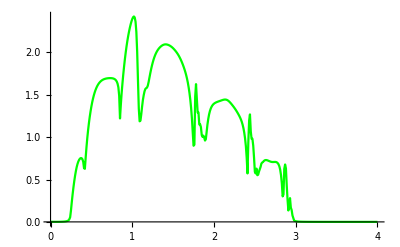

```mathematica
ListPlot[final3,Joined->True,PlotStyle->Green]
```

```mathematica
final2=(final+(m+n+o+p+q+r)/6)/2
```

{{0.,0.00115604},{0.01,0.000928172},{0.02,0.000751011},{0.03,0.000624009},{0.04,0.000540546},{0.05,0.000497778},{0.06,0.000493067},{0.07,0.000523862},{0.08,0.000591132},{0.09,0.000698139},{0.1,0.000847859},{0.11,0.00104673},{0.12,0.00130387},{0.13,0.0016311},{0.14,0.00204579},{0.15,0.00257279},{0.16,0.0032484},{0.17,0.00412731},{0.18,0.00529548},{0.19,0.00689622},{0.2,0.00918875},{0.21,0.0127031},{0.22,0.0187744},{0.23,0.0327479},{0.24,0.0526431},{0.25,0.137291},{0.26,0.234603},{0.27,0.324551},{0.28,0.406247},{0.29,0.479991},{0.3,0.545959},{0.31,0.603523},{0.32,0.652117},{0.33,0.691748},{0.34,0.722706},{0.35,0.745407},{0.36,0.760129},{0.37,0.766704},{0.38,0.763994},{0.39,0.74861},{0.4,0.711506},{0.41,0.632725},{0.42,0.626137},{0.43,0.746079},{0.44,0.869358},{0.45,0.980151},{0.46,1.07438},{0.47,1.15632},{0.48,1.22844},{0.49,1.29228},{0.5,1.34885},{0.51,1.39889},{0.52,1.44298},{0.53,1.48161},{0.54,1.51524},{0.55,1.54432},{0.56,1.56932},{0.57,1.59068},{0.58,1.60883},{0.59,1.62419},{0.6,1.63711},{0.61,1.64791},{0.62,1.65689},{0.63,1.66428},{0.64,1.67031},{0.65,1.67516},{0.66,1.679},{0.67,1.68196},{0.68,1.6842},{0.69,1.68582},{0.7,1.68691},{0.71,1.68754},{0.72,1.68774},{0.73,1.68751},{0.74,1.68683},{0.75,1.6856},{0.76,1.6837},{0.77,1.6809},{0.78,1.67685},{0.79,1.67099},{0.8,1.66232},{0.81,1.64903},{0.82,1.62745},{0.83,1.58862},{0.84,1.50156},{0.85,1.27236},{0.86,1.40502},{0.87,1.52848},{0.88,1.63686},{0.89,1.73546},{0.9,1.82627},{0.91,1.91011},{0.92,1.98732},{0.93,2.05801},{0.94,2.12224},{0.95,2.18026},{0.96,2.23245},{0.97,2.27927},{0.98,2.32103},{0.99,2.35765},{1.,2.38834},{1.01,2.41114},{1.02,2.42196},{1.03,2.4124},{1.04,2.36498},{1.05,2.24558},{1.06,2.00748},{1.07,1.65725},{1.08,1.34234},{1.09,1.19613},{1.1,1.21252},{1.11,1.28039},{1.12,1.36281},{1.13,1.43777},{1.14,1.4965},{1.15,1.54173},{1.16,1.57283},{1.17,1.59148},{1.18,1.60028},{1.19,1.61885},{1.2,1.65515},{1.21,1.69988},{1.22,1.74443},{1.23,1.78503},{1.24,1.82187},{1.25,1.85614},{1.26,1.88785},{1.27,1.91687},{1.28,1.94321},{1.29,1.96693},{1.3,1.98828},{1.31,2.00754},{1.32,2.02498},{1.33,2.04081},{1.34,2.05513},{1.35,2.06794},{1.36,2.07915},{1.37,2.08858},{1.38,2.09597},{1.39,2.10108},{1.4,2.10371},{1.41,2.10377},{1.42,2.10131},{1.43,2.0965},{1.44,2.08957},{1.45,2.08077},{1.46,2.07036},{1.47,2.05856},{1.48,2.04566},{1.49,2.03197},{1.5,2.01781},{1.51,2.00349},{1.52,1.98921},{1.53,1.97501},{1.54,1.96077},{1.55,1.9462},{1.56,1.93093},{1.57,1.91462},{1.58,1.89702},{1.59,1.878},{1.6,1.85758},{1.61,1.83578},{1.62,1.81258},{1.63,1.78781},{1.64,1.76108},{1.65,1.7318},{1.66,1.69909},{1.67,1.6618},{1.68,1.61839},{1.69,1.5671},{1.7,1.50808},{1.71,1.43837},{1.72,1.35183},{1.73,1.25102},{1.74,1.1212},{1.75,0.99506},{1.76,0.93059},{1.77,1.47117},{1.78,1.57567},{1.79,1.52838},{1.8,1.26988},{1.81,1.21956},{1.82,1.18247},{1.83,1.12717},{1.84,1.05618},{1.85,0.962248},{1.86,0.949822},{1.87,0.980347},{1.88,0.965206},{1.89,0.993203},{1.9,1.04422},{1.91,1.12181},{1.92,1.20696},{1.93,1.26694},{1.94,1.31245},{1.95,1.34401},{1.96,1.36582},{1.97,1.38069},{1.98,1.39056},{1.99,1.39685},{2.,1.4006},{2.01,1.40258},{2.02,1.40334},{2.03,1.40327},{2.04,1.40268},{2.05,1.4018},{2.06,1.40085},{2.07,1.40002},{2.08,1.39946},{2.09,1.39929},{2.1,1.39952},{2.11,1.40007},{2.12,1.40073},{2.13,1.40122},{2.14,1.40118},{2.15,1.40023},{2.16,1.39804},{2.17,1.39444},{2.18,1.38945},{2.19,1.3833},{2.2,1.37637},{2.21,1.36905},{2.22,1.36163},{2.23,1.35429},{2.24,1.34709},{2.25,1.33997},{2.26,1.33279},{2.27,1.32538},{2.28,1.31758},{2.29,1.3092},{2.3,1.2999},{2.31,1.28904},{2.32,1.27563},{2.33,1.25836},{2.34,1.23573},{2.35,1.2064},{2.36,1.16875},{2.37,1.11902},{2.38,1.04926},{2.39,0.948328},{2.4,0.792779},{2.41,0.54947},{2.42,1.07922},{2.43,1.34759},{2.44,1.37372},{2.45,1.11367},{2.46,0.95122},{2.47,0.922832},{2.48,0.852701},{2.49,0.741233},{2.5,0.589708},{2.51,0.603901},{2.52,0.629628},{2.53,0.561548},{2.54,0.595113},{2.55,0.629717},{2.56,0.632187},{2.57,0.648919},{2.58,0.694369},{2.59,0.693207},{2.6,0.689993},{2.61,0.704449},{2.62,0.715173},{2.63,0.72128},{2.64,0.72409},{2.65,0.72455},{2.66,0.723443},{2.67,0.721425},{2.68,0.719031},{2.69,0.716665},{2.7,0.714598},{2.71,0.712948},{2.72,0.711635},{2.73,0.710317},{2.74,0.708328},{2.75,0.704682},{2.76,0.698136},{2.77,0.687301},{2.78,0.671008},{2.79,0.648425},{2.8,0.61718},{2.81,0.571355},{2.82,0.50316},{2.83,0.407121},{2.84,0.255665},{2.85,0.307887},{2.86,0.706087},{2.87,0.733663},{2.88,0.644497},{2.89,0.426955},{2.9,0.295618},{2.91,0.144317},{2.92,0.199539},{2.93,0.202365},{2.94,0.159887},{2.95,0.13302},{2.96,0.0571374},{2.97,0.070676},{2.98,0.0194562},{2.99,0.0108406},{3.,0.0078144},{3.01,0.00742356},{3.02,0.00531549},{3.03,0.00403425},{3.04,0.00332845},{3.05,0.00280206},{3.06,0.00238833},{3.07,0.00205503},{3.08,0.00178204},{3.09,0.00155558},{3.1,0.00136576},{3.11,0.00120525},{3.12,0.00106846},{3.13,0.000951117},{3.14,0.00084984},{3.15,0.000761958},{3.16,0.000685325},{3.17,0.000618202},{3.18,0.000559165},{3.19,0.000507045},{3.2,0.000460869},{3.21,0.000419826},{3.22,0.000383237},{3.23,0.000350523},{3.24,0.000321195},{3.25,0.000294836},{3.26,0.00027109},{3.27,0.00024965},{3.28,0.000230251},{3.29,0.000212663},{3.3,0.000196686},{3.31,0.000182147},{3.32,0.000168893},{3.33,0.000156791},{3.34,0.000145723},{3.35,0.000135585},{3.36,0.000126286},{3.37,0.000117745},{3.38,0.000109889},{3.39,0.000102653},{3.4,0.0000959817},{3.41,0.0000898226},{3.42,0.0000841301},{3.43,0.000078863},{3.44,0.0000739844},{3.45,0.0000694609},{3.46,0.0000652626},{3.47,0.0000613622},{3.48,0.0000577353},{3.49,0.0000543597},{3.5,0.0000512152},{3.51,0.0000482834},{3.52,0.0000455479},{3.53,0.0000429933},{3.54,0.0000406058},{3.55,0.0000383729},{3.56,0.000036283},{3.57,0.0000343256},{3.58,0.0000324909},{3.59,0.0000307702},{3.6,0.0000291553},{3.61,0.0000276387},{3.62,0.0000262135},{3.63,0.0000248746},{3.64,0.0000236168},{3.65,0.0000224351},{3.66,0.000021322},{3.67,0.0000202729},{3.68,0.0000192839},{3.69,0.0000183508},{3.7,0.00001747},{3.71,0.000016638},{3.72,0.0000158517},{3.73,0.0000151086},{3.74,0.0000144058},{3.75,0.0000137407},{3.76,0.0000131109},{3.77,0.0000125143},{3.78,0.0000119489},{3.79,0.0000114129},{3.8,0.0000109045},{3.81,0.0000104221},{3.82,9.96422×10^-6},{3.83,9.52938×10^-6},{3.84,9.11629×10^-6},{3.85,8.72371×10^-6},{3.86,8.35049×10^-6},{3.87,7.99554×10^-6},{3.88,7.65785×10^-6},{3.89,7.33647×10^-6},{3.9,7.03079×10^-6},{3.91,6.73985×10^-6},{3.92,6.46278×10^-6},{3.93,6.19929×10^-6},{3.94,5.94963×10^-6},{3.95,5.71248×10^-6},{3.96,5.48632×10^-6},{3.97,5.2704×10^-6},{3.98,5.06421×10^-6},{3.99,4.86724×10^-6},{4.,4.67902×10^-6}}

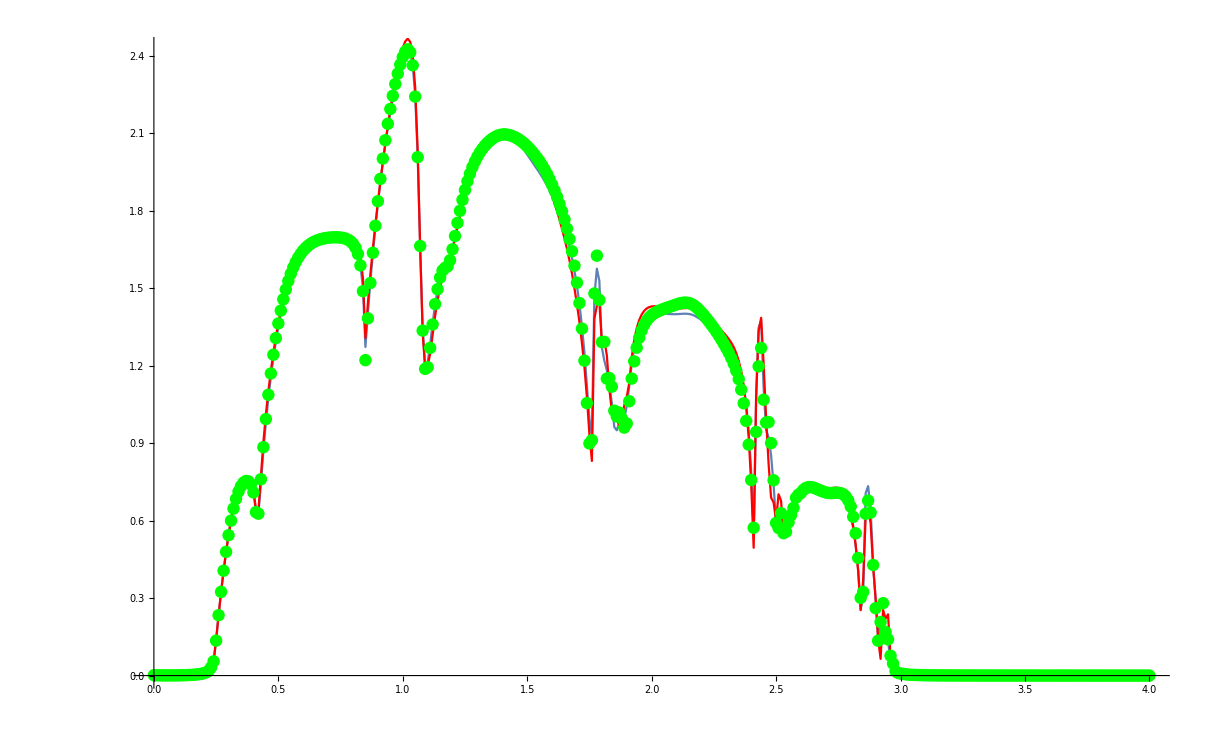

```mathematica
Show[ListPlot[final2,Joined->True],ListPlot[final,Joined->True,PlotStyle->Red],ListPlot[final3,Joined->False,PlotStyle->Green]]
```

```mathematica
final=(m+n+o+p+q+r)/6
```

{{0.,0.00130684},{0.01,0.00107827},{0.02,0.000900752},{0.03,0.000772939},{0.04,0.000688731},{0.05,0.000645488},{0.06,0.000638587},{0.07,0.000665998},{0.08,0.000730757},{0.09,0.000835125},{0.1,0.000980457},{0.11,0.00117459},{0.12,0.00142641},{0.13,0.00174751},{0.14,0.00215513},{0.15,0.00267401},{0.16,0.00334035},{0.17,0.00420884},{0.18,0.00536579},{0.19,0.00695552},{0.2,0.00924036},{0.21,0.0127593},{0.22,0.018879},{0.23,0.0331357},{0.24,0.0554645},{0.25,0.139302},{0.26,0.234042},{0.27,0.323108},{0.28,0.404171},{0.29,0.477376},{0.3,0.543262},{0.31,0.600945},{0.32,0.649583},{0.33,0.689244},{0.34,0.720295},{0.35,0.743216},{0.36,0.758331},{0.37,0.765533},{0.38,0.763834},{0.39,0.750218},{0.4,0.717908},{0.41,0.643873},{0.42,0.637022},{0.43,0.770414},{0.44,0.904274},{0.45,1.01156},{0.46,1.10187},{0.47,1.18013},{0.48,1.24916},{0.49,1.31072},{0.5,1.36588},{0.51,1.41527},{0.52,1.45929},{0.53,1.49818},{0.54,1.53219},{0.55,1.56163},{0.56,1.58687},{0.57,1.60832},{0.58,1.62643},{0.59,1.64161},{0.6,1.65426},{0.61,1.66474},{0.62,1.67336},{0.63,1.6804},{0.64,1.68613},{0.65,1.69077},{0.66,1.6945},{0.67,1.69751},{0.68,1.69991},{0.69,1.70181},{0.7,1.70329},{0.71,1.70437},{0.72,1.70508},{0.73,1.70539},{0.74,1.70527},{0.75,1.70465},{0.76,1.7034},{0.77,1.70132},{0.78,1.69812},{0.79,1.69328},{0.8,1.68589},{0.81,1.67429},{0.82,1.65501},{0.83,1.61954},{0.84,1.53835},{0.85,1.30666},{0.86,1.44267},{0.87,1.55552},{0.88,1.65515},{0.89,1.74675},{0.9,1.83242},{0.91,1.91317},{0.92,1.98945},{0.93,2.0614},{0.94,2.12895},{0.95,2.192},{0.96,2.25045},{0.97,2.30414},{0.98,2.35271},{0.99,2.39537},{1.,2.43064},{1.01,2.45585},{1.02,2.46636},{1.03,2.45373},{1.04,2.40128},{1.05,2.27695},{1.06,2.03246},{1.07,1.65369},{1.08,1.32795},{1.09,1.19011},{1.1,1.19945},{1.11,1.24572},{1.12,1.31902},{1.13,1.39176},{1.14,1.45371},{1.15,1.50344},{1.16,1.5399},{1.17,1.56305},{1.18,1.57774},{1.19,1.60267},{1.2,1.64516},{1.21,1.69221},{1.22,1.73652},{1.23,1.77727},{1.24,1.8145},{1.25,1.84838},{1.26,1.8791},{1.27,1.90691},{1.28,1.9321},{1.29,1.95499},{1.3,1.97587},{1.31,1.995},{1.32,2.01257},{1.33,2.02869},{1.34,2.04342},{1.35,2.05674},{1.36,2.06859},{1.37,2.07886},{1.38,2.08743},{1.39,2.09416},{1.4,2.09892},{1.41,2.10155},{1.42,2.10193},{1.43,2.09996},{1.44,2.09562},{1.45,2.08901},{1.46,2.08035},{1.47,2.06997},{1.48,2.05828},{1.49,2.0457},{1.5,2.03261},{1.51,2.01928},{1.52,2.00579},{1.53,1.99207},{1.54,1.97783},{1.55,1.96265},{1.56,1.94605},{1.57,1.92754},{1.58,1.90677},{1.59,1.88347},{1.6,1.85755},{1.61,1.82906},{1.62,1.79814},{1.63,1.76498},{1.64,1.72968},{1.65,1.69212},{1.66,1.6517},{1.67,1.60717},{1.68,1.55682},{1.69,1.49911},{1.7,1.43725},{1.71,1.36911},{1.72,1.2878},{1.73,1.19528},{1.74,1.07658},{1.75,0.934785},{1.76,0.831001},{1.77,1.38207},{1.78,1.43249},{1.79,1.4467},{1.8,1.29135},{1.81,1.29847},{1.82,1.24002},{1.83,1.11104},{1.84,1.02452},{1.85,1.00613},{1.86,0.988523},{1.87,0.970034},{1.88,0.97641},{1.89,1.04621},{1.9,1.07903},{1.91,1.13325},{1.92,1.23189},{1.93,1.29921},{1.94,1.34483},{1.95,1.3764},{1.96,1.398},{1.97,1.41237},{1.98,1.42148},{1.99,1.42679},{2.,1.4294},{2.01,1.43012},{2.02,1.42958},{2.03,1.42825},{2.04,1.42651},{2.05,1.42464},{2.06,1.42292},{2.07,1.42155},{2.08,1.42067},{2.09,1.42035},{2.1,1.42056},{2.11,1.42119},{2.12,1.42203},{2.13,1.4228},{2.14,1.42323},{2.15,1.42304},{2.16,1.42201},{2.17,1.41999},{2.18,1.4169},{2.19,1.41272},{2.2,1.4075},{2.21,1.40127},{2.22,1.39408},{2.23,1.38602},{2.24,1.37722},{2.25,1.36784},{2.26,1.35802},{2.27,1.34787},{2.28,1.33743},{2.29,1.32664},{2.3,1.31533},{2.31,1.30308},{2.32,1.28903},{2.33,1.27165},{2.34,1.24873},{2.35,1.21806},{2.36,1.17756},{2.37,1.12219},{2.38,1.04145},{2.39,0.922833},{2.4,0.744605},{2.41,0.495019},{2.42,1.08366},{2.43,1.33403},{2.44,1.38547},{2.45,1.20719},{2.46,0.997116},{2.47,0.819561},{2.48,0.689139},{2.49,0.67097},{2.5,0.600294},{2.51,0.70224},{2.52,0.677247},{2.53,0.54665},{2.54,0.572993},{2.55,0.571305},{2.56,0.604218},{2.57,0.638815},{2.58,0.662258},{2.59,0.679439},{2.6,0.696713},{2.61,0.708952},{2.62,0.717151},{2.63,0.722128},{2.64,0.724653},{2.65,0.725465},{2.66,0.725229},{2.67,0.724512},{2.68,0.723769},{2.69,0.723348},{2.7,0.723487},{2.71,0.724278},{2.72,0.725604},{2.73,0.727047},{2.74,0.727798},{2.75,0.726596},{2.76,0.721677},{2.77,0.710815},{2.78,0.69222},{2.79,0.665491},{2.8,0.629266},{2.81,0.578223},{2.82,0.50491},{2.83,0.404787},{2.84,0.253358},{2.85,0.37024},{2.86,0.613638},{2.87,0.639621},{2.88,0.590762},{2.89,0.422053},{2.9,0.298453},{2.91,0.143629},{2.92,0.0646498},{2.93,0.253942},{2.94,0.219721},{2.95,0.237195},{2.96,0.0694645},{2.97,0.0848372},{2.98,0.0184363},{2.99,0.0114137},{3.,0.00842328},{3.01,0.00926356},{3.02,0.00613525},{3.03,0.00436402},{3.04,0.00355456},{3.05,0.0029738},{3.06,0.00252433},{3.07,0.00216541},{3.08,0.00187322},{3.09,0.00163196},{3.1,0.00143047},{3.11,0.0012606},{3.12,0.00111622},{3.13,0.000992627},{3.14,0.000886158},{3.15,0.000793922},{3.16,0.000713606},{3.17,0.000643345},{3.18,0.000581617},{3.19,0.000527174},{3.2,0.000478982},{3.21,0.00043618},{3.22,0.000398051},{3.23,0.000363982},{3.24,0.000333455},{3.25,0.000306032},{3.26,0.000281338},{3.27,0.000259051},{3.28,0.000238892},{3.29,0.00022062},{3.3,0.000204028},{3.31,0.000188932},{3.32,0.000175173},{3.33,0.000162613},{3.34,0.000151128},{3.35,0.000140609},{3.36,0.000130963},{3.37,0.000122103},{3.38,0.000113954},{3.39,0.000106451},{3.4,0.0000995328},{3.41,0.0000931465},{3.42,0.0000872443},{3.43,0.0000817835},{3.44,0.0000767257},{3.45,0.0000720362},{3.46,0.0000676839},{3.47,0.0000636406},{3.48,0.0000598809},{3.49,0.0000563817},{3.5,0.000053122},{3.51,0.000050083},{3.52,0.0000472472},{3.53,0.0000445991},{3.54,0.0000421242},{3.55,0.0000398095},{3.56,0.000037643},{3.57,0.0000356138},{3.58,0.0000337118},{3.59,0.0000319279},{3.6,0.0000302536},{3.61,0.0000286813},{3.62,0.0000272036},{3.63,0.0000258154},{3.64,0.0000245108},{3.65,0.0000232849},{3.66,0.0000221301},{3.67,0.0000210417},{3.68,0.0000200156},{3.69,0.0000190475},{3.7,0.0000181339},{3.71,0.0000172708},{3.72,0.0000164552},{3.73,0.0000156847},{3.74,0.0000149561},{3.75,0.0000142665},{3.76,0.0000136135},{3.77,0.0000129949},{3.78,0.0000124086},{3.79,0.0000118527},{3.8,0.0000113255},{3.81,0.0000108252},{3.82,0.0000103502},{3.83,9.89919×10^-6},{3.84,9.47068×10^-6},{3.85,9.06343×10^-6},{3.86,8.67624×10^-6},{3.87,8.30798×10^-6},{3.88,7.95761×10^-6},{3.89,7.62415×10^-6},{3.9,7.30726×10^-6},{3.91,7.00542×10^-6},{3.92,6.71783×10^-6},{3.93,6.4443×10^-6},{3.94,6.18506×10^-6},{3.95,5.93864×10^-6},{3.96,5.70358×10^-6},{3.97,5.47917×10^-6},{3.98,5.26485×10^-6},{3.99,5.06012×10^-6},{4.,4.8645×10^-6}}

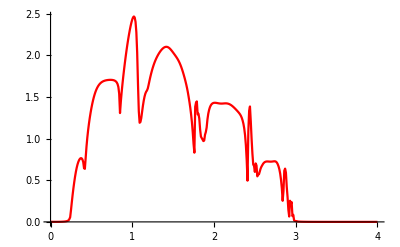

```mathematica
ListPlot[final,Joined->True,PlotStyle->Red]
```

```mathematica
final[[51,1]]
```

0.5

```mathematica
final[[51,2]]
```

1.36588

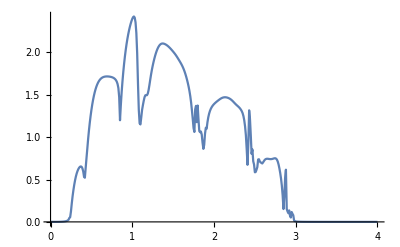

```mathematica
ListPlot[final,Joined->True]
```

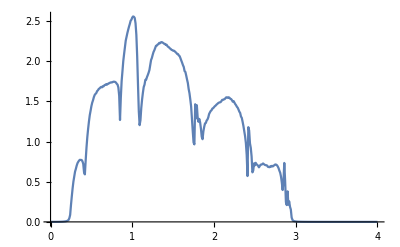

```mathematica
ListPlot[final,Joined->True]
```

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis53.csv",final3]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis53.csv

```mathematica
Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis53.csv"]
```

{{0.,0.0000303359},{0.01,0.0000293404},{0.02,0.0000268116},{0.03,0.0000214571},{0.04,0.0000210531},{0.05,0.0000296004},{0.06,0.0000434305},{0.07,0.0000687331},{0.08,0.000107825},{0.09,0.000149756},{0.1,0.000205233},{0.11,0.000279147},{0.12,0.000362771},{0.13,0.000474888},{0.14,0.000614332},{0.15,0.000801013},{0.16,0.00104116},{0.17,0.00140854},{0.18,0.00184016},{0.19,0.00255585},{0.2,0.00363732},{0.21,0.00546067},{0.22,0.00920266},{0.23,0.02086},{0.24,0.345503},{0.25,0.637246},{0.26,0.761945},{0.27,0.831783},{0.28,0.871561},{0.29,0.900215},{0.3,0.917242},{0.31,0.930834},{0.32,0.938117},{0.33,0.943668},{0.34,0.946438},{0.35,0.948715},{0.36,0.948426},{0.37,0.945977},{0.38,0.941319},{0.39,0.929487},{0.4,0.907124},{0.41,0.824706},{0.42,1.08103},{0.43,1.46201},{0.44,1.63221},{0.45,1.72621},{0.46,1.78181},{0.47,1.8271},{0.48,1.85479},{0.49,1.87554},{0.5,1.89043},{0.51,1.9024},{0.52,1.91276},{0.53,1.91573},{0.54,1.9244},{0.55,1.92725},{0.56,1.93088},{0.57,1.93369},{0.58,1.93296},{0.59,1.93645},{0.6,1.93723},{0.61,1.93961},{0.62,1.93899},{0.63,1.94077},{0.64,1.93908},{0.65,1.94184},{0.66,1.94032},{0.67,1.94045},{0.68,1.94215},{0.69,1.94327},{0.7,1.94384},{0.71,1.94307},{0.72,1.94378},{0.73,1.94448},{0.74,1.94495},{0.75,1.94363},{0.76,1.94352},{0.77,1.94197},{0.78,1.94},{0.79,1.93707},{0.8,1.9337},{0.81,1.92698},{0.82,1.91585},{0.83,1.89445},{0.84,1.83073},{0.85,1.69738},{0.86,2.21493},{0.87,2.44649},{0.88,2.57734},{0.89,2.66067},{0.9,2.71799},{0.91,2.75545},{0.92,2.77717},{0.93,2.80435},{0.94,2.81996},{0.95,2.83335},{0.96,2.84345},{0.97,2.84802},{0.98,2.86179},{0.99,2.86989},{1.,2.87624},{1.01,2.87588},{1.02,2.83131},{1.03,2.49991},{1.04,1.74584},{1.05,2.37033},{1.06,2.50366},{1.07,2.41415},{1.08,2.33824},{1.09,2.51717},{1.1,2.61993},{1.11,2.68781},{1.12,2.72314},{1.13,2.74939},{1.14,2.76435},{1.15,2.78152},{1.16,2.79322},{1.17,2.80107},{1.18,2.81049},{1.19,2.81409},{1.2,2.82197},{1.21,2.8227},{1.22,2.82738},{1.23,2.83175},{1.24,2.83306},{1.25,2.83193},{1.26,2.83408},{1.27,2.83063},{1.28,2.83309},{1.29,2.83467},{1.3,2.83526},{1.31,2.83348},{1.32,2.83517},{1.33,2.83356},{1.34,2.83249},{1.35,2.83169},{1.36,2.8293},{1.37,2.8295},{1.38,2.82978},{1.39,2.83071},{1.4,2.83147},{1.41,2.83225},{1.42,2.83156},{1.43,2.83216},{1.44,2.83359},{1.45,2.83195},{1.46,2.83209},{1.47,2.83103},{1.48,2.82845},{1.49,2.82971},{1.5,2.82659},{1.51,2.82093},{1.52,2.81933},{1.53,2.81215},{1.54,2.80647},{1.55,2.79487},{1.56,2.78606},{1.57,2.77652},{1.58,2.76333},{1.59,2.75201},{1.6,2.73913},{1.61,2.72387},{1.62,2.72047},{1.63,2.70445},{1.64,2.69286},{1.65,2.6863},{1.66,2.67427},{1.67,2.66774},{1.68,2.65927},{1.69,2.64675},{1.7,2.63422},{1.71,2.61233},{1.72,2.57585},{1.73,2.52025},{1.74,2.44906},{1.75,2.29833},{1.76,1.79769},{1.77,1.1494},{1.78,2.4544},{1.79,2.01411},{1.8,1.59909},{1.81,1.67773},{1.82,1.80147},{1.83,1.8451},{1.84,1.86983},{1.85,1.88412},{1.86,1.89252},{1.87,1.89825},{1.88,1.90052},{1.89,1.9027},{1.9,1.90567},{1.91,1.90649},{1.92,1.90596},{1.93,1.90911},{1.94,1.90781},{1.95,1.91011},{1.96,1.91073},{1.97,1.91208},{1.98,1.91238},{1.99,1.91356},{2.,1.91543},{2.01,1.91705},{2.02,1.91797},{2.03,1.9184},{2.04,1.91997},{2.05,1.91901},{2.06,1.92134},{2.07,1.92001},{2.08,1.92156},{2.09,1.92076},{2.1,1.91996},{2.11,1.91791},{2.12,1.91833},{2.13,1.9157},{2.14,1.91283},{2.15,1.90854},{2.16,1.90891},{2.17,1.90523},{2.18,1.90274},{2.19,1.90084},{2.2,1.89496},{2.21,1.89306},{2.22,1.89182},{2.23,1.89095},{2.24,1.88973},{2.25,1.89226},{2.26,1.88956},{2.27,1.89046},{2.28,1.89001},{2.29,1.89112},{2.3,1.88702},{2.31,1.88244},{2.32,1.87329},{2.33,1.8643},{2.34,1.85207},{2.35,1.83279},{2.36,1.81241},{2.37,1.79048},{2.38,1.76627},{2.39,1.7323},{2.4,1.64944},{2.41,1.27357},{2.42,0.812343},{2.43,1.44208},{2.44,1.23675},{2.45,1.00114},{2.46,0.881926},{2.47,0.927078},{2.48,0.943058},{2.49,0.949436},{2.5,0.955283},{2.51,0.956793},{2.52,0.957444},{2.53,0.957639},{2.54,0.957526},{2.55,0.956048},{2.56,0.954208},{2.57,0.952488},{2.58,0.950609},{2.59,0.94913},{2.6,0.948492},{2.61,0.948082},{2.62,0.94862},{2.63,0.948466},{2.64,0.949917},{2.65,0.950571},{2.66,0.950314},{2.67,0.952612},{2.68,0.954648},{2.69,0.957538},{2.7,0.959829},{2.71,0.960934},{2.72,0.962285},{2.73,0.961082},{2.74,0.957526},{2.75,0.955049},{2.76,0.948232},{2.77,0.939308},{2.78,0.929608},{2.79,0.919351},{2.8,0.909146},{2.81,0.896706},{2.82,0.885788},{2.83,0.862534},{2.84,0.751213},{2.85,0.053209},{2.86,0.267304},{2.87,0.0955861},{2.88,0.0404004},{2.89,0.00821923},{2.9,0.00446633},{2.91,0.00294419},{2.92,0.00216925},{2.93,0.00162724},{2.94,0.00121172},{2.95,0.000968191},{2.96,0.000785073},{2.97,0.000646786},{2.98,0.000560901},{2.99,0.000473577},{3.,0.000386837},{3.01,0.000355171},{3.02,0.00028881},{3.03,0.000250652},{3.04,0.00022034},{3.05,0.000193363},{3.06,0.000178656},{3.07,0.000158706},{3.08,0.000135935},{3.09,0.000126679},{3.1,0.00010922},{3.11,0.0000983587},{3.12,0.0000950849},{3.13,0.0000838001},{3.14,0.0000728335},{3.15,0.0000692535},{3.16,0.0000605079},{3.17,0.0000577922},{3.18,0.0000529485},{3.19,0.0000500366},{3.2,0.0000428017},{3.21,0.0000423899},{3.22,0.0000379569},{3.23,0.0000350609},{3.24,0.0000310782},{3.25,0.0000300436},{3.26,0.000028734},{3.27,0.0000248212},{3.28,0.0000230624},{3.29,0.0000214777},{3.3,0.0000200047},{3.31,0.0000186647},{3.32,0.0000187561},{3.33,0.0000175313},{3.34,0.0000152323},{3.35,0.0000148696},{3.36,0.0000133626},{3.37,0.0000125392},{3.38,0.0000122667},{3.39,0.0000110517},{3.4,0.0000103908},{3.41,9.77647×10^-6},{3.42,9.20493×10^-6},{3.43,8.6927×10^-6},{3.44,8.19782×10^-6},{3.45,7.74544×10^-6},{3.46,7.62993×10^-6},{3.47,7.21622×10^-6},{3.48,6.55637×10^-6},{3.49,6.2151×10^-6},{3.5,6.12602×10^-6},{3.51,5.80688×10^-6},{3.52,5.29156×10^-6},{3.53,5.02639×10^-6},{3.54,5.13392×10^-6},{3.55,4.71242×10^-6},{3.56,4.30606×10^-6},{3.57,4.09789×10^-6},{3.58,3.89848×10^-6},{3.59,3.7077×10^-6},{3.6,3.53047×10^-6},{3.61,3.61706×10^-6},{3.62,3.20731×10^-6},{3.63,3.05575×10^-6},{3.64,2.91453×10^-6},{3.65,2.88704×10^-6},{3.66,2.65448×10^-6},{3.67,2.53475×10^-6},{3.68,2.42276×10^-6},{3.69,2.48531×10^-6},{3.7,2.21312×10^-6},{3.71,2.27116×10^-6},{3.72,2.02448×10^-6},{3.73,2.07831×10^-6},{3.74,1.85444×10^-6},{3.75,1.83886×10^-6},{3.76,1.70009×10^-6},{3.77,1.62978×10^-6},{3.78,1.5621×10^-6},{3.79,1.5497×10^-6},{3.8,1.43638×10^-6},{3.81,1.37738×10^-6},{3.82,1.36742×10^-6},{3.83,1.26879×10^-6},{3.84,1.30484×10^-6},{3.85,1.25297×10^-6},{3.86,1.12457×10^-6},{3.87,1.08069×10^-6},{3.88,1.11122×10^-6},{3.89,9.98417×10^-7},{3.9,1.02709×10^-6},{3.91,9.87819×10^-7},{3.92,9.17447×10^-7},{3.93,8.55767×10^-7},{3.94,8.23587×10^-7},{3.95,7.93319×10^-7},{3.96,7.6387×10^-7},{3.97,7.58687×10^-7},{3.98,7.09155×10^-7},{3.99,7.0432×10^-7},{4.,6.59153×10^-7}}

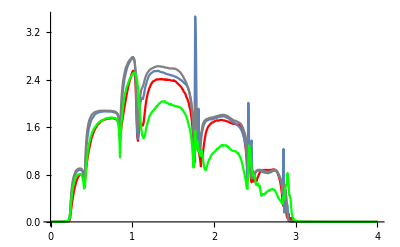

```mathematica
Show[ListLinePlot[Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"],PlotStyle->Red],ListLinePlot[Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis55.csv"]],ListLinePlot[Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis45.csv"],PlotStyle->Gray],ListLinePlot[Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis310.csv"],PlotStyle->Green],PlotRange->All]
```

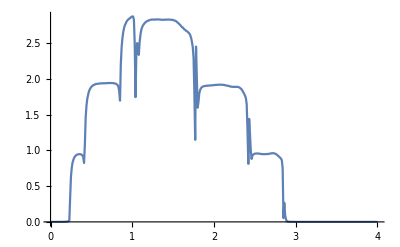

```mathematica
ListPlot[%188,Joined->True]
```

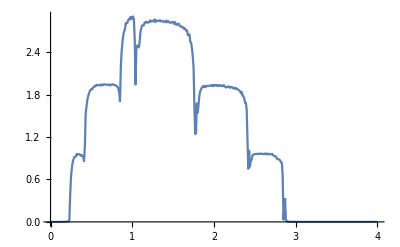
```mathematica
ListPlot[final,Joined->True]
-Graphics-
G[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:=Inverse[{{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ3+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ2+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ3+ω,-t},{0,0,0,0,0,-t,ⅈ δ+ω-ϵ}}]
Gnew[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:= Inverse[IdentityMatrix[7]-G[ω,δ,t,ϵ,ϵ2,ϵ3].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].G[ω,δ,t,ϵ,ϵ2,ϵ3]
Ilb$[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:=Inverse[IdentityMatrix[7]-Gnew[ω,δ,t,ϵ,ϵ2,ϵ3].T1[t].SR[ω,δ,t,ϵ].T1[t]].Gnew[ω,δ,t,ϵ,ϵ2,ϵ3];
Irb$[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Gnew[ω,δ,t,ϵ,ϵ2,ϵ3].T1[t]].SR[ω,δ,t,ϵ];
gddb$[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:= Ilb$[ω,δ,t,ϵ,ϵ2,ϵ3]-ConjugateTranspose[Ilb$[ω,δ,t,ϵ,ϵ2,ϵ3]];
grrb$[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:= Irb$[ω,δ,t,ϵ,ϵ2,ϵ3]-ConjugateTranspose[Irb$[ω,δ,t,ϵ,ϵ2,ϵ3]];
Gnonlocalb$[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:= SR[ω,δ,t,ϵ].T1[t].Ilb$[ω,δ,t,ϵ,ϵ2,ϵ3];
GNONb$[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:= Gnonlocalb$[ω,δ,t,ϵ,ϵ2,ϵ3]-ConjugateTranspose[Gnonlocalb$[ω,δ,t,ϵ,ϵ2,ϵ3]];
trb[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:= If[Abs[Tr[gddb$[ω,δ,t,ϵ,ϵ2,ϵ3].T1[1].grrb$[ω,δ,t,ϵ,ϵ2,ϵ3].T1[1]-T1[1].GNONb$[ω,δ,t,ϵ,ϵ2,ϵ3].T1[1].GNONb$[ω,δ,t,ϵ,ϵ2,ϵ3]]]>3,3,Abs[Tr[gddb$[ω,δ,t,ϵ,ϵ2,ϵ3].T1[1].grrb$[ω,δ,t,ϵ,ϵ2,ϵ3].T1[1]-T1[1].GNONb$[ω,δ,t,ϵ,ϵ2,ϵ3].T1[1].GNONb$[ω,δ,t,ϵ,ϵ2,ϵ3]]]]
f[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{final[[1;;150]][[;;,1]],(Table[{ω,trb[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- final[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.49}]/150]
ρ3[b_]:=Table[{b,a,f[b,a]},{a,Range[-1,1,0.05]}]
ρ3[0]
{{0,-1.,0.0026296908807774025},{0,-0.95,0.0022794549516705572},{0,-0.9,0.0019236310372092319},{0,-0.85,0.0017442489348258572},{0,-0.8,0.0014585090753985914},{0,-0.75,0.0013524760496679857},{0,-0.7,0.0012274668250561284},{0,-0.6499999999999999,0.0008753107302299807},{0,-0.6,0.000671705833148486},{0,-0.55,0.0006520756864331448},{0,-0.5,0.00046316287569217907},{0,-0.44999999999999996,0.00034652909575010087},{0,-0.3999999999999999,0.0002858594306199369},{0,-0.35,0.0005104213687328427},{0,-0.29999999999999993,0.00035595206505438894},{0,-0.25,0.0003544631179850149},{0,-0.19999999999999996,0.00041845023088064474},{0,-0.1499999999999999,0.0005024211302716524},{0,-0.09999999999999998,0.0005798638004293558},{0,-0.04999999999999993,0.0006291063337924044},{0,0.,0.0006373694415947198},{0,0.050000000000000044,0.0006051027838766944},{0,0.10000000000000009,0.0005433396889855207},{0,0.15000000000000013,0.00046647608294560894},{0,0.20000000000000018,0.0003866732148278415},{0,0.25,0.00031224575082528997},{0,0.30000000000000004,0.0002485099653012634},{0,0.3500000000000001,0.00019910503248029519},{0,0.40000000000000013,0.00016688970760072463},{0,0.4500000000000002,0.0001543437197449361},{0,0.5,0.0001636685804460779},{0,0.55,0.00019676380923426873},{0,0.6000000000000001,0.00025515810380276533},{0,0.6500000000000001,0.00033996768490063224},{0,0.7000000000000002,0.00045187576434947127},{0,0.75,0.0005911363099665516},{0,0.8,0.0007575970327162726},{0,0.8500000000000001,0.0009507359307038894},{0,0.9000000000000001,0.0011697063707837552},{0,0.9500000000000002,0.0014133866256576908},{0,1.,0.001680430691927205}}
rr3=Join[ρ3[-1],ρ3[-9/10],ρ3[-4/5],ρ3[-7/10],ρ3[-3/5],ρ3[-1/2],ρ3[-2/5],ρ3[-3/10],ρ3[-1/5],ρ3[-1/10],ρ3[0],ρ3[1/10],ρ3[1/5],ρ3[3/10],ρ3[2/5],ρ3[1/2],ρ3[3/5],ρ3[7/10],ρ3[4/5],ρ3[9/10],ρ3[1]]
{{-1,-1.,0.002711104145640912},{-1,-0.95,0.002583314975230046},{-1,-0.9,0.0022745154341491177},{-1,-0.85,0.002212425595908854},{-1,-0.8,0.0018476016637077699},{-1,-0.75,0.001822279892712517},{-1,-0.7,0.001745592436104233},{-1,-0.6499999999999999,0.0015802379535794294},{-1,-0.6,0.0015719372142352563},{-1,-0.55,0.0014772833086679625},{-1,-0.5,0.0013066959820135758},{-1,-0.44999999999999996,0.0013957701902950026},{-1,-0.3999999999999999,0.0015036327768480917},{-1,-0.35,0.0016202480914160168},{-1,-0.29999999999999993,0.0017403200471920982},{-1,-0.25,0.001820721359072222},{-1,-0.19999999999999996,0.0018425672988462954},{-1,-0.1499999999999999,0.001537686476762184},{-1,-0.09999999999999998,0.0014664140257564019},{-1,-0.04999999999999993,0.001525770512452944},{-1,0.,0.0016190827781516915},{-1,0.050000000000000044,0.00163277380737494},{-1,0.10000000000000009,0.0016479777511457896},{-1,0.15000000000000013,0.0017280463804142223},{-1,0.20000000000000018,0.0019103652136699231},{-1,0.25,0.002316053527075605},{-1,0.30000000000000004,0.002728902663176024},{-1,0.3500000000000001,0.0029587968559119833},{-1,0.40000000000000013,0.003218001656603736},{-1,0.4500000000000002,0.003501428670034191},{-1,0.5,0.0038053356896613744},{-1,0.55,0.004054296000329998},{-1,0.6000000000000001,0.004025543939753613},{-1,0.6500000000000001,0.004193487649031039},{-1,0.7000000000000002,0.004457240556722017},{-1,0.75,0.0047746448995605656},{-1,0.8,0.005127906759720265},{-1,0.8500000000000001,0.005508108102401826},{-1,0.9000000000000001,0.0059098952554884916},{-1,0.9500000000000002,0.006329478569168207},{-1,1.,0.006758045031357713},{-9/10,-1.,0.002540441838746996},{-9/10,-0.95,0.002211110960414962},{-9/10,-0.9,0.0018783359047987648},{-9/10,-0.85,0.0017746405870995043},{-9/10,-0.8,0.0015321664869187397},{-9/10,-0.75,0.0014120028774413922},{-9/10,-0.7,0.0013057284742279058},{-9/10,-0.6499999999999999,0.0011832787471601105},{-9/10,-0.6,0.0010792850461577132},{-9/10,-0.55,0.000999373788902769},{-9/10,-0.5,0.0009079743085032502},{-9/10,-0.44999999999999996,0.0010444656184762007},{-9/10,-0.3999999999999999,0.0016580471709243731},{-9/10,-0.35,0.0015770197717109168},{-9/10,-0.29999999999999993,0.001013745392886284},{-9/10,-0.25,0.0010127811515575685},{-9/10,-0.19999999999999996,0.0010217338477384681},{-9/10,-0.1499999999999999,0.001065981090085497},{-9/10,-0.09999999999999998,0.0010907579223450035},{-9/10,-0.04999999999999993,0.0011629618628803847},{-9/10,0.,0.0012846570801953185},{-9/10,0.050000000000000044,0.0012992607474046256},{-9/10,0.10000000000000009,0.0013835887303104463},{-9/10,0.15000000000000013,0.001664596116949358},{-9/10,0.20000000000000018,0.0020655526149887015},{-9/10,0.25,0.002213449471078744},{-9/10,0.30000000000000004,0.002398891864992156},{-9/10,0.3500000000000001,0.0026164060302314145},{-9/10,0.40000000000000013,0.002644201625303776},{-9/10,0.4500000000000002,0.002670109676130997},{-9/10,0.5,0.0028494555942899704},{-9/10,0.55,0.0030873812404001253},{-9/10,0.6000000000000001,0.003323185543591019},{-9/10,0.6500000000000001,0.0035957850556361777},{-9/10,0.7000000000000002,0.003894587539684164},{-9/10,0.75,0.004217177461502388},{-9/10,0.8,0.004561813981426988},{-9/10,0.8500000000000001,0.004926539183240102},{-9/10,0.9000000000000001,0.005309433968773756},{-9/10,0.9500000000000002,0.005708550094331948},{-9/10,1.,0.0061055290174205044},{-4/5,-1.,0.0023338276784465504},{-4/5,-0.95,0.0021479524294856093},{-4/5,-0.9,0.0017439302768481385},{-4/5,-0.85,0.0016377579959221632},{-4/5,-0.8,0.0011861421889944066},{-4/5,-0.75,0.0010283922286788523},{-4/5,-0.7,0.0009000619431086497},{-4/5,-0.6499999999999999,0.000889396860180042},{-4/5,-0.6,0.0008405044412765378},{-4/5,-0.55,0.0007634323688585255},{-4/5,-0.5,0.0007510637988725875},{-4/5,-0.44999999999999996,0.0007500049039181094},{-4/5,-0.3999999999999999,0.0007751340347677354},{-4/5,-0.35,0.0006495067605932659},{-4/5,-0.29999999999999993,0.0005568909734350073},{-4/5,-0.25,0.0006288135585500586},{-4/5,-0.19999999999999996,0.0006667560515975687},{-4/5,-0.1499999999999999,0.0007226385591567455},{-4/5,-0.09999999999999998,0.0007980642668421465},{-4/5,-0.04999999999999993,0.0009005560506137809},{-4/5,0.,0.0010527069686674753},{-4/5,0.050000000000000044,0.0012056386644843855},{-4/5,0.10000000000000009,0.0016309206503101307},{-4/5,0.15000000000000013,0.0016726269564329593},{-4/5,0.20000000000000018,0.0017514048888197483},{-4/5,0.25,0.0014890011409115108},{-4/5,0.30000000000000004,0.0014987627829683844},{-4/5,0.3500000000000001,0.0016331422166403714},{-4/5,0.40000000000000013,0.0018278594048360777},{-4/5,0.4500000000000002,0.002056415991778324},{-4/5,0.5,0.0022900732916606033},{-4/5,0.55,0.0025507974489047966},{-4/5,0.6000000000000001,0.0028254399296688167},{-4/5,0.6500000000000001,0.0030871763538931},{-4/5,0.7000000000000002,0.0033756545012149516},{-4/5,0.75,0.0036888370012938478},{-4/5,0.8,0.004022322117318057},{-4/5,0.8500000000000001,0.00436547574518593},{-4/5,0.9000000000000001,0.004723206723466763},{-4/5,0.9500000000000002,0.005081005416726738},{-4/5,1.,0.005459372721405715},{-7/10,-1.,0.0023704569558033453},{-7/10,-0.95,0.002090199961895888},{-7/10,-0.9,0.0016703872076099151},{-7/10,-0.85,0.0015194702830359373},{-7/10,-0.8,0.0010535576334333911},{-7/10,-0.75,0.0008304084021112063},{-7/10,-0.7,0.0006746176138608534},{-7/10,-0.6499999999999999,0.0006221036419581638},{-7/10,-0.6,0.0006012320908126795},{-7/10,-0.55,0.0005246544981764359},{-7/10,-0.5,0.0005372770637306868},{-7/10,-0.44999999999999996,0.0005406032587173595},{-7/10,-0.3999999999999999,0.0006381528769806549},{-7/10,-0.35,0.0005858911525102732},{-7/10,-0.29999999999999993,0.0005808478303520719},{-7/10,-0.25,0.0005812184516832114},{-7/10,-0.19999999999999996,0.0006030411892900315},{-7/10,-0.1499999999999999,0.0006388438705756911},{-7/10,-0.09999999999999998,0.0006960543256619713},{-7/10,-0.04999999999999993,0.0007822124256266147},{-7/10,0.,0.0009981766117078965},{-7/10,0.050000000000000044,0.0010628038034987853},{-7/10,0.10000000000000009,0.0008987200420012239},{-7/10,0.15000000000000013,0.0008402336353133035},{-7/10,0.20000000000000018,0.0008723651257230414},{-7/10,0.25,0.0009678603604080915},{-7/10,0.30000000000000004,0.0011110727903825587},{-7/10,0.3500000000000001,0.001289581222370518},{-7/10,0.40000000000000013,0.0014931485567662842},{-7/10,0.4500000000000002,0.0016894901929311505},{-7/10,0.5,0.0019049368832750313},{-7/10,0.55,0.002143873471936296},{-7/10,0.6000000000000001,0.0024056175442120397},{-7/10,0.6500000000000001,0.0026893456253263078},{-7/10,0.7000000000000002,0.0029575170816492336},{-7/10,0.75,0.0032436034915115765},{-7/10,0.8,0.0035286468169796726},{-7/10,0.8500000000000001,0.003826868990315671},{-7/10,0.9000000000000001,0.004141572990292288},{-7/10,0.9500000000000002,0.004478944944638608},{-7/10,1.,0.0048364616014604025},{-3/5,-1.,0.00235260789932262},{-3/5,-0.95,0.0020640597314176856},{-3/5,-0.9,0.0015858880643562234},{-3/5,-0.85,0.001540993435729844},{-3/5,-0.8,0.0011128088104345785},{-3/5,-0.75,0.0008586612915576187},{-3/5,-0.7,0.0007053377821828594},{-3/5,-0.6499999999999999,0.00048400300925446963},{-3/5,-0.6,0.00033709276079281497},{-3/5,-0.55,0.0003129582827858489},{-3/5,-0.5,0.00030126289037412735},{-3/5,-0.44999999999999996,0.000286227043064681},{-3/5,-0.3999999999999999,0.00028745152687547016},{-3/5,-0.35,0.0002717562942509955},{-3/5,-0.29999999999999993,0.00031477042293209687},{-3/5,-0.25,0.00033883400493406703},{-3/5,-0.19999999999999996,0.00037833357591514187},{-3/5,-0.1499999999999999,0.00042449784207061406},{-3/5,-0.09999999999999998,0.0004898840829049233},{-3/5,-0.04999999999999993,0.0005634997812571755},{-3/5,0.,0.000644606789115516},{-3/5,0.050000000000000044,0.0007391043027505619},{-3/5,0.10000000000000009,0.0006772982711818098},{-3/5,0.15000000000000013,0.0006558822791274639},{-3/5,0.20000000000000018,0.0006831043861262596},{-3/5,0.25,0.000758946520248213},{-3/5,0.30000000000000004,0.0008761762915454525},{-3/5,0.3500000000000001,0.0010242045152636069},{-3/5,0.40000000000000013,0.0011932826270009413},{-3/5,0.4500000000000002,0.0013481528233653655},{-3/5,0.5,0.001526345021047382},{-3/5,0.55,0.0017094147519223296},{-3/5,0.6000000000000001,0.0019104946375287633},{-3/5,0.6500000000000001,0.002141544600545},{-3/5,0.7000000000000002,0.0023997737365731974},{-3/5,0.75,0.0026828998086394773},{-3/5,0.8,0.0029564185139919585},{-3/5,0.8500000000000001,0.00323568189836298},{-3/5,0.9000000000000001,0.0035392536964574976},{-3/5,0.9500000000000002,0.0038652190105713177},{-3/5,1.,0.004211518863509783},{-1/2,-1.,0.002156645211610254},{-1/2,-0.95,0.0018635476605400841},{-1/2,-0.9,0.0014843479985835878},{-1/2,-0.85,0.0014713733333784605},{-1/2,-0.8,0.0010879143414386386},{-1/2,-0.75,0.0007466569203998251},{-1/2,-0.7,0.0007023116301914631},{-1/2,-0.6499999999999999,0.0004967087751148677},{-1/2,-0.6,0.00035221307636771444},{-1/2,-0.55,0.00022489835171968838},{-1/2,-0.5,0.0001649988171110157},{-1/2,-0.44999999999999996,0.0001474677700739302},{-1/2,-0.3999999999999999,0.00019094963364199802},{-1/2,-0.35,0.00023570340093855067},{-1/2,-0.29999999999999993,0.00030085109172418905},{-1/2,-0.25,0.00032420446080197804},{-1/2,-0.19999999999999996,0.00035300231219183835},{-1/2,-0.1499999999999999,0.00037464232470694},{-1/2,-0.09999999999999998,0.0004080130534484584},{-1/2,-0.04999999999999993,0.00045158457875358135},{-1/2,0.,0.0005137833105025324},{-1/2,0.050000000000000044,0.0006077272446922364},{-1/2,0.10000000000000009,0.0005980068448808071},{-1/2,0.15000000000000013,0.0005361992079752193},{-1/2,0.20000000000000018,0.0005133882459140154},{-1/2,0.25,0.00051438920762183},{-1/2,0.30000000000000004,0.0005731398611637379},{-1/2,0.3500000000000001,0.0006714313050796515},{-1/2,0.40000000000000013,0.0007958461444529415},{-1/2,0.4500000000000002,0.0009388059152228901},{-1/2,0.5,0.0010902946360199282},{-1/2,0.55,0.0012620875749627585},{-1/2,0.6000000000000001,0.0014588788318529154},{-1/2,0.6500000000000001,0.0016789486584550223},{-1/2,0.7000000000000002,0.0019133014265761102},{-1/2,0.75,0.0021697375063911275},{-1/2,0.8,0.0024483545831745146},{-1/2,0.8500000000000001,0.00274867795392126},{-1/2,0.9000000000000001,0.003069779753613244},{-1/2,0.9500000000000002,0.0033773149954645734},{-1/2,1.,0.003696825314593746},{-2/5,-1.,0.0023538722337751745},{-2/5,-0.95,0.002106008471189261},{-2/5,-0.9,0.0022534898096246312},{-2/5,-0.85,0.0017682224520068775},{-2/5,-0.8,0.0011692820161619381},{-2/5,-0.75,0.000919359534089862},{-2/5,-0.7,0.0008337276158048295},{-2/5,-0.6499999999999999,0.0006116373806542767},{-2/5,-0.6,0.00035126042228111724},{-2/5,-0.55,0.00036856905287941305},{-2/5,-0.5,0.00019061401671170423},{-2/5,-0.44999999999999996,0.00014415750634916042},{-2/5,-0.3999999999999999,0.0001799300607877201},{-2/5,-0.35,0.00039823429711494893},{-2/5,-0.29999999999999993,0.000318933846298778},{-2/5,-0.25,0.0002568486898171772},{-2/5,-0.19999999999999996,0.00024763478620458895},{-2/5,-0.1499999999999999,0.0002730229966721503},{-2/5,-0.09999999999999998,0.0003027135397237314},{-2/5,-0.04999999999999993,0.0003326688902260132},{-2/5,0.,0.0003708446624446727},{-2/5,0.050000000000000044,0.0004314311870756018},{-2/5,0.10000000000000009,0.0005287403055086911},{-2/5,0.15000000000000013,0.00045025649000892076},{-2/5,0.20000000000000018,0.0003873962793909022},{-2/5,0.25,0.0003730805022760936},{-2/5,0.30000000000000004,0.00039940601855498425},{-2/5,0.3500000000000001,0.0004559916150095907},{-2/5,0.40000000000000013,0.0005349760984705677},{-2/5,0.4500000000000002,0.0006325929610876115},{-2/5,0.5,0.0007483652249596917},{-2/5,0.55,0.0008835779952987484},{-2/5,0.6000000000000001,0.0010400152326192082},{-2/5,0.6500000000000001,0.001219218682028116},{-2/5,0.7000000000000002,0.001422170304652226},{-2/5,0.75,0.0016492264216031829},{-2/5,0.8,0.0019001714671251391},{-2/5,0.8500000000000001,0.0021743145886758933},{-2/5,0.9000000000000001,0.0024705919992125958},{-2/5,0.9500000000000002,0.0027876602116051375},{-2/5,1.,0.0031239758905163353},{-3/10,-1.,0.002661441973971957},{-3/10,-0.95,0.002330335293881769},{-3/10,-0.9,0.0016212507439771645},{-3/10,-0.85,0.0013832089511828692},{-3/10,-0.8,0.0009350743151119465},{-3/10,-0.75,0.0008402915248197977},{-3/10,-0.7,0.0007586640261743327},{-3/10,-0.6499999999999999,0.0005667374422878433},{-3/10,-0.6,0.0003465528950866727},{-3/10,-0.55,0.0004242782000991703},{-3/10,-0.5,0.0002728166410233643},{-3/10,-0.44999999999999996,0.0002663494615211791},{-3/10,-0.3999999999999999,0.00028868822434977953},{-3/10,-0.35,0.00029709275386256145},{-3/10,-0.29999999999999993,0.0002699357379557023},{-3/10,-0.25,0.0002916521768501497},{-3/10,-0.19999999999999996,0.00033074702662099257},{-3/10,-0.1499999999999999,0.0003681971564245421},{-3/10,-0.09999999999999998,0.00039499536157900814},{-3/10,-0.04999999999999993,0.00040911104126653054},{-3/10,0.,0.00041694859829894017},{-3/10,0.050000000000000044,0.0004323702053282149},{-3/10,0.10000000000000009,0.00047099382198863765},{-3/10,0.15000000000000013,0.0005417083866037767},{-3/10,0.20000000000000018,0.0005017028209905936},{-3/10,0.25,0.00042505935457636787},{-3/10,0.30000000000000004,0.0003899656256783181},{-3/10,0.3500000000000001,0.00038933903206846366},{-3/10,0.40000000000000013,0.00041754792592492874},{-3/10,0.4500000000000002,0.0004715915016157387},{-3/10,0.5,0.0005505520864201815},{-3/10,0.55,0.000654632534961612},{-3/10,0.6000000000000001,0.0007843910140338964},{-3/10,0.6500000000000001,0.0009402892243322435},{-3/10,0.7000000000000002,0.001122481372642451},{-3/10,0.75,0.0013307472055376077},{-3/10,0.8,0.0015502933317332345},{-3/10,0.8500000000000001,0.0017919338568518936},{-3/10,0.9000000000000001,0.002057439886165404},{-3/10,0.9500000000000002,0.002345372329154407},{-3/10,1.,0.00265413357858814},{-1/5,-1.,0.0028153769351222913},{-1/5,-0.95,0.00201660356696707},{-1/5,-0.9,0.0016535172021119155},{-1/5,-0.85,0.0014246799374875011},{-1/5,-0.8,0.0010460485472566028},{-1/5,-0.75,0.0009046274222065763},{-1/5,-0.7,0.0007899030130977172},{-1/5,-0.6499999999999999,0.0005495072631153385},{-1/5,-0.6,0.0004012160941229078},{-1/5,-0.55,0.0004604633671490798},{-1/5,-0.5,0.0003124690543211193},{-1/5,-0.44999999999999996,0.00026781600801312265},{-1/5,-0.3999999999999999,0.00019480177364569122},{-1/5,-0.35,0.0003925612874376709},{-1/5,-0.29999999999999993,0.00030733569086130057},{-1/5,-0.25,0.0003533649810474235},{-1/5,-0.19999999999999996,0.00041472814275186166},{-1/5,-0.1499999999999999,0.000463193135197762},{-1/5,-0.09999999999999998,0.0004896870916822891},{-1/5,-0.04999999999999993,0.0004894770964012872},{-1/5,0.,0.0004651613590532941},{-1/5,0.050000000000000044,0.0004285314804053332},{-1/5,0.10000000000000009,0.0003962047614075206},{-1/5,0.15000000000000013,0.00038113888782725924},{-1/5,0.20000000000000018,0.0003873077656665081},{-1/5,0.25,0.00041134384685073303},{-1/5,0.30000000000000004,0.0004317694713513143},{-1/5,0.3500000000000001,0.000364623047437774},{-1/5,0.40000000000000013,0.00033192319505451966},{-1/5,0.4500000000000002,0.0003311473829040195},{-1/5,0.5,0.0003608651591047838},{-1/5,0.55,0.00042038132818706563},{-1/5,0.6000000000000001,0.0005093482914388747},{-1/5,0.6500000000000001,0.0006274815652852632},{-1/5,0.7000000000000002,0.0007743864854342826},{-1/5,0.75,0.0009494687262404524},{-1/5,0.8,0.0011519001235964926},{-1/5,0.8500000000000001,0.0013806186134165035},{-1/5,0.9000000000000001,0.0016343482014690598},{-1/5,0.9500000000000002,0.0019116299319761048},{-1/5,1.,0.0022108580691638504},{-1/10,-1.,0.002495395719901828},{-1/10,-0.95,0.0021028688325253134},{-1/10,-0.9,0.0017680470949979126},{-1/10,-0.85,0.0015246993236951738},{-1/10,-0.8,0.0011883115381994857},{-1/10,-0.75,0.0010248092498972674},{-1/10,-0.7,0.0008870212441319433},{-1/10,-0.6499999999999999,0.0006119068242427822},{-1/10,-0.6,0.0005005074296649565},{-1/10,-0.55,0.0005160880134085179},{-1/10,-0.5,0.00034862590781178454},{-1/10,-0.44999999999999996,0.00028541520714769767},{-1/10,-0.3999999999999999,0.00021903058842544413},{-1/10,-0.35,0.0004600049961255017},{-1/10,-0.29999999999999993,0.00033890523543696265},{-1/10,-0.25,0.0003736459964148222},{-1/10,-0.19999999999999996,0.00045261421754302987},{-1/10,-0.1499999999999999,0.0005309750162161068},{-1/10,-0.09999999999999998,0.0005880497720391454},{-1/10,-0.04999999999999993,0.0006097442401947161},{-1/10,0.,0.0005910740294040663},{-1/10,0.050000000000000044,0.0005394320721339301},{-1/10,0.10000000000000009,0.00047096743949634517},{-1/10,0.15000000000000013,0.00040200769945887153},{-1/10,0.20000000000000018,0.0003430106896643164},{-1/10,0.25,0.0002983048313825135},{-1/10,0.30000000000000004,0.000268942008709972},{-1/10,0.3500000000000001,0.00025529283740680043},{-1/10,0.40000000000000013,0.0002582413371131713},{-1/10,0.4500000000000002,0.0002793287625920091},{-1/10,0.5,0.00032045119451973644},{-1/10,0.55,0.00038352089501250957},{-1/10,0.6000000000000001,0.0004702101215533978},{-1/10,0.6500000000000001,0.0005594280318760483},{-1/10,0.7000000000000002,0.0006652776958765331},{-1/10,0.75,0.0008015020249468218},{-1/10,0.8,0.0009671752527535142},{-1/10,0.8500000000000001,0.0011611567652146703},{-1/10,0.9000000000000001,0.0013821056141020836},{-1/10,0.9500000000000002,0.00162850608832511},{-1/10,1.,0.0018986995816416487},{0,-1.,0.0026296908807774025},{0,-0.95,0.0022794549516705572},{0,-0.9,0.0019236310372092319},{0,-0.85,0.0017442489348258572},{0,-0.8,0.0014585090753985914},{0,-0.75,0.0013524760496679857},{0,-0.7,0.0012274668250561284},{0,-0.6499999999999999,0.0008753107302299807},{0,-0.6,0.000671705833148486},{0,-0.55,0.0006520756864331448},{0,-0.5,0.00046316287569217907},{0,-0.44999999999999996,0.00034652909575010087},{0,-0.3999999999999999,0.0002858594306199369},{0,-0.35,0.0005104213687328427},{0,-0.29999999999999993,0.00035595206505438894},{0,-0.25,0.0003544631179850149},{0,-0.19999999999999996,0.00041845023088064474},{0,-0.1499999999999999,0.0005024211302716524},{0,-0.09999999999999998,0.0005798638004293558},{0,-0.04999999999999993,0.0006291063337924044},{0,0.,0.0006373694415947198},{0,0.050000000000000044,0.0006051027838766944},{0,0.10000000000000009,0.0005433396889855207},{0,0.15000000000000013,0.00046647608294560894},{0,0.20000000000000018,0.0003866732148278415},{0,0.25,0.00031224575082528997},{0,0.30000000000000004,0.0002485099653012634},{0,0.3500000000000001,0.00019910503248029519},{0,0.40000000000000013,0.00016688970760072463},{0,0.4500000000000002,0.0001543437197449361},{0,0.5,0.0001636685804460779},{0,0.55,0.00019676380923426873},{0,0.6000000000000001,0.00025515810380276533},{0,0.6500000000000001,0.00033996768490063224},{0,0.7000000000000002,0.00045187576434947127},{0,0.75,0.0005911363099665516},{0,0.8,0.0007575970327162726},{0,0.8500000000000001,0.0009507359307038894},{0,0.9000000000000001,0.0011697063707837552},{0,0.9500000000000002,0.0014133866256576908},{0,1.,0.001680430691927205},{1/10,-1.,0.0027761328621702633},{1/10,-0.95,0.0023738807244459885},{1/10,-0.9,0.0020864965348122},{1/10,-0.85,0.0020379762250727585},{1/10,-0.8,0.0020587310169058455},{1/10,-0.75,0.001811258981111664},{1/10,-0.7,0.0011261595721763736},{1/10,-0.6499999999999999,0.0008529609842251416},{1/10,-0.6,0.0007138662480997631},{1/10,-0.55,0.000713161294696251},{1/10,-0.5,0.0005598800218965445},{1/10,-0.44999999999999996,0.000417513698346431},{1/10,-0.3999999999999999,0.0004752701464660574},{1/10,-0.35,0.0006483346363168595},{1/10,-0.29999999999999993,0.00043683829707130223},{1/10,-0.25,0.0003663313681136016},{1/10,-0.19999999999999996,0.00037289053473947944},{1/10,-0.1499999999999999,0.00041951621734233774},{1/10,-0.09999999999999998,0.000481892354061882},{1/10,-0.04999999999999993,0.0005365148460456056},{1/10,0.,0.0005654178277522036},{1/10,0.050000000000000044,0.0005612634094250719},{1/10,0.10000000000000009,0.0005268569771248841},{1/10,0.15000000000000013,0.00047064646768144513},{1/10,0.20000000000000018,0.00040231996962548667},{1/10,0.25,0.00033048690704388163},{1/10,0.30000000000000004,0.0002621152500613995},{1/10,0.3500000000000001,0.00020275711540436998},{1/10,0.40000000000000013,0.00015691412605865632},{1/10,0.4500000000000002,0.00012830388624332647},{1/10,0.5,0.00012000333540627842},{1/10,0.55,0.00013451289100730365},{1/10,0.6000000000000001,0.0001737838547620244},{1/10,0.6500000000000001,0.00023924254263411985},{1/10,0.7000000000000002,0.0003318025962634134},{1/10,0.75,0.0004518975396399253},{1/10,0.8,0.000599518985835718},{1/10,0.8500000000000001,0.0007742621436516402},{1/10,0.9000000000000001,0.0009753762513300953},{1/10,0.9500000000000002,0.00120181746069517},{1/10,1.,0.0014523019271783818},{1/5,-1.,0.0031155719126102098},{1/5,-0.95,0.0029327100399475243},{1/5,-0.9,0.0028427541120762856},{1/5,-0.85,0.0026133451517133684},{1/5,-0.8,0.002255556168541851},{1/5,-0.75,0.00147067304105984},{1/5,-0.7,0.0011590573498375034},{1/5,-0.6499999999999999,0.0009519724242949532},{1/5,-0.6,0.0007790321589558319},{1/5,-0.55,0.0007250861463183174},{1/5,-0.5,0.000534124437301857},{1/5,-0.44999999999999996,0.00033365721906803623},{1/5,-0.3999999999999999,0.00036475271677986824},{1/5,-0.35,0.000580579819664068},{1/5,-0.29999999999999993,0.0005011440642331344},{1/5,-0.25,0.00048304221662735417},{1/5,-0.19999999999999996,0.000402238492678755},{1/5,-0.1499999999999999,0.0003783823568830426},{1/5,-0.09999999999999998,0.0003926381666426434},{1/5,-0.04999999999999993,0.00042285723907509106},{1/5,0.,0.0004486023733944483},{1/5,0.050000000000000044,0.000456806963438504},{1/5,0.10000000000000009,0.0004431627443755302},{1/5,0.15000000000000013,0.0004098627446166289},{1/5,0.20000000000000018,0.0003624240648166034},{1/5,0.25,0.00030736366568542503},{1/5,0.30000000000000004,0.0002510187923953856},{1/5,0.3500000000000001,0.00019911803266815467},{1/5,0.40000000000000013,0.00015668866733376107},{1/5,0.4500000000000002,0.00012806852757781835},{1/5,0.5,0.00011693301435558755},{1/5,0.55,0.00012631752175630185},{1/5,0.6000000000000001,0.00015863628230579363},{1/5,0.6500000000000001,0.00021570514030566632},{1/5,0.7000000000000002,0.00029877019281525835},{1/5,0.75,0.0004085526188508675},{1/5,0.8,0.0005452868911204254},{1/5,0.8500000000000001,0.0007087750877692826},{1/5,0.9000000000000001,0.0008984422341675806},{1/5,0.9500000000000002,0.0011133931626591692},{1/5,1.,0.0013524688930716198},{3/10,-1.,0.0039895521345169474},{3/10,-0.95,0.0035795872780443935},{3/10,-0.9,0.003230940609686042},{3/10,-0.85,0.0028719767230970888},{3/10,-0.8,0.002058796245031819},{3/10,-0.75,0.0016851551551910731},{3/10,-0.7,0.001439779463426588},{3/10,-0.6499999999999999,0.001226578729018956},{3/10,-0.6,0.0010160437165918329},{3/10,-0.55,0.0009100403677045788},{3/10,-0.5,0.0006257233292085867},{3/10,-0.44999999999999996,0.00044203431284707415},{3/10,-0.3999999999999999,0.00041341004566509493},{3/10,-0.35,0.0005394909815315658},{3/10,-0.29999999999999993,0.00042195003710310074},{3/10,-0.25,0.00040021836193069373},{3/10,-0.19999999999999996,0.00048159182361716846},{3/10,-0.1499999999999999,0.0003942826520010433},{3/10,-0.09999999999999998,0.00035075038690194076},{3/10,-0.04999999999999993,0.0003413570125825838},{3/10,0.,0.00034570604649105963},{3/10,0.050000000000000044,0.0003483511470075013},{3/10,0.10000000000000009,0.0003408976270065077},{3/10,0.15000000000000013,0.0003210709112871994},{3/10,0.20000000000000018,0.00029057863107610706},{3/10,0.25,0.00025319737771208224},{3/10,0.30000000000000004,0.00021354022592342682},{3/10,0.3500000000000001,0.00017638522590115446},{3/10,0.40000000000000013,0.00014632768809785414},{3/10,0.4500000000000002,0.00012759279580298294},{3/10,0.5,0.00012392734884233546},{3/10,0.55,0.00013853706041324035},{3/10,0.6000000000000001,0.0001740550696520772},{3/10,0.6500000000000001,0.0002325351138125887},{3/10,0.7000000000000002,0.00031546353222505215},{3/10,0.75,0.00042378780267467517},{3/10,0.8,0.0005579550299808343},{3/10,0.8500000000000001,0.0007179672533228102},{3/10,0.9000000000000001,0.0009034289023674392},{3/10,0.9500000000000002,0.001113605710412534},{3/10,1.,0.0013474814730706072},{2/5,-1.,0.004491355580720677},{2/5,-0.95,0.0040695018170856245},{2/5,-0.9,0.0035040938562063513},{2/5,-0.85,0.0028884232658599918},{2/5,-0.8,0.002392034274036894},{2/5,-0.75,0.0020746871343826872},{2/5,-0.7,0.0018179072749044095},{2/5,-0.6499999999999999,0.0015801170824091325},{2/5,-0.6,0.0013332319062422946},{2/5,-0.55,0.0011656122055069957},{2/5,-0.5,0.0008476474229448236},{2/5,-0.44999999999999996,0.0006433436835022612},{2/5,-0.3999999999999999,0.0005551811609964618},{2/5,-0.35,0.0006051677207366477},{2/5,-0.29999999999999993,0.00045287759331736266},{2/5,-0.25,0.0003707615718577256},{2/5,-0.19999999999999996,0.0003906401015624126},{2/5,-0.1499999999999999,0.00043895889352149045},{2/5,-0.09999999999999998,0.0003466919166261867},{2/5,-0.04999999999999993,0.0002985047173590477},{2/5,0.,0.00027587988911427074},{2/5,0.050000000000000044,0.0002636610731552292},{2/5,0.10000000000000009,0.0002520949996460012},{2/5,0.15000000000000013,0.00023656078462276002},{2/5,0.20000000000000018,0.0002161952914496236},{2/5,0.25,0.0001924830551962711},{2/5,0.30000000000000004,0.00016822975772406545},{2/5,0.3500000000000001,0.0001469026187025497},{2/5,0.40000000000000013,0.00013220701269440414},{2/5,0.4500000000000002,0.00012780226901119631},{2/5,0.5,0.00013710542137315417},{2/5,0.55,0.0001631582968364922},{2/5,0.6000000000000001,0.00020854364107420422},{2/5,0.6500000000000001,0.0002753404309592637},{2/5,0.7000000000000002,0.00036510985242254256},{2/5,0.75,0.00047890504814410346},{2/5,0.8,0.000617297691258852},{2/5,0.8500000000000001,0.0007804177599703207},{2/5,0.9000000000000001,0.0009679993693839317},{2/5,0.9500000000000002,0.0011794383650819164},{2/5,1.,0.0014138408118332222},{1/2,-1.,0.004955354150029686},{1/2,-0.95,0.004265270403115202},{1/2,-0.9,0.0036377205831271096},{1/2,-0.85,0.0032555669657465913},{1/2,-0.8,0.002791317447317363},{1/2,-0.75,0.0024579016132683824},{1/2,-0.7,0.002178136020800444},{1/2,-0.6499999999999999,0.0019123781138991795},{1/2,-0.6,0.0016274754604228136},{1/2,-0.55,0.001373896192182556},{1/2,-0.5,0.0010947582297721958},{1/2,-0.44999999999999996,0.0008682216083706905},{1/2,-0.3999999999999999,0.0007305844452936033},{1/2,-0.35,0.0007224206879408338},{1/2,-0.29999999999999993,0.0005458592800544754},{1/2,-0.25,0.000417895949157945},{1/2,-0.19999999999999996,0.0003875838483615544},{1/2,-0.1499999999999999,0.0004262116020498987},{1/2,-0.09999999999999998,0.000374842509668782},{1/2,-0.04999999999999993,0.0002942001820564012},{1/2,0.,0.0002456149040211681},{1/2,0.050000000000000044,0.00021558354137266966},{1/2,0.10000000000000009,0.00019462787303797132},{1/2,0.15000000000000013,0.00017732048582920915},{1/2,0.20000000000000018,0.00016139635303137034},{1/2,0.25,0.0001467721749050831},{1/2,0.30000000000000004,0.0001347890096199641},{1/2,0.3500000000000001,0.00012767684962071248},{1/2,0.40000000000000013,0.00012816139841860674},{1/2,0.4500000000000002,0.00013916226906445935},{1/2,0.5,0.00016356058497585886},{1/2,0.55,0.0002040267559910253},{1/2,0.6000000000000001,0.00026290066847688885},{1/2,0.6500000000000001,0.0003421165002479386},{1/2,0.7000000000000002,0.00044316391297777926},{1/2,0.75,0.0005670781467653702},{1/2,0.8,0.0007144520398529662},{1/2,0.8500000000000001,0.000885463905280202},{1/2,0.9000000000000001,0.0010799157508348675},{1/2,0.9500000000000002,0.0012972786651738177},{1/2,1.,0.0015367399980063705},{3/5,-1.,0.005082146776666856},{3/5,-0.95,0.004429062941612544},{3/5,-0.9,0.0039637064464200554},{3/5,-0.85,0.003621335362282842},{3/5,-0.8,0.0031903574379256736},{3/5,-0.75,0.002877753682729811},{3/5,-0.7,0.0025745969921840747},{3/5,-0.6499999999999999,0.002280008428374425},{3/5,-0.6,0.001916622217265445},{3/5,-0.55,0.0016459845574382835},{3/5,-0.5,0.0013641724793179003},{3/5,-0.44999999999999996,0.0011056383076043078},{3/5,-0.3999999999999999,0.0009298559016633472},{3/5,-0.35,0.000878103921943552},{3/5,-0.29999999999999993,0.0006853676416655425},{3/5,-0.25,0.0005224319184261547},{3/5,-0.19999999999999996,0.0004514160174316095},{3/5,-0.1499999999999999,0.00044671143707428635},{3/5,-0.09999999999999998,0.0004378068196772552},{3/5,-0.04999999999999993,0.0003306809517701365},{3/5,0.,0.0002588566239913338},{3/5,0.050000000000000044,0.0002108872083797237},{3/5,0.10000000000000009,0.000178309613403051},{3/5,0.15000000000000013,0.00015574783440732017},{3/5,0.20000000000000018,0.00014032689892698355},{3/5,0.25,0.00013101479265862376},{3/5,0.30000000000000004,0.00012809669588953338},{3/5,0.3500000000000001,0.00013278958037338926},{3/5,0.40000000000000013,0.00014692532586598243},{3/5,0.4500000000000002,0.0001726770998346291},{3/5,0.5,0.00021232696368262888},{3/5,0.55,0.00026808031173131575},{3/5,0.6000000000000001,0.0003419277110964703},{3/5,0.6500000000000001,0.0004355506638325274},{3/5,0.7000000000000002,0.0005502649524906619},{3/5,0.75,0.0006869948132573722},{3/5,0.8,0.000846271166406142},{3/5,0.8500000000000001,0.0010282480443125133},{3/5,0.9000000000000001,0.0012327319250424237},{3/5,0.9500000000000002,0.001459219390401899},{3/5,1.,0.0017069392188313582},{7/10,-1.,0.005340902333678683},{7/10,-0.95,0.004823537169370871},{7/10,-0.9,0.004388941329729013},{7/10,-0.85,0.004037336234507569},{7/10,-0.8,0.003589556749450778},{7/10,-0.75,0.003250526966935939},{7/10,-0.7,0.0029580094783155223},{7/10,-0.6499999999999999,0.002642928868362323},{7/10,-0.6,0.0022455614947674823},{7/10,-0.55,0.001962107523202915},{7/10,-0.5,0.001648563471180005},{7/10,-0.44999999999999996,0.001364038814596957},{7/10,-0.3999999999999999,0.0011582143082380543},{7/10,-0.35,0.001071996085527714},{7/10,-0.29999999999999993,0.000867208518451775},{7/10,-0.25,0.0006759603493170009},{7/10,-0.19999999999999996,0.0005708631392122192},{7/10,-0.1499999999999999,0.0005288852641692734},{7/10,-0.09999999999999998,0.0005345095029828557},{7/10,-0.04999999999999993,0.00040953665376920723},{7/10,0.,0.00031723023363781086},{7/10,0.050000000000000044,0.0002522896216638345},{7/10,0.10000000000000009,0.0002074750406520993},{7/10,0.15000000000000013,0.00017787266377467507},{7/10,0.20000000000000018,0.0001604745274765462},{7/10,0.25,0.00015372561777667916},{7/10,0.30000000000000004,0.00015719227959836343},{7/10,0.3500000000000001,0.00017131889214373554},{7/10,0.40000000000000013,0.0001971889669628429},{7/10,0.4500000000000002,0.00023629980692028575},{7/10,0.5,0.0002903509320480373},{7/10,0.55,0.00036106341640757835},{7/10,0.6000000000000001,0.0004500369416743743},{7/10,0.6500000000000001,0.0005586462231629835},{7/10,0.7000000000000002,0.0006879734596303466},{7/10,0.75,0.000838771478707517},{7/10,0.8,0.0010114515074973601},{7/10,0.8500000000000001,0.0012060900032087177},{7/10,0.9000000000000001,0.0014224493762218637},{7/10,0.9500000000000002,0.0016600083648410067},{7/10,1.,0.0019179983862827482},{4/5,-1.,0.005775440641177676},{4/5,-0.95,0.005278145652693375},{4/5,-0.9,0.004841019311037877},{4/5,-0.85,0.00448055578821036},{4/5,-0.8,0.0040205332669352506},{4/5,-0.75,0.0036575326407761017},{4/5,-0.7,0.0033074935002116628},{4/5,-0.6499999999999999,0.002966907833003732},{4/5,-0.6,0.0025993615930774466},{4/5,-0.55,0.0022813989291667735},{4/5,-0.5,0.0019528492378124783},{4/5,-0.44999999999999996,0.00164834700048978},{4/5,-0.3999999999999999,0.0014174983475117228},{4/5,-0.35,0.001302208035399377},{4/5,-0.29999999999999993,0.0010871919486539657},{4/5,-0.25,0.0008718364488216695},{4/5,-0.19999999999999996,0.0007374375039912817},{4/5,-0.1499999999999999,0.0006631167483711484},{4/5,-0.09999999999999998,0.000635902872479207},{4/5,-0.04999999999999993,0.0005298276618905532},{4/5,0.,0.00041952996122326095},{4/5,0.050000000000000044,0.00033901445340678836},{4/5,0.10000000000000009,0.00028223613395071424},{4/5,0.15000000000000013,0.0002448967844537903},{4/5,0.20000000000000018,0.00022410624985060766},{4/5,0.25,0.00021806739784817857},{4/5,0.30000000000000004,0.00022588539412631828},{4/5,0.3500000000000001,0.00024742964163666477},{4/5,0.40000000000000013,0.0002831801974971964},{4/5,0.4500000000000002,0.00033405773374615587},{4/5,0.5,0.00040123433352594014},{4/5,0.55,0.0004859689905350747},{4/5,0.6000000000000001,0.0005894691111017435},{4/5,0.6500000000000001,0.0007127857324967016},{4/5,0.7000000000000002,0.0008567408050881232},{4/5,0.75,0.0010218833746599113},{4/5,0.8,0.0012084699767565491},{4/5,0.8500000000000001,0.0014164642135913027},{4/5,0.9000000000000001,0.0016455506269831069},{4/5,0.9500000000000002,0.0018951587456643162},{4/5,1.,0.0021644936666135833},{9/10,-1.,0.006260173834145201},{9/10,-0.95,0.005758873567941107},{9/10,-0.9,0.005306693659937635},{9/10,-0.85,0.00492370479957776},{9/10,-0.8,0.004432752383678007},{9/10,-0.75,0.004018567027927508},{9/10,-0.7,0.0036445211158198086},{9/10,-0.6499999999999999,0.003290300356606396},{9/10,-0.6,0.0029087773846794085},{9/10,-0.55,0.002616951772721147},{9/10,-0.5,0.0022790677865842405},{9/10,-0.44999999999999996,0.0019569607147948316},{9/10,-0.3999999999999999,0.0017043455169539728},{9/10,-0.35,0.0015635166966044233},{9/10,-0.29999999999999993,0.0013392683969271522},{9/10,-0.25,0.0011029017974120141},{9/10,-0.19999999999999996,0.0009430194251529847},{9/10,-0.1499999999999999,0.0008405488488590633},{9/10,-0.09999999999999998,0.0007845412791404087},{9/10,-0.04999999999999993,0.0006880663831238748},{9/10,0.,0.0005620422961224307},{9/10,0.050000000000000044,0.0004675320670941539},{9/10,0.10000000000000009,0.00039956591680944623},{9/10,0.15000000000000013,0.00035448744484268326},{9/10,0.20000000000000018,0.0003296487199635306},{9/10,0.25,0.00032318145493612883},{9/10,0.30000000000000004,0.0003339047990571016},{9/10,0.3500000000000001,0.00036127514831168106},{9/10,0.40000000000000013,0.0004053029763067777},{9/10,0.4500000000000002,0.0004664247713394535},{9/10,0.5,0.0005453512952769134},{9/10,0.55,0.0006429235256951387},{9/10,0.6000000000000001,0.0007599788766796219},{9/10,0.6500000000000001,0.000897251133257116},{9/10,0.7000000000000002,0.0010552970175168451},{9/10,0.75,0.0012344494799602058},{9/10,0.8,0.0014347934118468918},{9/10,0.8500000000000001,0.001656159790209909},{9/10,0.9000000000000001,0.0018981341936342158},{9/10,0.9500000000000002,0.0021600757457910487},{9/10,1.,0.0024411429519696462},{1,-1.,0.0067546077845385185},{1,-0.95,0.006237257794404878},{1,-0.9,0.005759169317140911},{1,-0.85,0.005341652554957443},{1,-0.8,0.0048243478118541435},{1,-0.75,0.004398106228462047},{1,-0.7,0.004011326671323362},{1,-0.6499999999999999,0.003644772625033969},{1,-0.6,0.0032477318086654105},{1,-0.55,0.002945489281582521},{1,-0.5,0.0026222658624105357},{1,-0.44999999999999996,0.0022844438357065297},{1,-0.3999999999999999,0.00201252140015428},{1,-0.35,0.0018488976198644497},{1,-0.29999999999999993,0.001616297828310836},{1,-0.25,0.0013615609798550122},{1,-0.19999999999999996,0.0011795057481990253},{1,-0.1499999999999999,0.0010525877465810834},{1,-0.09999999999999998,0.0009714786923909392},{1,-0.04999999999999993,0.0008789739636732249},{1,0.,0.0007393220837741674},{1,0.050000000000000044,0.000632466990017585},{1,0.10000000000000009,0.000554372052481335},{1,0.15000000000000013,0.0005019905032235518},{1,0.20000000000000018,0.00047296807741592164},{1,0.25,0.0004654665351662774},{1,0.30000000000000004,0.0004781402156298198},{1,0.3500000000000001,0.0005101526868493372},{1,0.40000000000000013,0.0005611497039080084},{1,0.4500000000000002,0.0006311741920589022},{1,0.5,0.0007205459154459928},{1,0.55,0.0008297330297726062},{1,0.6000000000000001,0.0009592349163449066},{1,0.6500000000000001,0.001109489124456306},{1,0.7000000000000002,0.0012807966072730969},{1,0.75,0.0014732753984696345},{1,0.8,0.0016868339461503991},{1,0.8500000000000001,0.001921162103301175},{1,0.9000000000000001,0.0021757356665676087},{1,0.9500000000000002,0.002449831051415099},{1,1.,0.0027425471551528954}}
{Min/@Transpose[rr3]}[[1,3]]
0.00011693301435558755
Extract[Transpose[rr3],{{1,Position[Transpose[rr3],{Min/@Transpose[rr3]}[[1,3]]][[1,2]]},{2,Position[Transpose[rr3],{Min/@Transpose[rr3]}[[1,3]]][[1,2]]}}]
{1/5,0.5}
```

```mathematica
imp11[ω_,ϵ1_,μ1_]:= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp12[ω_,ϵ1_,μ2_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-ϵ1]]];imp13[ω_,ϵ1_,μ3_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp14[ω_,ϵ1_,μ4_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp15[ω_,ϵ1_,μ5_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-ϵ1]]];imp16[ω_,ϵ1_,μ6_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-ϵ1]]];imp17[ω_,ϵ1_,μ7_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-ϵ1]]];imp18[ω_,ϵ1_,μ8_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];θ[ω_,ϵ1_,μ1_,μ2_,μ3_,μ4_,μ5_,μ6_,μ7_,μ8_]:=θ[ω,ϵ1,μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl111:=Inverse[IdentityMatrix[7]-imp11[ω,ϵ1,μ1].T1[1].SL[ω,0.001,1,0].T1[1]].imp11[ω,ϵ1,μ1];
Sl112:=Inverse[IdentityMatrix[7]-imp12[ω,ϵ1,μ2].T2[1].Sl111.T2[1]].imp12[ω,ϵ1,μ2];
Sl113:=Inverse[IdentityMatrix[7]-imp13[ω,ϵ1,μ3].T1[1].Sl112.T1[1]].imp13[ω,ϵ1,μ3];
Sl114:=Inverse[IdentityMatrix[7]-imp14[ω,ϵ1,μ4].T2[1].Sl113.T2[1]].imp14[ω,ϵ1,μ4];
Sl115:=Inverse[IdentityMatrix[7]-imp15[ω,ϵ1,μ5].T1[1].Sl114.T1[1]].imp15[ω,ϵ1,μ5];
Sl116:=Inverse[IdentityMatrix[7]-imp16[ω,ϵ1,μ6].T2[1].Sl115.T2[1]].imp16[ω,ϵ1,μ6];
Sl117:=Inverse[IdentityMatrix[7]-imp17[ω,ϵ1,μ7].T1[1].Sl116.T1[1]].imp17[ω,ϵ1,μ7];
Sl118:=Inverse[IdentityMatrix[7]-imp18[ω,ϵ1,μ8].T2[1].Sl117.T2[1]].imp18[ω,ϵ1,μ8];
Il11:=Inverse[IdentityMatrix[7]-Sl118.T1[1].SR[ω,0.001,1,0].T1[1]].Sl118;
Ir11:=Inverse[IdentityMatrix[7]-SR[ω,0.001,1,0].T1[1].Sl118.T1[1]].SR[ω,0.001,1,0];
gdd11:= Il11-ConjugateTranspose[Il11];
grr11:= Ir11-ConjugateTranspose[Ir11];
Gnonlocal11:= SR[ω,0.001,1,0].T1[1].Il11;
GNON11:= Gnonlocal11-ConjugateTranspose[Gnonlocal11];
Abs[Tr[gdd11.T1[1].grr11.T1[1]-T1[1].GNON11.T1[1].GNON11]]]
```

```mathematica
{{1,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- final[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{2,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{3,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{5,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{7,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{9.,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{11,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{13,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{15,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{17,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{18,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{19,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{20,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{21,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{22,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{23,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{24,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{25,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{26,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{27,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{28,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{29,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{30,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{31,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{32,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{33,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{34,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{35,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{36,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{37,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{38,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{39,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{40,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{41,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{42,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{43,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{44,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{45,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{46,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{47,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{48,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]}}
```

{{1,0.00239763},{2,0.00119986},{3,0.00215932},{4,0.00235293},{5,0.00219553},{6,0.00293702},{7,0.00423738},{8,0.00308899},{9.,0.00235562},{10,0.00217928},{11,0.00422995},{12,0.00127196},{13,0.00248051},{14,0.00234901},{15,0.00314221},{16,0.00273868},{17,0.00258547},{18,0.00307137},{19,0.00279269},{20,0.00213094},{21,0.00290004},{22,0.00269128},{23,0.00429469},{24,0.00156334},{25,0.00260169},{26,0.00423949},{27,0.00178187},{28,0.000747818},{29,0.00283375},{30,0.00205642},{31,0.00127534},{32,0.00202303},{33,0.00220047},{34,0.00453006},{35,0.00113354},{36,0.00178932},{37,0.00337114},{38,0.00202417},{39,0.00365515},{40,0.00434622},{41,0.00195465},{42,0.00374628},{43,0.00205369},{44,0.00349614},{45,0.00287887},{46,0.00408377},{47,0.00193079},{48,0.00270919}}

```mathematica
-
```

```mathematica
{{1,m1[[51,2]]},{2,m2[[51,2]]},{3,m3[[51,2]]},{4,m4[[51,2]]},{5,m5[[51,2]]},{6,m6[[51,2]]},{7,m7[[51,2]]},{8,m8[[51,2]]},{9,n1[[51,2]]},{10,n2[[51,2]]},{11,n3[[51,2]]},{12,n4[[51,2]]},{13,n5[[51,2]]},{14,n6[[51,2]]},{15,n7[[51,2]]},{16,n8[[51,2]]},{17,o1[[51,2]]},{18,o2[[51,2]]},{19,o3[[51,2]]},{20,o4[[51,2]]},{21,o5[[51,2]]},{22,o6[[51,2]]},{23,o7[[51,2]]},{24,o8[[51,2]]},{25,p1[[51,2]]},{26,p2[[51,2]]},{27,p3[[51,2]]},{28,p4[[51,2]]},{29,p5[[51,2]]},{30,p6[[51,2]]},{31,p7[[51,2]]},{32,p8[[51,2]]},{33,q1[[51,2]]},{34,q2[[51,2]]},{35,q3[[51,2]]},{36,q4[[51,2]]},{37,q5[[51,2]]},{38,q6[[51,2]]},{39,q7[[51,2]]},{40,q8[[51,2]]},{41,r1[[51,2]]},{42,r2[[51,2]]},{43,r3[[51,2]]},{44,r4[[51,2]]},{45,r5[[51,2]]},{46,r6[[51,2]]},{47,r7[[51,2]]},{48,r8[[51,2]]}}
```

{{1,1.99997},{2,1.4939},{3,1.51465},{4,1.33624},{5,1.26056},{6,1.10115},{7,1.18641},{8,0.961682},{9,1.06774},{10,1.47921},{11,1.75672},{12,0.923294},{13,1.6113},{14,1.58038},{15,1.4223},{16,1.60817},{17,1.23954},{18,1.43248},{19,1.19162},{20,1.57409},{21,1.15157},{22,1.63931},{23,1.09051},{24,0.961915},{25,1.39581},{26,1.08693},{27,1.44209},{28,1.29693},{29,0.859102},{30,1.69965},{31,1.72658},{32,1.45754},{33,1.59727},{34,0.913061},{35,1.77498},{36,1.72779},{37,1.63366},{38,1.3283},{39,1.11753},{40,1.00994},{41,1.44275},{42,1.19782},{43,1.27792},{44,0.922242},{45,0.963495},{46,1.22608},{47,1.16242},{48,1.2537}}

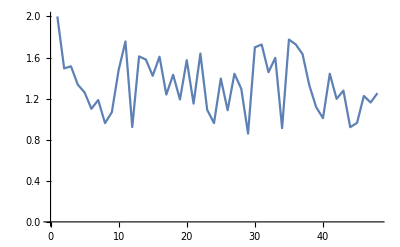

```mathematica
ListPlot[%1200,Joined->True]
```

```mathematica
{{2,m2[[51,2]]},{3,m3[[51,2]]},{4,m4[[51,2]]},{5,m5[[51,2]]},{6,m6[[51,2]]},{7,m7[[51,2]]},{8,m8[[51,2]]},{9,n1[[51,2]]},{10,n2[[51,2]]},{11,n3[[51,2]]},{12,n4[[51,2]]},{13,n5[[51,2]]},{14,n6[[51,2]]},{15,n7[[51,2]]},{16,n8[[51,2]]},{17,o1[[51,2]]},{18,o2[[51,2]]},{19,o3[[51,2]]},{20,o4[[51,2]]},{21,o5[[51,2]]},{22,o6[[51,2]]},{23,o7[[51,2]]},{24,o8[[51,2]]},{25,p1[[51,2]]},{26,p2[[51,2]]},{27,p3[[51,2]]},{28,p4[[51,2]]},{29,p5[[51,2]]},{30,p6[[51,2]]},{31,p7[[51,2]]},{32,p8[[51,2]]},{33,q1[[51,2]]},{34,q2[[51,2]]},{35,q3[[51,2]]},{36,q4[[51,2]]},{37,q5[[51,2]]},{38,q6[[51,2]]},{39,q7[[51,2]]},{40,q8[[51,2]]},{41,r1[[51,2]]},{42,r2[[51,2]]},{43,r3[[51,2]]},{44,r4[[51,2]]},{45,r5[[51,2]]},{46,r6[[51,2]]},{47,r7[[51,2]]},{48,r8[[51,2]]}}
```

{{2,1.27721},{3,1.26978},{4,1.09775},{5,1.05149},{6,1.4726},{7,1.66241},{8,1.63276},{9,1.33332},{10,1.50146},{11,1.54926},{12,1.63636},{13,1.54475},{14,1.49391},{15,0.710403},{16,1.04419},{17,1.35312},{18,1.44207},{19,1.35242},{20,1.17679},{21,0.991106},{22,1.71325},{23,1.15959},{24,1.58848},{25,1.00182},{26,1.18015},{27,1.17359},{28,1.49909},{29,1.35258},{30,1.01644},{31,1.05611},{32,1.55016},{33,1.83713},{34,1.43741},{35,1.42633},{36,1.48839},{37,1.5801},{38,1.82666},{39,1.42709},{40,1.20132},{41,1.5009},{42,1.47636},{43,1.15774},{44,1.52182},{45,1.41907},{46,1.53505},{47,1.46125},{48,1.61891}}

```mathematica
Max[{Min/@%1202}]
```

1.77498

```mathematica
{Max[{Min/@%1745}],Min[{Min/@%1745}],final3[[51,2]]}
```

{1.83713,0.710403,1.36351}

```mathematica
Range[{2,8}]
```

```mathematica
{{1,2,3,4,5,6,7,8}}
```

{{1,2,3,4,5,6,7,8}}

```mathematica
Transpose[{{1,2,3,4,5,6,7,8}}]
```

```mathematica
{{2,Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis27.csv"][[51,2]]},{3,Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis37.csv"][[51,2]]},{4,Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis47.csv"][[51,2]]},{5,Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis57.csv"][[51,2]]},{6,1.7749841758474734},{7,1.2327057227746285},{8,Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis87.csv"][[51,2]]}}
```

```mathematica
{{2,1.786208535999132},{3,1.734279912551775},{4,1.531425868842204},{5,1.3694684195495752},{6,1.7749841758474734},{7,1.2327057227746285},{8,1.1008685453365}}
```

{{2,1.78621},{3,1.73428},{4,1.53143},{5,1.36947},{6,1.77498},{7,1.23271},{8,1.10087}}

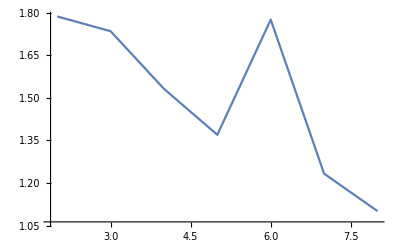

```mathematica
ListPlot[{{2,1.786208535999132},{3,1.734279912551775},{4,1.531425868842204},{5,1.3694684195495752},{6,1.7749841758474734},{7,1.2327057227746285},{8,1.1008685453365}},Joined->True]
```

```mathematica
{{2,1.786208535999132},{3,1.734279912551775},{4,1.531425868842204},{5,1.4925515584194797},{6,1.3658767223896118},{7,1.2327057227746285},{8,1.1008685453365}}
```

{{2,1.78621},{3,1.73428},{4,1.53143},{5,1.49255},{6,1.36588},{7,1.23271},{8,1.10087}}

```mathematica
LinearModelFit[{{2,1.786208535999132},{3,1.734279912551775},{4,1.531425868842204},{5,1.4925515584194797},{6,1.3658767223896118},{7,1.2327057227746285},{8,1.1008685453365}},{x},{x}]
```

FittedModel[2.03926-0.115168 x]

```mathematica
%1754["BestFit"]
```

2.03926-0.115168 x

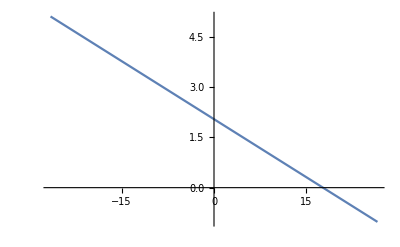

```mathematica
Plot[2.0392591055438296-0.11516848207124218 x,{x,-26.56011960306591,26.56011960306591}]
```

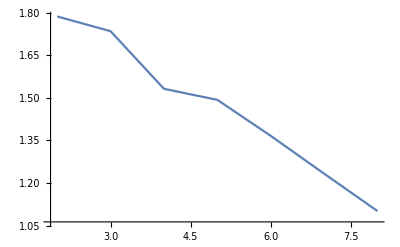

```mathematica
ListPlot[{{2,1.786208535999132},{3,1.734279912551775},{4,1.531425868842204},{5,1.4925515584194797},{6,1.3658767223896118},{7,1.2327057227746285},{8,1.1008685453365}},Joined->True]
```

```mathematica
,Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis53.csv"][[51,2]]
```

1.89043

```mathematica
Plots:={{1.9710719827898209,1.5264390586131849,1.7733498702426056},{1.9330265829354345,1.3264040452094106,1.7301094228271947},{1.8836535762053923,0.9409657514164,1.544572555330029},{1.891992399601113,0.8420814464162356,1.4788923345793457},{1.7749841758474734,0.8591018119021896,1.3658767223896118},{1.7745154281881799,0.6313191746888658,1.2327057227746285},{1.794862270088561,0.4678022384607331,1.0617752668988927}}
```

```mathematica
Plots[[7,3]]
```

1.06178

```mathematica
Range[8]
```

```mathematica
{{1,2,3,4,5,6,7,8}}
```

{{1,2,3,4,5,6,7,8}}

```mathematica
Transpose[{{1,2,3,4,5,6,7,8}}]
```

```mathematica
{{2,Plots[[1,3]]},{3,Plots[[2,3]]},{4,Plots[[3,3]]},{5,Plots[[4,3]]},{6,Plots[[5,3]]},{7,Plots[[6,3]]},{8,Plots[[7,3]]}}
```

{{2,1.77335},{3,1.73011},{4,1.54457},{5,1.47889},{6,1.36588},{7,1.23271},{8,1.06178}}

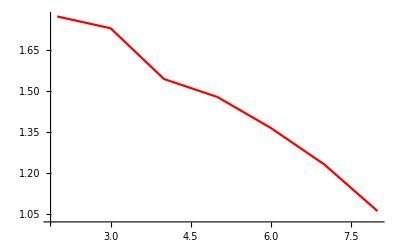

```mathematica
ListPlot[{{2,1.7733498702426056},{3,1.7301094228271947},{4,1.544572555330029},{5,1.4788923345793457},{6,1.3658767223896118},{7,1.2327057227746285},{8,1.0617752668988927}},Joined->True,PlotStyle->Red]
```

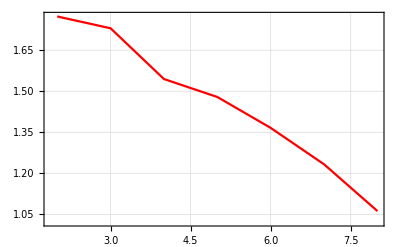

```mathematica
ListPlot[{{2,1.7733498702426056},{3,1.7301094228271947},{4,1.544572555330029},{5,1.4788923345793457},{6,1.3658767223896118},{7,1.2327057227746285},{8,1.0617752668988927}},PlotTheme->"Detailed",Joined->True,PlotStyle->RGBColor[1,0,0]]
```

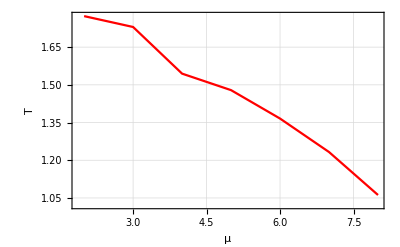

```mathematica
Show[%1397,FrameLabel->{{HoldForm[T],None},{HoldForm[μ],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

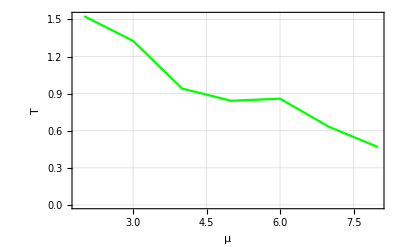

```mathematica
ListLinePlot[{{2,Plots[[1,2]]},{3,Plots[[2,2]]},{4,Plots[[3,2]]},{5,Plots[[4,2]]},{6,Plots[[5,2]]},{7,Plots[[6,2]]},{8,Plots[[7,2]]}},PlotStyle->Green,PlotTheme->"Detailed",FrameLabel->{{HoldForm[T],None},{HoldForm[μ],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

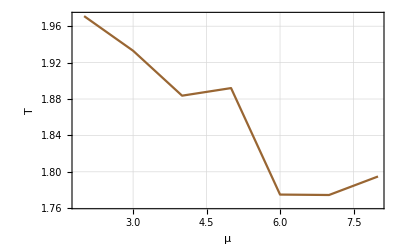

```mathematica
ListLinePlot[{{2,Plots[[1,1]]},{3,Plots[[2,1]]},{4,Plots[[3,1]]},{5,Plots[[4,1]]},{6,Plots[[5,1]]},{7,Plots[[6,1]]},{8,Plots[[7,1]]}},PlotStyle->Brown,PlotTheme->"Detailed",FrameLabel->{{HoldForm[T],None},{HoldForm[μ],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

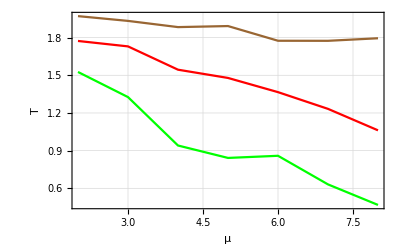

```mathematica
Show[%1398,%1399,%1400,PlotRange->All]
```

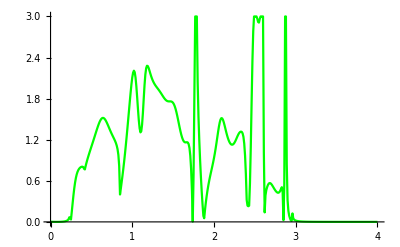

```mathematica
ListLinePlot[r8,PlotStyle->Green]
```

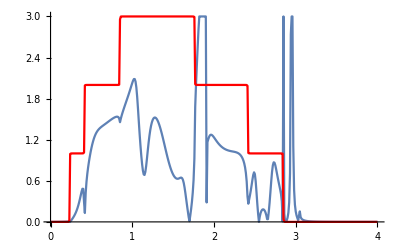

```mathematica
Show[ListLinePlot[q4],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

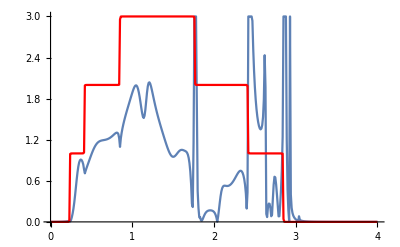

```mathematica
Show[ListLinePlot[p4],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

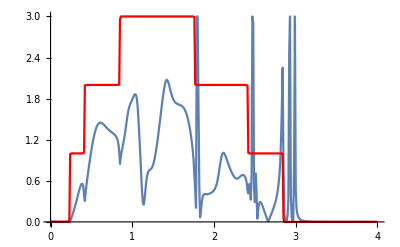

```mathematica
Show[ListLinePlot[m4],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

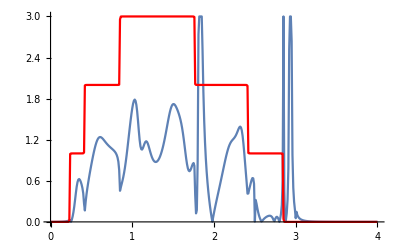

```mathematica
Show[ListLinePlot[n4],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

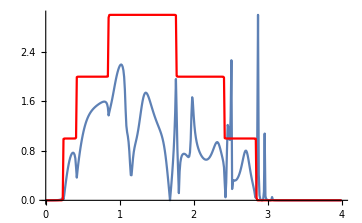

```mathematica
Show[ListLinePlot[r4],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

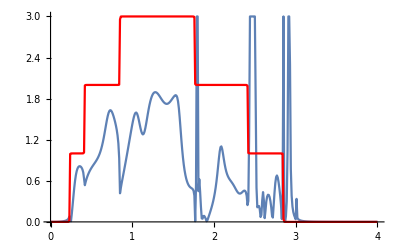

```mathematica
Show[ListLinePlot[r2],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

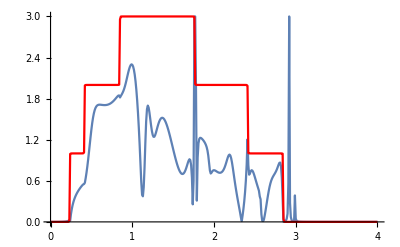

```mathematica
Show[ListLinePlot[r6],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

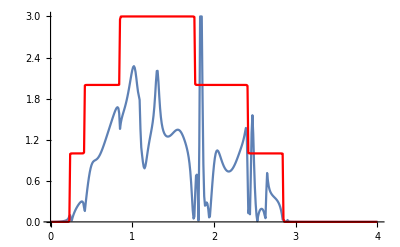

```mathematica
Show[ListLinePlot[p2],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

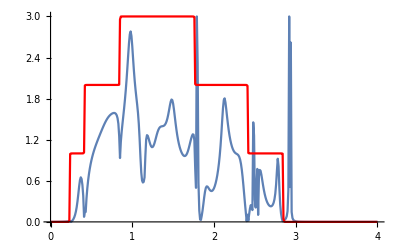

```mathematica
Show[ListLinePlot[p6],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

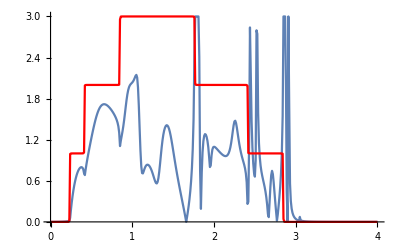

```mathematica
Show[ListLinePlot[p7],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

```mathematica
{{1,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- final[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{2,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{3,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{5,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{7,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{9.,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{11,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{13,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{15,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{17,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{18,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{19,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{20,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{21,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{22,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{23,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{24,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{25,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{26,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{27,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{28,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{29,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{30,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{31,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{32,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{33,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{34,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{35,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{36,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{37,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{38,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{39,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{40,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{41,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{42,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{43,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{44,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{45,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{46,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{47,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{48,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]}}
```

{{1,0.00601808},{2,0.00959809},{3,0.00861083},{4,0.00762},{5,0.00520634},{6,0.0047667},{7,0.00423805},{8,0.00770601},{9.,0.00583017},{10,0.00763525},{11,0.00690184},{12,0.00649634},{13,0.00487467},{14,0.00587189},{15,0.00550587},{16,0.00812098},{17,0.00913116},{18,0.00731088},{19,0.00844099},{20,0.0120471},{21,0.00597082},{22,0.00491657},{23,0.00490935},{24,0.00449193},{25,0.00614044},{26,0.00462198},{27,0.00632585},{28,0.005119},{29,0.00726621},{30,0.00962556},{31,0.00547333},{32,0.00753574},{33,0.00529991},{34,0.00439373},{35,0.00691992},{36,0.00521001},{37,0.00662137},{38,0.00660407},{39,0.00794019},{40,0.00538193},{41,0.00663558},{42,0.00678732},{43,0.00406582},{44,0.00825464},{45,0.00568288},{46,0.010651},{47,0.00643333},{48,0.00750959}}

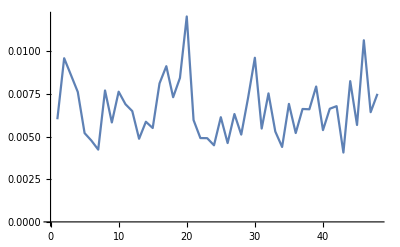

```mathematica
ListPlot[%711,Joined->True]
```

```mathematica
{{1,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- final[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{2,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{3,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{5,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{7,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{9.,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{11,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{13,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{15,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{17,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{18,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{19,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{20,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{21,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{22,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{23,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{24,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{25,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{26,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{27,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{28,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{29,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{30,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{31,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{32,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{33,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{34,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{35,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{36,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{37,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{38,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{39,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{40,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{41,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{42,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{43,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{44,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{45,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{46,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{47,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{48,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]}}
```

{{1,0.00107164},{2,0.000642584},{3,0.000770902},{4,0.000734432},{5,0.00124543},{6,0.00071849},{7,0.00121342},{8,0.00163245},{9.,0.000690775},{10,0.000472136},{11,0.00195552},{12,0.001269},{13,0.0026859},{14,0.00123616},{15,0.00112951},{16,0.000742377},{17,0.00131872},{18,0.00284593},{19,0.000875926},{20,0.000607574},{21,0.00062662},{22,0.00132471},{23,0.00150709},{24,0.00173195},{25,0.00111242},{26,0.00134129},{27,0.00144787},{28,0.00189062},{29,0.00197515},{30,0.00150642},{31,0.000646709},{32,0.000996424},{33,0.000755906},{34,0.00161201},{35,0.00138806},{36,0.000559981},{37,0.0011535},{38,0.0012089},{39,0.00141499},{40,0.00117956},{41,0.00166271},{42,0.000917647},{43,0.000491493},{44,0.000869684},{45,0.00105865},{46,0.00117499},{47,0.000824233},{48,0.00144046}}